Importing Dataset

Exporting all lists of URLS in the chronology page

```mathematica
dataset = Import["http://www-groups.dcs.st-and.ac.uk/history/Indexes/Full_Chron.html",{"Hyperlinks"}];
```

Selecting Links which have a specific pattern

```mathematica
dataset1 =Flatten[StringCases[dataset,"http://www-groups.dcs.st-and.ac.uk/history/Biographies/"~~__]];
```

Exporting the content of each link as text

```mathematica
dataset2 = Import[#,"Text"]&/@dataset1
```

## HTML Parser

```mathematica
TemplateApply;

$mapping=Reverse[Normal[Templating`HTML`PackagePrivate`$SafeHTMLEntities],{2}];

htmlToText[txt_String]:=StringReplace[txt,$mapping]
```

```mathematica
htmls= Map[htmlToText,dataset2]
```

## Exporting List of HTMLs

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\tanha\OneDrive\Documents\GitHub\Summer2018\StudentDeliverables

htmlBioList is a list of all the text files in each biography, with the special characters removed

```mathematica
htmlBioList = Import["C:\\Users\\tanha\\OneDrive\\Documents\\GitHub\\Summer2018\\StudentDeliverables\\htmlbiographies.mx"];
```

```mathematica
ClearAll[x];Clear[y];Clear[l]
```

```mathematica
fullNames =StringCases[htmlBioList,"<h1>"~~x__~~"</h1>"->x];
```

```mathematica
birthdate= Flatten/@StringCases[htmlBioList,"Born:<font color=\"green\"> "~~Shortest[y__]~~" in "~~Shortest[l__]~~"<br>":>{StringReplace[y,"about "-> ""],l}]
```

{{1680 BC,Egypt},{800 BC,India},{750 BC,India},2769,{26 July 1969,Moscow, Russia},{17 July 1975,Adelaide, South Australia, Australia},{3 May 1977,Tehran, Iran}}
 |  |  |  |

```mathematica
birthdate= Flatten/@StringCases[htmlBioList,"Born:<font color=\"green\"> "~~Shortest[y__]~~"<br>"-> y]
```

StringCases::strse: String or list of strings expected at position 1 in StringCases[htmlBioList,Born:<font color="green"> ~~Shortest[y__]~~<br>→y].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[htmlBioList].

StringCases::strse: String or list of strings expected at position 1 in StringCases[Flatten[htmlBioList],Born:<font color="green"> ~~Shortest[y__]~~<br>→y].

StringCases[Flatten[htmlBioList],Born:<font color="green"> ~~Shortest[y__]~~<br>→y]

```mathematica
deathdate= Flatten/@ StringCases[htmlBioList, 
"<font color=\"purple\">"~~Shortest[y__]~~"</font>"-> y]
```

StringCases::strse: String or list of strings expected at position 1 in StringCases[htmlBioList,<font color="purple">~~Shortest[y__]~~</font>→y].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[htmlBioList].

StringCases::strse: String or list of strings expected at position 1 in StringCases[Flatten[htmlBioList],<font color="purple">~~Shortest[y__]~~</font>→y].

StringCases[Flatten[htmlBioList],<font color="purple">~~Shortest[y__]~~</font>→y]

```mathematica
inChecker[{string_,___}]:= If[StringContainsQ[string," in"],StringReplace[string,Shortest[y__]~~" in"~~___:> y], string]
inChecker[{}]:= Missing[]
```

```mathematica
inChecker[name_,{string_,___}]:=rhs
inChecker[name_,{}]:=Missing[name]
```

Returning Birth Dates as date objects in file “BirthDates.mx” after replacing ambiguous entries

```mathematica
ClearAll[y]
```

```mathematica
completebirthDates =inChecker/@birthdate[[;;]]/.{"1st century AD"->"100 AD","2nd century BC"-> "150 BC"};
```

```mathematica
Interpreter["Date"][completebirthDates]
```

```mathematica
birthDateObjects =Import["C:\\Users\\tanha\\OneDrive\\Documents\\GitHub\\Summer2018\\StudentDeliverables\\BirthDates.mx"]
```

{Year: -1680,Year: -800,Year: -750,Year: -624,Year: -611,2766,Day: Sat 12 Jul 1969,Day: Sat 26 Jul 1969,Day: Thu 17 Jul 1975,Day: Tue 3 May 1977}
 |  |  |  |

Find positions of Missing Values and add them manually

```mathematica
Position[birthDateObjects, _Missing]
```

{{121},{390},{467},{908},{1113},{1141},{1328},{2308}}

```mathematica
Flatten@{{121},{390},{467},{908},{1113},{1141},{1328},{2308}}
```

{121,390,467,908,1113,1141,1328,2308}

```mathematica
fullNames[[{121,390,467,908,1113,1141,1328,2308}]]
```

{{Abu'l-Wafa},{De_L'Hopital},{D'Alembert},{D'Ovidio},{Thompson_D'Arcy},{D'Ocagne},{D'Adhemar},{Krasnosel'skii}}

```mathematica
Flatten@Position[completebirthDateObjects,_Failure]
```

{428,630}

```mathematica
fullNames[[%82]]
```

{{Roger Paman},{C V Mourey}}

```mathematica
completebirthDateObjects =ReplacePart [birthDateObjects, {121-> DateObject[{940,6,10},"Day","Gregorian",-4.],390-> DateObject[{1661},"Year","Gregorian",-4.],428-> DateObject[{1700}],467-> DateObject[{1717,11,16},"Day","Gregorian",-4.], 630->DateObject[{1791}], 908-> DateObject[{1842,8,11},"Day","Gregorian",-4.], 1113-> DateObject[{1860,5,2},"Day","Gregorian",-4.],1141-> DateObject[{1862,3,25},"Day","Gregorian",-4.], 1328-> DateObject[{1797,2},"Month","Gregorian",-4.], 2308-> DateObject[{1920,4,27},"Day","Gregorian",-4.]}]
```

{Year: -1680,Year: -800,Year: -750,Year: -624,2767,Day: Sat 12 Jul 1969,Day: Sat 26 Jul 1969,Day: Thu 17 Jul 1975,Day: Tue 3 May 1977}
 |  |  |  |

```mathematica
Position[completebirthDateObjects, _Missing]
```

{}

```mathematica
Position[completebirthDateObjects,_Failure]
```

{}

Death Dates

```mathematica
completedeathDates =inChecker/@deathdate[[;;]]/.{" 1st century AD"->"100 AD"," 2nd century BC"-> "150 BC"};
```

```mathematica
deathDateObjects=Interpreter["Date"][completedeathDates]
```

OptionValue::nodef: Unknown option TimeZone for Internal`ParallelMWACompute.

OptionValue::nodef: Unknown option GeoLocation for Internal`ParallelMWACompute.

OptionValue::nodef: Unknown option MessageHead for Internal`ParallelMWACompute.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

OptionValue::optnf: Option name Context not found in defaults for Internal`ParallelMWACompute.

OptionValue::optnf: Option name TimeConstraint not found in defaults for Internal`ParallelMWACompute.

OptionValue::optnf: Option name ConvertMWASymbols not found in defaults for Internal`ParallelMWACompute.

General::stop: Further output of OptionValue::optnf will be suppressed during this calculation.

$ContextPath::cxlist: Cannot set $ContextPath to ContextPath; value must be a list of strings ending in `.

$Context::cxset: Cannot set $Context to Context; value is not a parsable context name ending in `.

$ContextPath::cxlist: Cannot set $ContextPath to ContextPath; value must be a list of strings ending in `.

$Context::cxset: Cannot set $Context to Context; value is not a parsable context name ending in `.

$ContextPath::cxlist: Cannot set $ContextPath to ContextPath; value must be a list of strings ending in `.

General::stop: Further output of $ContextPath::cxlist will be suppressed during this calculation.

$Context::cxset: Cannot set $Context to Context; value is not a parsable context name ending in `.

General::stop: Further output of $Context::cxset will be suppressed during this calculation.

{Year: -1620,Year: -800,Year: -750,Year: -547,Year: -546,Year: -600,Year: -475,Year: -460,Year: -428,Year: -432,Year: -420,Year: -425,Year: -411,Year: -420,Year: -410,Year: -398,Year: -370,Year: -400,Failure[…],Year: -350,Year: -347,Year: -369,Year: -355,Year: -340,Year: -350,Year: -314,Year: -320,Year: -312,Year: -322,Year: -320,Year: -300,Year: -310,Year: -290,Year: -290,Year: -265,Year: -230,Year: -212,Year: -206,Year: -220,Year: -210,Year: -220,Year: -194,Year: -190,Year: -190,Year: -180,Year: -200,Year: -140,Year: -120,Year: -120,Year: -150,Year: -90,Year: -70,Year: -51,Year: -70,Year: -20,Year: 60,Year: 100,Year: 75,Year: 120,Year: 130,Year: 135,Year: 139,Year: 165,Year: 180,Year: 210,Year: 227,Year: 284,Year: 280,Year: 309,Year: 300,Year: 350,Year: 360,Year: 360,Year: 405,Month: Mar 415,Year: 460,Year: 470,Day: Tue 17 Apr 485,Year: 480,Year: 501,Year: 490,Year: 500,Year: 520,Year: 534,Year: 550,Year: 524,Year: 540,Year: 560,Year: 570,Year: 587,Year: 640,Year: 670,Year: 680,Year: 670,Year: 790,Day: Wed 19 May 804,Year: 850,Year: 860,Missing[NoInput],Failure[…],Year: 860,Year: 870,Year: 873,Failure[…],Year: 873,Failure[…],Year: 880,Year: 890,Year: 912,Day: Fri 18 Feb 901,Year: 900,Year: 930,Year: 929,Year: 930,Year: 922,Year: 943,Year: 971,Year: 946,Year: 980,Year: 1000,Missing[NoInput],Year: 1000,Year: 1000,Year: 1010,Year: 1020,Day: Thu 12 May 1003,Year: 1009,Year: 1029,Year: 1040,Year: 1036,Year: 1029,Day: Wed 13 Dec 1048,Year: 1037,Month: Jun 1037,Failure[…],Year: 1075,Year: 1070,Day: Sun 24 Sep 1054,Year: 1066,Year: 1095,Day: Fri 4 Dec 1131,Year: 1130,Year: 1136,Year: 1160,Year: 1173,Year: 1167,Year: 1160,Year: 1185,Year: 1187,Year: 1180,Year: 1213,Year: 1190,Day: Thu 9 Oct 1253,Year: 1250,Year: 1235,Year: 1279,Year: 1256,Day: Fri 15 Nov 1280,Day: Tue 26 Jun 1274,Year: 1261,Month: Jun 1292,Year: 1283,Day: Thu 13 Sep 1296,Year: 1260,Year: 1316,Year: 1316,Year: 1305,Year: 1298,Year: 1310,Year: 1321,Year: 1320,Year: 1320,Year: 1335,Day: Mon 20 Apr 1344,Day: Tue 9 Apr 1348,Day: Tue 26 Aug 1349,Day: Thu 8 Jul 1390,Year: 1380,Day: Thu 11 Jul 1382,Year: 1410,Year: 1400,Year: 1425,Year: 1436,Year: 1460,Day: Wed 15 Apr 1446,Day: Mon 22 Jun 1429,Day: Sat 27 Oct 1449,Year: 1489,Day: Thu 11 Aug 1464,Day: Wed 3 Apr 1472,Year: 1486,Day: Wed 12 Oct 1492,Day: Mon 8 Apr 1461,Year: 1494,Day: Thu 6 Jul 1476,Year: 1544,Year: 1488,Year: 1517,Day: Fri 2 May 1519,Year: 1498,Day: Fri 5 Nov 1526,Month: May 1522,Year: 1550,Year: 1530,Year: 1553,Day: Fri 6 Apr 1528,Day: Mon 24 May 1543,Day: Fri 18 Dec 1559,Year: 1568,Day: Tue 23 Feb 1560,Day: Wed 19 Apr 1567,Day: Mon 30 Mar 1559,Day: Mon 8 Aug 1555,Day: Tue 22 Jul 1575,Day: Mon 21 Apr 1552,Year: 1543,Year: 1575,Day: Fri 13 Dec 1557,Day: Tue 21 Sep 1576,Day: Fri 11 Aug 1578,Day: Fri 5 Sep 1575,Day: Wed 25 May 1555,Year: 1558,Day: Fri 2 Dec 1594,Day: Wed 4 Dec 1574,Day: Sat 26 Aug 1572,Day: Tue 5 Oct 1565,Year: 1572,Day: Thu 26 Mar 1609,Day: Sat 20 Jan 1590,Year: 1606,Day: Wed 4 Feb 1615,Day: Sun 19 Oct 1586,Day: Tue 23 Nov 1604,Day: Thu 2 Feb 1612,Day: Thu 30 Sep 1632,Day: Fri 31 Dec 1610,Day: Sat 13 Dec 1603,Day: Sat 6 Jan 1607,Day: Wed 24 Oct 1601,Day: Thu 24 Aug 1595,Day: Thu 9 Jan 1586,Day: Mon 30 Aug 1621,Day: Thu 17 Feb 1600,Day: Wed 11 Feb 1626,Month: Feb 1620,Day: Sat 19 Feb 1622,Day: Thu 30 Oct 1631,Day: Tue 4 Apr 1617,Day: Sat 31 Jan 1632,Day: Tue 11 May 1610,Day: Wed 17 Jan 1618,Day: Sun 30 Sep 1612,Day: Sun 31 Mar 1624,Day: Sat 11 Feb 1617,Day: Fri 2 Jul 1621,Day: Sat 26 Jan 1630,Day: Mon 24 Apr 1656,Day: Wed 8 Dec 1632,Day: Tue 2 Jul 1613,Day: Mon 4 May 1615,Day: Tue 8 Nov 1633,Day: Wed 8 Jan 1642,Day: Fri 7 Jun 1624,Day: Sat 11 Apr 1626,Day: Fri 15 Nov 1630,Day: Thu 26 Dec 1624,Day: Mon 18 Jul 1650,Day: Sun 13 Jun 1660,Day: Tue 3 Nov 1643,Day: Thu 9 Apr 1643,Year: 1635,Year: 1643,Day: Fri 30 Oct 1626,Day: Fri 26 Feb 1638,Day: Thu 10 Dec 1626,Day: Mon 6 Nov 1656,Day: Thu 27 Jan 1667,Day: Tue 14 Sep 1638,Month: Jul 1647,Month: Jan 1652,Day: Sun 23 Sep 1657,Day: Sun 17 Mar 1652,Day: Mon 4 Dec 1679,Day: Tue 1 Sep 1648,Day: Sun 24 Sep 1651,Day: Sat 22 Dec 1640,Month: Sep 1661,Day: Sun 24 Oct 1655,Day: Wed 24 Oct 1635,Day: Fri 20 Aug 1677,Day: Wed 8 Dec 1632,Day: Fri 11 Feb 1650,Day: Wed 28 Sep 1667,Day: Mon 16 Feb 1637,Day: Mon 4 Nov 1652,Day: Sat 30 Nov 1647,Day: Tue 5 Apr 1678,Day: Thu 25 Jun 1671,Month: Apr 1684,Year: 1644,Year: 1667,Day: Sun 18 Aug 1652,Day: Mon 12 Jan 1665,Day: Sat 14 Jan 1679,Day: Tue 8 Oct 1652,Day: Sun 27 Oct 1675,Year: 1674,Day: Thu 25 Nov 1694,Day: Mon 7 Sep 1682,Day: Fri 22 Aug 1664,Day: Sun 31 Dec 1679,Day: Mon 8 Mar 1688,Day: Fri 25 Oct 1647,Year: 1660,Year: 1690,Day: Tue 28 Jan 1687,Day: Wed 12 Dec 1685,Day: Fri 6 Aug 1694,Day: Wed 22 Dec 1660,Day: Mon 1 Sep 1687,Day: Sat 19 Nov 1672,Day: Sat 29 May 1660,Year: 1700,Day: Sun 28 Oct 1703,Day: Thu 6 Jan 1689,Day: Fri 28 Dec 1663,Day: Thu 3 Jan 1641,Day: Tue 28 Sep 1694,Year: 1660,Day: Tue 12 May 1682,Day: Wed 5 Apr 1684,Day: Tue 14 Jan 1687,Day: Mon 12 Oct 1682,Day: Mon 28 Mar 1678,Day: Wed 23 May 1691,Day: Mon 25 May 1676,Day: Mon 19 Mar 1685,Day: Sat 22 Sep 1703,Day: Fri 11 Oct 1697,Day: Sat 19 Aug 1662,Day: Wed 10 Nov 1683,Year: 1683,Day: Wed 31 Dec 1659,Day: Tue 4 Nov 1698,Day: Wed 14 Sep 1712,Day: Sat 20 Aug 1672,Year: 1686,Day: Sun 30 Dec 1691,Day: Fri 25 Aug 1679,Day: Tue 15 Apr 1704,Day: Fri 8 Jul 1695,Day: Tue 4 May 1677,Year: 1696,Day: Sat 22 Aug 1676,Day: Thu 25 Feb 1723,Year: 1721,Year: 1660,Day: Sat 3 Mar 1703,Day: Sun 24 Aug 1670,Month: Oct 1675,Day: Sun 13 Oct 1715,Day: Thu 21 Apr 1718,Day: Tue 29 Jan 1715,Day: Sat 26 Jan 1697,Day: Sun 3 Apr 1718,Day: Wed 5 Dec 1708,Day: Mon 31 Mar 1727,Day: Sun 22 Aug 1700,Day: Sun 31 Dec 1719,Day: Sat 14 Nov 1716,Day: Thu 13 May 1734,Day: Tue 22 Dec 1693,Year: 1712,Day: Sun 14 Dec 1710,Day: Sun 3 Feb 1737,Day: Thu 11 Oct 1708,Year: 1706,Day: Wed 8 Nov 1719,Day: Wed 18 Jul 1742,Day: Wed 23 Dec 1722,Day: Sun 16 Aug 1705,Day: Sun 14 Jan 1742,Day: Sat 11 Oct 1698,Day: Tue 24 Feb 1728,Day: Sun 9 Jan 1757,Day: Wed 10 Oct 1708,Day: Sun 29 Dec 1737,Day: Sun 11 Apr 1734,Missing[NoInput],Day: Sat 11 Apr 1711,Day: Thu 11 Oct 1731,Day: Mon 24 Aug 1739,Day: Sun 27 Feb 1735,Day: Mon 1 Jan 1748,Day: Wed 27 Nov 1754,Day: Sun 25 Oct 1733,Day: Tue 22 Aug 1752,Year: 1712,Day: Fri 30 Oct 1739,Day: Sun 29 Dec 1720,Day: Wed 4 Jul 1742,Day: Sun 31 Aug 1721,Day: Sun 15 Feb 1739,Day: Tue 17 May 1729,Day: Tue 1 Jul 1749,Day: Mon 15 Apr 1754,Day: Sun 18 Apr 1756,Day: Tue 1 Dec 1750,Day: Sat 12 May 1742,Day: Thu 18 Dec 1760,Day: Sat 11 Jul 1733,Day: Sat 7 Oct 1719,Day: Sun 20 Jan 1760,Day: Wed 9 Jun 1751,Day: Mon 5 Oct 1761,Day: Sun 20 Nov 1763,Day: Fri 5 Jun 1716,Day: Fri 26 Sep 1766,Day: Fri 14 Feb 1744,Day: Sun 19 Apr 1739,Day: Sun 15 Nov 1761,Day: Sun 14 Jan 1753,Day: Sat 29 Dec 1731,Day: Thu 29 Nov 1759,Day: Sat 1 Oct 1768,Day: Tue 11 Jan 1757,Year: 1748,Day: Wed 28 Feb 1742,Day: Tue 13 Apr 1728,Day: Tue 20 Nov 1764,Year: 1750,Day: Wed 5 Dec 1770,Day: Wed 31 Jul 1726,Day: Tue 15 Aug 1758,Day: Tue 14 Jun 1746,Day: Fri 27 Jul 1759,Day: Wed 4 May 1768,Day: Sun 17 Mar 1782,Day: Sun 2 Sep 1764,Day: Fri 30 Jul 1762,Year: 1768,Day: Mon 20 May 1782,Day: Fri 4 Feb 1774,Day: Fri 17 Apr 1761,Day: Fri 2 Sep 1768,Day: Tue 11 Oct 1791,Day: Tue 4 Jan 1752,Day: Wed 21 Aug 1771,Day: Sun 5 Oct 1777,Day: Wed 10 Sep 1749,Day: Sat 17 Apr 1790,Day: Wed 16 Apr 1788,Day: Thu 18 Sep 1783,Day: Tue 17 Jan 1775,Day: Tue 20 Jul 1751,Day: Sat 17 Jul 1790,Year: 1790,Day: Thu 14 May 1761,Day: Fri 20 Feb 1778,Day: Tue 13 Feb 1787,Day: Sun 21 Aug 1757,Day: Fri 17 May 1765,Day: Sat 4 Sep 1784,Day: Wed 18 Oct 1786,Day: Sun 14 May 1797,Missing[NoInput],Day: Sun 23 Jan 1785,Day: Wed 9 Jan 1799,Day: Thu 16 Nov 1786,Day: Fri 20 Jun 1800,Day: Fri 15 Jan 1790,Day: Sat 6 Dec 1788,Day: Sat 20 Feb 1762,Day: Tue 19 Apr 1791,Day: Tue 10 Aug 1802,Day: Mon 18 Oct 1779,Day: Wed 18 Dec 1799,Day: Sun 26 Mar 1797,Day: Mon 22 Nov 1784,Day: Thu 25 Sep 1777,Day: Sat 31 Aug 1811,Day: Sat 27 Sep 1783,Day: Fri 14 Jan 1814,Day: Thu 9 Oct 1806,Day: Fri 9 Oct 1807,Day: Wed 19 May 1824,Day: Wed 14 Nov 1798,Day: Tue 17 Apr 1787,Day: Sat 4 Apr 1807,Day: Sat 9 Feb 1811,Day: Sun 26 Jun 1796,Day: Tue 19 Feb 1799,Day: Fri 22 Aug 1794,Day: Sat 11 Dec 1819,Day: Tue 28 Jun 1796,Day: Wed 5 Nov 1800,Day: Fri 1 Jan 1796,Day: Sun 20 May 1798,Day: Sat 23 Aug 1806,Day: Sat 10 Apr 1813,Day: Mon 17 Aug 1807,Day: Wed 15 Aug 1798,Day: Mon 27 Jan 1823,Day: Mon 25 May 1807,Day: Sun 25 Aug 1822,Day: Tue 4 Aug 1812,Day: Sat 11 Dec 1784,Day: Thu 17 Mar 1808,Day: Fri 18 Oct 1793,Day: Sat 29 Mar 1794,Day: Mon 13 Jul 1807,Day: Mon 1 Jan 1787,Day: Thu 20 Sep 1804,Day: Sat 11 Jul 1807,Day: Wed 25 Mar 1818,Day: Tue 28 Jul 1818,Day: Thu 3 Feb 1831,Day: Sun 26 Oct 1817,Day: Sat 18 Oct 1845,Day: Tue 20 Jul 1819,Day: Thu 21 Mar 1822,Day: Mon 19 Aug 1822,Day: Thu 5 Apr 1827,Day: Mon 5 Mar 1827,Day: Sun 23 Nov 1817,Day: Sun 9 Jan 1848,Day: Sat 28 Mar 1840,Day: Mon 14 Jul 1800,Day: Thu 2 May 1833,Day: Tue 15 May 1821,Day: Thu 10 Jan 1833,Day: Sat 2 Aug 1823,Day: Mon 21 Jun 1824,Day: Wed 11 Jun 1823,Day: Fri 12 Jun 1835,Year: 1833,Day: Sun 26 Sep 1802,Day: Mon 29 Jul 1839,Day: Wed 4 Jan 1826,Day: Tue 16 Aug 1836,Day: Fri 17 Oct 1817,Day: Mon 18 Apr 1803,Day: Sat 15 Aug 1789,Day: Thu 21 Feb 1839,Day: Sat 13 May 1826,Day: Tue 6 Oct 1840,Day: Tue 27 Nov 1849,Day: Wed 30 Nov 1836,Day: Wed 21 Sep 1842,Day: Wed 24 May 1843,Day: Sun 24 Jun 1832,Day: Thu 21 Apr 1825,Day: Fri 10 May 1822,Day: Mon 14 Sep 1835,Day: Fri 6 Jan 1826,Day: Sat 3 Nov 1832,Day: Wed 7 Jun 1843,Day: Tue 13 Aug 1822,Day: Sun 16 May 1830,Day: Tue 30 Oct 1810,Year: 1832,Day: Mon 30 Jun 1817,Day: Sat 7 May 1842,Day: Sat 17 Apr 1847,Day: Fri 28 Apr 1843,Day: Tue 20 Dec 1836,Day: Fri 13 Mar 1835,Day: Thu 16 Jan 1834,Day: Tue 10 Jan 1843,Day: Wed 4 May 1859,Day: Sat 24 Feb 1844,Day: Thu 9 Mar 1854,Day: Fri 24 Nov 1837,Day: Fri 16 Mar 1838,Day: Wed 22 Jun 1825,Day: Sat 15 Dec 1849,Day: Fri 28 Dec 1827,Day: Sun 10 May 1829,Day: Mon 3 Feb 1862,Day: Tue 2 Feb 1841,Day: Thu 10 Mar 1825,Day: Thu 10 Aug 1843,Day: Fri 10 Jun 1836,Day: Thu 20 Nov 1856,Day: Sat 9 Mar 1833,Day: Mon 24 Feb 1812,Day: Sat 1 Mar 1862,Day: Mon 27 Jun 1831,Day: Thu 25 Sep 1828,Day: Fri 23 Feb 1855,Day: Wed 13 Mar 1833,Day: Mon 5 Dec 1859,Day: Mon 22 May 1815,Day: Mon 8 Aug 1853,Day: Fri 14 Jul 1865,Day: Sat 6 Oct 1855,Day: Fri 29 Nov 1872,Day: Sun 25 Aug 1839,Day: Mon 18 Dec 1848,Day: Wed 20 Jan 1864,Day: Sat 25 Apr 1840,Day: Sat 20 Jun 1863,Day: Fri 29 Apr 1864,Day: Fri 5 Mar 1875,Day: Tue 17 Mar 1846,Day: Sat 18 Jan 1873,Day: Sun 21 Aug 1836,Day: Sun 2 Oct 1853,Day: Mon 12 May 1856,Day: Fri 22 Sep 1837,Day: Mon 11 Sep 1843,Day: Fri 12 Jan 1849,Year: 1847,Day: Fri 12 Mar 1869,Day: Tue 16 Jul 1850,Day: Sat 14 Jul 1827,Day: Tue 6 May 1856,Day: Sun 22 Dec 1867,Day: Mon 26 Mar 1860,Day: Sat 23 May 1857,Day: Thu 6 Jul 1854,Day: Fri 8 May 1874,Day: Sat 26 Sep 1868,Day: Mon 1 Feb 1869,Day: Tue 2 Apr 1872,Day: Wed 18 Oct 1871,Day: Sun 25 Aug 1867,Day: Thu 10 Jun 1875,Failure[…],Day: Mon 8 Nov 1858,Day: Wed 21 Jun 1820,Day: Tue 16 Mar 1841,Day: Tue 19 Sep 1843,Day: Thu 11 May 1871,Day: Sun 24 Feb 1856,Day: Mon 1 Apr 1872,Day: Sat 18 Dec 1880,Day: Mon 31 May 1841,Day: Sat 13 Oct 1866,Day: Sat 28 Feb 1863,Day: Fri 5 Aug 1853,Day: Mon 15 Feb 1847,Day: Fri 13 Feb 1874,Day: Tue 6 Mar 1866,Day: Sat 5 Feb 1881,Day: Thu 28 Mar 1850,Day: Sun 1 May 1870,Day: Sat 15 Dec 1838,Day: Sat 7 Feb 1880,Day: Sun 11 Mar 1849,Day: Wed 17 Dec 1851,Day: Sun 14 Apr 1833,Day: Sat 19 Oct 1878,Day: Sun 13 May 1866,Day: Fri 24 Aug 1832,Day: Tue 17 Feb 1874,Day: Wed 1 Apr 1863,Day: Mon 29 Apr 1872,Day: Wed 27 Jul 1870,Day: Wed 6 Jan 1886,Day: Thu 15 Jul 1841,Day: Sun 22 Mar 1840,Day: Sat 25 Sep 1852,Day: Thu 23 May 1895,Day: Sun 4 Oct 1885,Day: Sat 1 Jun 1867,Day: Thu 28 Jan 1864,Day: Tue 2 Dec 1873,Day: Wed 12 Mar 1834,Day: Wed 14 Dec 1892,Day: Mon 17 Jan 1881,Day: Mon 17 Sep 1877,Day: Sat 2 Jan 1892,Day: Sat 23 May 1885,Day: Sat 31 Mar 1877,Day: Wed 1 Jan 1862,Day: Sat 15 Sep 1883,Day: Fri 22 May 1868,Day: Sat 22 Jan 1859,Day: Mon 6 Apr 1829,Day: Fri 27 Jan 1860,Day: Wed 13 May 1868,Day: Sat 6 Nov 1880,Day: Thu 17 Mar 1853,Day: Tue 28 Sep 1869,Day: Fri 27 Oct 1882,Day: Tue 18 Dec 1855,Day: Thu 12 Dec 1889,Day: Tue 18 Feb 1851,Day: Mon 23 Nov 1863,Day: Thu 15 Feb 1849,Day: Tue 23 Jun 1891,Day: Thu 5 May 1859,Day: Sat 2 Sep 1865,Day: Tue 23 Dec 1890,Day: Mon 15 Apr 1878,Day: Sat 18 Mar 1871,Day: Tue 29 Mar 1870,Day: Mon 4 Feb 1895,Day: Sun 3 May 1885,Day: Sun 12 Mar 1843,Day: Fri 24 Feb 1871,Day: Thu 17 Sep 1891,Day: Tue 30 Jan 1894,Day: Tue 10 Aug 1869,Day: Wed 7 May 1879,Day: Sun 24 Dec 1882,Day: Thu 8 Jun 1882,Day: Wed 26 Sep 1877,Day: Fri 8 Sep 1882,Day: Sun 24 Oct 1847,Day: Sun 24 May 1896,Day: Wed 6 Oct 1880,Day: Thu 28 Dec 1871,Day: Thu 9 Dec 1880,Day: Sun 14 May 1893,Day: Thu 31 May 1832,Day: Sun 13 Apr 1890,Day: Tue 4 Aug 1874,Day: Sun 23 Sep 1877,Year: 1882,Day: Mon 18 Jun 1883,Day: Mon 7 Jun 1847,Day: Mon 17 Jul 1899,Month: Jun 1882,Day: Sat 17 Dec 1853,Day: Fri 23 Feb 1844,Day: Sat 2 Sep 1854,Day: Wed 14 Feb 1894,Day: Fri 20 Jul 1883,Day: Sun 6 Oct 1878,Day: Wed 30 Nov 1892,Day: Wed 22 Aug 1855,Day: Mon 1 Jul 1872,Day: Wed 20 Mar 1895,Day: Mon 15 Mar 1897,Day: Sun 21 May 1848,Day: Thu 8 Dec 1864,Day: Sat 27 Nov 1852,Day: Wed 26 Apr 1876,Day: Fri 19 Feb 1897,Day: Mon 5 Aug 1872,Day: Tue 12 Jun 1900,Day: Sat 14 May 1887,Day: Wed 6 Dec 1893,Day: Sun 27 Jun 1880,Day: Wed 20 Sep 1882,Day: Fri 18 Sep 1891,Day: Thu 7 Mar 1889,Day: Tue 5 Feb 1889,Day: Thu 8 Jun 1893,Day: Fri 5 Apr 1861,Day: Thu 21 Jan 1892,Day: Thu 13 Mar 1884,Day: Wed 22 Jun 1892,Day: Wed 9 Sep 1885,Day: Sun 27 Jan 1895,Day: Fri 18 Sep 1896,Day: Tue 11 Feb 1868,Day: Fri 22 Jan 1904,Day: Mon 2 Mar 1885,Day: Sun 1 Feb 1903,Day: Sat 3 Jan 1891,Day: Tue 13 Dec 1870,Day: Mon 12 Aug 1901,Day: Sat 13 Aug 1910,Day: Sun 9 Sep 1883,Day: Tue 24 Dec 1872,Day: Sat 1 Mar 1884,Day: Sat 26 Jan 1895,Day: Sat 8 Dec 1894,Day: Sun 31 Oct 1897,Day: Fri 21 Oct 1881,Day: Sat 8 Sep 1894,Day: Wed 11 Aug 1880,Day: Thu 13 Aug 1896,Day: Tue 3 Apr 1900,Day: Fri 24 Aug 1888,Day: Tue 17 Jan 1911,Day: Mon 14 Jan 1901,Day: Thu 24 Jun 1880,Day: Thu 4 Jan 1894,Day: Wed 3 Jan 1912,Day: Thu 11 Aug 1892,Day: Sat 9 Oct 1909,Day: Tue 22 Dec 1885,Day: Mon 11 Oct 1852,Day: Mon 14 Jun 1886,Day: Tue 29 Dec 1891,Day: Thu 7 Feb 1901,Day: Mon 9 May 1904,Day: Tue 14 Dec 1897,Day: Mon 21 Jul 1873,Day: Wed 11 Sep 1861,Day: Mon 17 Oct 1887,Day: Tue 17 Dec 1907,Day: Sat 12 Mar 1898,Day: Fri 20 Mar 1903,Day: Tue 27 Mar 1888,Day: Wed 27 Jun 1883,Day: Tue 27 Aug 1912,Day: Thu 15 Feb 1900,Day: Sun 29 Apr 1894,Day: Thu 13 May 1915,Day: Mon 11 Mar 1895,Day: Fri 20 Jul 1866,Day: Fri 9 Feb 1883,Day: Fri 31 Jul 1896,Day: Thu 4 Mar 1897,Day: Tue 1 Jan 1884,Day: Thu 18 Sep 1913,Day: Sun 11 Jan 1903,Day: Sat 4 Feb 1893,Day: Tue 19 Apr 1881,Day: Fri 9 Apr 1920,Day: Thu 15 Mar 1900,Day: Tue 31 Dec 1912,Day: Sat 31 Jan 1903,Day: Sun 3 Jan 1892,Day: Wed 18 Nov 1891,Day: Wed 10 Jun 1903,Day: Tue 16 Feb 1892,Day: Mon 29 Nov 1920,Day: Fri 9 Nov 1906,Day: Sat 12 Feb 1916,Day: Sun 7 Apr 1889,Day: Tue 11 Dec 1906,Day: Wed 5 Nov 1879,Day: Fri 7 Jun 1907,Day: Sat 9 Nov 1907,Day: Thu 4 Jul 1901,Day: Wed 17 May 1916,Day: Fri 9 Mar 1866,Day: Fri 14 Jan 1898,Day: Tue 19 Nov 1912,Day: Wed 7 Oct 1903,Day: Fri 27 Mar 1925,Day: Fri 19 Aug 1910,Day: Sat 7 Sep 1918,Day: Sun 29 Jan 1905,Day: Sun 5 May 1901,Day: Thu 7 Nov 1872,Day: Fri 5 Feb 1915,Day: Sun 29 Jan 1905,Day: Sat 26 Apr 1902,Day: Wed 6 Jun 1888,Day: Sun 23 Mar 1924,Day: Sat 14 Aug 1886,Day: Wed 4 Apr 1923,Day: Fri 10 Sep 1915,Day: Sun 18 Feb 1900,Day: Thu 11 Sep 1890,Day: Sun 13 Aug 1882,Day: Thu 7 Nov 1918,Day: Sun 19 Oct 1890,Day: Thu 2 Feb 1911,Year: 1891,Day: Sun 11 Jul 1909,Day: Sun 18 Oct 1903,Day: Sat 7 Jan 1893,Day: Thu 16 Jun 1910,Day: Wed 31 Mar 1920,Day: Wed 7 Feb 1912,Day: Thu 11 Jun 1903,Day: Sat 21 Dec 1912,Day: Thu 15 Dec 1921,Day: Tue 1 Sep 1908,Day: Sun 25 Oct 1914,Day: Mon 27 Dec 1909,Day: Sat 4 Aug 1906,Day: Tue 12 Oct 1926,Day: Wed 8 Apr 1925,Day: Thu 16 Apr 1914,Day: Thu 26 Dec 1889,Day: Sun 22 Jan 1922,Day: Wed 2 Jul 1919,Day: Mon 26 Sep 1910,Day: Mon 28 Jan 1889,Day: Fri 29 Aug 1930,Day: Tue 28 Apr 1903,Day: Fri 29 Aug 1873,Day: Sat 11 Apr 1908,Day: Sun 19 Apr 1914,Day: Fri 5 Aug 1910,Day: Wed 21 Nov 1866,Day: Fri 31 May 1907,Day: Tue 6 Jan 1920,Day: Sat 14 Jan 1905,Day: Tue 25 Nov 1913,Day: Sat 10 Aug 1918,Day: Wed 21 Feb 1912,Day: Mon 10 Jul 1916,Day: Sat 5 Mar 1927,Day: Mon 22 Mar 1926,Day: Thu 14 Mar 1907,Day: Fri 1 Apr 1921,Day: Sat 14 May 1927,Day: Wed 19 Feb 1908,Day: Mon 10 Apr 1911,Day: Mon 16 Jun 1902,Day: Sat 12 Apr 1919,Day: Sun 28 Jul 1895,Day: Tue 19 Feb 1929,Day: Sat 8 Jun 1935,Day: Sun 20 Jan 1907,Day: Fri 23 Feb 1917,Missing[NoInput],Day: Sat 18 Feb 1899,Day: Sat 3 Oct 1891,Day: Tue 29 May 1917,Day: Mon 30 Jun 1919,Day: Wed 21 Feb 1912,Day: Fri 6 Jan 1922,Day: Wed 14 Dec 1927,Day: Wed 25 Oct 1905,Day: Wed 20 Dec 1916,Day: Sat 17 May 1913,Day: Sun 24 Feb 1929,Day: Mon 7 May 1934,Day: Thu 26 Mar 1914,Day: Sat 20 Sep 1930,Day: Wed 30 Nov 1921,Day: Mon 13 Oct 1913,Day: Sun 27 Nov 1904,Day: Sat 21 Jun 1913,Day: Fri 24 May 1912,Day: Fri 5 Oct 1906,Day: Thu 23 May 1889,Day: Wed 14 Sep 1910,Day: Wed 16 Apr 1919,Day: Wed 21 Mar 1934,Day: Tue 13 Dec 1921,Day: Sat 6 May 1916,Day: Wed 25 Oct 1933,Day: Thu 23 Feb 1922,Day: Mon 16 Jan 1922,Day: Sun 6 Jan 1918,Day: Mon 3 Mar 1879,Day: Sat 7 Dec 1912,Day: Mon 28 Oct 1918,Day: Sat 13 Feb 1926,Day: Sun 6 Nov 1921,Day: Sun 20 Dec 1931,Day: Fri 11 May 1923,Day: Tue 20 Oct 1896,Day: Fri 24 Feb 1933,Day: Thu 27 Jan 1927,Day: Thu 7 Jul 1927,Day: Tue 13 May 1919,Day: Thu 22 Aug 1907,Day: Fri 16 Oct 1925,Day: Fri 18 Apr 1913,Day: Mon 8 Oct 1883,Day: Fri 15 Mar 1912,Day: Sat 25 Oct 1884,Day: Sat 27 Dec 1930,Day: Thu 7 Oct 1920,Day: Sat 10 Oct 1925,Day: Thu 10 Feb 1927,Day: Sun 11 Feb 1923,Day: Wed 5 Mar 1930,Day: Tue 5 Oct 1909,Day: Tue 8 Dec 1896,Day: Thu 17 Mar 1921,Day: Fri 19 Jul 1878,Day: Sat 29 Oct 1921,Day: Tue 23 Sep 1919,Day: Tue 8 Apr 1919,Day: Sun 26 Jul 1925,Day: Fri 7 Dec 1928,Day: Sat 3 Feb 1923,Day: Sat 10 May 1941,Day: Thu 20 Jul 1911,Day: Fri 17 Mar 1922,Day: Sun 11 Dec 1910,Day: Thu 25 Jan 1894,Day: Wed 15 Sep 1943,Day: Fri 3 Aug 1917,Day: Wed 3 Jun 1903,Day: Sat 27 Aug 1898,Day: Fri 21 Apr 1922,Day: Mon 22 Jun 1925,Day: Tue 8 Apr 1913,Day: Tue 4 Dec 1934,Day: Sat 18 Nov 1933,Day: Sat 27 Feb 1915,Day: Sun 29 Jun 1924,Day: Sat 4 Apr 1925,Day: Mon 14 Aug 1922,Day: Sat 29 Apr 1916,Day: Tue 3 Feb 1925,Day: Tue 10 Feb 1891,Day: Wed 25 Jun 1941,Day: Mon 5 Jul 1926,Day: Thu 10 Apr 1930,Day: Fri 7 Jul 1922,Day: Fri 3 Nov 1911,Day: Sat 22 Aug 1925,Day: Fri 29 Sep 1939,Day: Wed 21 Jul 1937,Day: Thu 21 Feb 1901,Day: Fri 23 Aug 1935,Day: Tue 17 Dec 1912,Day: Tue 3 Apr 1888,Day: Mon 27 Oct 1930,Day: Mon 29 Dec 1941,Day: Mon 12 Aug 1935,Day: Sat 29 Jan 1910,Day: Wed 8 Feb 1933,Day: Mon 1 May 1916,Day: Sun 21 Aug 1927,Day: Sun 22 Mar 1914,Day: Tue 21 Jul 1925,Day: Mon 17 Jun 1918,Day: Fri 26 Jun 1903,Day: Sun 13 Jun 1909,Day: Fri 8 Nov 1940,Day: Sat 26 Jan 1929,Day: Mon 6 Mar 1939,Day: Thu 10 Mar 1921,Day: Thu 23 Jul 1903,Day: Mon 9 Jan 1939,Day: Thu 16 Mar 1922,Day: Sat 12 Mar 1932,Day: Sat 4 Feb 1928,Day: Sun 1 Mar 1908,Day: Fri 10 Jul 1936,Day: Thu 6 Aug 1925,Day: Sun 27 May 1928,Day: Thu 23 Aug 1923,Day: Thu 16 Jan 1941,Day: Wed 16 Jun 1948,Day: Sat 24 Mar 1945,Day: Wed 25 Dec 1929,Day: Wed 5 Apr 1933,Day: Wed 14 Jan 1914,Day: Sat 1 Mar 1913,Day: Wed 17 Jul 1912,Day: Sun 28 Dec 1919,Day: Mon 9 Mar 1931,Day: Tue 17 Jul 1917,Day: Fri 24 Oct 1930,Day: Thu 30 Mar 1944,Day: Fri 28 Jan 1910,Day: Tue 8 May 1900,Day: Thu 29 Oct 1914,Day: Thu 24 Jan 1935,Day: Fri 28 Sep 1928,Day: Wed 4 Aug 1920,Day: Tue 26 Nov 1935,Day: Mon 13 Oct 1913,Day: Sat 7 Jul 1900,Day: Wed 6 Jun 1928,Day: Sun 14 Jan 1912,Day: Wed 19 Apr 1933,Day: Thu 26 Oct 1922,Failure[…],Day: Thu 20 Jul 1922,Day: Mon 11 Jun 1934,Day: Fri 8 Feb 1907,Day: Thu 11 Dec 1941,Day: Fri 21 Jun 1929,Day: Mon 3 Jan 1927,Day: Mon 31 Dec 1894,Day: Wed 6 Aug 1947,Day: Mon 5 Nov 1934,Day: Sun 5 Jul 1942,Day: Thu 24 Apr 1930,Day: Sun 9 Nov 1890,Day: Mon 1 Jan 1894,Day: Fri 15 Nov 1929,Day: Tue 19 May 1942,Day: Sun 3 Nov 1918,Day: Mon 27 Apr 1936,Year: 1921,Day: Tue 13 Jun 1939,Day: Sat 22 Dec 1928,Day: Tue 2 Jun 1942,Day: Fri 29 Jun 1934,Day: Tue 1 Apr 1930,Day: Wed 25 Nov 1936,Day: Wed 14 Jan 1931,Day: Thu 29 Oct 1931,Day: Wed 20 Apr 1932,Day: Sat 4 Oct 1947,Day: Tue 10 Nov 1931,Day: Tue 2 Oct 1962,Day: Thu 14 Aug 1930,Day: Wed 12 Sep 1906,Day: Mon 5 Sep 1921,Day: Tue 21 Nov 1939,Day: Thu 10 Jan 1929,Day: Sun 29 Aug 1937,Day: Sat 22 Jan 1921,Day: Tue 18 Nov 1919,Day: Thu 5 Mar 1925,Day: Mon 7 Jan 1935,Day: Sun 26 Jul 1942,Day: Wed 27 Mar 1929,Day: Sat 19 Nov 1949,Day: Sun 12 Aug 1928,Day: Sat 10 May 1924,Day: Sun 17 Nov 1929,Day: Thu 3 Aug 1922,Day: Sun 17 Mar 1946,Day: Sun 17 Oct 1937,Year: 1941,Day: Sat 1 Mar 1913,Day: Sat 31 Aug 1940,Day: Sat 29 Jul 1944,Day: Tue 17 Dec 1940,Missing[NoInput],Day: Fri 11 Oct 1940,Day: Fri 13 Apr 1906,Day: Fri 21 Mar 1952,Year: 1935,Day: Wed 21 Jan 1931,Day: Mon 2 Nov 1914,Day: Sat 19 Jul 1947,Day: Wed 26 May 1926,Day: Thu 14 Sep 1916,Day: Mon 29 Sep 1941,Day: Wed 6 Oct 1954,Day: Fri 18 Jul 1930,Day: Sat 28 Jun 1930,Day: Sat 16 Mar 1940,Day: Mon 24 Jan 1955,Day: Sun 1 Jun 1941,Day: Sun 19 Mar 1922,Day: Thu 25 Dec 1941,Day: Sun 2 Jun 1946,Day: Fri 21 May 1937,Day: Thu 20 May 1943,Day: Tue 30 Dec 1947,Day: Sun 6 May 1928,Day: Mon 16 Nov 1925,Day: Mon 9 Apr 1951,Day: Wed 1 Nov 1922,Day: Wed 1 Oct 1924,Missing[NoInput],Day: Thu 18 Oct 1917,Day: Sun 14 Feb 1943,Day: Fri 24 Jan 1930,Day: Sat 19 Mar 1938,Day: Sat 30 Jan 1954,Day: Tue 9 Feb 1937,Day: Sun 16 May 1943,Day: Thu 6 Sep 1951,Day: Fri 30 Dec 1932,Day: Sun 14 Oct 1956,Day: Tue 12 Sep 1933,Day: Fri 12 Dec 1919,Day: Mon 6 Jan 1930,Failure[…],Day: Wed 17 Oct 1923,Day: Sat 10 Dec 1949,Day: Fri 11 Jan 1946,Day: Tue 9 Aug 1932,Day: Tue 19 Dec 1939,Day: Fri 26 Oct 1945,Day: Wed 5 Jun 1940,Day: Sat 24 Nov 1900,Day: Sun 18 Apr 1943,Day: Sat 3 Feb 1940,Day: Sat 10 Feb 1951,Day: Fri 29 Dec 1939,Day: Wed 1 Oct 1930,Year: 1944,Day: Thu 9 Jul 1953,Day: Sun 29 Oct 1933,Day: Sun 14 Mar 1937,Day: Tue 30 Sep 1930,Day: Thu 22 Apr 1948,Day: Sun 18 May 1924,Day: Mon 12 Oct 1936,Day: Tue 7 Mar 1922,Day: Fri 14 May 1909,Day: Wed 2 Jun 1943,Day: Mon 3 Dec 1945,Day: Tue 7 Jul 1942,Day: Mon 23 Nov 1942,Day: Tue 19 Nov 1918,Day: Mon 9 Mar 1942,Day: Sun 26 Mar 1933,Day: Tue 12 Jan 1909,Day: Thu 22 Jul 1943,Day: Sat 16 Dec 1933,Day: Sun 30 May 1926,Day: Thu 30 Aug 1928,Day: Thu 12 May 1927,Day: Sun 25 Dec 1921,Day: Sun 27 Apr 1952,Day: Mon 4 May 1936,Day: Wed 5 Feb 1947,Day: Mon 10 Jan 1944,Day: Thu 17 Oct 1963,Day: Mon 6 Mar 1944,Day: Sat 14 Sep 1912,Day: Thu 16 May 1935,Day: Wed 16 Sep 1931,Day: Thu 25 Jan 1940,Day: Sat 14 Aug 1943,Day: Wed 11 Aug 1948,Day: Thu 22 Mar 1934,Day: Fri 17 Oct 1952,Day: Thu 13 Aug 1959,Day: Mon 15 Jan 1945,Day: Sat 17 Mar 1956,Day: Tue 10 Sep 1946,Day: Mon 17 Feb 1947,Day: Sat 23 Jul 1938,Day: Sat 11 Nov 1933,Day: Sun 31 May 1931,Day: Sun 16 Dec 1934,Day: Wed 17 Aug 1927,Day: Thu 18 Nov 1948,Day: Tue 14 Aug 1934,Day: Fri 9 Dec 1938,Day: Tue 7 Nov 1939,Day: Sun 12 Aug 1945,Day: Wed 4 Jul 1962,Year: 1942,Day: Fri 2 Mar 1962,Day: Fri 23 Jan 1953,Day: Thu 12 Sep 1918,Day: Thu 5 Apr 1951,Day: Wed 3 Mar 1954,Day: Sun 20 Feb 1955,Day: Thu 25 Feb 1960,Day: Sat 7 Nov 1936,Day: Mon 25 Dec 1944,Day: Thu 8 Sep 1938,Day: Mon 7 May 1962,Day: Mon 28 Jan 1946,Day: Thu 16 Sep 1937,Day: Mon 11 Oct 1943,Failure[…],Day: Wed 15 May 1907,Day: Wed 29 Mar 1944,Day: Wed 20 Dec 1944,Day: Mon 3 Aug 1914,Day: Sat 26 Jan 1952,Day: Thu 2 Jan 1930,Day: Thu 10 Jun 1948,Day: Sat 25 Jul 1953,Day: Mon 26 Jan 1942,Day: Sat 11 Jan 1941,Day: Mon 12 Dec 1921,Day: Mon 7 Jun 1937,Day: Tue 6 Sep 1949,Day: Mon 1 Jul 1957,Day: Thu 25 Nov 1937,Day: Thu 26 Apr 1951,Day: Wed 3 Oct 1951,Day: Mon 14 Sep 1925,Day: Fri 20 Nov 1908,Day: Sun 6 May 1951,Day: Thu 8 Oct 1942,Day: Thu 10 Sep 1931,Day: Sun 19 May 1940,Day: Fri 8 May 1953,Day: Sun 22 Oct 1950,Day: Sat 8 Feb 1936,Day: Sat 5 Dec 1959,Day: Wed 4 Jan 1950,Day: Fri 26 Apr 1946,Day: Fri 9 Mar 1917,Day: Thu 11 Nov 1954,Day: Sat 28 Dec 1935,Day: Wed 27 Apr 1960,Day: Tue 11 Mar 1924,Day: Sat 15 Mar 1941,Day: Mon 12 May 1952,Day: Tue 4 Jun 1946,Day: Tue 26 Jan 1937,Day: Sat 22 Nov 1930,Day: Wed 25 Aug 1926,Day: Wed 22 Jan 1936,Day: Sat 15 Mar 1952,Day: Fri 3 Feb 1956,Day: Tue 8 Mar 1949,Day: Fri 14 Jun 1946,Day: Fri 11 Aug 1939,Day: Sat 8 Nov 1952,Day: Tue 12 Jun 1945,Day: Sat 7 Feb 1948,Day: Sat 14 Jul 1956,Day: Mon 14 Sep 1959,Day: Sat 29 Sep 1928,Failure[…],Day: Tue 26 Jun 1951,Day: Thu 21 May 1953,Day: Sat 23 Apr 1927,Day: Tue 29 Mar 1932,Day: Mon 11 Jul 1955,Day: Mon 13 Aug 1956,Day: Tue 21 Sep 1937,Day: Fri 19 Jan 1951,Day: Sun 15 Apr 1934,Day: Sun 7 Dec 1952,Day: Tue 31 Dec 1929,Day: Tue 10 Sep 1946,Day: Mon 2 Feb 1970,Day: Thu 20 Jan 1955,Day: Tue 20 Nov 1934,Day: Wed 5 Sep 1917,Day: Thu 23 Feb 1961,Day: Tue 6 Jan 1953,Day: Fri 16 Nov 1945,Day: Thu 2 Feb 1950,Day: Fri 5 Mar 1954,Day: Thu 28 Dec 1944,Day: Sun 26 Nov 1916,Day: Sun 7 Mar 1943,Day: Mon 29 Dec 1941,Day: Fri 25 Jan 1935,Year: 1944,Day: Mon 22 May 1967,Day: Fri 8 Oct 1954,Day: Thu 11 May 1916,Day: Wed 28 Sep 1949,Day: Sat 24 Mar 1956,Day: Sun 15 Dec 1940,Day: Tue 5 Jul 1932,Day: Sun 29 Nov 1953,Month: Feb 1945,Missing[NoInput],Day: Sun 17 Jan 1954,Day: Wed 18 Aug 1943,Day: Tue 25 Nov 1952,Day: Tue 13 Aug 1957,Day: Sun 5 Feb 1939,Day: Thu 16 Nov 1922,Day: Mon 11 Nov 1957,Day: Tue 26 Jul 1955,Year: 1953,Day: Sat 24 Aug 1929,Day: Thu 21 Jul 1966,Day: Sat 31 Aug 1918,Day: Tue 11 Jul 1950,Day: Tue 19 Feb 1946,Day: Sun 14 Nov 1954,Day: Sat 26 Jul 1941,Day: Fri 18 Aug 1961,Day: Fri 19 Sep 1958,Day: Sat 15 Aug 1953,Day: Fri 10 Jan 1941,Day: Mon 29 Feb 1960,Day: Mon 29 Feb 1932,Day: Sun 8 Sep 1963,Day: Tue 8 May 1951,Day: Mon 13 Nov 1944,Day: Tue 14 Apr 1964,Day: Thu 28 Oct 1965,Day: Thu 28 Jan 1954,Day: Sat 16 Oct 1937,Day: Tue 6 Nov 1934,Day: Wed 3 Feb 1943,Year: 1953,Day: Sun 30 May 1943,Day: Wed 22 Jan 1975,Day: Wed 16 Dec 1959,Day: Sun 6 Aug 1939,Day: Wed 14 Sep 1932,Day: Mon 23 Oct 1944,Day: Sat 25 May 1963,Day: Mon 27 Jan 1947,Day: Thu 30 Apr 1959,Year: 1946,Day: Mon 7 Mar 1966,Day: Tue 31 Mar 1964,Day: Mon 9 May 1932,Day: Mon 4 Oct 1954,Day: Mon 1 Dec 1947,Day: Mon 16 Sep 1946,Year: 1935,Day: Sat 19 Feb 1938,Day: Thu 23 Mar 1961,Day: Sun 6 Dec 1925,Day: Mon 31 Dec 1956,Day: Mon 3 Dec 1956,Day: Fri 4 Oct 1918,Day: Thu 8 Dec 1966,Day: Fri 27 Jun 1952,Year: 1953,Day: Sun 3 Feb 1929,Day: Sat 10 Aug 1929,Day: Mon 4 Jun 1973,Day: Wed 10 May 1933,Day: Mon 7 Sep 1936,Day: Wed 25 Jan 1956,Day: Fri 7 Jan 1955,Day: Tue 26 Jul 1932,Day: Mon 21 Aug 1933,Day: Sun 5 May 1957,Day: Mon 13 Feb 1956,Day: Thu 17 Sep 1970,Day: Tue 2 May 1967,Day: Mon 18 Apr 1955,Day: Sun 6 Jun 1943,Day: Tue 24 Jul 1934,Day: Wed 1 Oct 1919,Day: Wed 11 May 1955,Day: Tue 2 Apr 1946,Day: Sun 17 Jun 1956,Day: Fri 2 Jul 1926,Day: Fri 8 Dec 1961,Day: Wed 31 Jan 1934,Day: Mon 28 Dec 1964,Day: Sat 26 Oct 1968,Day: Tue 15 Aug 1922,Day: Sun 20 Aug 1950,Day: Sun 7 Sep 1947,Day: Mon 25 Sep 1933,Day: Thu 15 Oct 1959,Day: Wed 9 Aug 1950,Day: Sat 1 Oct 1955,Year: 1950,Day: Sat 22 Feb 1975,Day: Tue 28 Feb 1956,Day: Wed 10 Mar 1948,Day: Mon 17 Feb 1964,Day: Wed 10 Aug 1960,Year: 1970,Day: Fri 2 Dec 1966,Day: Sat 12 Feb 1977,Day: Tue 9 Jan 1962,Day: Sun 22 Mar 1953,Day: Fri 26 Nov 1965,Day: Tue 7 May 1963,Day: Sun 3 Sep 1967,Day: Wed 30 Sep 1953,Day: Thu 4 Nov 1954,Day: Sat 11 Jan 1947,Day: Fri 15 Feb 1974,Day: Thu 15 Feb 1940,Day: Sat 30 May 1964,Day: Wed 17 Nov 1954,Day: Sat 26 Jul 1941,Day: Mon 21 Jan 1946,Day: Mon 5 Jan 1970,Day: Wed 9 Mar 1955,Day: Fri 29 Aug 1975,Day: Tue 10 Dec 1968,Day: Wed 22 Nov 1944,Day: Sat 6 Feb 1965,Day: Sat 20 Apr 1957,Day: Mon 6 Aug 1945,Day: Fri 4 Oct 1974,Day: Sun 14 Apr 1935,Day: Tue 21 Oct 1969,Day: Tue 9 Jan 1973,Day: Sat 9 Oct 1948,Day: Wed 21 Dec 1960,Day: Mon 20 Apr 1942,Day: Thu 30 Jun 1960,Day: Sun 1 Oct 1972,Day: Thu 28 Mar 1946,Day: Tue 28 Mar 1950,Day: Sun 21 Apr 1946,Day: Sun 28 Oct 1917,Day: Mon 3 Feb 1964,Day: Sat 25 Feb 1950,Day: Fri 28 Dec 1951,Day: Sun 21 Feb 1932,Day: Tue 14 Jul 1953,Day: Tue 21 May 1957,Day: Wed 20 Jan 1971,Day: Sat 26 Mar 1966,Day: Sun 12 Oct 1919,Day: Tue 11 Feb 1947,Day: Sun 12 Nov 1944,Failure[…],Day: Mon 21 Jan 1974,Day: Sun 1 Jun 1947,Day: Thu 21 Jul 1966,Day: Sat 13 Mar 1965,Day: Sun 28 Nov 1943,Day: Thu 19 Oct 1944,Day: Thu 5 Oct 1972,Day: Thu 1 Nov 1962,Day: Wed 10 Sep 1941,Day: Sun 6 Nov 1966,Day: Mon 26 Jun 1967,Day: Wed 22 May 1935,Day: Sun 30 Dec 1956,Day: Fri 19 Dec 1952,Month: Mar 1955,Day: Sat 28 Jun 1952,Day: Fri 18 Oct 1974,Day: Wed 12 Apr 1944,Day: Mon 3 Sep 1984,Day: Tue 9 Nov 1954,Day: Sat 17 Mar 1962,Day: Sun 18 Nov 1962,Day: Tue 15 Aug 1978,Day: Sun 2 Aug 1970,Day: Mon 16 Dec 1946,Day: Fri 24 Jul 1964,Day: Thu 16 Mar 1933,Day: Tue 19 Jan 1954,Day: Tue 6 Sep 1977,Day: Wed 14 Jul 1943,Day: Sat 4 Jul 1981,Day: Mon 11 Apr 1977,Day: Sat 4 Mar 1967,Day: Tue 28 May 1968,Day: Mon 12 Oct 1970,Year: 1967,Day: Tue 12 Mar 1946,Day: Thu 4 May 1961,Day: Fri 9 Dec 1955,Year: 1953,Day: Wed 6 Apr 1938,Day: Wed 1 Sep 1982,Day: Sun 14 Apr 1957,Day: Thu 13 Sep 1945,Day: Mon 13 May 1957,Day: Sat 11 Nov 1967,Day: Fri 3 Oct 1952,Day: Sat 13 May 1939,Day: Wed 15 Dec 1971,Day: Mon 27 Jan 1969,Day: Sun 27 Sep 1964,Day: Thu 4 Sep 1969,Day: Fri 27 Jun 1975,Day: Tue 2 Feb 1965,Day: Fri 12 Feb 1960,Day: Fri 10 May 1957,Day: Mon 22 Jan 1951,Day: Mon 31 Dec 1962,Day: Sat 8 Dec 1973,Day: Thu 10 Nov 1988,Day: Thu 13 Feb 1947,Day: Thu 30 Oct 1975,Day: Tue 9 Dec 1958,Day: Sat 4 May 1974,Day: Sat 7 Sep 1985,Day: Fri 25 May 1956,Day: Mon 26 Apr 1920,Day: Wed 4 Jan 1961,Day: Sat 23 Mar 1963,Day: Mon 11 Feb 1974,Day: Fri 25 Feb 1972,Day: Tue 4 Apr 1961,Day: Thu 23 Sep 1971,Day: Sat 4 Jan 1958,Day: Mon 8 Feb 1971,Day: Sun 18 Sep 1977,Day: Sat 13 May 1944,Year: 1962,Day: Tue 18 May 1954,Day: Sun 30 Mar 1930,Day: Tue 16 Jun 1970,Day: Thu 27 Jan 1972,Day: Sun 3 Jan 1960,Day: Mon 6 Oct 1958,Day: Wed 16 Sep 1925,Day: Fri 24 Jan 1964,Day: Wed 6 Nov 1946,Day: Sat 3 Jan 1920,Day: Sun 26 Aug 1962,Day: Thu 4 Oct 1973,Day: Thu 6 Jan 1955,Day: Tue 19 Jun 1945,Day: Sun 12 Mar 1972,Day: Fri 13 Nov 1942,Day: Wed 21 Feb 1962,Day: Sat 13 Oct 1979,Day: Sun 18 Nov 1945,Day: Mon 4 Apr 1949,Day: Sat 31 Jan 1976,Day: Mon 22 Sep 1975,Day: Mon 10 Apr 1967,Day: Sat 25 May 1946,Year: 1959,Day: Mon 21 Sep 1981,Day: Fri 28 Jul 1944,Day: Sat 3 Oct 1914,Day: Tue 14 Aug 1956,Day: Mon 28 Sep 1953,Year: 1975,Day: Thu 27 Feb 1975,Day: Wed 2 Oct 1929,Day: Sat 22 Jul 1950,Day: Wed 30 Aug 1961,Day: Tue 6 Oct 1959,Day: Sun 29 Apr 1951,Day: Fri 14 Jul 1972,Day: Thu 3 Mar 1988,Day: Sun 4 Jul 1954,Day: Tue 8 Jun 1948,Day: Mon 1 Jul 1963,Day: Thu 27 Dec 1973,Day: Sun 30 Jan 1977,Day: Thu 17 Jul 1980,Day: Wed 25 Apr 1945,Day: Sun 29 Jul 1962,Day: Fri 25 Jul 1980,Day: Fri 8 Mar 1974,Day: Mon 3 Aug 1959,Day: Mon 12 Feb 1962,Year: 1974,Day: Mon 7 Jan 1974,Day: Mon 2 Nov 1970,Failure[…],Day: Sun 30 Nov 1958,Day: Fri 15 Oct 1965,Day: Tue 17 Nov 1953,Day: Sun 16 Mar 1941,Day: Sat 27 Apr 1957,Day: Sat 18 Mar 1989,Day: Wed 21 Aug 1974,Day: Sun 13 Jul 1941,Day: Thu 9 Apr 1953,Day: Fri 7 Sep 1956,Day: Sat 11 Mar 1967,Day: Fri 8 May 1936,Day: Tue 9 Apr 2002,Day: Sun 20 Mar 1983,Day: Sat 20 Jul 1968,Month: Jun 1953,Day: Fri 31 Aug 1945,Day: Thu 18 Aug 1960,Day: Thu 19 Mar 1987,Day: Tue 29 Apr 1975,Day: Tue 11 Jan 1949,Day: Thu 9 Jun 1977,Day: Mon 9 Mar 1942,Day: Fri 25 Nov 1988,Day: Wed 22 Jun 1977,Day: Wed 29 Apr 1981,Day: Fri 7 Feb 1969,Day: Tue 29 May 1962,Day: Mon 11 Oct 1948,Day: Thu 13 May 1965,Day: Tue 15 Mar 1960,Day: Sat 5 Oct 1985,Day: Mon 22 Jan 1990,Day: Thu 22 Mar 1973,Day: Sun 19 Mar 1978,Day: Tue 25 Jun 1974,Day: Mon 8 Jan 1968,Year: 1973,Day: Wed 28 Jun 1972,Day: Sun 24 Aug 1975,Day: Wed 24 Mar 1976,Day: Tue 11 May 1965,Day: Thu 20 Nov 1986,Day: Thu 8 Jul 1971,Day: Fri 5 Jan 1951,Day: Tue 21 Dec 1954,Day: Mon 26 Dec 1966,Day: Thu 22 Feb 1979,Day: Mon 4 Feb 1974,Year: 1985,Day: Wed 2 Jul 1947,Day: Wed 29 Apr 1970,Day: Wed 23 Jan 1952,Day: Tue 12 Feb 1980,Day: Thu 3 Jun 1971,Day: Wed 18 Nov 1959,Day: Sat 5 Feb 1977,Day: Thu 24 Apr 1952,Day: Sat 17 Aug 1974,Day: Mon 20 Jun 1966,Day: Wed 5 Aug 1981,Day: Thu 23 Jul 1964,Day: Fri 7 Sep 1951,Failure[…],Day: Sat 21 Oct 2000,Day: Sun 21 Dec 1919,Day: Fri 24 Nov 1978,Day: Wed 18 Mar 1964,Day: Wed 11 Feb 1976,Day: Fri 3 Nov 1967,Day: Wed 23 Jan 1991,Day: Mon 6 Jun 1977,Day: Wed 4 Jul 1956,Day: Fri 28 Nov 1969,Day: Sat 31 Aug 1946,Day: Fri 1 Jul 1983,Day: Wed 26 Dec 1973,Failure[…],Day: Thu 17 Aug 1944,Day: Mon 21 Aug 1961,Day: Wed 28 May 1980,Day: Thu 12 Jun 1980,Day: Sun 12 Dec 1965,Day: Sun 27 Apr 1941,Day: Fri 19 Feb 1988,Day: Wed 21 May 1958,Day: Wed 7 Aug 1985,Day: Thu 6 Dec 1973,Day: Mon 24 Dec 1962,Day: Tue 16 Nov 1982,Month: Apr 1985,Day: Tue 8 Feb 1983,Day: Tue 25 Mar 1975,Day: Mon 24 Oct 1966,Day: Wed 18 Jun 1980,Day: Fri 23 Mar 1979,Day: Thu 21 Sep 1950,Month: Mar 1978,Day: Fri 14 Sep 1973,Day: Mon 28 Jan 1985,Day: Sat 7 Apr 1934,Day: Sun 31 Aug 1975,Day: Sat 4 Apr 1981,Day: Tue 2 Feb 1971,Day: Tue 5 Sep 1972,Day: Wed 7 Jul 1982,Day: Mon 18 Mar 1935,Day: Mon 1 Jan 1996,Day: Thu 7 Oct 1965,Day: Sat 30 Apr 1977,Day: Sat 24 Dec 1955,Day: Wed 12 Feb 1958,Day: Tue 22 Sep 1970,Day: Fri 13 Sep 1940,Day: Wed 22 Feb 1984,Day: Sun 10 Apr 1988,Day: Wed 21 Jul 1993,Day: Wed 21 Apr 1954,Day: Mon 23 Nov 1942,Day: Mon 5 Jan 1987,Day: Thu 30 Mar 1995,Day: Tue 21 Nov 1978,Day: Tue 6 Nov 1979,Day: Thu 20 Dec 1962,Year: 1979,Day: Fri 29 Mar 1946,Day: Mon 21 Nov 1966,Day: Mon 27 Mar 1972,Day: Fri 27 Dec 1974,Day: Wed 27 Jan 1965,Day: Wed 26 Dec 1979,Day: Wed 9 Jul 1980,Day: Mon 15 Jan 1968,Day: Wed 26 Jun 1946,Day: Thu 23 Aug 1973,Day: Tue 10 Oct 1961,Day: Thu 20 Jun 1963,Month: Aug 1970,Day: Sat 26 May 1984,Day: Sun 17 Aug 1924,Day: Wed 26 Sep 1979,Day: Sat 14 Jul 1956,Day: Wed 9 Jul 1980,Day: Sun 2 May 1982,Day: Sat 22 Jul 1995,Day: Mon 16 Jun 1975,Day: Mon 9 Nov 1981,Day: Fri 9 Apr 1982,Day: Sat 3 Jul 1999,Day: Mon 12 Apr 1971,Year: 1983,Day: Fri 7 May 1954,Day: Mon 19 Feb 1990,Day: Tue 13 Aug 1968,Month: Dec 1942,Month: Sep 1943,Day: Fri 31 May 1991,Day: Fri 18 Jan 1963,Day: Fri 4 Jul 1986,Day: Wed 14 Mar 1973,Day: Thu 2 Sep 1982,Day: Tue 6 Apr 1993,Day: Fri 3 Apr 1998,Day: Sun 22 Apr 1945,Day: Sun 25 Oct 1970,Day: Tue 17 Oct 1978,Day: Wed 1 Sep 1982,Day: Wed 22 Jul 1959,Day: Wed 6 Sep 1967,Year: 1968,Day: Wed 15 Oct 1980,Day: Mon 15 Dec 1958,Day: Fri 7 Dec 1979,Day: Tue 18 Apr 1961,Day: Tue 12 Jan 1960,Day: Fri 21 Nov 1980,Day: Sat 1 Feb 1986,Day: Mon 31 Oct 1988,Day: Fri 27 Apr 1979,Day: Wed 31 Mar 1971,Day: Sat 30 May 1992,Day: Tue 3 Jun 1980,Day: Sat 15 Jul 1961,Day: Sat 31 Oct 1987,Day: Sun 17 Apr 1977,Day: Sat 16 Feb 1980,Day: Thu 7 Jun 1990,Day: Thu 26 Nov 1981,Day: Sat 28 Jul 1956,Day: Sun 28 Nov 1954,Day: Fri 31 Dec 1982,Day: Tue 30 May 1933,Day: Mon 21 Aug 1972,Day: Sun 1 Feb 1976,Day: Sun 31 Dec 1944,Day: Mon 1 Jan 1968,Day: Thu 9 Jan 1975,Day: Wed 1 Mar 1978,Day: Mon 15 Jan 1973,Day: Tue 22 Mar 1977,Failure[…],Day: Sun 2 Jun 1929,Failure[…],Day: Wed 26 Oct 1983,Day: Thu 30 Jan 1992,Day: Sun 10 Dec 1995,Day: Fri 5 May 1972,Year: 1949,Day: Mon 16 May 1983,Day: Mon 22 Oct 1979,Day: Mon 15 Nov 1976,Day: Thu 25 Jun 1936,Day: Sat 20 Oct 1984,Day: Tue 24 Aug 1971,Day: Fri 29 Nov 1991,Year: 1999,Day: Sat 26 Apr 1980,Day: Sun 16 Sep 1979,Day: Mon 28 Nov 1994,Day: Sun 24 Jul 1983,Day: Thu 31 Jul 1980,Day: Mon 9 Jul 1984,Day: Sat 5 Oct 1985,Year: 1984,Day: Sat 25 Oct 1997,Day: Tue 26 Jun 1990,Day: Sun 20 Mar 1977,Day: Wed 13 Dec 1950,Day: Sun 12 Sep 1971,Day: Sun 25 Jun 1989,Day: Sun 1 Jan 1995,Day: Fri 17 Jun 1994,Day: Sat 5 Sep 1959,Day: Fri 15 Dec 2000,Day: Tue 10 Jan 1984,Day: Sat 27 Jan 1973,Day: Fri 11 Aug 1995,Day: Tue 9 Oct 1990,Day: Thu 28 Nov 1968,Day: Thu 22 Jan 1987,Day: Wed 22 May 1974,Day: Sat 1 Jan 1977,Day: Sun 22 Jan 1989,Day: Mon 7 Jul 1975,Day: Sat 18 Dec 1999,Day: Tue 20 Oct 1987,Day: Sat 6 Oct 1979,Failure[…],Day: Thu 25 Feb 1988,Day: Tue 8 Aug 1989,Day: Sat 13 Dec 1997,Day: Thu 9 Aug 1990,Day: Sun 26 Aug 1973,Day: Sun 16 Mar 1980,Day: Tue 25 Apr 1978,Day: Sun 19 Jan 1930,Day: Sat 26 Aug 1961,Day: Mon 16 Mar 1992,Day: Sun 19 Dec 1993,Day: Wed 21 Feb 1990,Day: Sat 22 Oct 1977,Day: Sun 3 Dec 1995,Day: Mon 9 Jan 1989,Day: Thu 2 Dec 1982,Day: Thu 9 Jun 1994,Day: Fri 12 Jan 1996,Day: Fri 8 Feb 1957,Day: Wed 15 Jan 1958,Day: Mon 18 Jul 1977,Day: Sat 10 Jan 1976,Day: Fri 8 May 1959,Day: Wed 13 Aug 2008,Day: Sat 22 Nov 1986,Day: Mon 8 Oct 1973,Day: Wed 9 Mar 1994,Day: Sat 27 Sep 1997,Day: Sun 13 May 2001,Day: Mon 24 May 1976,Day: Mon 19 Mar 1990,Day: Sat 24 Dec 1994,Day: Thu 5 Jun 1986,Day: Thu 30 Dec 1982,Day: Sun 4 Jul 1993,Day: Thu 6 Sep 1956,Day: Mon 16 Feb 1976,Day: Thu 17 Dec 1964,Day: Sat 25 Feb 1956,Day: Tue 23 Aug 1988,Year: 1942,Day: Sun 8 Feb 1976,Day: Sun 25 Apr 1999,Day: Thu 1 Jun 1989,Day: Tue 8 Mar 1988,Day: Sun 9 Sep 1973,Day: Thu 28 Nov 1968,Day: Sun 1 Feb 1942,Day: Wed 23 Oct 1985,Day: Thu 15 Jan 1987,Day: Fri 5 May 1989,Day: Sun 8 May 1960,Day: Mon 8 Sep 1969,Day: Sat 12 Aug 1989,Day: Tue 6 Jun 1972,Day: Thu 20 Nov 1986,Day: Sun 24 Jan 1982,Day: Mon 11 Sep 1995,Day: Thu 19 Oct 1972,Day: Sat 22 Sep 1979,Day: Sat 13 Oct 1990,Day: Sat 26 Jan 1974,Day: Fri 15 Sep 1978,Day: Sun 28 Nov 2004,Day: Mon 2 Aug 1976,Year: 1986,Day: Sun 30 Apr 1989,Day: Fri 3 Nov 1972,Day: Wed 22 May 1991,Year: 1992,Day: Thu 14 Oct 1982,Day: Thu 25 Jan 1973,Day: Thu 5 Nov 1981,Day: Sat 26 Nov 1977,Day: Wed 16 Feb 1977,Day: Wed 29 Oct 1975,Year: 1974,Day: Wed 13 Feb 1980,Day: Sun 20 Oct 1974,Month: Oct 1979,Day: Sat 24 Sep 1938,Day: Thu 31 Jan 1980,Day: Tue 4 Sep 1984,Day: Wed 25 Jan 1995,Day: Wed 16 Oct 1985,Day: Sun 29 Jan 1984,Day: Sun 24 Dec 2000,Day: Thu 11 May 1995,Day: Sun 5 Sep 1982,Day: Sun 6 Mar 2005,Day: Mon 26 Apr 1976,Day: Sat 16 Jun 1990,Day: Sat 20 Jul 1985,Day: Sun 29 Nov 1992,Day: Fri 15 Apr 1983,Day: Fri 27 Dec 1996,Day: Wed 14 Jan 1970,Day: Wed 15 Jun 1938,Day: Thu 26 Jun 1997,Day: Thu 7 Nov 1968,Day: Sat 14 Jan 1978,Day: Tue 4 Nov 1986,Day: Wed 1 Jan 1992,Day: Thu 1 Jun 2006,Day: Wed 31 May 2000,Year: 1990,Day: Mon 7 May 2007,Day: Tue 10 Nov 1998,Day: Tue 24 Aug 1993,Day: Tue 10 Mar 1981,Day: Mon 21 Dec 1987,Day: Fri 25 Dec 1981,Day: Mon 21 May 1973,Day: Sun 4 Jun 2000,Day: Wed 9 Jul 1986,Day: Sat 23 Dec 1989,Day: Sun 25 Sep 1955,Day: Wed 8 Apr 1992,Day: Thu 23 Jul 1964,Day: Wed 9 Nov 1966,Day: Thu 2 Aug 1962,Day: Sat 7 Oct 1995,Year: 1993,Year: 1996,Day: Thu 6 Aug 1998,Day: Tue 8 Oct 1985,Day: Sat 7 Mar 1964,Day: Wed 2 Feb 2005,Day: Sat 17 Jul 1993,Day: Tue 9 Mar 1993,Day: Fri 11 Oct 1996,Day: Fri 17 Sep 1999,Day: Sun 10 Dec 1995,Day: Mon 31 Mar 2003,Day: Mon 9 Jun 1969,Day: Thu 20 Dec 1984,Day: Mon 30 Oct 1989,Day: Wed 24 Oct 1979,Day: Tue 29 Mar 1983,Day: Tue 17 Oct 1989,Day: Tue 2 Nov 1993,Day: Mon 5 Mar 1990,Day: Mon 15 Oct 1990,Day: Sun 17 Oct 1976,Day: Tue 8 Jan 1980,Day: Fri 7 Apr 1933,Day: Tue 19 Sep 1995,Day: Sun 23 Sep 1984,Day: Tue 5 Jul 1977,Day: Tue 1 Oct 1996,Day: Tue 19 Feb 1985,Day: Fri 2 Dec 1977,Day: Wed 10 May 1989,Day: Sun 2 Apr 1995,Day: Thu 22 Aug 1974,Day: Tue 30 May 1989,Day: Fri 14 Jul 1967,Day: Sun 27 Dec 1992,Day: Fri 19 Apr 1974,Day: Sun 25 Mar 1984,Day: Mon 12 Dec 1977,Day: Sat 1 Jan 1994,Day: Tue 25 Jan 2000,Day: Wed 2 Dec 1992,Day: Mon 28 Apr 1975,Day: Mon 27 Jul 1931,Day: Wed 10 Jun 1992,Day: Tue 18 May 1971,Day: Thu 2 Jan 1992,Day: Mon 1 Apr 1968,Day: Fri 4 Aug 1967,Day: Wed 29 Aug 1990,Day: Tue 15 Dec 1970,Day: Tue 3 May 1988,Day: Mon 25 Dec 2000,Day: Thu 4 Apr 1991,Day: Mon 29 May 1978,Day: Mon 16 Apr 1956,Day: Tue 24 Nov 1987,Day: Tue 3 Jan 1989,Day: Sat 4 May 1974,Day: Thu 22 Dec 1994,Day: Sun 16 Aug 1981,Day: Wed 11 Feb 1942,Day: Wed 30 Aug 1978,Day: Fri 15 Feb 1974,Day: Fri 1 Oct 1982,Day: Sat 27 Aug 1988,Day: Thu 13 Feb 1992,Day: Thu 28 Jun 1984,Day: Sat 29 Mar 1980,Day: Wed 24 Feb 1954,Day: Fri 23 Jul 1993,Day: Sat 4 Aug 1945,Day: Sun 26 Aug 2001,Day: Sat 19 May 1979,Day: Tue 25 Jan 1994,Day: Thu 14 Apr 2005,Day: Fri 7 Jul 1967,Day: Sun 15 Mar 1992,Day: Sat 30 Dec 1978,Day: Mon 21 Oct 2002,Day: Sun 3 Mar 1991,Day: Wed 5 Feb 2003,Day: Sat 25 Nov 1978,Day: Sun 24 Dec 2000,Day: Sun 13 May 1984,Day: Sat 14 Jun 1969,Day: Sat 31 Mar 2001,Day: Sun 15 Apr 1990,Day: Fri 26 Dec 1997,Day: Tue 8 Jan 2002,Day: Mon 12 Mar 1990,Day: Mon 21 Aug 1995,Day: Wed 26 Sep 1990,Day: Mon 7 Jan 1974,Day: Mon 7 Jun 2004,Day: Sat 16 Oct 1982,Day: Fri 22 Feb 1985,Day: Wed 4 Jul 1990,Day: Wed 28 Mar 1973,Day: Fri 18 Dec 1970,Day: Wed 12 Jun 1985,Day: Sun 5 Dec 1999,Day: Thu 10 Feb 1994,Day: Thu 15 Apr 1999,Day: Tue 26 Feb 1985,Day: Sun 1 Jan 2006,Day: Mon 21 Mar 1960,Year: 1940,Day: Tue 16 May 1989,Day: Tue 27 Oct 1998,Day: Wed 7 Mar 1984,Day: Thu 14 Oct 1971,Day: Sun 26 Sep 1976,Day: Wed 14 Feb 2001,Day: Thu 16 Jul 1981,Day: Mon 18 Dec 1995,Year: 1987,Day: Sun 27 May 1962,Day: Fri 22 Nov 1996,Day: Fri 3 Dec 2004,Day: Thu 10 Aug 1995,Day: Thu 28 Jan 1988,Day: Wed 7 Sep 1994,Year: 1982,Day: Sat 10 Jan 1998,Day: Tue 17 Aug 2004,Day: Sat 24 Jun 1978,Day: Fri 22 May 2009,Day: Fri 27 Aug 1999,Day: Fri 27 Jan 1995,Day: Thu 22 Nov 2001,Day: Fri 26 Aug 1977,Day: Tue 11 Nov 1997,Day: Mon 31 Oct 1988,Day: Sun 28 Aug 2005,Day: Thu 21 Jun 2007,Day: Wed 3 Jul 1991,Day: Tue 27 Jul 1999,Day: Tue 22 Aug 2006,Day: Sat 25 Jul 1992,Day: Sat 19 Aug 2000,Year: 1987,Day: Thu 14 Oct 1982,Day: Wed 7 Oct 1992,Day: Wed 27 Dec 1995,Day: Fri 8 Mar 1985,Day: Tue 11 Apr 1989,Day: Sun 22 Mar 1987,Day: Thu 6 Feb 1992,Day: Mon 7 Apr 1986,Day: Fri 10 Oct 1975,Day: Tue 19 Jan 1982,Day: Fri 28 May 1982,Day: Fri 5 Jun 1964,Day: Sun 10 Aug 2014,Day: Fri 14 Aug 1987,Day: Wed 31 Jan 1973,Day: Sat 16 Nov 2002,Day: Sun 23 Dec 2001,Day: Wed 27 Dec 1967,Day: Mon 7 Jun 1954,Year: 1993,Day: Thu 21 Nov 1991,Day: Tue 18 Apr 2000,Day: Sun 13 Apr 2014,Day: Fri 24 Jan 1992,Day: Tue 16 Jan 2007,Day: Fri 30 Jan 1998,Day: Fri 20 Sep 1996,Day: Sat 16 Jun 2001,Day: Sun 23 Dec 1973,Day: Mon 5 Oct 2009,Day: Wed 16 Jun 2004,Day: Mon 27 Jul 1987,Day: Fri 22 Aug 1975,Day: Tue 9 Jul 1968,Day: Tue 8 Jul 2008,Day: Sat 11 Sep 1943,Day: Sat 8 Aug 2009,Day: Fri 2 Oct 2009,Day: Tue 1 Apr 2003,Day: Thu 29 Jul 1999,Day: Mon 14 May 1984,Day: Thu 2 Mar 1978,Day: Fri 29 Oct 1993,Day: Mon 28 Apr 1986,Day: Fri 19 Oct 1979,Day: Wed 7 May 1980,Day: Fri 23 Nov 1979,Day: Wed 20 Jun 2012,Day: Fri 13 May 2005,Day: Mon 11 Sep 1972,Day: Fri 29 Oct 1993,Day: Sun 22 Apr 1945,Day: Sat 22 May 2010,Day: Thu 28 Feb 1991,Day: Sun 18 Jan 1981,Day: Fri 26 Oct 1984,Day: Thu 6 Dec 1990,Day: Thu 13 Jan 2005,Day: Sat 18 Feb 1995,Day: Sun 14 Nov 1971,Day: Sat 8 Oct 2005,Day: Tue 26 Nov 1968,Day: Sun 21 Dec 1980,Day: Sat 16 Oct 1993,Day: Fri 6 Dec 1996,Day: Thu 25 May 1972,Day: Fri 7 Feb 2003,Day: Mon 31 Mar 1997,Day: Tue 14 Nov 2006,Day: Mon 8 Aug 1977,Day: Fri 21 Jun 1940,Day: Sat 18 Apr 2009,Day: Wed 7 Jan 1998,Day: Mon 20 Aug 2001,Day: Wed 6 May 2009,Day: Mon 10 Nov 2008,Year: 1995,Day: Sat 26 Jul 1997,Day: Fri 11 Dec 1998,Day: Tue 29 Oct 1985,Day: Fri 30 Jun 1972,Day: Fri 28 Feb 2014,Day: Thu 1 Dec 1977,Day: Tue 16 Feb 1999,Day: Mon 18 Dec 2006,Day: Mon 21 Apr 2008,Day: Sat 27 Jan 2001,Day: Mon 12 Feb 2001,Day: Sun 27 Sep 2009,Day: Thu 4 Jul 2002,Day: Wed 26 Jul 2000,Day: Sun 18 Dec 1994,Day: Wed 13 Nov 2002,Day: Wed 5 Jan 1994,Day: Tue 3 Oct 2006,Day: Thu 8 May 2008,Day: Mon 2 Sep 2002,Day: Fri 18 Nov 1994,Day: Thu 8 Nov 2001,Day: Sun 5 Apr 2009,Day: Mon 2 Oct 2006,Day: Fri 30 May 2008,Day: Wed 30 Oct 1991,Day: Wed 15 Mar 2006,Day: Sat 3 Dec 1983,Day: Sun 23 Jul 2006,Day: Fri 8 Apr 2005,Day: Thu 22 Sep 2005,Day: Tue 3 May 1988,Day: Sat 24 Feb 2001,Day: Tue 11 Jul 1995,Day: Wed 4 Sep 1996,Day: Tue 25 Nov 2008,Day: Tue 28 Jul 1987,Day: Sun 17 Aug 1975,Day: Sun 9 Apr 1972,Day: Tue 7 Apr 2009,Day: Tue 8 Apr 2008,Day: Mon 26 Oct 1998,Day: Thu 5 Jan 1978,Day: Sun 25 Jun 2006,Day: Sat 2 Oct 1999,Day: Sat 21 Jun 1947,Day: Fri 30 Mar 2007,Day: Wed 16 Apr 2008,Day: Wed 8 Jun 1988,Day: Tue 4 Jul 2006,Day: Sat 14 Jun 2008,Day: Sun 6 Oct 1968,Day: Tue 9 Aug 1994,Day: Mon 1 Nov 1971,Day: Tue 20 Dec 1988,Day: Mon 6 Aug 2007,Day: Thu 2 May 2002,Day: Fri 17 Feb 2012,Day: Wed 20 Apr 1994,Day: Sat 26 Apr 2014,Day: Mon 15 Feb 1988,Missing[NoInput],Day: Sat 1 Aug 1992,Day: Fri 20 Apr 2001,Day: Tue 18 Jan 2011,Missing[NoInput],Day: Tue 23 Oct 2007,Day: Tue 30 Sep 2003,Day: Fri 6 May 1983,Day: Thu 1 Dec 1983,Day: Fri 16 Aug 2013,Day: Thu 11 Apr 1974,Day: Tue 10 Nov 1970,Day: Sat 16 Jul 1994,Day: Sun 30 Aug 1998,Day: Tue 5 Apr 1955,Day: Fri 27 Aug 1976,Day: Sat 27 Mar 2010,Day: Tue 6 Oct 2015,Day: Sun 25 Jun 1978,Day: Thu 8 Jul 2010,Day: Sat 10 Sep 2005,Day: Thu 28 Mar 2013,Day: Sat 3 Jun 1995,Day: Wed 28 Nov 2012,Day: Thu 21 Apr 2005,Day: Tue 10 Jul 2007,Day: Tue 17 Dec 2002,Day: Tue 30 Jul 1985,Day: Mon 3 Dec 1984,Day: Mon 11 Feb 2008,Day: Mon 23 Aug 2004,Day: Tue 8 May 2001,Day: Mon 6 Feb 2017,Day: Sat 4 Nov 2000,Day: Fri 12 Oct 1984,Day: Fri 14 Jan 2000,Day: Fri 17 Feb 2017,Day: Sun 5 Oct 1986,Day: Sun 7 May 2017,Day: Thu 30 Mar 2000,Day: Mon 19 Mar 1984,Day: Tue 22 Feb 2011,Day: Wed 14 Sep 1983,Day: Thu 16 Apr 1998,Day: Wed 15 Dec 1971,Day: Wed 21 Apr 2010,Day: Mon 7 Nov 2016,Day: Sat 8 Oct 2005,Day: Sun 2 May 2004,Day: Tue 12 Jul 2011,Missing[NoInput],Day: Tue 21 Feb 2012,Day: Mon 12 Dec 1994,Day: Mon 1 Jun 1998,Day: Sat 3 Dec 2016,Day: Wed 5 Jun 1985,Day: Sun 10 May 1992,Missing[NoInput],Day: Sat 6 Nov 1993,Day: Fri 15 Nov 1996,Day: Mon 5 Dec 2005,Day: Mon 29 Jul 1996,Day: Mon 12 Sep 1983,Day: Sun 9 Apr 1989,Day: Sat 10 Dec 2011,Day: Mon 5 Sep 1994,Day: Thu 20 Apr 2006,Day: Tue 27 Oct 1987,Day: Tue 3 Sep 1996,Day: Fri 7 Mar 2008,Day: Mon 18 Nov 1985,Day: Fri 17 Oct 2008,Day: Thu 21 Jul 2016,Day: Tue 4 Jan 2005,Missing[NoInput],Day: Sun 30 Oct 2011,Day: Mon 21 Aug 2006,Day: Mon 18 Nov 2002,Day: Sat 9 Apr 1983,Day: Thu 22 Nov 2007,Day: Mon 9 Feb 1970,Day: Tue 27 Nov 1990,Day: Sun 1 Feb 1970,Day: Thu 20 May 2010,Day: Sun 23 Aug 2009,Day: Fri 11 Oct 1996,Day: Sat 28 Jan 2012,Day: Mon 19 Sep 2016,Day: Fri 19 Jan 2007,Day: Mon 27 Jul 2015,Day: Sat 1 Jun 1996,Day: Mon 15 Apr 1985,Day: Wed 25 Nov 1953,Day: Mon 12 Jan 2004,Day: Sat 2 Feb 1974,Day: Fri 24 Sep 1999,Missing[NoInput],Day: Sun 9 Jan 2005,Day: Sat 10 May 2003,Day: Thu 27 Apr 1978,Day: Tue 12 Jul 1983,Day: Sun 26 Jun 2011,Day: Sun 15 Apr 2007,Day: Sun 8 May 2016,Day: Mon 11 Aug 2003,Day: Tue 20 Dec 2005,Month: Aug 1987,Missing[NoInput],Missing[NoInput],Day: Sun 12 Nov 2000,Day: Tue 4 Mar 2008,Missing[NoInput],Day: Fri 13 Feb 1976,Missing[NoInput],Day: Wed 26 Aug 1992,Day: Sat 24 Mar 1956,Day: Sun 16 Oct 1983,Day: Fri 13 Mar 1987,Day: Tue 9 Feb 1988,Day: Sat 6 Nov 2010,Day: Mon 7 Mar 2011,Day: Wed 7 Sep 2016,Day: Sun 1 Mar 2015,Day: Wed 14 May 2014,Day: Tue 2 Nov 2010,Day: Tue 8 Aug 2017,Day: Mon 17 Apr 2006,Day: Sun 19 Feb 2017,Failure[…],Day: Fri 11 May 2012,Day: Sat 3 Nov 2012,Day: Sun 1 May 2011,Day: Sun 20 Nov 1960,Day: Thu 21 Feb 1980,Day: Sun 21 Oct 1990,Day: Sat 17 Mar 2007,Day: Wed 23 Mar 2011,Day: Thu 20 Apr 2006,Missing[NoInput],Day: Fri 14 Nov 2014,Missing[NoInput],Day: Sat 21 Dec 2002,Day: Tue 18 Dec 2007,Day: Mon 10 Aug 1981,Day: Thu 14 Oct 2010,Day: Wed 4 Apr 2012,Day: Tue 25 Apr 2000,Day: Fri 17 Jul 1998,Day: Thu 14 Oct 2010,Day: Wed 24 Jun 2009,Day: Tue 28 Oct 1986,Year: 1991,Day: Mon 18 Mar 2013,Missing[NoInput],Day: Sun 8 Jul 1990,Day: Tue 8 Feb 2005,Day: Sun 17 Jun 2012,Day: Fri 11 Jan 2002,Day: Sun 10 Jun 2007,Day: Tue 26 Dec 2006,Missing[NoInput],Missing[NoInput],Day: Sat 13 Oct 2001,Day: Mon 15 Mar 2004,Day: Tue 9 Aug 2005,Day: Tue 14 Apr 2015,Day: Fri 29 Jan 2010,Day: Tue 10 Nov 2015,Day: Sat 7 May 1983,Missing[NoInput],Day: Sat 13 Feb 2016,Day: Fri 23 Dec 2016,Day: Fri 18 Nov 1994,Missing[NoInput],Day: Sun 30 Jun 2002,Day: Wed 21 Feb 1996,Day: Tue 5 Mar 2013,Day: Wed 26 Nov 1986,Day: Wed 14 Feb 2007,Day: Fri 20 Nov 2015,Day: Mon 7 Apr 2014,Day: Mon 10 Jun 1974,Day: Wed 27 May 1964,Missing[NoInput],Day: Sun 9 Feb 2003,Day: Sun 20 Aug 1972,Day: Sat 26 Dec 1992,Missing[NoInput],Day: Mon 28 Sep 1992,Day: Fri 13 Feb 2015,Day: Sat 10 Aug 2002,Day: Fri 7 Apr 2006,Missing[NoInput],Day: Thu 23 Aug 2012,Day: Thu 8 Jan 2015,Day: Sun 7 Sep 2003,Day: Wed 7 Dec 2011,Day: Sun 31 May 1998,Day: Tue 16 Feb 1971,Day: Mon 25 Aug 1997,Missing[NoInput],Day: Mon 13 Jun 1994,Day: Sat 10 Dec 2016,Day: Wed 4 Jun 2008,Day: Sun 27 May 2012,Day: Sun 17 Dec 1978,Day: Mon 12 Sep 2005,Day: Thu 28 Jul 2011,Day: Sun 2 Oct 2011,Day: Sun 21 Jul 1974,Missing[NoInput],Day: Sun 8 Jan 2012,Day: Fri 16 Sep 2016,Day: Wed 28 Jan 2009,Day: Wed 27 Aug 2008,Day: Thu 27 May 2004,Day: Mon 25 Apr 2016,Day: Sat 16 Sep 1989,Day: Mon 15 Sep 2003,Day: Thu 17 Apr 2014,Day: Mon 17 Nov 1958,Day: Tue 26 Apr 2011,Day: Wed 9 Jun 2010,Day: Tue 25 Feb 1997,Day: Thu 15 Aug 2002,Day: Mon 1 Oct 1990,Day: Thu 14 Apr 1983,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Fri 25 Oct 1996,Missing[NoInput],Day: Mon 12 Oct 2009,Day: Thu 13 Nov 2014,Day: Wed 10 Oct 2007,Missing[NoInput],Day: Sun 19 Sep 2010,Day: Thu 17 May 2001,Missing[NoInput],Day: Fri 17 Dec 1999,Day: Sat 23 May 2015,Day: Fri 29 Mar 1996,Missing[NoInput],Day: Sat 27 Apr 2013,Missing[NoInput],Day: Tue 29 Apr 2014,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Wed 16 Aug 1995,Day: Tue 17 Jul 2007,Day: Wed 13 Jul 2016,Day: Wed 8 Jun 1966,Day: Wed 3 Apr 1974,Day: Wed 23 Aug 2006,Day: Fri 22 Sep 2000,Day: Wed 20 Aug 2014,Day: Sun 26 Oct 2008,Missing[NoInput],Day: Sat 21 Feb 2009,Day: Tue 16 Jul 2013,Missing[NoInput],Day: Sat 26 Jan 2008,Day: Fri 2 Nov 2012,Day: Sat 7 Jan 1989,Missing[NoInput],Day: Tue 6 Aug 2002,Day: Thu 29 Jul 2004,Missing[NoInput],Day: Sat 11 Oct 2008,Day: Sun 4 Sep 2011,Missing[NoInput],Day: Mon 30 Apr 2012,Day: Fri 26 Jan 2007,Missing[NoInput],Missing[NoInput],Day: Mon 2 Mar 2009,Missing[NoInput],Missing[NoInput],Day: Mon 3 Jan 2011,Missing[NoInput],Day: Sun 11 Aug 1991,Missing[NoInput],Day: Sun 29 May 2005,Missing[NoInput],Missing[NoInput],Day: Wed 4 Feb 2004,Missing[NoInput],Day: Sun 25 Nov 2012,Day: Sat 24 Jul 1993,Day: Thu 28 Sep 1967,Day: Wed 9 Jul 2014,Missing[NoInput],Missing[NoInput],Day: Wed 1 Jul 2015,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Sun 10 Dec 1995,Month: Aug 1992,Day: Sat 7 Jan 2012,Day: Fri 19 Apr 2013,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Fri 16 Nov 2007,Day: Thu 15 May 1975,Day: Wed 21 Jan 2004,Day: Fri 9 Jun 1995,Day: Sat 20 Jan 2001,Missing[NoInput],Day: Sun 18 Apr 1999,Day: Fri 25 Apr 2008,Day: Sun 31 May 1992,Missing[NoInput],Day: Tue 28 Sep 2004,Day: Wed 18 Sep 2002,Day: Wed 1 Apr 1998,Day: Tue 22 Apr 2008,Day: Wed 5 Feb 1997,Missing[NoInput],Day: Thu 27 Sep 2007,Day: Thu 19 Sep 2002,Day: Mon 1 Jun 1998,Day: Sat 18 Nov 2000,Day: Sat 17 Mar 2012,Missing[NoInput],Missing[NoInput],Day: Fri 23 Mar 2007,Missing[NoInput],Day: Thu 30 Jan 2003,Missing[NoInput],Missing[NoInput],Day: Sun 20 Aug 2006,Day: Tue 4 Aug 2009,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Fri 23 May 2014,Day: Sat 28 Oct 1989,Missing[NoInput],Day: Tue 3 Jun 2003,Day: Thu 13 Jun 1991,Day: Tue 24 Aug 1982,Missing[NoInput],Missing[NoInput],Day: Mon 24 Nov 2008,Day: Thu 9 Aug 2007,Day: Tue 5 Aug 2014,Day: Sat 1 Dec 2007,Day: Wed 19 Dec 2001,Day: Wed 27 Dec 2006,Day: Mon 26 Dec 2011,Missing[NoInput],Day: Sun 28 Jul 2013,Missing[NoInput],Day: Mon 29 Nov 2010,Missing[NoInput],Missing[NoInput],Day: Wed 26 Oct 1994,Missing[NoInput],Missing[NoInput],Day: Thu 3 Jun 2010,Day: Mon 29 Nov 2004,Day: Wed 28 May 1997,Missing[NoInput],Day: Fri 27 Nov 1998,Day: Tue 13 Apr 2004,Day: Sun 10 Apr 2011,Day: Sun 5 May 2002,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Fri 9 Jun 1989,Missing[NoInput],Missing[NoInput],Day: Mon 23 Oct 2017,Missing[NoInput],Day: Wed 30 Aug 1995,Day: Sat 21 Aug 2010,Missing[NoInput],Day: Sat 31 May 2008,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Sun 27 Oct 1974,Day: Fri 7 Jul 2017,Missing[NoInput],Day: Thu 23 Sep 1982,Day: Wed 16 May 2012,Day: Sun 4 Feb 2018,Day: Thu 7 Jan 2010,Missing[NoInput],Day: Sat 8 Oct 1994,Missing[NoInput],Day: Mon 9 Jan 2012,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Sat 30 Apr 2011,Day: Fri 3 Dec 2010,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Mon 26 Nov 1990,Day: Fri 19 Nov 2004,Day: Fri 12 Dec 2014,Day: Sun 18 Jun 1978,Missing[NoInput],Missing[NoInput],Day: Fri 23 Jun 1978,Day: Sat 21 Mar 2009,Missing[NoInput],Day: Sat 25 Dec 2010,Day: Wed 12 Apr 2000,Day: Sun 9 Dec 2012,Day: Wed 14 Mar 2018,Day: Mon 25 Jul 2016,Day: Tue 14 Aug 2007,Day: Tue 17 Apr 2012,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Sat 1 Aug 1987,Day: Sun 1 May 2011,Missing[NoInput],Missing[NoInput],Missing[NoInput],Month: Mar 1973,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Tue 18 Mar 1997,Missing[NoInput],Day: Tue 21 Dec 1976,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Mon 28 Sep 1998,Day: Tue 31 Aug 2010,Day: Wed 6 Jun 2012,Missing[NoInput],Missing[NoInput],Day: Tue 21 Aug 2012,Day: Mon 29 Sep 2003,Day: Sun 30 Jul 1978,Missing[NoInput],Missing[NoInput],Day: Thu 6 Jun 1985,Missing[NoInput],Day: Mon 26 Mar 2012,Day: Thu 14 Jul 2016,Missing[NoInput],Day: Tue 22 Mar 2011,Day: Thu 5 Nov 2009,Missing[NoInput],Day: Thu 12 Oct 2006,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Sun 21 Mar 2010,Day: Thu 4 Feb 2010,Missing[NoInput],Missing[NoInput],Day: Tue 11 Nov 2003,Day: Thu 24 Jul 2014,Day: Fri 29 Jan 1999,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Fri 31 Jan 2014,Missing[NoInput],Day: Sun 29 Mar 2015,Missing[NoInput],Month: Nov 1995,Missing[NoInput],Day: Wed 19 Jun 2002,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Wed 15 May 1991,Missing[NoInput],Missing[NoInput],Day: Sat 3 Sep 2016,Missing[NoInput],Day: Wed 13 Feb 2013,Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Tue 30 Oct 2007,Day: Mon 1 Sep 2008,Day: Fri 5 Jun 2009,Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Missing[NoInput],Day: Sat 30 Sep 2017,Day: Wed 1 Nov 2000,Missing[NoInput],Day: Fri 10 Jan 2014,Missing[NoInput],Missing[NoInput],Day: Fri 14 Jul 2017}

```mathematica
Flatten@Position[deathDateObjects, _Missing]
```

```mathematica
failPositionList=Flatten@Position[completedeathDateObjects,_Failure]
```

{100,104,106,135,630,1058,1155,1238,1291,1474,1607,1671,1685,1808,1810,1855,2386}

```mathematica
fullNames[[failPositionList]]
```

{{Jafar Muhammad Banu Musa},{Ahmad Banu Musa},{al-Hasan Banu Musa},{Abu Abd Allah Muhammad ibn Muadh Al-Jayyani},{C V Mourey},{Donald Macmillan},{James MacPherson Wattie},{ Ladislaus Josephowitsch Bortkiewicz},{John Turner},{Francesco Cecioni},{James Cassels},{Agnes Mary Scott},{Stefan Marian Kaczmarz},{Friedrich Karl Schmidt},{Mary Constance Simpson},{Gladys Isabel Mackenzie},{René Thom}}

```mathematica
failDateObjects = {DateObject[{873}],DateObject[{873}],DateObject[{873}],DateObject[{1079}],DateObject[{1830}],DateObject[{1970, 9, 7}],DateObject[{1943, 1}],DateObject[{1931, 7, 15}],DateObject[{1950}],DateObject[{1968, 9, 30}],DateObject[{1941}],DateObject[{1950}], DateObject[{1939, 9, 4}],DateObject[{1977, 1, 25}],DateObject[{1980}],DateObject[{1972}],DateObject[{2002, 10, 25}]}
```

{Year: 873,Year: 873,Year: 873,Year: 1079,Year: 1830,Day: Mon 7 Sep 1970,Month: Jan 1943,Day: Wed 15 Jul 1931,Year: 1950,Day: Mon 30 Sep 1968,Year: 1941,Year: 1950,Day: Mon 4 Sep 1939,Day: Tue 25 Jan 1977,Year: 1980,Year: 1972,Day: Fri 25 Oct 2002}

```mathematica
AssociationThread[failPositionList,failDateObjects]
```

<|100→Year: 873,104→Year: 873,106→Year: 873,135→Year: 1079,630→Year: 1830,1058→Day: Mon 7 Sep 1970,1155→Month: Jan 1943,1238→Day: Wed 15 Jul 1931,1291→Year: 1950,1474→Day: Mon 30 Sep 1968,1607→Year: 1941,1671→Year: 1950,1685→Day: Mon 4 Sep 1939,1808→Day: Tue 25 Jan 1977,1810→Year: 1980,1855→Year: 1972,2386→Day: Fri 25 Oct 2002|>

```mathematica
completedeathDateObjects =ReplacePart [deathDateObjects,  {19->-380 ,99-> DateObject[{850}],121-> DateObject[{998, 7, 15}],390->DateObject[{1704, 2, 2}],467 -> DateObject[{1783, 10, 29}],908-> DateObject[{1933, 3, 21}],1113-> DateObject[{1948, 6, 21}],1141-> DateObject[{1938, 9, 23}],1328-> 1862,2308->  DateObject[{1997, 2, 13}],2332-> DateObject[{2018, 1, 12}],100->DateObject[{873},"Year","Gregorian",-4.],104->DateObject[{873},"Year","Gregorian",-4.],106->DateObject[{873},"Year","Gregorian",-4.],135->DateObject[{1079},"Year","Gregorian",-4.],630->DateObject[{1830},"Year","Gregorian",-4.],1058->DateObject[{1970,9,7},"Day","Gregorian",-4.],1155->DateObject[{1943,1},"Month","Gregorian",-4.],1238->DateObject[{1931,7,15},"Day","Gregorian",-4.],1291->DateObject[{1950},"Year","Gregorian",-4.],1474->DateObject[{1968,9,30},"Day","Gregorian",-4.],1607->DateObject[{1941},"Year","Gregorian",-4.],1671->DateObject[{1950},"Year","Gregorian",-4.],1685->DateObject[{1939,9,4},"Day","Gregorian",-4.],1808->DateObject[{1977,1,25},"Day","Gregorian",-4.],1810->DateObject[{1980},"Year","Gregorian",-4.],1855->DateObject[{1972},"Year","Gregorian",-4.],2386->DateObject[{2002,10,25},"Day","Gregorian",-4.]}]
```

{Year: -1620,Year: -800,Year: -750,Year: -547,Year: -546,2765,Missing[NoInput],Day: Fri 10 Jan 2014,Missing[NoInput],Missing[NoInput],Day: Fri 14 Jul 2017}
 |  |  |  |

```mathematica
Export["completedeathDateObjects.mx",completedeathDateObjects,"MX"]
```

completedeathDateObjects.mx

```mathematica
Import["completedeathDateObjects.mx"]
```

{Year: -1620,Year: -800,Year: -750,Year: -547,Year: -546,2765,Missing[NoInput],Day: Fri 10 Jan 2014,Missing[NoInput],Missing[NoInput],Day: Fri 14 Jul 2017}
 |  |  |  |

```mathematica
TimelinePlot
```

```mathematica
DateObject["Today"]
```

Day: Mon 9 Jul 2018

## GeoGraphics

```mathematica
StringSplit[Flatten@birthdate," in "][[All,-1]]
```

```mathematica
StringCases["Paris hello", _?UpperCaseQ~~__~~" "]
```

{Paris }

```mathematica
Map[StringSplit[#," in "][[-1]]&,birthdate]
```

Part::partw: Part -1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{Egypt},{India},{India},{Miletus, Asia Minor (now Turkey)},{Miletus near Söke, Turkey},{India},{Samos, Ionia},{Shalatula (near Attock), now Pakistan},{Clazomenae (30 km west of Izmir), Lydia (now Turkey)},{Acragas (now Agrigento, Sicily, Italy)},{Chios (now Khios), Greece},{Elea, Lucania (now southern Italy)},{(possibly) Athens, Greece},{(possibly) Miletus, Asia Minor},{Chios (now Khios), Greece},{Cyrene (now Shahhat, Libya)},{Abdera, Thrace, Greece},{Elis, Peloponnese, Greece},{Tarentum, Heraclea (now Taranto, Italy)},{Tarentum, Magna Graecia (now Taranto, Italy)},{Athens, Greece},{Athens, Greece},{Cnidus (on Resadiye peninsula), Asia Minor (now Knidos, Turkey)},{China},{Paros, Greece},{Chalcedon (now Kadiköy, near Istanbul), Bithynia (now Turkey)},{Greece},{Heraclea Pontica (now Eregli, Turkey)},{Stagirus, Macedonia, Greece},{Alopeconnesus, Asia Minor (now Turkey)},{Greece},{Cyzicus, Asia Minor (now Turkey)},{Pitane, Aeolis, Asia Minor (now Turkey)},{Rhodes, Greece},{Alexandria, Egypt</font></h3>
<a href=../PictDisplay/Euclid.html onclick="javascript:win1('../PictDisplay/Euclid.html',700,1000);return false;"><img src =../Thumbnails/Euclid.jpg border=1 height=125></a><p><font color=red size=-1>Click the picture above},{Greece},{Syracuse, Sicily (now Italy)},{Soli, Cilicia, Asia Minor (now Soloi, Turkey)},{Samos},{Greece},{Byzantium (Turkey)},{Cyrene, North Africa (now Shahhat, Libya)},{Perga, Pamphylia, Greek Ionia (now Murtina, Antalya, Turkey)},{Caunus, Caria, Asia Minor (now,Turkey)},{Carystus (now Káristos), Euboea (now Evvoia), Greece},{India},{Athens, Greece},{Nicaea (now Iznik), Bithynia (now Turkey)},{Alexandria, Egypt},{the writings of <a href="../Mathematicians/Proclus.html" onclick="javascript:win1('../Mathematicians/Proclus.html',400,400); return false;">Proclus</a>. They give no indication of where he was born or where he lived. His dates can at least be put within certain bounds by the information given, but our knowledge is still almost nil.
<p>
The first reference says that Perseus is associated with the discovery of the "spiric" curves,the same way as that of <a href="../Mathematicians/Apollonius.html" onclick="javascript:win1('../Mathematicians/Apollonius.html',400,400); return false;">Apollonius</a> is with <a href="javascript:win1('../Glossary/conic.html',400,250)"><font color="green">conics</font></a>. The second reference is taken from <a href="../Mathematicians/Geminus.html" onclick="javascript:win1('../Mathematicians/Geminus.html',400,400); return false;">Geminus</a> and says that Perseus wrote an epigram on his discovery (see for example [<a href="javascript:ref('>',' I Bulmer-Thomas, Biography,<i>Dictionary of Scientific Biography</i> (New York 1970-1990). ','<',1)">1</a>]):-},{Bithynia, Anatolia (now Turkey)},{Sidon (now Saida,Lebanon)},{Apameia, near Shaizar, Syria},{Southwest China},{possibly Fundi, Campania (now Italy)},{(possibly) Rhodes, Greece},{possibly Lysimachia, Hellespont, Greece},{(possibly) Alexandria, Egypt},{Gerasa, Roman Syria (now Jarash, Jordan)},{(possibly) Alexandria, Egypt},{Smyrna (now Izmir), Turkey},{Nan-yang, China},{Egypt},{Western India},{Lo-yang, China},{Donglai, Shandong province, China},{the History of Greek Algebra</i> (New York, 1964).','<',3)">3</a>] quotes from a letter by Michael Psellus who lived,the last half of the 11<sup>th</sup> century. Psellus wrote (Heath's translation,[<a href="javascript:ref('>',' T L Heath, <i>Diophantus of Alexandria: A Study,the History of Greek Algebra</i> (New York, 1964).','<',3)">3</a>]):-},{Wei, China},{Tyre (now Sur, Lebanon)},{(possibly) Nicaea (now Iznik), Bithynia (now Turkey)},{Alexandria, Egypt},{Alexandria, Egypt},{Antinoupolis, Egypt},{(possibly) Alexandria, Egypt},{Alexandria, Egypt},{China},{China},{Constantinople (now Istanbul), Byzantium (now Turkey)},{Larissa (now Shaizar), Syria},{Jiankang, (now Nanking, Kiangsu province), China},{China},{Neapolis, Palestine (called Shechem,Bible, now Nablus, Israel)},{Jiankang, (now Nanking, Kiangsu province), China},{(possibly) Tralles (near Aydin,southwest Turkey)},{Kusumapura (now Patna), India},{in or near Rome, Byzantine Empire (now Italy)},{Ascalon (now Ashqelon), Israel},{Cilicia, Anatolia (now Turkey)},{India},{Kapitthaka, India},{China},{(possibly) Ujjain, India},{(possibly) Saurastra (modern Gujarat state), India},{Shaanxi province, China},{India},{York, Yorkshire, England},{possibly Baghdad (now,Iraq)},{possibly Baghdad, Iraq},{Baghdad, (now,Iraq)},{Baghdad, Iraq},{India},{possibly Mysore, India},{Kufa, Iraq},{Baghdad, Iraq},{Al-Hirah (now,Iraq)},{Baghdad, Iraq},{Mahan, Kerman, Persia (now Iran)},{India},{Baghdad (now,Iraq)},{Harran, Mesopotamia (now Turkey)},{India},{(possibly) Egypt },{Harran (near Urfa), Mesopotamia (now Turkey)},{possibly Bengal, India},{possibly Nayriz, Iran},{Baghdad, (now,Iraq)</font></h3>

<p>

<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Sinan.html" onclick="javascript:win1('../Printonly/Sinan.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Sinan ibn Thabit ibn Qurra</b> was the son of <a href="../Mathematicians/Thabit.html" onclick="javascript:win1('../Mathematicians/Thabit.html',400,400); return false;">Thabit ibn Qurra</a> and the father of <a href="../Mathematicians/Ibrahim.html" onclick="javascript:win1('../Mathematicians/Ibrahim.html',400,400); return false;">Ibrahim ibn Sinan</a>. Although Sinan was extremely eminent,medicine his contributions to mathematics were somewhat less major but he still deserves a place,this archive as a contributor to mathematics,this remarkable family of scholars.
<p>
<a href="../Mathematicians/Thabit.html" onclick="javascript:win1('../Mathematicians/Thabit.html',400,400); return false;">Thabit ibn Qurra</a>, Sinan's father, was a member of the Sabian sect. The Sabian religious sect were star worshippers from Harran. Of course being worshipers of the stars meant that there was strong motivation for the study of astronomy and the sect produced many quality astronomers and mathematicians such as <a href="../Mathematicians/Thabit.html" onclick="javascript:win1('../Mathematicians/Thabit.html',400,400); return false;">Thabit</a> himself. Sinan was trained,medicine, a topic which his father had studied,Baghdad. His father's patron was the Caliph, al-Mu'tadid, one of the greatest of the 'Abbasid caliphs, and Sinan was brought up at the court where his father held the role of court astronomer. 
<p>
Sinan's father <a href="../Mathematicians/Thabit.html" onclick="javascript:win1('../Mathematicians/Thabit.html',400,400); return false;">Thabit</a> died,901 and the caliph al-Mu'tadid died the following year. Al-Mu'tadid had shown great skill,playing the various factions off against each other during his period of power but after his troops were defeated by the Qarmatians, a schismatic sect and political movement. Historians argue whether al-Mu'tadid was poisoned,a palace intrigue, but even if he was not this is an indication of the atmosphere,the court where Sinan lived. By this time Sinan was a man of about 22 years of age but, despite having great medical skills, he seems to have held no positions at this time. 
<p>
On al-Mu'tadid death, his son al-Muktafi became caliph and succeeded,defeating the Qarmatian sect which had lead to his father's downfall. He ruled until 908 and Sinan certainly enjoyed a period of great cultural activity,Baghdad which was home to many intellectuals. However,908 al-Muqtadir, who was only a boy at the time, became Caliph. He was a weak leader but his coming to power saw Sinan achieve his first major position,which he directed the hospitals and all medical activities,Baghdad.
<p>
Although the government,Baghdad slowly lost control, Sinan achieved the respect of all the factions. He was, as we mentioned at the beginning of the article, a Sabian and not a Muslim. However, he was totally fair,his treatment of people regardless of which religious group they belonged to and for this he gained respect. By 931 he had gained such authority,Baghdad that all doctors had to be tested by him before being allowed to practise.
<p>
Al-Muqtadir's reign ended,932 and he was replaced by al-Qahir. Sinan faced a totally different type of regime, for al-Qahir persecuted the Sabians. Sinan tried to preserve his position by becoming Muslim but this was not sufficient to allow him to continue,Baghdad and he fled to Khurasan. The Abbasid caliphs were rapidly losing control and al-Qahir only survived for two years before ar-Radi became caliph,934. This allowed Sinan to return to Baghdad but,,935, the final political crisis occurred and ar-Radi was forced to hand over most of his power to the ambitious general ibn Ra'iq. 
<p>
Ar-Radi died,940 after a five year struggle to retain power and the problems only became worse as military leaders struggled for control. Sinan left Baghdad again to move this time to Wasit on the Tigris.
<p>
Despite his high profile medical career, Sinan seems not to have written any works on medicine. He wrote mainly on three topics, political history, mathematics and astronomy. However Sinan's political work,which he set out his ideas for a government modelled on <a href="../Mathematicians/Plato.html" onclick="javascript:win1('../Mathematicians/Plato.html',400,400); return false;">Plato</a>'s <i>Republic</i> were criticised by the historian and traveller al-Mas'udi who known as the "Herodotus of the Arabs". Al-Mas'udi stated that Sinan should have [<a href="javascript:ref('>',' Y Dold-Samplonius, Biography,<i>Dictionary of Scientific Biography</i> (New York 1970-1990). ','<',1)">1</a>]:-},{Khurasan (eastern Iran)},{  Baghdad, (now,Iraq)},{possibly Damascus, Syria},{India},{}⟦-1⟧,{Khudzhand, Tajikistan},{Tabaristan (now Mazanderan), Persia (now Iran)},{Benares (now Varanasi), India},{Sijistan, Persia (now Iran)},{Belliac, Auvergne, France},{Egypt},{Baghdad (now,Iraq)},{  (possibly) Basra, Persia (now Iraq) },{(possibly) Khwarazm (now Kara-Kalpakskaya, Uzbekistan)},{Gilan (now,Iran)},{Kath, Khwarazm (now Kara-Kalpakskaya, Uzbekistan)},{Baghdad, Iraq},{Kharmaithen (near Bukhara), Central Asia (now Uzbekistan)},{Cordoba, Andalusia (now Spain)},{possibly Nasa, Khurasan,Iran},{China},{Saulgau, Swabia, Germany},{(probably) Rohinikhanda, Maharashtra, India},{Hangzhou, Zhejiang province, China},{Nishapur, Persia (now Iran)},{(possibly) Mathura, India},{Barcelona (now Spain)},{Bath, England},{Dhandhuka, Gujarat, India},{Tudela, Emirate of Saragossa (now Spain)},{possibly Seville (now Spain)},{Vijayapura, India},{Cremona (now Italy)},{Baghdad, Iraq},{Tus, Khorasan (now Iran)},{Paderborn, Roman Empire, now Germany},{Suffolk, England},{(probably) Pisa (now Italy)},{(probably) Northern England/Southern Scotland },{Ta-hsing (now Peking), China},{(possibly) Halifax, Yorkshire, England},{Lauingen an der Donau, Swabia (now Germany)},{Tus, Khorasan (now Iran)},{Puzhou (Anyue), Szechwan province, China},{Ilchester, Somerset, England},{Spain},{Novara (now Italy)},{Borgentreich (near Warburg), Germany},{Xingtai, Hebei province, China},{Majorca (now Spain)},{Marseilles, Spain (now France)},{Qiantang (now Hangzhou), Chekiang province, China},{Samarqand, Uzbekistan},{Marrakesh, Morocco},{Tabriz, Iran</font></h3>

<p>

<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Al-Farisi.html" onclick="javascript:win1('../Printonly/Al-Farisi.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>Al-Farisi</b> is also known as <b>Kamal al-din</b>. His full name is Kamal al-din Abu'l Hasan Muhammad ibn al-Hasan al-Farisi. He made two major contributions to mathematics, one on light, the other on <a href="javascript:win1('../Glossary/number_theory.html',400,250)"><font color="green">number theory</font></a>. His work on light, colour and the rainbow is discussed,[<a href="javascript:ref('>',' R Rashed, Biography,<i>Dictionary of Scientific Biography</i> (New York 1970-1990). ','<',1)">1</a>] but no mention of his work on number theory (nor mention of any other work at all by al-Farisi) occurs,that article written by R Rashed. On the other hand his contributions to number theory are discussed the references [<a href="javascript:ref('>',' R Rashed, <i>The development of Arabic mathematics : between arithmetic and algebra</i> (London, 1994).','<',2)">2</a>], [<a href="javascript:ref('>',' R Rashed, <i>Entre arithmétique et algèbre: Recherches sur l&#8217;histoire des mathématiques arabes</i> (Paris, 1984).','<',3)">3</a>], [<a href="javascript:ref('>',' A G Agargün and C R Fletcher, al-Farisi and the fundamental theorem of arithmetic, <i>Historia Math.</i> <b>21</b> (2) (1994), 162-173.','<',4)">4</a>], [<a href="javascript:ref('>',' R Rashed, Materials for the study of the history of amicable numbers and combinatorial analysis (Arabic), <i>J. Hist. Arabic Sci.</i> <b>6</b> (1-2) (1982), 278-209.','<',7)">7</a>], [<a href="javascript:ref('>',' R Rashed, Nombres amiables, parties aliquotes et nombres figurés aux XIIIème et XIVème siècles, <i>Arch. Hist. Exact Sci.</i> <b>28</b> (2) (1983), 107-147.','<',8)">8</a>], and [<a href="javascript:ref('>',' R Rashed, Le modèle de la sphère transparente et l&#8217;explication de l&#8217;arc-en-ciel : Ibn al-Haytham - al-Farisi, Revue d&#8217;histoire des sciences <b>22</b> (1970), 109-140.','<',9)">9</a>], most of which are also written by R Rashed but relate to discoveries made after the article [<a href="javascript:ref('>',' R Rashed, Biography,<i>Dictionary of Scientific Biography</i> (New York 1970-1990). ','<',1)">1</a>] was written.
<p>
Al-Farisi was a pupil of the astronomer and mathematician Qutb al-Din al-Shirazi (1236 - 1311), who,turn was a pupil of <a href="../Mathematicians/Al-Tusi_Nasir.html" onclick="javascript:win1('../Mathematicians/Al-Tusi_Nasir.html',400,400); return false;">Nasir al-Din al-Tusi</a>. His work on light was prompted by a question put to him concerning the <a href="javascript:win1('../Glossary/refraction.html',400,250)"><font color="green">refraction</font></a> of light. Al-Shirazi advised him to consult the <i>Optics</i> of <a href="../Mathematicians/al-Haytham.html" onclick="javascript:win1('../Mathematicians/al-Haytham.html',400,400); return false;">ibn al-Haytham</a> and al-Farisi made such a deep study of this treatise that al-Shirazi suggested that he write what is essentially a revision of that major work. Al-Shirazi himself was writing a commentary on works of <a href="../Mathematicians/Avicenna.html" onclick="javascript:win1('../Mathematicians/Avicenna.html',400,400); return false;">Avicenna</a> at the time.
<p>
Then al-Farisi went much further, for he undertook a project to study all the optical work of <a href="../Mathematicians/al-Haytham.html" onclick="javascript:win1('../Mathematicians/al-Haytham.html',400,400); return false;">ibn al-Haytham</a>. His major work the <i>Tanqih</i> (which means revision) was far more than a commentary on ibn <a href="../Mathematicians/al-Haytham.html" onclick="javascript:win1('../Mathematicians/al-Haytham.html',400,400); return false;">ibn al-Haytham</a>'s optical writings. Al-Farisi does not seek merely to explain the works of a master,a more elementary form, rather he is quite prepared to suggest that some of <a href="../Mathematicians/al-Haytham.html" onclick="javascript:win1('../Mathematicians/al-Haytham.html',400,400); return false;">ibn al-Haytham</a>'s theories are incorrect and to propose alternative theories himself.
<p>
The most important part of this work by al-Farisi is his theory of the rainbow. <a href="../Mathematicians/al-Haytham.html" onclick="javascript:win1('../Mathematicians/al-Haytham.html',400,400); return false;">Ibn al-Haytham</a> had indeed proposed a theory, but al-Farisi considered both this theory and another proposed by <a href="../Mathematicians/Avicenna.html" onclick="javascript:win1('../Mathematicians/Avicenna.html',400,400); return false;">Avicenna</a> before giving his own. The theory proposed by al-Farisi was the first mathematically satisfactory explanation of the rainbow.
<p>
<a href="../Mathematicians/al-Haytham.html" onclick="javascript:win1('../Mathematicians/al-Haytham.html',400,400); return false;">Ibn al-Haytham</a> had proposed that light from the sun is reflected by a cloud before reaching the eye. It was a theory which did not allow for a possible experimental verification. Al-Farisi, on the other hand, proposed a model where the ray of light from the sun was refracted twice by a water droplet, one or more reflections occurring between the two refractions. This model did allow an experiment to be conducted with a transparent sphere filled with water. Of course this introduced two additional sources for refraction, namely at the surface between the glass container and the water. Al-Farisi was able to show that the approximation obtained by his model was good enough to allow him to ignore the effects of the glass container.
<p>
In order to explain the colours,the rainbow, however, al-Farisi had to produce some new ideas about how colours were formed. The view before al-Farisi was that colours were produced a mixing darkness with light. This could not explain the rainbow so, based on the experimental evidence of the colours that he had observed with his transparent sphere experiment, al-Farisi proposed that the colours occurred because of the superimposition of different forms of the image on a dark background. He wrote (see for example [<a href="javascript:ref('>',' R Rashed, Biography,<i>Dictionary of Scientific Biography</i> (New York 1970-1990). ','<',1)">1</a>]):-},{Yan-shan, near Peking, China},{Poyang, now Jiangxi province, China},{Bagnols now Bagnols sur Cèze, Provence, France},{Ockham (near Ripley, Surrey), England},{Chichester, England},{Rickensdorf, Helmstedt, Lower Saxony (now Germany)},{possibly Damascus, Syria},{Allemagne (west of Riez), France},{Western India},{India},{Sangamagramma (near Cochin), Kerala, India},{Bursa, Turkey},{Alattur, Kerala, India},{Florence (now Italy)},{Kashan, Iran},{Soltaniyeh, Timurid, Persia (now Iran)},{possibly Andalusia (now Spain)},{Kues, Trier (now Germany)},{Genoa, French Empire (now Italy)},{  Bastah (now Baza, Spain)},{Borgo San Sepolcro (now Sansepolcro, Italy)},{Peuerbach, Austria},{Venice, Venetian States (now Italy)},{Unfinden (near Königsberg), Lower Franconia (now,Bayern, Germany)},{Trkkantiyur (near Tirur), Kerala, India},{Paris, France},{Sansepolcro (now Italy)},{Vinci, near Empolia  (now Italy)},{Eger, Bohemia (now Cheb, Czech Republic)},{Bologna (now Italy)},{Nuremberg, Germany},{Gleghornie (near Haddington), Scotland},{Lyon, France},{Soyecourt, near Amiens, Picardy, France},{Imperial Free City of Nürnberg (now,Germany)},{Toru&#324;, Poland},{Hackforth, Yorkshire, England},{Palencia (now Spain)},{Sarinena, Aragon (now Spain)},{Esslingen, Germany},{Staffelstein (near Bamberg), Upper Franconia (now Germany)},{Briançon, France},{Messina, Kingdom of Sicily (now Italy)},{Leisnig, Saxony (now Germany)},{Jauer, Silesia (now Jawor, Poland)},{Kerala, India},{Brescia, Republic of Venice (now Italy)},{Pavia, Duchy of Milan (now Italy)},{Alcácer do Sal, Portugal},{Urbino (now Italy)},{Dokkum, Friesland, The Netherlands},{Tenby, Wales},{Rupelmonde, Burgundian Netherlands (now Belgium)},{Feldkirch, Austria},{Cuts (near Noyon), Vermandois, France},{Bologna, Papal States (now Italy)},{Bologna, Papal States (now Italy)},{Tower Ward, London, England},{Venice, Venetian States (now Italy)},{China},{Vico Equense near Naples (now Italy)},{Perugia (now Italy)},{Candia (now Iráklion), Crete},{Bamberg (now,Germany)},{Uttoxeter, Staffordshire, England},{Hildesheim, Germany},{Fontenay-le-Comte, Poitou (now Vendée), France},{Pesaro (now Italy)},{Knutstorp, Skane, Denmark (now Svalöv, Sweden},{Wootton, Kent, England},{Breslau, now Wroc&#322;aw, Poland},{Baalbek, now,Lebanon},{Nola near Naples (now Italy)},{Bologna, Papal States (now Italy)},{Bruges, Burgundian Netherlands (now Belgium)},{Bradley (near Halifax), Yorkshire, England},{Göppingen, Baden-Würtemberg, Germany},{Merchiston Castle, Edinburgh, Scotland},{Lichtensteig, St Gallen, Switzerland},{Macerata, Papal States (now Italy)},{Naples (now Italy)},{Lagos, Portugal},{Lisbon, Portugal},{Padua, Venetian States (now Italy)},{Oxford, England},{Warleywood, Yorkshire, England},{Flensburg, Schleswig (now Germany)},{Ghent, Spanish Netherlands (now Belgium)},{Grünberg, Bohemia (now Zielona Góra, Poland)},{Leuven, Spanish Netherlands (now Belgium)},{Shanghai, China},{Pisa (now  Italy)},{Bologna, Papal States (now Italy)},{Ragusa, Dalmatia (now Dubrovnik, Croatia)},{Weil der Stadt, Württemberg, Holy Roman Empire (now Germany)},{Gunzenhausen, Bavaria, Germany},{Markt Wald, near Mindelheim,Swabia (now,Germany)},{Eton, Buckinghamshire, England},{St Gall (now Sankt Gallen), Switzerland},{Brescia (now Italy)},{Ulm, Germany},{France},{Leiden, Netherlands},{Bourg-en-Bresse, France},{Hertfordshire, England},{Villefranche, Beaujolais, France},{Bruges, Spanish Netherlands (now Belgium)},{Ornans, Franche-Comté, Spanish Habsburgs (now France)},{Paris, France},{London, England},{Lübeck, Holstein (now Germany)},{Felsberg, Germany},{Westport, Malmesbury, Wiltshire, England},{Oizé, Maine, France},{Clermont (now Clermont-Ferrand), Auvergne, France},{Paris, France},{Lyon, France},{Champtercier, Provence, France},{Herrenberg (near Tübingen), Württemberg (now Germany)},{Montluçon, France},{St Mihiel, France},{La Haye (now Descartes),Touraine, France},{The Hague, Holland},{Aldersgate, London, England},{Antwerp, Dutch Republic (now Belgium)},{Milan, Duchy of Milan, Habsburg Empire (now Italy)},{Le Mans, France},{Ferrara (now Italy)},{Lyon, France},{London, England},{Gouda, Netherlands},{Blois, France},{Beaumont-de-Lomagne, France},{Compiègne, France},{Alresford, Hampshire, England},{Noël-Saint-Martin, Villeneuve-sur-Verberie, Oise, France},{Paris, France},{Loudun, France},{Madrid, Spain},{Schweidnitz, Silesia (now &#346;widnica, Poland)},{Naples (now Italy)},{Le Grand Abergement, Ain, France},{Faenza, Romagna (now Italy)},{Paris, France},{Rotterdam, Netherlands},{Danzig, now Gda&#324;sk, Poland},{Southwick, Sussex, England},{Paris, France},{Antwerp, Dutch Republic (now Belgium)},{Grantham, Lincolnshire, England},{Fawsley (4 km S of Daventry), Northamptonshire, England},{Leiden, Netherlands},{Benares (now Varanasi), India},{Ashford, Kent, England},{Aspenden, Hertfordshire, England},{Bologna, Papal States (now Italy)},{Toxteth, Liverpool, England},{Lyon, France},{Paris, France},{Rome (now Italy)},{Castlelyons (N of Cork), Ireland},{Eutin, Holstein, Holy Roman Empire (now Germany)},{La Flèche, France},{Chambéry, France},{Rouen, France},{Zürich, Switzerland},{Visé, Spanish Netherlands (now Belgium)},{Florence (now Italy)},{Venice, Venetian States (now Italy)},{Clermont (now Clermont-Ferrand), Auvergne, France},{Wood Eaton (4km north of Oxford), England},{Modena (now Italy)},{Apáca, Transylvania, Hungary (now Romania)},{Roskilde, Denmark},{Perinaldo, Republic of Genoa (now Italy)},{Dordrecht, Netherlands},{Bologna, Papal States (now Italy)},{Lismore, County Waterford, Ireland},{Whitelee, Pendle Forest, Lancashire, England},{Amsterdam, Netherlands},{The Hague, Netherlands},{London, England},{France},{England},{East Knoyle, Wiltshire, England},{Xuangcheng, now Xuanzhou City, Anhui province, China},{Haarlem, Netherlands},{Freshwater, Isle of Wight, England},{Bishopsthorpe (near York), England},{Drumoak (near Aberdeen), Scotland},{Paris, France},{Paris, France},{Le Mans, France},{Copenhagen, Denmark},{Sainte-Olive, Bresse, France},{Fujioka, Kozuke, Japan},{Woolsthorpe, Lincolnshire, England},{Mexico City, Mexico},{Denby (near Derby), Derbyshire, England},{Leipzig, Saxony (now Germany)},{Milan, Hapsburg Empire (now Italy)},{Danzig, now Gda&#324;sk, Poland},{Blois, France},{Westminster, London, England},{Milan, Hapsburg Empire (now Italy)},{Kieslingswalde (near Görlitz), Germany (now S&#322;awnikowice, Poland)},{Lisieux, France},{Ambert, Basse-Auvergne, France},{Little Horton, near Bradford, Yorkshire, England},{Caen, France},{Basel, Switzerland},{Haggerston, Shoreditch (near London), England},{Dublin, Ireland},{Brissac, Maine-et-Loire, France},{Rouen, France},{Aberdeen, Scotland},{Courthézon, Vaucluse, France},{Lyon, France},{}⟦-1⟧,{Colfontaine, near Nangis, Brie, France},{Hoddam, Dumfries, Scotland},{Edo (now Tokyo), Japan},{Inverbervie, Kincardine, Scotland},{Basel, Switzerland},{Vitry-le-François, Champagne, France},{San Remo, Genoa (now Italy)},{Norton-juxta-Twycross, Leicestershire, England},{Pinner, Middlesex, England},{Ostashkov, Russia},{Panitzsch, near Leipzig, Germany},{Cremona (now Italy)},{Edinburgh, Scotland},{Bologna, Papal States (now Italy)},{Norwich, England},{Llanfihangel Tre'r Beirdd, Anglesey, Wales},{Venice, Venetian Republic (now Italy)},{Paris, France},{Nuremberg, Germany},{Tarascon, Bouches-du-Rhône, France},{England},{Basel, Switzerland},{Paris, France},{Lichfield, Staffordshire, England},{England},{Bologna, Papal States (now Italy)},{Xuangcheng, now Xuanzhou City, Anhui province, China},{Burbage, Leicestershire, England},{Sinigaglia (now Senigallia, Italy)},{Bloomsbury, London, England},{Thurlstone, Yorkshire, England},{Venice, Venetian States (now Italy)},{Kilkenny, County Kilkenny, Ireland},{Edmonton, Middlesex, England},{Basel, Switzerland},{West Kilbride, Ayrshire, Scotland},{Montpellier, France},{the preface to, what appears to be, his only published book. Other details of the events,which he participated are known, however, so we can indirectly work out quite a few details using these other sources.
<p>
Although there is no record of Paman being a student at the University of Cambridge, we know that Mr Frank of St John's College, Cambridge gave him a copy of <a href="../Mathematicians/Berkeley.html" onclick="javascript:win1('../Mathematicians/Berkeley.html',400,400); return false;">George Berkeley</a>'s <i>The Analyst</i> (1734). Paman wrote a paper on this treatise which he called <i>The Harmony of the Ancient and Modern Geometry Asserted</i>. This paper was communicated to several members of the <a href="../Societies/RS.html" target=_blank><font color=brown>Royal Society</font></a>, and it kept circulating until 1739.
<p>
On 18 September 1740 Paman set off with George Anson on his journey around the world. Eight ships set out from St Helen's but only one ship, the Centurion, succeeded,making the journey around the world. It returned to England, reaching Spithead on 15 June 1744 but, since Paman was back,England long before this, we know that he was not on board the Centurion. Five of the ships, the Gloucester, the Wager, the Tryal, the Anna and the Industry, were destroyed during the journey, three of them while rounding Cape Horn, so Paman was not on board any of these ships. We can therefore deduce that Paman must have been on one of the two remaining ships, either the Severn or the Pearl.
<p>
The Severn and Pearl, with Paman on board, left England together with the other ships. They set off across the Atlantic but they were poorly manned and they were ill-equipped. However, they anchored near the coast of Patagonia (Southern Argentina) on 18 February 1741. On 7 March they passed the Straits of Le Maire, still with all the other ships. However, on 10 April they lost sight of the other ships, and on 25 April they even lost sight of each other. The two ships, with Paman certainly on one of them, made contact again on 21 May. The weather had been terrible and most of the men were ill, and both ships had to wait before going on. Although we know nothing specific about Paman, he must have suffered along with the other members of the two crews. On 4 July 1741, the ships arrived,Rio de Janeiro, and Captain Legge, the captain of the Severn, wrote:-},{'sHertogenbosch, Netherlands},{Chester, Cheshire, England},{Königsberg, Brandenburg-Prussia (now Kaliningrad, Russia)},{Amber (now Jaipur), India},{Garden (near Stirling), Scotland},{Basel, Switzerland},{Le Croisic, France},{Kilmodan (12 km N of Tighnabruaich), Cowal, Argyllshire, Scotland},{Saint Malo, France},{Crécy-en-Brie (near Paris), France},{Groningen, Netherlands},{Bisley, Gloucester, England},{London, England</font></h3>

<p>

<table border=0 cellspacing="0" cellpadding="5" bgcolor="ccccff"  >
<tr><td><a href="../index.html" >Main Index</a>
<td><a href="../BiogIndex.html">Biographies index</a>
</table>
<p>
<table border=0 cellspacing=0 cellpadding=0 width=100%>
<tr><td align=left><form action="http://www-history.mcs.st-andrews.ac.uk/Search/historysearch.cgi" target="_blank"><input name="SUGGESTION" size=25 placeholder="Enter word or phrase"><input type="submit" value="Search the MacTutor archive"></form>
<td align=right><h4><a href="../Printonly/Braikenridge.html" onclick="javascript:win1('../Printonly/Braikenridge.html',600,1000);return false;">Version for printing</a></h4>
</table>
</center>
<hr><article><b>William Braikenridge</b> was an Anglican clergyman who worked on geometry and discovered independently many of the same results as <a href="../Mathematicians/Maclaurin.html" onclick="javascript:win1('../Mathematicians/Maclaurin.html',400,400); return false;">Maclaurin</a>. In [<a href="javascript:ref('>',' J F Scott, Biography,<i>Dictionary of Scientific Biography</i> (New York 1970-1990). ','<',1)">1</a>] he is described as follows:-},{Inverary, Scotland},{Hurworth, near Darlington, England},{Paris, France},{London, England},{Clotet-de-Cessous, France},{Castiglione, Tuscany (now Italy)},{Geneva, Switzerland},{Claveyson, Drôme, France},{Pozsony, Hungary (now Bratislava, Slovakia)},{Paris, France},{Boston, Massachusetts, British colony},{Montbard, Côte d'Or, France},{Basel, Switzerland},{Castelfranco Veneto near Treviso (now Italy)},{Bath, England},{Basel, Switzerland},{West Africa},{Market Bosworth, Leicestershire, England},{Bologna, Papal States (now Italy)},{Ragusa, Dubrovnik Republic (now Dubrovnik, Croatia)},{Büdingen, Germany},{Paris, France},{Thury, near Clermont, Oise, France},{St Andrews, Scotland},{Sinigaglia (now Senigallia, Italy)},{}⟦-1⟧,{Rothesay, Isle of Bute, Scotland},{Milan, Habsburg Empire (now Italy)},{Rimaszombat, Hungary (now Rimavská Sobota, Slovakia)},{Leipzig, Germany},{Peakirk (near Peterborough), England},{Paris, France},{Marbach, Württemberg, Germany},{Tyn-ton, Llangeinor, Glamorgan, Wales},{Rostock, Mecklenberg-Schwerin (now Germany)},{Kiltullagh near Athenry, County Galway, Ireland},{Lyon, France},{Edinburgh, Scotland},{Milan, Austrian Habsburg (now Italy)},{Mülhausen, Alsace (now Mulhouse, France)},{Paris, France},{Nemours, France},{Tartaras (near Rive de Gier), Rhône-et-Loire, France},{Baltimore, Maryland, USA},{Ala, Trento (now Italy)},{London, England},{Shiba, Edo (now Tokyo), Japan},{Neubrandenburg, Mecklenburg-Strelitz, Germany},{Bourg-en-Bresse, Ain, France},{Kensington Gore, London, England},{Paper Mill Run, near Germantown, Pennsylvania, USA},{Dax, France},{Paris, France},{Canaveses, Portugal},{Cerea (now Italy)},{Salterhebble, near Halifax, Yorkshire, England},{Paris, France},{Ausas, Kristianstad, Sweden},{Angoulême, France},{Turin, Sardinia-Piedmont (now Italy)},{Tetenbüll (near Tönning), South Schleswig (now Germany)},{Old Heath (near Shrewsbury), Shropshire, England},{Newcastle-upon-Tyne, England},{Ferryport-on-Tay, now Tayport, Scotland},{Hanover, Electorate of Holy Roman Empire (now Germany)},{Hamburg, Germany},{Äbo, Sweden (now Turku, Finland)},{Dresden, Germany},{Applethwaite, Westmoreland, England},{Ribemont, France},{Basel, Switzerland},{Lisbon, Portugal},{Laon, France},{Westminster, London, England},{Vestby (near Dröbak), Norway},{Beaune, Bourgogne, France},{Logie, near Montrose, Scotland},{ Yamagata, Japan},{Paris, France},{Benvie (near Dundee), Scotland},{Besançon, France},{Amiens, France},{North Tawton, Devon, England},{Beaumont-en-Auge, Normandy, France},{Leslie, Fife, Scotland},{Hannover, Hanover (now Germany)},{Geneva, Switzerland},{Bergamo, Lombardo-Veneto (now Italy)},{Bridgend, Wales},{Hardwick, Buckinghamshire, England},{Paris, France},{Nolay, Burgundy, France},{Naples, Kingdom of Naples (now Italy)},{Edinburgh, Scotland},{Corney, Cumberland, England},{Sézanne, Haute Marne, France},{Zagorica, Ljubljana, Austrian Empire (now Slovenia)},{Chamelet, Beaujolais, France},{Basel, Switzerland},{Rosières-aux-Salines, France},{Logie (near St Andrews), Scotland},{Mutzig, Alsace},{Basel, Switzerland},{Livorno (now Italy)},{Strasbourg, France},{Limonade, Cap-Français, Saint-Domingue (now Haiti)},{Yangzhou, Jiangsu province, China},{Caen, France},{Dundee, Scotland},{Paris, France},{Osipovo, Vladimir gubernia, Russia},{Stuttgart, Württemberg (now Germany)},{Valentano, Papal States (now Italy)},{Woodbridge, Suffolk, England},{Woburn, Bedfordshire, England},{Largo, Fife, Scotland},{Contamines, Haute-Savoie, France},{Geneva, Switzerland},{Auxerre, Bourgogne, France},{Saverne, Bas-Rhin, France},{Paris, France},{Yuanhe (now Suzhou, Jiangsu province), China},{Modena, Duchy of Modena and Reggio (now Italy)},{Mont-de-Laval (N of Morteau), Doubs, France},{Dysart, Scotland},{Brunswick, Brunswick-Lüneburg, Germany},{Astalonga, San Giuseppe d'Ottajano, Kingdom of Naples (now San Giuseppe Vesuviano,  Italy},{Mézières, Ardennes, France},{Champagne, France},{Nancy, France},{Paris, France},{Overton, Lecropt, Perthshire, Scotland},{New Ross, County Wexford, Ireland},{Salem, Massachusetts, USA},{Leipzig, Saxony, now Germany},{Paris, France},{Norwich, England},{Milverton, Somerset, England},{Paris, France},{Yaxley, Huntingdonshire (now Cambridgeshire), England},{Wolfenbüttel, Brunswick, now Germany},{Carrickfergus, Ireland},{Lyon, France},{Bolya (near Nagyszeben), Transylvania, Hungary },{Saverne, Bas-Rhin, France},{Paris, France},{Norwich, England},{Paris, France},{Lyon, France},{Brunswick, Duchy of Brunswick (now Germany)},{Sosa (near Eibenstock), Saxony (now Germany)},{Paris, France},{Greenock, Scotland},{Wolsztyn, Poland},{London, England},{Eichwerder, (near Wriezen) Prussia (now Germany)},{  Jedburgh, Roxburghshire, Scotland},{Rosano, Casalnoceto, Tortona, Piedmont, now Italy},{Prague, Bohemia, Austrian Habsburg domain (now Czech Republic)},{Voghera (now Italy)},{Pithiviers, France},{Naples, Kingdom of Naples (now Italy)},{Sèvres, France},{Mâcon, France},{Minden, Westphalia (now Germany)},{Varzy, France},{Dijon, France},{Estagel, Roussillon, France},{Rennes, Bretagne, France},{Bristol, England},{Cluses, Savoy, France},{Annaghmore, near Ballynahinch, Co. Down, Ireland},{Shandrum, County Limerick, Ireland},{Port-au-Prince, Saint-Domingue, now Haiti},{Eilsum, Frisia, Germany},{Broglie, France},{Glasgow, Scotland},{Metz, Lorraine, France},{Mezzana Corti, now Cava Manara, Savoy,

Mezzana Corti, now Cava Manara, Savoy, Italy},{Paris, France},{Erlangen, Bavaria (now Germany)},{Valenciennes, France},{Schulpforta, Saxony (now Germany)},{South Hadley, Massachusetts, USA},{Cuddalore, Tamil Nadu, India},{London, England},{Newington Butts, Surrey (now London) England},{Grandvilliers, Oise, France},{Valay, Haute-Sâone, France},{Thornton Hall, Denton, County Durham, England},{Vesoul, Haute-Saône, France},{ Mézières, France},{Paris, France},{Slough, Buckinghamshire, England},{Nizhny Novgorod (was Gorky from 1932-1990), Russia},{Erlangen, Bavaria (now Germany)},{Epernon, France},{Sneinton, Nottingham, England},{Kingston-on-Soar, Derbyshire, England},{Lemberg, Austrian Empire (now Lviv, Ukraine)},{France},{Le Bourget, near Paris, France},{Bad König, German},{Lancaster, Lancashire, England},{Ecclefechan, Dumfriesshire, Scotland},{Vang, Valdres, Oppland, Norway},{Tours, France},{Lagrange-aux-Bois, France},{Paris, France},{Rennes, France},{Bordeaux, France},{Marylebone, London, England},{Paris, France},{Rassnova: near Brünn, Austria-Hungary (now Brno, Czech Republic)},{Paris, France},{Ghent, French Empire, (now Belgium)},{Utzenstorf, Switzerland},{St Malo, France},{Lauterbourg, France},{Villiers-en-Bière, Seine-et-Marne, France},{Paris, France},{Lons-le-Saulnier, France},{Vienenburg (near Hildesheim), Germany},{Joachimsthal, Germany (now Jachymov, Czech Republic)},{Posen, Prussia (now Pozna&#324;, Poland)},{Imperial Free City of Rothenburg (now Rothenburg ob der Tauber, Germany)},{Paris, France},{Brunswick, Germany},{Jena, Germany},{Mitcham, Surrey, England},{Dublin, Ireland},{Melbury Sampford, Dorset, England},{Alnwick, Northumberland, England},{Snogbaek, Denmark},{Gray, France},{Pashennaya (now Poltava oblast), Ukraine},{Brussels, French Empire (now Belgium)},{Elberfeld (now Wuppertal), Duchy of Berg (now Germany)},{Brody, Galicia (now Ukraine)},{Frindöe (near Stavanger), Norway},{Kolozsvár, Hungary (now Cluj, Romania)},{Esch-sur-Alzette, French Empire (now Luxembourg)},{Bassano, Vicenza (now Italy)},{Salzburg, Austria},{Florence, Italy},{Stuttgart, Germany},{Geneva, Switzerland},{Bar, Podolskaya gubernia (now Vinnitsa oblast), Ukraine},{Potsdam, Prussia (now Germany)},{Bodmin, Cornwall, England},{Brussels, French Empire (now Belgium)},{Wittenberg, Saxony (now Germany)},{Düren, French Empire (now Germany)},{Dublin, Ireland},{Kirkcaldy, Fife, Scotland},{Lavagh, County Leitrim, Ireland},{Madura, Madras Presidency, India (now Madurai, Tamil Nadu, India)},{Dublin, Ireland},{Bolton (near Manchester), England},{Kalisz, Russian Empire (now Poland)},{Mallow, Cork County, Ireland},{Mittelschmiedeberg (near Annaberg), Germany},{Spisská Belá, Hungary (now,Slovakia)},{Frankfurt am Main, Germany},{Cerisiers, France},{Dunster, Somerset, England},{Frankfurt am Main, Germany},{Parkhead, near Glasgow, Scotland},{Stettin, Prussia (now Szczecin, Poland)},{Saint-Omer, France},{Landahussy (near Strabane), Ireland},{Chambéry, Savoy, France},{Salem, Massachusetts, USA},{St Mary Woolnoth, London, England},{Avoca, County Wicklow, Ireland},{Sorau, Brandenburg, Prussia (now Germany)},{Bourg La Reine (near Paris), France},{Limerick, Ireland},{Königsberg, Prussia (now Kaliningrad, Russia)},{Saint-Lô, France},{Haining, Zhejiang Province, China},{Edinburgh, Scotland},{Rostock, Germany},{Dublin, Ireland},{Corsenside (8 km NE of Bellingham), Northumberland, England},{Madeley, Shropshire, England},{Edinburgh, Scotland},{Paris, France},{Bruges, French Empire (now Belgium)},{St Austell, Cornwall, England},{Lisbon, Portugal},{Cerkno, Austrian Empire (now Slovenia)},{Ennis, County Clare, Ireland},{Pisa (now Italy)},{Grasswil, Bern, Switzerland},{London, England},{Paris, France},{Lincoln, Lincolnshire, England},{Piccadilly, Middlesex (now,London), England},{Otrada, Moscow gubernia (now oblast), Russia},{Ostenfelde, Westphalia (now Germany)},{Lusigny-sur-Barse, France},{Périgueux, France},{Königsberg, Prussia (now Kaliningrad, Russia)},{ Fällanden (near Zürich), Switzerland},{Berlin, Germany},{St Hippolyte, Doubs, Franche-Comté, France},{Bedford (now Fulton) County, Pennsylvania, USA},{Piacenza, Habsburg Empire (now Italy)},{Fredrikstad, Norway},{Hilltown, Bucks county, Pennsylvania, USA},{Goldberg, Prussian Silesia (now Z&#322;otoryja, Poland)},{Lidcott, near Launceston, Cornwall, England},{Angerburg, East Prussia (now W&#281;gorzewo, Poland)},{Montpellier, France},{Morteau, Doubs, France},{Great Oakley, Essex, England},{Paris, France},{Paris, France},{Dublin, Ireland},{Paris, France},{Skreen, County Sligo, Ireland},{Coolattin, Kilbehenny, Co. Limerick, Ireland},{Milford, Pennsylvania, USA},{Carpentras, France},{Florence (now Italy)},{Argenteuil, Val-d'Oise, France},{Edinburgh, Scotland},{Rye, Sussex, England},{Richmond, Surrey, England},{Okatovo, Kaluga Region, Russia},{Carlow, Ireland},{Berlin, Germany},{Potsdam, Prussia (now  Germany)},{Panipat, India},{Zweibrücken, Germany},{Paris, France},{Koslin, Prussia (now Koszalin, Poland)},{Sparkbrook (near Birmingham), England},{Dieuze, Lorraine, France},{Versailles, France},{Kinghorn, Fife, Scotland},{Stalden bei Brugg, Switzerland},{Pistoia, Tuscany (now Italy)},{Craigflower, Fife, Scotland},{Libav, Russia (now Liepaja, Latvia)},{Berlin, Germany},{Thaon, Calvados, France},{Liegnitz, Prussia (now Legnica, Poland)},{Weimar, Germany},{Dublin, Ireland},{Milan, Lombardo-Veneto (now Italy)},{Lodi (now Italy)},{Hamburg, Germany},{Königsberg, Prussia (now Kaliningrad, Russia)},{Belfast, Ireland},{Lausen, Basel-Land, Switzerland},{ Christiania (now Oslo), Norway},{Alessandria, Piemonte (now Italy)},{London, England},{Maliivka, Zolotonosha, Poltava, Ukraine},{Kennington, Surrey, England},{Naples, Kingdom of Naples and Sicily (now Italy)},{Dublin, Ireland},{Neustadt-Eberswalde, Brandenburg, Prussia (now Germany)},{Breselenz, Hanover (now Germany)},{Dublin, Ireland},{Darmstadt, Germany},{Buda, Hungary},{Southwark, London, England},{Horncastle, Lincolnshire, England},{Marylebone, London, England},{Mondovi (now Italy)},{Riga, Russia (now Latvia)},{Mannheim, Baden (now Germany)},{Montjoie Aachen (now Monschau), Germany},{Airdrie, Lanarkshire, Scotland},{Prinknash Park, Upton St Leonards, Gloucestershire, England},{Königsberg, Prussia (now Kaliningrad, Russia)},{Eccles (near Manchester), England},{Pavia, Lombardy (now Italy)},{Heckmondwike, Yorkshire, England},{London, England},{London, England},{Braunschweig, duchy of Braunschweig (now Germany)},{Berlin, Germany},{Paris, France},{Edinburgh, Scotland},{  Quebec, Canada},{Zug, Switzerland},{Dalkeith, Midlothian, Scotland},{Wickwar, Gloucestershire, England},{Gray, Haute-Saône, France},{Daresbury, England},{Chemnitz, Saxony, Germany},{Königsberg, East Prussia (now Kaliningrad, Russia)},{Königsberg, Germany (now Kaliningrad, Russia)},{Sommières, Occitanie, Languedoc, France},{Christiania (now Oslo), Norway},{Walworth, Surrey, England},{Darmstadt-Bessungen, Darmstadt, Grand Duchy of Hesse, now Germany},{Königsberg, East Prussia (now Kaliningrad, Russia)},{Bourbonne-les-Bains, Haute-Marne, France},{Venlo, Belgium (now Netherlands)},{Moschin (near Posen), Prussia (now Pozna&#324;, Poland)},{Watertown, Connecticut, USA},{Stewarton, Ayrshire, Scotland},{Bar-le-Duc, France},{Hull, England},{Philadelphia, Pennsylvania, USA},{Cremona, Lombardy, Austrian Empire (now Italy)},{Pavia (now Italy)},{Liverpool, England},{Steuben County, New York, USA},{Metz, France},{Chalon-sur-Saône, France},{England},{Wallace, Nova Scotia, Canada},{Dublin, Ireland},{St Peter (near Klagenfurt), Austria},{Berlin, Germany},{Berlin, Germany},{Hottingen, Zürich, Switzerland},{Dusheti (near Tiflis, now Tbilisi), Georgia},{Breslau, Prussia (now Wroc&#322;aw, Poland)},{Posen, Prussia (now Pozna&#324;, Poland)},{Zhidovinovo, Tot'ma, Vologda, Russia},{Eschweiler (near Aachen), Germany},{Strontian, Argyllshire, Scotland},{Ypres, Belgium},{Marylebone, Middlesex, England},{New Hartford, Connecticut, USA},{New York, USA},{Pest, Hungary},{La Croix-Rousse, Lyon, France},{Ritzebüttel, near Cuxhaven, Germany},{Copenhagen, Denmark},{St Hilaire-Cottes, Pas-de-Calais, France},{Newcastle, England},{New Haven, Connecticut, USA},{Halle, Germany},{Leipzig, Germany},{Cambridge, Massachusetts, USA},{Soro, Denmark},{Dresden, Germany},{Rome (now Italy)},{Grimstrup, West Jutland, Denmark},{Eisenach, Grand Duchy of Saxe-Weimar-Eisenach (now,Germany)},{Dublin, Ireland},{Meldorf, Holstein (now Germany)},{Quimper, Finistère, France},{Carlisle, Pennsylvania , USA},{Schroda, Posen, Prussia (now &#346;roda Wielkopolska, Poland)},{Luxembourg City, Luxembourg},{Töss, Zürich canton, Switzerland},{Laucha (Unstrut), Germany},{Owego, Tioga County, New York,USA},{Echternach, Luxembourg},{  Philadelphia, Pennsylvania , USA},{Mannheim, Germany},{Breslau, Prussia (now Wroc&#322;aw, Poland)},{Chivasso, Turin, Kingdom of Sardinia (now Italy)},{Saint-André de Sangonis, Hérault, France},{Darmstadt, Germany},{Skibbereen, Co. Cork, Ireland},{Nimes, Gard, Languedoc, France},{}⟦-1⟧,{Nordfjordeide, Norway},{  Amiens, France},{Peterhead, Scotland},{Langford Grove (near Maldon), Essex, England},{Belfast, Ireland},{Brody, Austria-Hungary (now Ukraine)},{Warsaw, Poland},{Hall (now Solbad Hall,Tirol), Austria},{Forgue near Huntly, Scotland},{Heidelberg, Germany},{Handog, Lit Parish, Jämtland Province, Sweden},{Langenthal, Bern, Switzerland},{Auchencairn near Kirkcudbright, Kirkcudbrightshire, Scotland},{Breslau, Prussia (now Wroc&#322;aw, Poland)},{Hermsdorf, Silesia (now Poland)},{Balgonie, Fife, Scotland},{Mantes-la-Jolie, Yvelines, France},{Villefranche-de-Rouergue, Aveyron, France},{Magdala, Thuringia, Germany},{Vienna, Austria},{Rouen, France},{Mannheim, Germany},{Belle-Maison, Marchin, near Huy, Belgium},{Stonebyres, Falls of Clyde, Lanarkshire, Scotland},{Mannheim, Baden, Germany},{Kotterbach, Zips district, Austro-Hungary (now Rudnany, Slovakia)},{Greiffenberg, Prussia, Germany},{Väsby, Malmöhus County, Sweden},{Vignot (part of Commercy), France},{St Petersburg, Russia},{Exeter, Devon, England},{Downe, Kent, England},{Pisa (now Italy)},{Edgeworthstown, County Longford, Ireland},{Wila, Zürich canton, Switzerland},{Kolodeje, Pardubice, Czech Republic},{Peterhead, Scotland},{Nuits-St-Georges, Côte-d'Or, France},{Forli (now  Italy)},{Millsboro, Washington County, Pennsylvania, USA},{Stockholm, Sweden},{Halle, Germany},{Elisavetgrad (now Kirovograd), Ukraine},{Nagykörös, Hungary},{Wormerveer, Netherlands},{Rush Creek Township, Fairfield County, Ohio, USA},{Santo Stefano di Magra, La Spezia (now Italy)},{Asti, Piemonte (now Italy)},{Sárosd, Fejér County, Hungary},{Épinal, France},{Lochgelly, Fife, Scotland},{Twickenham, London, England},{Burbach (near Siegen), Westphalia, Germany},{Windsor, Connecticut, USA},{Yorkshire Centre, now Delevan, Cattaraugus County, New York, USA},{Montrose, Angus, Scotland},{Orekhovo, Vladimir gubernia, Russia},{St Petersburg, Russia},{Moscow, Russia},{Berlin, Germany},{Pest (now part of Budapest), Hungary},{Wismar, Mecklenburg-Schwerin (now Germany)},{Lewisham, Kent, England},{Nuremberg, Germany},{'sHertogenbosch, Netherlands},{Potsdam,Prussia (now  Germany)},{Hedingen (2 km N of Affoltern), Zürich Canton, Switzerland},{Mantes-sur-Seine, France},{Prague, Bohemia (now Czech Republic)},{Hawick, Roxburghshire, Scotland},{Berlin-Charlottenburg, Prussia (now Germany)},{Asperhofen (E of Herzogenburg), Austria},{Manchester, England},{Kensington, London, England},{Düsseldorf, Prussia (now Germany)},{Györ, Hungary},{  Stockport, England},{Leith, near Edinburgh, Scotland},{Tula, Russia},{Rochester, Oakland County, Michigan, USA},{Hampstead, London, England},{Sandymount, near Dublin, Ireland},{Nustrup (18 km W of Haderslev), Denmark},{  Camden Town, London, England},{Moscow, Russia},{Ohlau, Lower Silesia (now O&#322;awa, Poland)},{Edinburgh, Scotland},{Boston, Massachusetts, USA},{Paris, France},{Old Meldrum (near Aberdeen), Scotland},{Prague, Bohemia (now Czech Republic)},{Warsaw, Russian Empire (now Poland)},{Oxford, England},{Kill-o'-the Grange, Monkstown, Co. Dublin, Ireland},{Wilchingen (Schaffhausen canton), Switzerland},{Iasi, Romania},{Dorpat, Livonia, Russian Empire (now Tartu, Estonia)},{Granville, Ohio, USA},{Huntly, Aberdeenshire, Scotland},{Breslau, Prussia (now Wroc&#322;aw, Poland)},{Keith, Scotland},{São Cosmado, Armamar, Viseu, Portugal},{Winterthur, Zürich canton, Switzerland},{Paddington, London, England},{Douai, France},{Rome (now Italy)},{Töss, Zürich, Switzerland},{Oberuzwil, St Gallen canton, Switzerland},{Homburg, Thurgau canton, Switzerland},{Mtsensk, Oryol Gubernia, Russia},{Liège, Belgium},{Hannover, Hanover (now Germany)},{Peabody, Massachusetts, USA},{Prague, Bohemia (now Czech Republic)},{Eger, Heves County, Hungary},{Newark, New Jersey, USA},{Girvan, Ayrshire, Scotland},{Arnhem, Netherlands},{Breslau, Prussia (now Wroc&#322;aw, Poland)},{Trieste, Austria (now Italy)},{Lugo, Papal States (now Italy)},{Landsberg an der Warthe, Prussia (now Gorzów-Wielkopolski, Poland)},{Portsea, near Portsmouth, England},{Zürich, Switzerland},{Melle, Deux-Sèvres, France},{Gyöngyös, Hungary},{Sliema, Malta},{Liminka, Northern Ostrobothnia, Finland},{Beverly, Massachusetts, USA},{St Andrews, Fife, Scotland},{Nancy, Lorraine, France},{Halmstad, Sweden},{Lysianka, Cherkasy, Kiev gubernia, Ukraine},{Chioggia (now Italy)},{Strasbourg, France},{Wing, Rutland, England},{Milan, Lombardo-Veneto (now Italy)},{Pittston, Luzerne county, Pennsylvania, USA},{Palermo, Sicily (now Italy)},{Randers, Denmark},{Paris, France},{Schwanheim (near Bensheim), Hesse, Germany},{London, England},{Marosvásárhely, Transylvania, Hungary },{Worms, Germany},{Parma (now Italy)},{La Chaux-de-Fonds, Switzerland},{Derby, England},{Penicuik, Midlothian, Scotland},{Kintail, Scotland},{Ryazan, Russia},{Magdeburg, Germany},{Novara (now Italy)},{Paris, France},{Wiesbaden, Germany},{Bremen, Germany},{Zwolle, Overijssel, The Netherlands},{Kirkton of Mailler, Perthshire, Scotland},{Munich, Germany},{Bergzabern, Rhenish Palatinate (now Germany)},{  Mayfield, Sussex, England},{Cargill, near Perth, Scotland},{Hamburg, Germany},{Selzach, Solothurn canton, Switzerland},{Magheragall, County Antrim, Ireland},{Yaroslavl, Russia},{London, England},{Moscow, Russia},{Karlsruhe, Germany},{Chambersburg, Pennsylvania , USA},{Glasgow, Scotland},{La Spezia (now Italy)},{Greenlaw, Berwickshire, Scotland},{Lanzac, Lot, France},{Cambridge, England},{Toulouse, France},{Cuneo, Piemonte, Kingdom of Sardinia (now Italy)},{Kiel, Schleswig-Holstein (now  Germany)},{Lincoln, England},{Lgov, Kursk gubernia, Russia},{St Aignan (near Thusis), Graubünden, Switzerland},{Naples (now Italy)},{Calitri, Avellino, Kingdom of the Two Sicilies (now Italy)},{Travers, Neuchâtel canton, Switzerland},{Wiesbaden, Germany},{Stuttgart, Germany},{Paris, France},{Hildesheim, Lower Saxony, Germany},{Nakskov, Denmark},{Arkhangelsk, Russia},{Vienna , Austria},{Velyka Znamianka, Tavricheskaya gubernia, Ukraine},{Mantua, Kingdom of Lombardy-Venetia, Austria (now Italy)},{Lintrathen, Angus, Scotland},{Neu-Roddahn, near Neustadt an der Dosse, Prussia (now Germany)},{Buffalo, New York, USA},{Milínov (near Pilsen), South Bohemia (now Czech Republic)},{Leith, Edinburgh, Scotland},{Woodbridge, Suffolk, England},{Shawlands, Glasgow, Scotland},{Lucca, Tuscany (now Italy)},{Caputh, Perthshire, Scotland},{Cortland, New York, USA},{Cork, Ireland},{}⟦-1⟧,{Ancona, Papal States (now Italy)},{Highgate, London, England},{Kirkcaldy, Fife, Scotland},{Bergshyddan, Djurg&#229;rden, Sweden},{Arezzo, Italy},{Schweinfurt, Germany},{West Linton, Peebleshire, Scotland},{Ashland, Massachusetts, USA},{Paris, France},{Lugau (near Chemnitz), Germany},{Chemnitz, Saxony, Germany},{Helmstedt, Germany},{Shorncliffe, Folkestone, Kent, England},{Barnetby le Wold, Lincoln, England},{  Newport, Shropshire, England},{Königsberg, Prussia (now Kaliningrad, Russia)},{Canonbury, London, England},{Riga, Russia (now Latvia)},{Papa Westray, Orkney, Scotland},{Watkins, New York, USA},{Cazenovia, New York, USA},{Ramsgate, Isle of Thanet, Kent, England},{Edinburgh, Scotland},{Edinburgh, Scotland},{Christiania (now Oslo), Norway},{Bleienbach, Bern canton, Switzerland},{Lisburn, Co Antrim, Ireland},{}⟦-1⟧,{Stilesville, Hendricks county, Indiana, USA},{Wehlau, near Königsberg, Prussia (now Kaliningrad, Russia)},{Grüssow, Mecklenburg, Germany},{Lausanne, Switzerland},{Mantua, Austrian Empire (now Italy)},{Witney, England},{Rome, Italy},{Ripon, Wisconsin, USA},{Marietta, Ohio, USA},{Blet, Cher, France},{Oxford, England},{Berlin, Prussia (now Germany)},{Coburg, Germany},{Aberdeen, Scotland},{Opava, Austrian Silesia (now Czech Republic)},{Naples, Italy},{McDowall Street, Edinburgh, Scotland},{Hamilton, Ontario, Canada},{Kirillov, Novgorod gubernia, Russia},{Visyaga, Simbirskoy (now Ulyanovskaya), Russia},{Weston-super-Mare, England},{Bridge of Allan, near Stirling, Scotland},{Odessa, Ontario, Canada},{Maldon, Victoria, Australia},{Lynnville, Pennsylvania, USA},{Winnsboro, South Carolina, USA},{Potenza, Basilicata, Italy},{Muthill, Perthshire, Scotland},{Abbeville, Picardy, France, },{Paris, France},{Örebro, Sweden},{Sopron, Hungary},{Tottenham, Middlesex, England},{Saluzzo, Italy},{Sydney, New South Wales, Australia},{Tönsberg, Norway},{Crema, Italy},{Middletown, Connecticut, USA},{Edinburgh, Scotland},{London, England},{Romanowka, Poland},{Sassari, Sardinia, Italy},{George Street, Edinburgh, Scotland},{Buda (now part of Budapest), Hungary},{Alexotas, Russian Empire (now Kaunas, Lithuania)},{Boston, Massachusetts, USA},{Nagyszombat, Hungary (now Trnava, Slovakia)},{Nizhny Novgorod (was Gorky from 1932-1990), Russia},{Gaffken, near Fischhausen, East Prussia (now Primorsk Kaliningrad Oblast Russia)},{Bagheria, Sicily,  Italy},{Walka, Livonia (now Valka, Latvia)},{Venice, Italy},{Northallerton, Yorkshire, England},{Amanda, Fairfield County, Ohio, USA},{New York, USA},{Versailles, France},{Kazan, Russia},{Breslau, Prussia (now Wroc&#322;aw, Poland)},{Edinburgh, Scotland},{Orslev, Denmark},{Naples, Italy},{Tobermory, Isle of Mull, Argyle, Scotland},{St Nicholas, Aberdeen, Scotland},{Swinton School House, Swinton, Berwickshire, Scotland},{Marseilles, France},{Hammarlöv, Skane County, Malmöhus, Sweden},{Ybbs an der Donau, Melk, Niederösterreich, Austria},{Cambridge, England},{Waterbeck, Dumfriesshire, Scotland},{Bologna, Kingdom of Sardinia (now Italy)},{  Hull, Yorkshire, England},{Massa, Tuscany, Italy},{Amiens, France},{Amsterdam, The Netherlands},{Stockholm, Sweden},{Königsberg, Prussia (now Kaliningrad, Russia)},{Ballystockhart, Comber, County Down, Ireland},{New Haven, Connecticut, USA},{Schull, Co Cork, Ireland},{Altendorf (near Holzminden), Germany},{Montgomery City, Missouri},{Pressburg (now Bratislava), Slovakia},{Louvain, Belgium},{Szczuczyn, Poland (now Shchuchyn, Belarus)},{Boston, Massachusetts, USA},{Glasgow, Scotland},{Amsterdam, The Netherlands},{Pickering, Yorkshire, England},{Kippen, Stirlingshire, Scotland},{Ust, Novgorod guberniya, Russia},{Pitschen, Upper Silesia (now Byczyna, Poland)},{Somerset, Indiana, USA},{Soquel, Santa Cruz, California, USA},{Viatka (now Kirov), Russia},{Hunslet, Leeds, England},{Clerkenwell, Middlesex, England},{St Petersburg, Russia},{Woonsocket, Rhode Island, USA},{Haslemere (near London), England},{Muthill, near Crieff, Perthshire, Scotland},{Ris-Orangis (near Paris), France},{Buckhaven, Fife, Scotland},{Kippen, Stirlingshire, Scotland},{Cambridge, England},{Cambridge, Massachusetts, USA},{Breslau, Prussia (now Wroc&#322;aw, Poland)},{  Berlinchen, Prussia (now Barlinek, Poland)},{Lancaster, Worcester County, Massachusetts, USA},{Portsoy, Scotland},{Broughshane, Co. Antrim, Ireland},{Kirkmichael, Banffshire, Scotland},{Venice, Italy},{Königsberg, Prussia (now Kaliningrad, Russia)},{Selkirk, Scotland},{Swinton, Berwickshire, Scotland},{Zhuravka, Poltava guberniya, Russia (now Ukraine)},{Dolomieu (near Chambéry), Savoie, Rhône-Alpes, France},{Ranenburg (now Chaplygin), Russia},{Moscow, Russia},{Elze, Hanover, Prussia, now Germany},{Shavli, Kovno (now Kaunas, Lithuania)},{Cumberland, England},{Elizabeth, New Jersey, USA},{Forreston, Illinois, USA},{Dixon, Iowa, USA},{Le Havre, France},{Halifax, Nova Scotia, Canada},{Helensburgh, Dumbartonshire, Scotland},{Kelso, Roxburghshire, Scotland},{Hull, England},{Stockholm, Sweden},{Culross, Fife, Scotland},{London, England},{Helsingfors, Russian Empire (now Helsinki, Finland)},{Villeurbanne, Rhône, France},{Kilmarnock, Scotland},{Edinburgh, Scotland},{Coimbatore district, India},{Zürich, Switzerland},{Saint Affrique, Aveyron, Midi-Pyrénées, France},{Sainte-Marie-aux-Mines (near Colmar), France},{Leghorn (now Livorno), Tuscany, Italy},{Frankfurt, Germany},{Mantua, Italy},{Polotsk, Belarus},{Copenhagen, Denmark},{Glasgow, Scotland},{Edinburgh, Scotland},{Laurahütte, Silesia, Germany (now Siemianowice &#346;l&#261;skie, Poland)},{Bridge-of-Weir, Kilbarchan (near Paisley), Scotland},{Morham (near Haddington), Scotland},{Berlin, Germany},{Lübz an der Elde, Mecklenburg, Germany},{Wishaw, Lanarkshire, Scotland},{L'Etivaz, Vaud canton, Switzerland},{Ternopil, Galicia (now Ukraine)},{Edinburgh, Scotland},{Weydale, Thurso, Caithness, Scotland},{Leith (near Edinburgh), Scotland},{LeRoy, Michigan, USA},{Rieti, Lazio, Italy},{Sokyryntsi, Pryluka, Poltava gubernia, Ukraine},{Ravenscroft, Trelleck, Monmouthshire, Wales},{Edinburgh, Scotland},{Sneek, Netherlands},{Vorderbrühl, near Vienna, Austria},{Bergen, Norway},{Genoa, Italy},{Illar, Denmark},{Berlin, Germany},{Brookline, Boston, Massachusetts, USA},{Greifswald, Prussia now Germany},{Budapest, Hungary},{Edinburgh, Scotland},{Padua, Veneto, Italy},{Rawitsch, Germany (now Rawicz, Poland)},{Riga, Latvia},{Grad on Bled, Austrian Empire (now Slovenia)},{Brosca, near Dorohoi, Romania},{Frankfurt am Main, Germany},{Kasko, Vaasa, Finland},{Southport, Lancashire, England},{Widnes, Lancashire, England},{Paris, France},{Birmingham, England},{Budapest, Hungary},{}⟦-1⟧,{Independence, Iowa, USA},{Brussels, Belgium},{Clinton, New York, USA},{Skien, Norway},{Turnu Severin, Romania},{Danzig, Germany (now Gda&#324;sk, Poland)},{Verona, Italy},{Stewiacke, Colchester County, Nova Scotia, Canada},{Armadale, West Lothian, Scotland},{Wolverhampton, England},{Palermo, Sicily, Italy},{Montguyon, Charentes Maritime, France},{Wexford, Ireland},{Palermo, Sicily, Italy},{Vienna, Austria},{Beauvais, Oise, Picardie, France},{Turin, Italy},{Edinburgh, Scotland},{Freising, near Munich, Germany},{Mogilev, Russian Empire (now Belarus)},{Kazuya Village (near Gifu), Japan},{Ravenna, Italy},{Falkirk, Stirlingshire, Scotland},{Chicago, Illinois, USA},{Frankfurt am Main, Germany},{Kiev, Ukraine},{York, Pennsylvania, USA},{Misson (N of Sisteron), Alpes-de-Haute-Provence, France},{Canterbury, England},{Glasgow, Scotland},{Union City, Randolph, Indiana, USA},{Essen, Germany},{Edinburgh, Scotland},{Nice, France},{Dorpat, Estonia (Russian Empire) (now Tartu, Estonia)},{Morano Calabro, Cosenza, Calabria, Italy},{Hamburg, Germany},{Widnes, Lancashire, England},{Valperga Canavese, Italy},{Dalkeith, near Edinburgh, Scotland},{Pavia, Italy},{Dunfermline, Fife, Scotland},{Kaiserslautern, Germany},{Dundee, Angus, Scotland},{Dylta bruk, Sweden},{Düren, Rhineland, Germany},{Cranleigh, Surrey, England},{Ormskirk, Lancashire, England},{Edinburgh, Scotland},{Berlin, Germany},{Madison, Wisconsin, USA},{Bittelschiess, near Messkirch, Germany},{Prague, Bohemia, Austro-Hungary (now Czech Republic)},{Halle, Germany},{Chiusa di Pesio (Cuneo), Italy},{Williamstown, Pennsylvania, USA},{Hamburg, Germany},{Midgley, Yorkshire, England},{Lonborg (near Tarm), Jutland, Denmark},{Lorient, France},{Maligny, Yonne, Bourgogne, France},{Sansepolcro, Alta Valle del Tevere, Italy},{Budapest, Hungary},{Rochester, New York, USA},{New York City, New York, USA},{Linwood, Pennsylvania, USA},{Warsaw, Russian Empire (now Poland)},{Krefeld, German},{Lemberg, Austrian Empire (now Lviv, Ukraine)},{Zhytomyr, Zhytomyrs'ka oblast, Ukraine},{Goodwater, Coosa County, Alabama, USA},{Ulm, Württemberg, Germany},{Venice, Italy},{Vienna, Austria},{Ashbourne, Derbyshire, England},{St Petersburg, Russia},{Inverkip, Renfrew, Scotland},{Dennistoun, Glasgow, Scotland},{Glasgow, Scotland},{Arezzo, Tuscany, Italy},{Beawar, Rajasthan, India},{Hartford, Connecticut, USA},{Odessa, Ukraine},{Paris, France},{Edinburgh, Scotland},{Palermo, Italy},{Vienna, Austria},{Pécs, Hungary},{Basel, Switzerland},{Lentini, near Syracuse, Sicily},{North Berwick, Scotland},{Frankenthal, Pfalz, Germany},{Györ, Austria-Hungary (now Hungary)},{Novoe, Yaroslavl guberniya, Russia},{Schleinz (E of Neunkirchen), Austria},{Decorah, Iowa, USA},{Owen Sound, Ontario, Canada},{Overschie (now a suburb of Rotterdam), Netherlands},{Hackney, London, England},{Kolozsvár, Hungary (now Cluj-Napoca, Romania)},{Wallern, Bohemia (now Volary, Czech Republic)},{Cambridge, England},{Budapest, Hungary},{Longside, Aberdeenshire, Scotland},{Newcastle upon Tyne, Northumberland, England},{London, England},{Maud, Aberdeenshire, Scotland},{Memphis, Tennessee, USA},{Breslau, Germany (now Wroc&#322;aw, Poland)},{Adam, Tutova county, Romania},{Warsaw, Russian Empire (now Poland)},{Lemberg, Austria-Hungarian Empire (now Lviv, Ukraine)},{Manchester, England},{Breslau, Germany (now Wroc&#322;aw, Poland)},{Villefranche-sur-Saône, France},{Manhattan, New York, USA},{Fulbourn, near Cambridge, England},{Kendal, Westmorland, England},{Berlin, Germany},{Berlin, Germany},{Luckenwalde, Germany},{Dallas, Texas, USA},{Erlangen, Bavaria, Germany},{Warsaw, Russian Empire (now Poland)},{Philadelphia, Pennsylvania, USA},{Forfar, Angus, Scotland},{Peterhead,  Aberdeenshire, Scotland},{Prague, Bohemia (now Czech Republic)},{Valhuon, Pas-de-Calais, France},{Maracaibo, Venezuela},{Methil, Fife, Scotland},{Striegau, German Empire (now Strzegom, Poland)},{Cambridge, England},{Turin, Italy},{Stoneham, Massachusetts, USA},{Irkutsk, Russia},{West Loch Tarbert, Argyll, Scotland},{Bootle, Liverpool, England},{Lemberg, Austria Empire (now Lviv, Ukraine)},{Moscow, Russia},{Nieuwer Amstel (now part of Amsterdam), Netherlands},{Calliope (now Hawarden), Iowa, USA},{London, England},{Târgovi&#537;te, Dambovita County, Romania},{Overisel, Michigan, USA},{Livorno, Italy},{ Auch, Gers, France},{Västra Ämtervik, Värmland, Sweden},{Vienna, Austria},{Motta di Livenza, near Treviso, Italy},{Vienna, Austria},{Budapest, Hungary},{Moscow, Russia},{Dreghorn, Ayrshire, Scotland},{Erlangen, Middle Franconia, Bavaria, Germany},{Cottbus, Brandenburg, Germany},{London, England},{Guadalajara, Jalisco, Mexico},{Berlin, Germany},{Hungary},{Lyon, France},{Musselburgh, East Lothian, Scotland},{Chippendale, Sydney, Australia},{Belfast (Port Fairy), Victoria, Australia},{Prague, Bohemia, Austro-Hungarian Empire (now Czech Republic)},{Tonbridge, Kent, England},{Graz, Austria-Hungary (now Austria)},{Copenhagen, Denmark},{Lier, Hordaland County, Norway},{Naples, Italy},{Kinghorn, Fife, Scotland},{Biebrich, Germany},{Budapest, Hungary},{Opeln, Germany (now Opole, Poland)},{Rochester, Kent, England},{Cambuslang, Glasgow, Scotland},{Slagelse, near Soro, Sjaelland, Denmark},{Lercara Friddi, Palermo, Italy},{Bussy, Kanton Freiburg, Switzerland},{Benesov near Prague, Austria-Hungary (now Czech Republic)},{Basel, Switzerland},{Peabody, Massachusetts, USA},{Gallipoli, Lecce, Italy},{Tettenhall, Wolverhampton, England},{Elmshorn (near Hamburg), Schleswig-Holstein, Germany},{Latvia},{Ploie&#537;ti, Prahova County, Romania},{Goddelau, Darmstadt,Hessen, Germany},{Glasgow, Scotland},{Udine, Austrian Empire (now Italy)},{Zenta, Bácska, Austria-Hungary (now Serbia)},{Missouri, USA},{Aberfeldy, Scotland},{Serpukhov (near Ivanovo-Vosniesiensk), Russia},{Paris, France},{Cambuslang, Lanarkshire, Scotland},{Palermo, Sicily, Italy},{Györ, Hungary},{St John's Wood, London, England},{Westward Ho!, Devon, England},{Minsk, Russian Empire (now Belarus)},{Livorno, Italy},{  Copenhagen, Denmark},{Newnham Grange, Cambridge, England},{Boston, Massachusetts, USA},{Würzburg, Germany},{Buk, Posen, Germany (now Pozna&#324;, Poland)},{Hamburg, Germany},{Paisley, Renfrewshire, Scotland},{Zablotow, Galicia, Austria-Hungary (now Ukraine)},{Budapest, Hungary},{Tetschen, Bohemia (now Decin, Czech Republic)},{Erode, Tamil Nadu state, India},{Erdberg, Vienna, Austria},{Sandsvaer, Buskerud, Norway},{St Petersburg, Russia},{Jas&#322;o, Galicia, Austrian Empire (now Poland)},{Bucharest, Romania},{Sea Bright, New Jersey, USA},{Ottumwa, Iowa, USA},{Mirecourt, Vosges, France},{London, England},{Dudley Hill (near Bradford), England},{West Calder, Scotland},{Olviopol (near Odessa), Ukraine},{Dundee, Scotland},{Eccles (near Manchester), England},{Lublinitz, Germany (now Lubliniec, Poland)},{Éply, Meurthe-et-Moselle, France},{Kanungoyapara village, Chittagong (now,Bangladesh)},{St Petersburg, Russia},{Armadale, West Lothian, Scotland},{Bridgewater, Massachusetts, USA},{Warsaw, Russian Empire (now Poland)},{Edinburgh, Scotland},{Beuthen (now Bytom), Upper Silesia (now Poland)},{Leith, near Edinburgh, Scotland},{Warsaw, Russian Empire (now Poland)},{Philadelphia, Pennsylvania, USA},{Berlin, Germany},{Logrono, Spain},{Porto Empedocle, Italy},{Chernigov, Ukraine},{Dresden, Germany},{Friendship, Kansas, USA},{Rome, Italy},{Bergamo, Italy},{Valparaiso, Chile},{Broughty Ferry, Angus, Scotland},{Shotesham All Saints, near Norwich, England},{Fedsden, Roydon, Essex, England},{Vitry-le-François, Marne, France},{Berlin, Germany},{Marshfield, Missouri, USA},{Overton, Yarmouth County, Nova Scotia, Canada},{Edinburgh, Scotland},{Chkhenisi, Russia (now Samtredia, Georgia)},{Smolensk, Russia},{Borisoglebsk, Russia},{Utrecht, The Netherlands},{Vienna, Austria},{Islington, London, England},{Melrose, Massachusetts, USA},{Kuna, near Haisyn, Russian Empire (now Ukraine)},{Geraci Siculo (near Palermo), Italy},{Canonbury, London, England},{Newark, New Jersey, USA},{Waterbury, Connecticut, USA},{St Petersburg, Russia},{Hamburg, Germany},{London, England},{Washington, D.C., USA},{Cincinnati, Ohio, USA},{Mjels, Als, Schleswig (now Denmark)},{Clermont-Ferrand, France},{Australia},{Germeneitz (near &#352;v&#279;k&#353;na), &#352;ilut&#279; District Municipality, Klaipeda County, Lithuania},{Berdyansk, Russia},{Ayr, Scotland},{Debrecen, Hungary},{Munich, Germany},{Paris, France},{Amblecote, Staffordshire, England},{London, England},{Fatfield (near Durham), England},{Ealing, London, England},{Nizhny Lomov, Penza guberniya (now oblast), Russia},{Hamburg, Germany},{Mogilev, Russian Empire, now Belarus},{New Canton Illinois, USA},{Hampstead, London, England},{Bad Radkersburg, Styria, Austria},{Milolyub, Velikie Luki, Pskov province, Russia},{Lanton, Jedburgh, Roxburghshire, Scotland},{Attipattu, Chingleput district, Tamil Nadu, India},{Kraków, Austrian Empire (now Poland)},{Bergamo, Italy},{Dieppe, France},{Whichford, near Chipping Norton, Warwickshire, England},{Visseltofta, Sweden },{Cologne (Köln), Germany},{Chovnitsy, (now Kivertsi) Ukraine},{Moscow, Russia},{Waterville, Maine, USA},{Vienna, Austria},{Wandsbeck (part of Hamburg), Schleswig-Holstein, Germany},{Warsaw, Russian Empire (now Poland)},{Besançon, France},{Edinburgh, Scotland},{Stracov, Bohemia (now Czech Republic)},{Stockholm, Sweden},{Bristol, England},{Vienna, Austria},{Sidi bel Abbès, Algeria},{Székesfehérvár, Hungary},{Lany, Bohemia (now Czech Republic)},{Alexandria, Egypt},{Calcutta (now Kolkata), India},{Baltimore, Maryland, USA},{Omagh, Co. Tyrone, Ireland},{Smyrna, (now Izmir) Turkey},{Kiev, Ukraine},{Brunswick, Germany},{New York City, USA},{Turnu-Severin, Transylvania (now Romania)},{Ostrolenka, Russian Empire (now Ostro&#322;&#281;ka, Poland)},{Fergushill School House, Kilwinning, Ayrshire, Scotland},{Calcutta, (now Kolkata) India},{Berlin, Germany},{Kamenets-Podolsk, Ukraine},{Heilbronn, Neckar, Germany},{Rostov-on-Don, Russia},{New York, USA},{Gräbschen (near Breslau), Germany (now Wroc&#322;aw, Poland)},{Kondrovo, Kaluzhskaya guberniya, Russia},{Mörby, Sweden},{Rotterdam, The Netherlands},{Jas&#322;o, Galicia, Austrian Empire (now Poland)},{Charleroi, Belgium},{Bendery, Bessarabia, Russian Empire (now Transnistria, Moldova)},{Breslau, Germany (now Wroc&#322;aw, Poland)},{Hamburg, Germany},{Jersey},{Rotterdam, Netherlands},{Krasavka, Balashov, Saratov Oblast, Russia},{Reedsburg, Wisconsin, USA},{Columbia, Missouri, USA},{Rosario, Argentina},{Dunedin, New Zealand},{Fredrikstad, Norway},{Cz&#281;stochowa, Russian Empire (now Poland)},{Wandsworth, London, England},{Evansville, Indiana, USA},{Edinburgh, Scotland},{Milton, Massachusetts, USA},{Fulda, Minnesota, USA},{Sambor, Lwów, Austria-Hungary (now Sambir, Ukraine)},{Edinburgh, Scotland},{Oneida, New York, USA},{Joensuu, Russian Empire (now Finland)},{Hampstead (near London), England},{Budapest, Hungary},{Frankfurt am Main, Germany},{Berlin, Germany},{Frankfurt am Main, Germany},{Kunhegyes, Hungary},{Washington, D.C., USA},{Schönebeck (Kr. Altena), Germany},{Bogorodsk (also called Noginsk), Russia},{Blairgowrie, Perthshire, Scotland},{Drumcondra, Dublin, Ireland},{Scarfskerry, Caithness, Scotland},{Pruzhany, Russian Empire (now Belarus)},{Warsaw, Russian Empire (now Poland)},{Strukljeva vas near Cerknica, Austrian Empire (now Slovenia)},{Hull, Yorkshire, England},{Sheffield, England},{Broomieknowe, Lasswade, near Edinburgh, Scotland},{Whittlesford (8km south of Cambridge), England},{Wilhelmshaven, Germany},{Mstsislau, Mahiliou gubernia, Belarus},{Berlin, Germany},{Labinskaya Stanitsa (now Labinsk), Russia},{Galicia, Poland},{Palmer, Massachusetts, USA},{London, England},{Kolno, Russian Empire (now Poland)},{New York, USA},{London, England},{Barbados, West Indies},{Cambridge, England},{Prague, Bohemia (now Czech Republic)},{Warsaw, Poland},{Chelsea, London, England},{Edinburgh, Scotland},{Melbourne, Victoria, Australia},{Augustów, Russian Empire (now Poland)},{Kalisz, Russian Empire (now Poland)},{Skomorokhy, Sokal, Galicia (now Ukraine)},{Dublin, Ireland},{Naples, Italy},{Saratov, Russia},{Vienna, Austria},{Hamburg, Germany},{Berlin, Germany},{Glen Iris, Melbourne, Australia},{Leeuwarden, Netherlands},{St Petersburg, Russia},{New York, USA},{Kassel, Germany},{Amsterdam, Netherlands},{Kraków, Austria-Hungary (now Poland)},{Budapest, Hungary},{Dorpat, Russia (now Tartu, Estonia)},{Buffalo, Erie, New York, USA},{Saloniki, Ottoman Empire (now Thessaloniki, Greece)},{Kunisaki, South Island, Japan},{Sheffield, England},{Odessa, Ukraine},{Glasgow, Scotland},{Montrose, Scotland},{Hong Kong (now China)},{Podgorze, near Kraków, Austria-Hungary (now Poland)},{Uhersky Ostroh, Austria-Hungary (now Czech Republic)},{Müllerdorf, near Halle, Saxony, Germany},{Chagrin Falls, Ohio, USA},{Charlottenburg, Berlin, Germany},{Astrakhan, Russia},{Baden-Baden, Germany},{Warsaw, Russian Empire (now Poland)},{Lille, France},{Innsbruck, Austria},{Kristiania (now Oslo), Norway},{Bibra, Saxony, Germany},{Lemberg, Austrian Empire (now Lviv, Ukraine)},{Edinburgh, Scotland},{Newbury, Berkshire, England},{Kobrin, Russian Empire (now Belarus)},{Hoboken, New Jersey, USA},{Islington, London, England},{Holt, Norfolk, England},{Aynho, Northamptonshire, England},{Berlin, Germany},{Alnwick, Northumberland, England},{Dayton, Iowa, USA},{Millis, Massachusetts, USA},{Amsterdam, Netherlands},{Northampton, England},{Rottevalle, The Netherlands},{Kazan, Russia},{Vienna, Austria},{Wendover, England},{Lódz, Russian Empire (now Poland)},{Barcelona, Spain},{Rákoskeresztur, Budapest, Hungary},{Kamianets-Podilskyi, Ukraine},{Batavia, Java (now Jakarta, Indonesia)},{Valea Hogii, Vaslui, Romania},{Townsville, Australia},{Warsaw, Russian Empire (now Poland)},{Cherikov, Ruussian Empire (now Belarus)},{Moscow, Russia},{Hoshangabad, Madhya Pradesh, India},{Berlin-Charlottenburg, Germany},{Coventry, England},{New Milton, Hampshire, England},{Watergraafsmeer, near Amsterdam, Netherlands},{Viterbo, Italy},{Rome, Italy},{Kiel, Germany},{Pruzhany, Russian Empire (now Belarus)},{Edinburgh, Scotland},{Würzburg, Germany},{St Petersburg, Russia},{Trieste, Austrian Empire (now Italy)},{Moscow, Russia},{Osaka, Wakayama Prefecture, Japan},{Sevsk, Orlov guberniya, Russia},{Glasgow, Scotland},{Düsseldorf, Germany},{Vienna, Austria},{Gateshead-on-Tyne, England},{Warsaw, Russian Empire (now Poland)},{Kensington, London, England},{Budapest, Hungary},{Lewisville, Denton County, Texas, USA},{Kinross, Scotland},{Liège, Belgium},{Berlin, Germany},{Iasi, Romania},{Breslau, Germany, now Wroc&#322;aw, Poland},{Bristol, England},{Pittsburgh, Pennsylvania, USA},{Neubrandenburg, Germany},{Glasgow, Scotland},{Travnik, Bosnia, Austro-Hungarian Empire},{Ayr, Scotland},{Gotha, Thuringia, Germany},{Salzburg, Austria},{Hannover, Germany},{Manhattan, New York, USA},{Vienna, Austria},{Bentschen, Posen, Germany (now Pozna&#324;, Poland)},{Cleveland, Ohio, USA},{Göttingen, Germany},{Tatebayashi, Gunma Prefecture, Japan},{Kolozsvár, Hungary (now Cluj, Romania)},{Rockwell City, Calhoun County, Iowa, USA},{Berlin, Germany},{Budapest, Hungary},{Manchester, England},{Cz&#281;stochowa, Russian Empire (now Poland)},{Lemberg, Austrian Empire (now Lviv, Ukraine)},{St. Stephen's-by-Saltash, Cornwall, England},{Consett, County Durham, England},{Washington, D.C., USA},{Roche, Canton Vaud, Switzerland},{Fourmies (Nord), France},{Cheadle Hulme (near Manchester), Cheshire, England},{Hameln, Germany},{Johnstone, Renfrewshire, Scotland},{Hull, England},{Edinburgh, Scotland},{Northampton, England},{Tambov, Tambov province, Russia},{London, England},{Edinburgh, Scotland},{Krefeld, Prussian Rhineland},{Wakayama, Japan},{Salford, Lancashire, England},{Okocim, Galicia, Austria-Hungary (now Poland)},{Cowdenbeath, Fife, Scotland},{Karlsruhe, Germany},{Triplicane, Madras,  (now Chennai) India},{Cambridge, England},{Hoquiam, Washington, USA},{Vannes, France},{Berlin, Germany},{Galatz, Romania},{Turin, Italy},{West Calder, West Lothian, Scotland},{New York, USA},{Bradford, Yorkshire, England},{The Hague, The Netherlands},{Amsterdam, Netherlands},{Budapest, Hungary},{Budapest, Hungary},{Panagyurishte, Bulgaria},{Edinburgh, Scotland},{Naples, Italy},{Nancy, France},{Lysovsk, Novo-Burassk, Saratov, Russia},{Pencader, Carmarthenshire, Wales},{Le Mans, Maine, France},{Stockport, England},{Gunnersbury, Middlesex, England},{London, England},{Greiz, Thuringia, now Germany},{New York City, New York, USA},{Aalen, Württemberg, Germany},{Hampstead, London, England},{Rockford, Illinois, USA},{&#321;ód&#378;, Russian Empire (now Poland)},{Orenburg, Russia},{Schoterland, now Heerenveen, The Netherlands},{Kherson, Ukraine},{Breslau, Germany (now Wroc&#322;aw, Poland)},{Warsaw, Russian Empire (now Poland)},{Chemnitz, Germany},{Dublin, Ireland},{New Orleans, Louisiana, USA},{Smyrna, Turkey (now Izmir)},{Florence, Italy},{Edmonton, London, England},{Charlottenburg, Berlin, Germany},{  Belfast, Ireland},{Harbin, Manchuria, (now China)},{Lida, Russia (now Belarus)},{Madras,  (now Chennai) India},{Lewisville, Texas, USA},{Prostejov, Moravia, Austro-Hungary (now Czech Republic)},{Chicago, Illinois, USA},{Gothenburg, Sweden},{Warsaw, Russian Empire (now Poland)},{Kirkden Manse, Angus, Scotland},{Paris, France},{Strasbourg, Alsace (now France)},{Luckenwalde, Germany},{Stepps, near Glasgow, Scotland},{Cowdenbeath, Fife, Scotland},{Chicago, Illinois, USA},{Edde (N of Kaposvar), Hungary},{Dahanu, India},{Graz, Austria},{Tokyo, Japan},{Berkeley, California, USA},{Vecbaizas (near Valmiera), Latvia},{Sheffield, England},{Oslo, Norway},{Lemberg, Austrian Empire (now Lviv, Ukraine)},{Darmstadt, Germany},{Budapest, Hungary},{Arad, Transylvania (now Romania)},{Marseilles, France},{Bromberg, Prussian partition of Poland (now Bydgoszcz, Poland)},{Hastings, England},{Ambergate, Derbyshire, England},{Gomel, Belarus},{Waltdorf, Upper Silesia (now Poland)},{Basel, Switzerland},{Oshawa, Ontario, Canada},{Hampton, Virginia, USA},{Cambridge, England},{Göttingen, Germany},{New York City, New York, USA},{Dallas, Texas, USA},{Strasbourg, Germany (now France)},{Hellertown, Pennsylvania, USA},{Hackney, London, England},{Innsbruck, Austria},{Lille, France},{Tambov, Russia},{Crown, Pennsylvania, USA},{Zagreb, Austria-Hungarian Empire (now Croatia)},{München Gladbach (now Mönchengladbach), Germany},{Brünn, Austria-Hungary, now Brno, Czech Republic},{St Petersburg, Russia},{Brünn, Austria-Hungary (now Brno, Czech Republic)},{Berlin, Germany},{New York, USA},{Tokyo, Japan},{Leipzig, Germany},{Frankfurt (Main), Germany},{Samara, Russia},{Chantenay, near Nantes, Loire-Inférieure, France},{Odessa, Russia (now Ukraine)},{Tbilisi, Georgia, Russia},{Szombathely, Hungary},{Br&#259;ila, Romania},{Tulcea, Romania},{London, England},{Passau, Germany},{Berlin, Germany},{Tramin, South Tirol, Austro-Hungarian Empire (now Italy)},{Toronto, Ontario, Canada},{Calcutta, (now Kolkata) India},{  Stirling, Scotland},{Kilmarnock, Scotland},{Olmütz, Austro-Hungarian Empire (now Olomouc, Czech Republic)},{Gzhatska, Smolensk, Russia},{Whitechapel, London, England},{Paris, France},{Fishponds, near Bristol, England},{Little Elm, Texas, USA},{Farnley, near Leeds, England},{Odessa, Ukraine},{Krefeld, Germany},{Helsingfors, Finland, Russian Empire (now Helsinki, Finland)},{Philadelphia, Pennsylvania, USA},{London, England},{London, England},{Huncoat, Lancashire, England},{Göttingen, Germany},{Yukhnov, Smolensk, now Kaluga, Russia},{Colchester, England},{Kettering, Northamptonshire, England},{Kiev, Ukraine},{Majske Poljane near Glina, Austria-Hungarian Empire (now Croatia)},{Nyon, Switzerland},{Berlin, Germany},{Warsaw, Russian Empire (now Poland)},{Cincinnati, Ohio, USA},{Bournemouth, England},{Berlin, Germany},{Czakova, Upper Silesia (now Czech Republic)},{New York, USA},{Bernstadt, Saxony, Germany},{Rastatt, Baden, Germany},{Shesheleti, Kutaisi Governorate, Russian Empire },{New York, USA},{Norrköping, Sweden},{&#321;ód&#378;, Russian Empire (now Poland) },{Naples, Italy},{Norfolk, Virginia, USA},{St Louis, Missouri, USA},{Smyrna (now Izmir), Turkey},{Helsinki, Finland},{  Budapest, Hungary},{Lewisham, Kent, England},{Vienna, Austria},{Turin, Italy},{Berlin, Germany},{Paris, France},{Brooklyn, New York City, New York, USA},{Yartsevo (near Smolensk), Russia},{London, England},{Baku, Azerbaijan, Russian Empire},{Sheffield, Yorkshire, England},{Kholmech, Belarus},{Berlin, Germany},{Moscow, Russia},{Akron, Ohio, USA},{Altenburg, Germany},{Castelfranco Veneto, Italy},{Göggingen near Augsburg, Bavaria, Germany},{Weida, Thüringen Germany},{St Petersburg, Russia},{Lemberg, Austrian Empire (now Lviv, Ukraine)},{Liverpool, England},{Saratov, Russia},{Berchem, Antwerp, Belgium},{Posen, German Empire (now Pozna&#324;, Poland)},{Cork, Ireland},{Wernigerode, Germany},{Baku, Azerbaijan},{Nizhny Novgorod, Russia},{Johannesberg, Transvaal, South Africa},{Rutherglen, Scotland},{Trieste, Austro-Hungary (now Italy)},{Ivington, near Leominster, England},{Greifswald, Germany},{Zagreb, Croatia},{Liverpool, England},{Hartford, Connecticut, USA},{Norwich, Connecticut, USA},{Misheronsky (near Moscow), Russia},{Weaver, Minnesota, USA},{Odessa, Ukraine},{Berlin, Germany},{Gibraltar},{Berlin, Germany},{Zürich, Switzerland},{Gunzenhausen, Germany},{Lemberg, Austrian Empire (now Lviv, Ukraine)},{Szepetnek, Hungary},{Watford, Hertfordshire, England},{Gera, Thüringen, Germany},{Salonika, Ottoman Empire (now Thessaloniki, Greece)},{Chiswick, London, England},{Bologna, Italy},{Lahore, India (now Pakistan)},{Arnsberg, Westphalia, Germany},{Dudley, near Birmingham, England},{Cincinnati, Ohio, USA},{Orenburg, Russia},{Nigrande, Saldus, Latvia},{St Louis, Missouri, USA},{New York City, New York, USA},{Beijing, China},{Jintan, Jiangsu Province, China},{Warsaw, Russian Empire (now Poland)},{Berlin, Germany},{Cisco, Texas, USA},{'sGraveland, Netherlands},{St Petersburg, Russia},{Edinburgh, Scotland},{Cimoszka, Bialystok, Poland},{Ebersbach an der Fils, Württemberg, Germany},{London, England},{Obernai, Alsace-Moselle, Germany (now France)},{Dayton, Ohio, USA},{Budapest, Hungary},{Niedereggenen, Lörrach, Germany},{Warsaw, Russian Empire (now Poland)},{Berlin-Wilmersdorf, Germany},{Krasnoyarsk, Krasnoyarsk kray, Russia},{Charlottenburg, Berlin, Germany},{Princeton, New Jersey, USA},{Chia-hsing (or Jiaxing), Chekiang province (now Zhejiang), China},{Shanghai, China},{Rüsselsheim, Germany},{Paterson, New Jersey, USA},{St Petersburg, Russia},{Potsdam, Germany},{Osaka, Japan},{Riga, Latvia},{Berlin, Germany},{Pescia, Pistoia, Tuscany, Italy},{National City, California, USA},{Girona, Spain},{Lemberg, Austrian Empire (now Lviv, Ukraine)},{Berlin, Germany},{Frankfurt am Main, Germany},{Budapest, Hungary},{Carnacally, Co Down, Ireland},{Alsen (German Baltic island) (now Als, Denmark)},{Volyn, Ryazan, Russia},{Königsberg, Germany (now Kaliningrad, Russia)},{Walla Walla, Washington, USA},{Oxford, England},{Zagorsk, Russia},{Parkhill, Western Ontario, Canada},{Pinnow, Germany},{Simbirsk (now Ulyanovskaya), Russia},{  London, England},{Bucharest, Romania},{Renmark, South Australia, Australia},{Arad, Romania},{St Petersburg, Russia},{Lynn, Massachusetts, USA},{Euboia Island, Greece},{Naples, Italy},{Tokyo, Japan},{Manchester, England},{Yamagata Prefecture, Japan},{Blackburn, Lancashire, England},{Edinburgh, Scotland},{Boulder, Colorado, USA},{Figueres, Girona, Spain},{London, England},{Tokyo, Japan},{Koblenz-Moselweiss, Germany},{Liverpool, England},{Rome, Italy},{Barcelona, Spain},{Sarny, Ukraine},{Warsaw, Russian Empire (now Poland)},{Budapest, Hungary},{Chiampo, Vicenza, Italy},{Morrisville, Pennsylvania, USA},{Krasnye Okny, Odessa, Ukraine},{Chicago, Illinois, USA},{Stanislawów, Austrian-Hungarian Empire (now Ivano-Frankivsk, Ukraine)},{Lemberg, Austrian Empire (now Lviv, Ukraine)},{Rome, Italy},{Pelahustán, Toledo, Spain},{Nordhausen im Harz, Germany},{Belfast, Ireland},{Oxford, England},{Rotterdam, The Netherlands},{Zaragoza, Spain},{Tunis, Tunisia},{Saginaw, Michigan, USA},{Riga, Russia (now Latvia)},{Oakwood, Texas, USA},{Memphis, Tennessee, USA},{Riposto, Catania, Sicily},{St Albans, England},{Birmingham, Alabama, USA},{Portland, Oregon, USA},{Garrelsweer, The Netherlands},{Hemet, Califormia, USA},{Strasbourg, Alsace, Germany (now France)},{Tulsa, Oklahoma, USA},{Mustamäki, Finland  (now Mukhino, Russia)},{New York City, New York, USA},{Krzemieniec, Poland, Russian Empire},{Moscow, Russia},{Odessa, Russian Empire (now Ukraine)},{Ore City, Upshure County, Texas, USA},{Lankwitz, Berlin, Germany},{Greets Green, West Bromwich, Staffordshire, England},{Transbaikal, Russia},{Odessa, Ukraine},{Hódmezövásárhely, Hungary},{Nové Mesto nad Váhom, Austria-Hungarian Empire (now Slovakia)},{Mértola, Alentejo, Portugal},{Komorowice, Poland},{Toledo, Ohio, USA},{Solesmes, near Valenciennes, Nord, France},{Beaufort West, Cape Province, South Africa},{Berlin, Germany},{Olot, Spain},{Chicago, Illinois, USA},{Bingley, Yorkshire, England},{Shefong, Jiangsi, China},{Hokusei-cho, Mie Prefecture, Japan},{Riverside, California, USA},{Tokyo, Japan},{Bourbon-l'Archambault, Allier, France},{Kharkov, Ukraine},{Belaya Tserkov, Ukraine},{New York City, USA},{Portland, Oregon, USA},{Dublin, Ireland},{Bronx, New York City, USA},{Poltava, Ukraine},{Garlieston, Wigtownshire, Scotland},{New Castle, Pennsylvania, USA},{Richmond, Virginia, USA},{Paris, France},{New Bedford, Massachusetts, USA},{Rouen, France},{Pinner, Middlesex, England},{Omagh, County Tyrone, Ireland},{Hindley, Lancashire, England},{Khorol, Ukraine},{Kingston, Kent, England},{Philadelphia, USA},{Munich, Germany},{London, England},{Budapest, Hungary},{Washington D.C., USA},{New York City, New York, USA},{St Louis, Missouri, USA},{Pittsburg, Pennsylvania, USA},{Clarksburg, West Virginia, USA},{London, England},{Strassburg, Germany, now Strasbourg, France},{Washington, D.C., USA},{ Gaylord, Michigan,  USA},{Lwów, Poland, Austria-Hungarian Empire (now Lviv, Ukraine)},{London, England},{Berne, Switzerland},{Budapest, Hungary},{Moscow, Russia},{State College, Center, Pennsylvania, USA},{Cleveland, Ohio, USA},{Louth, Lincolnshire, England},{Shinshuku-mura (near Kiryu), Gumma Prefecture, Japan},{Menzieshill, near Dundee, Scotland},{Toronto, Ontario, Canada},{Kanuma City, Tochigi-ken, Japan},{Ustyuzhna near Vologda, Russia},{Pokotilova (near Uman), Ukraine},{West Hartford, Connecticut, USA},{Calais, Maine, USA},{Brooklyn, New York, USA},{Charnyshivka, Shyshats'kyi, Poltava gubernia, Ukraine},{Macclesfield, England},{Vienna, Austria},{Detroit, Michigan, USA},{Fort Sill, Oklahoma, USA},{Langesund, Norway},{Newmarket, Suffolk, England},{The Hague, The Netherlands},{Melitopol, Zaporozhye oblast, Ukraine},{Alès, France},{Manhattan, New York, USA},{Rome, Italy},{Dewsbury, Yorkshire, England},{Boston, Massachussets, USA},{Belfast, Ireland},{White Sulphur Springs, Greenbrier County, West Virginia, USA},{Ripon, Yorkshire, England},{Brentford, Middlesex, England},{Kansas City, Missouri, USA},{Russia},{Abergavenny, Monmouthshire, Wales},{Waldenburg, Germany (now Wa&#322;brzych, Poland)},{Weinfelden, Switzerland},{New York, USA},{Bronx, New York, USA},{Debrecen, Hungary},{Warsaw, Poland},{Galway, Ireland},{Opcine, near Trieste, Italy},{Peking (now Beijing), China},{Centralia, Illinois, USA},{Vienna, Austria},{Gravesend, England},{Philadelphia, Pennsylvania , USA},{Waldheim, Saskatchewan, Canada},{New York City, New York, USA},{Paris, France},{Korocha, now Belgorod Oblast, Russia},{St Louis, Missouri, USA},{Baku, Russian Empire (now Azerbaijan)},{Amvrosiivka, Donetsk, Ukraine},{Vienna, Austria},{The Hague, The Netherlands},{Far Rockaway, Long Island, New York City, USA},{Glasgow, Scotland},{Saratov, Russia},{Los Angeles, California, USA},{Park Falls, Wisconsin, USA},{Strood, Kent, England},{Shanghai, China},{Melbourne, Australia},{Brooklyn, New York City, USA},{Crouch End, London, England},{Cincinnati, Ohio, USA},{Mendoza, Argentina},{Colworth, Sharnbrook, Bedfordshire, England},{Vienna, Austria},{Karlshof, Germany},{Coseley, Staffordshire, England},{Helensburgh, Dunbartonshire, Scotland},{Zakopane, Poland},{}⟦-1⟧,{Krokino, Vologda Oblast, Russia},{Rotterdam, The Netherlands },{Lwów, Poland (now Lviv, Ukraine)},{Higham Ferrers, Northamptonshire, England},{Kerala, India},{Hyderabad, India},{Hoovinna Hadagali, Karnataka State, India},{Saverne, Bas-Rhin, France},{London, England},{Cambridge, England},{Paris, France},{Mszczonów, Poland},{Benares, (now Varanasi) India },{Zürich, Switzerland},{Jeruselem, Israel},{Ireland},{Turin, Italy},{Aalborg, Denmark},{Manhattan, New York, USA},{Jemeppe sur Meuse, near Liège, Belgium},{Fresno, California, USA},{Le Havre, France},{New York City, New York, USA},{Strasbourg, Bas-Rhin, France},{Fermos, Erzvilkas, Jurbarkas, Lithuania},{Berlin, Germany},{Brzeziny, Poland},{Sakai City, Osaka Prefecture, Japan},{Dundee, Scotland},{Vienna, Austria},{Timi&#351;oara, Romania},{Budapest, Hungary},{Vienna, Austria},{Paris, France},{Washington, D.C., USA},{Hamburg, Germany},{Briceva, Northern Bessarabia (now Moldova)},{Copenhagen, Denmark},{Durham, England},{Acireale, Catania, Sicily, Italy},{Artemovsk, Donetsk Province, Ukraine},{Warsaw, Poland},{Kologriv, Kostroma province, Russia},{Hungary},{Katowice, Poland},{Kharkov, Ukraine},{Hamhung, South Hamgyong Province, North Korea},{Basel, Switzerland},{Naples, Italy},{Munich, Germany},{Warsaw, Poland},{Reporoa, New Zealand},{Helper, Carbon County, Utah, USA},{La Chaux-de-Fonds, Switzerland},{Budapest, Hungary},{Chekiang, China},{New York City, New York, USA},{Lille, France},{Leeuwarden, The Netherlands},{Moscow, Russia},{Crowthorne, Berkshire, England},{London, England},{Savona, Italy},{Boston, Massachusetts, USA},{London, England},{Kanpur, Uttar Pradesh, India},{Basel, Switzerland},{Lublin, Poland},{London, England},{Kiev, Ukraine},{Paterson, New Jersey, USA},{Graz, Austria},{Glasgow, Scotland},{Milan, Italy},{Toronto, Canada},{New York City, USA},{Zhytomyr, Ukraine},{Montbéliard, Doubs, France},{Düsseldorf, Germany},{Dyaglevo, Volkhovsk, near Petrograd, Russia},{Chicago, Illinois, USA},{Ashiya, near Osaka, Japan},{Florence, Italy},{Kristiania, now Oslo, Norway},{Philadelphia, Pennsylvania, USA},{Alanthus Grove, Gentry County, Missouri, USA},{Hamburg, Germany},{Saint-Étienne, France},{Leningrad, USSR (now St Petersburg, Russia)},{Washington D.C., USA},{Baerum, Norway},{Yanovo, Poland},{Cincinnati, Ohio, USA},{Rostock, Mecklenburg, Germany},{Sverdlovsk, now Yekaterinburg, Russia},{Croze, Creuse, France},{Paris, France},{Warsaw, Poland},{Cluj, Romania},{Brooklyn, New York, USA},{Riga, Latvia},{Hillsboro, Texas, USA},{Detroit, Michigan, USA},{Szarvas, Hungary},{Uppsala, Sweden},{Winnipeg, Manitoba, Canada},{Saunasi, Mainpuri, India},{Free City of Danzig (now Gda&#324;sk, Poland)},{New York City, New York, USA},{Helsinki, Finland},{Hamilton, Ontario, Canada},{Kiev, Ukraine},{Burnham-on-Sea, Somerset, England},{Adelaide, Australia},{Workington, England},{Scandiano, Emilia-Romagna, Italy},{Breslau, Germany (now Wroc&#322;aw, Poland)},{  Barnsley, Yorkshire, England},{Minneapolis, Minnesota, USA},{Japan},{East Linton, East Lothian, Scotland},{Brooklyn, New York, USA},{Prague, Czechoslovakia (now Czech Republic)},{Paris, France},{Bremen, Germany},{St Andrews, Fife, Scotland},{Dunkirk, New York, USA},{Cleveland, Ohio, USA},{Prague, Czechoslovakia (now Czech Republic)},{Rochester, New York, USA},{Podebrady, Bohemia (now Czech Republic)},{Chingford, Essex, England},{Cologne, Germany},{Tokyo, Japan},{Forest Grove, Ottawa County, Michigan, USA},{Budapest, Hungary},{Budapest, Hungary},{Weybridge, Surrey, England},{Eindhoven, The Netherlands},{Oslo, Norway},{&#321;ód&#378;, Poland},{Bages, Pyrénées Orientales, France},{Chicago, Illinois, USA},{Huddersfield, Yorkshire, England},{Auckland, New Zealand},{The Hague, The Netherlands },{Chiba, Japan},{London, England},{Agrigento, Sicily, Italy},{New York City, New York, USA},{Cottingham (near Hull), England},{Moscow, Russia},{Horwich, Lancashire, England},{Hamm, Westphalia, Germany},{Vienna, Austria},{Saint-Germain-en-Laye, near Paris, France},{Schwerin, Mecklenburg, Germany},{Dayton, Ohio, USA},{Recife, Pernambuco, Brazil},{Edinburgh, Scotland},{Târn&#259;veni, Romania},{Romford, London, England},{Winnipeg, Canada},{Obu, Aichi Prefecture, Japan},{Shatura, Russia},{Magdeburg, Germany},{New York, USA},{Leningrad, USSR (now St Petersburg, Russia)},{Calacea, Timis county, Romania},{Kisai (north of Tokyo), Japan},{Waldheim, Germany},{Dundee, Scotland},{Brooklyn, New York, USA},{Nuremberg, Germany},{Belfast, Northern Ireland},{Newton, Kansas, USA},{Mülheim an der Ruhr, Ruhr, Germany},{Stockholm, Sweden},{New York City, New York, USA},{Lecce, Puglia, Italy},{Winfield, Kansas, USA},{Tarutino, Ukraine},{Berlin, Germany},{Vienna, Austria},{Croydon, Surrey, England},{New York City, New York, USA},{Grasse, Alpes-Maritimes, France},{Paris, France},{Königsberg, Germany (now Kaliningrad, Russia)},{Bluefield, West Virginia, USA},{Derby, England},{Recife, Pernambuco, Brazil},{London, England},{Tokyo, Japan},{Martos, Jaén, Spain},{Cleveland, Ohio, USA},{Berlin, Germany},{London, England},{Wallasey, Cheshire, England},{Paris, France},{Gettysburg, Pennsylvania, USA},{Clarecastle, County Clare, Ireland},{Gyula, Hungary},{Bra&#351;ov, Romania},{Bolshoi Morets, Yelan district, Volgograd, Russia},{Aberdeen, Scotland},{Troon, Scotland},{Liashky Murovani, Lvov, Poland (now Murovane, Lviv, Ukraine)},{Moscow, Russia},{Moscow, Russia},{Sialkot, India (now Pakistan)},{Birmingham, England},{Ujjain, India},{Woolwich, London, England},{Rochester, New York, USA},{Rotterdam, The Netherlands},{Vienna, Austria},{Hinsdale, Illinois, USA},{Kiev, Ukraine},{Haren-Ems, Niedersachsen, Germany},{Budapest, Hungary},{Chicago, Illinois, USA},{Bondi, New South Wales, Australia},{Ipswich, England},{Weston-super-Mare, England},{New York City, USA},{Breslau, Germany (now Wroc&#322;aw, Poland)},{Hamamatsu, Japan},{Nikopol, Dnipropetrovsk region, Ukraine},{Flint, Michigan, USA},{Nagoya, Japan},{Uccle, Belgium},{Krzemieniec, Poland (now Ukraine)},{Lanhsi, Zhejiang province, China},{Kushchi, Dashkesan District, Azerbaijan Soviet Republic},{Kharkov, Ukraine},{Yamaguchi-ken, Japan},{Mjällby, Blekinge, Sweden},{Ko&#353;ice, Czechoslovakia (now Slovakia)},{Pozna&#324;, Poland},{Stocksbridge, Yorkshire, England},{Orange, New Jersey, USA},{Moffat, Scotland},{Pi&#324;czów, Poland},{Colchester, Essex, England},{Chicago, Illinois, USA},{Antwerp, Belgium},{Winnipeg, Manitoba, Canada},{Br&#259;ila, Romania},{Philadelphia, Pennsylvania, USA},{Brooklyn, New York, USA},{Houston, Texas, USA},{Neuilly-sur-Seine, Paris, France},{Sedan, Ardennes, France},{Chicago, USA},{Fukui, Japan},{Swansea, Wales},{Waco, Texas, USA},{Cardiff, Wales},{Chigwell,the Epping Forest district of Essex, England. The school is on the northeastern perimeter of the metropolitan area of London. After leaving the school, Ringrose entered St John's College, Cambridge and he received an M.A., then later a Ph.D. from Cambridge,1957.
<p>
After completing his Ph.D., Ringrose was appointed a lecturer,mathematics at King's College of the University of Newcastle-upon-Tyne,1957. He remained,Newcastle until 1961 when he returned to Cambridge as a lecturer,mathematics. He was also elected a fellow of his old College, St John's College, Cambridge. He remained at Cambridge for two years then,,1963, Ringrose returned to Newcastle where he was appointed a senior lecturer,mathematics.
<p>
In 1964 he was appointed to the chair of Pure Mathematics at the University of Newcastle-upon-Tyne and he held this post until he retired,1993. On his retiral he became professor emeritus at Newcastle. He also served as Pro-Vice-Chancellor at the University of Newcastle-upon-Tyne from 1983 until 1988.
<p>
Ringrose is a leading world expert on non-self-adjoint operators and operator algebras. He has written on operators of <a href="../Mathematicians/Volterra.html" onclick="javascript:win1('../Mathematicians/Volterra.html',400,400); return false;">Volterra</a>-type, compact linear operators, the Neumann series of integral operators, algebras of operators, automorphisms and derivations of operator algebras, and the <a href="javascript:win1('../Glossary/cohomology.html',400,250)"><font color="green">cohomology</font></a> of operator algebras. 
<p>
He has written a number of influential texts including <i>Compact non-self-adjoint operators</i> (1971) and, with R V Kadison, <i>Fundamentals of the theory of operator algebras</i>,four volumes published,1983, 1986, 1991 and 1992. The first of these volumes is an elementary approach to the theory of <i>C</i>*-algebras and von Neumann algebras. The authors state,the preface that their:-},{Vigevano, Italy},{Brooklyn, New York, USA},{Turda, Romania},{Ottawa, Kansas, USA},{Bandoeng, Netherlands East Indies, now Indonesia},{Macroom, County Cork, Ireland},{Carmarthen, Wales},{Blackpool, England},{Birmingham, Alabama, USA},{St Louis, Missouri, USA},{Baghdad, Iraq},{Tupelo, Mississippi, USA},{Leningrad, USSR (now St Petersburg, Russia)},{Clontarf, Dublin, Ireland},{Penpedairheol, South Wales},{Hamburg, Germany},{New York City, New York, USA},{Long Branch, New Jersey, USA},{Kurow, New Zealand},{Boulogne-Billancourt, near Paris, France},{New York, USA},{Dnepropetrovsk, Ukraine},{Coventry, England},{Trecennydd, near Caerphilly, Wales
},{Paris, France},{Berlin, Germany},{Taft, California, USA},{Ici&#363;nai, near Va&#353;kai, Lithuania},{Metz, France},{Sumter, South Carolina, USA},{Bartlesville, Oklahoma, USA},{Katowice, Poland},{Arita, Wakayama Prefecture, Japan},{Moscow, Russia},{Madras, now Chennai, India},{Morrilton, Arkansas, USA},{Southgate, Middlesex, England},{Moscow, Russia},{Sydney, Australia},{Vrsac, Vojvodina, Yugoslavia (now Serbia)},{Timi&#351;oara, Romania},{Chryston, Lanarkshire, Scotland},{Moscow, USSR, (now Russia)},{Budapest, Hungary},{New Westminster, British Columbia, Canada},{Kansas City, Missouri, USA},{Kiev, Ukraine},{Düsseldorf-Gerresheim, Germany},{Brno, Czechoslovakia (now Czech Republic)},{Havana, Cuba},{Bristol, England},{Odessa, USSR (now Ukraine)},{Marrum, The Netherlands},{USA},{Liverpool, England},{Tel Aviv, Palestine (under British mandate: now Israel)},{Blackburn, Lancashire, England},{Raleigh, North Carolina, USA},{Woolwich, London, England},{Kharkov, Ukraine},{Simferopol, Crimean Autonomous Soviet Republic (now Ukraine)},{New York, New York, USA},{Leningrad, USSR (now St Petersburg, Russia)},{California, USA},{Worth, Sussex, England},{Vinnytsya, Ukraine},{Elkhart, Indiana, USA},{Salem, Oregon, USA},{Georgetown, Washington DC, USA},{Tampico, Illinois, USA},{Raleigh, North Carolina, USA},{Berlin, Germany},{Chicago, Illinois, USA},{Milwaukee, Wisconsin, USA},{Gorky (now Nizhny Novgorod), Russia},{Madras,  (now Chennai) India},{Moscow, Russia},{Potiivka, Radomyshl, Zhytomyr oblast, Ukraine},{Moscow, Russia},{Osaka, Japan},{London, England},{Teulada, Sardinia, Italy},{Hastings, Nebraska, USA},{Accrington, Lancashire, England},{Beckenham, Kent, England},{Krefeld, Germany},{New York City, New York, USA},{St Louis, Missouri, USA},{Santa Monica, California, USA},{Milan, Italy},{New York City, New York, USA},{Orange, New Jersey, USA},{Buenos Aires, Argentina},{&#346;wi&#281;toch&#322;owice, Upper Silesia, Poland},{Budapest, Hungary},{Madras, (now Chennai) India},{Sault Ste Marie, Ontario, Canada},{Csaszlo, Szabolcs-Szatmar-Bereg, Hungary},{Bakewell, Derbyshire, England},{Bratislava, Czechoslovakia (now Slovakia)},{Port Huron, Michigan, USA},{Budapest, Hungary},{Dinnington, near Sheffield, South Yorkshire, England},{Béziers, France},{New York, USA},{Lundin Links, Fife, Scotland},{Llandudno, Wales},{Moscow, Russia},{Oxford, England},{Broxburn, West Lothian, Scotland},{Arad, Romania},{Bennington, Vermont, USA},{Ballarat, Victoria, Australia},{Cleveland, Ohio, USA},{Budapest, Hungary},{Boksitogorsk, Russia},{Hamilton, Ontario, Canada},{Manhattan, New York City, New York, USA},{Etterbeek, Brussels, Belgium},{Philadelphia, USA},{Tarnów, Poland},{Halifax, Yorkshire, England},{Kalinovo, Sverdlovsk oblast, USSR (now Russia)},{ San Francisco, California, USA},{Possum Brush, Manning Valley, New South Wales, Australia},{New York City, New York, USA},{Richmond Hill, New York, USA},{London, England},{Guna, Madhya Pradesh, India},{Jerusalem, Israel},{Adelaide, South Australia, Australia},{London, England},{Tomaszów Mazowiecki, Poland},{Bromley, Kent, England},{Le Pouliguen, Pays de la Loire, France},{Timi&#351;oara, Romania},{Moscow, Russia},{Washington, D.C., USA},{Toulouse, France},{Vallejo, California, USA},{Draguignan, Var, France},{New York City, New York, USA},{Szeged, Hungary},{Leningrad, USSR (now St Petersburg, Russia)},{Tel Aviv, Israel},{East Heddon, Northumberland, England},{Ci-an, China},{Lyon, France},{Berhampur, Orissa, (now Brahmapur, Odisha) India},{Budapest, Hungary},{Drimnagh, Dublin, Ireland},{Toowoomba, Queensland, Australia},{Kaoshiong, Taiwan},{Washington, D.C., USA},{Bad Kreuznach, Germany},{Sheridan, Wyoming, USA},{Budapest, Hungary},{Kwuntung, China},{Moscow, Russia},{Leeds, England},{Russia},{Nouméa, New Caledonia},{Celina, Ohio, USA},{Los Angeles, California, USA},{Nagoya, Japan},{Oslo, Norway},{Baltimore, Maryland, USA},{Lecce, Italy},{Gisborne, New Zealand},{Tulsa, Oklahoma, USA},{Hong Kong},{Debrecen, Hungary},{Cambridge, England},{Ostende, Belgium},{Houthalen, Belgium},{Kharkov, Ukraine},{Gelsenkirchen-Buer, Germany},{Decin, Czechoslovakia (now Czech Republic)},{Les Vans, Ardèche, France},{Khabarovsk, USSR (now Russia)},{Duisburg, Germany},{Grasse, Alpes-Maritimes, France},{Cambridge, England},{Paris, France},{Berkeley, California, USA},{Budapest, Hungary},{Norwalk, Connecticut, USA},{Cape Town, South Africa},{Vejle, Denmark},{Toivakka, Finland},{Jerusalem, Israel},{Jammu, Jammu and Kashmir, India},{Marlborough, Wiltshire, England},{Taurag&#279;, Lithuania},{Khimki, near Moscow, Russia},{China},{Red Bank, New Jersey, USA},{Kharkov, Ukraine},{Antony, Hauts-de-Seine, France},{Leningrad, USSR (now St Petersburg, Russia)},{Moscow, Russia},{Ithaca, New York, USA},{Cologne, Germany},{Padua, Italy},{Moscow, Russia},{Adelaide, South Australia, Australia},{Tehran, Iran}}

```mathematica
countryList =StringSplit[DeleteStopwords[Take[StringSplit[Flatten@birthdate," in "][[All,-1]],-1]]][[All,-1]]
```

{Iran}

```mathematica
Interpreter["Location"|"Country"][countryList[[;;10]]]
```

{GeoPosition[{54.9863,-124.639}],GeoPosition[{27.,30.}],GeoPosition[{54.9863,-124.639}],GeoPosition[{20.,77.}],GeoPosition[{54.9863,-124.639}],GeoPosition[{20.,77.}],GeoPosition[{54.9863,-124.639}],GeoPosition[{38.9598,34.925}],GeoPosition[{54.9863,-124.639}],GeoPosition[{39.,35.}]}

```mathematica
countryList
```

```mathematica
countryList
```

```mathematica
geoPositions//Length
```

5534

```mathematica
geoPositions = Interpreter["Location"|"Country"][countryList]
```

{GeoPosition[{54.9863,-124.639}],GeoPosition[{27.,30.}],GeoPosition[{54.9863,-124.639}],5528,GeoPosition[{-27.,133.}],GeoPosition[{46.3161,7.44709}],GeoPosition[{32.,53.}]}
 |  |  |  |

```mathematica
Flatten@Position[%220, _Failure]
```

{7,14,35,50,135,154,202,222,248,360,386,390,392,401,404,424,431,434,440,450,456,463,465,472,476,502,515,518,523,527,532,539,540,547,554,563,570,591,595,615,643,693,706,720,725,766,780,783,815,826,829,845,867,907,913,917,920,928,940,941,955,960,974,982,991,994,1003,1005,1021,1034,1053,1054,1062,1066,1075,1077,1098,1102,1104,1106,1111,1115,1127,1131,1132,1149,1152,1157,1163,1174,1178,1194,1197,1198,1199,1204,1221,1224,1235,1237,1238,1244,1246,1249,1250,1263,1264,1267,1271,1272,1282,1283,1285,1286,1289,1292,1293,1294,1298,1299,1309,1330,1339,1344,1351,1354,1361,1363,1365,1370,1398,1399,1400,1406,1411,1412,1425,1428,1447,1448,1452,1458,1475,1483,1492,1497,1510,1514,1517,1530,1545,1547,1553,1556,1558,1570,1577,1600,1615,1630,1648,1670,1675,1679,1691,1693,1699,1716,1741,1742,1757,1793,1800,1808,1816,1817,1818,1842,1844,1848,1849,1853,1862,1870,1874,1906,1910,1911,1947,1968,1969,2000,2018,2038,2039,2077,2128,2158,2168,2182,2199,2232,2260,2284,2299,2329,2352,2373,2421,2426,2445,2460,2472,2506,2507,2535,2543,2557,2559,2567,2575,2579,2584,2602,2666,2667,2670,2722,2729,2731,2748}

```mathematica
Interpreter["Location"]["Budapest, Hungary"]
```

GeoPosition[{47.51,19.08}]

```mathematica
locations = {7-> GeoPosition[{37.76,26.98}], 14-> GeoPosition[{41.0339,28.9457}], 35-> GeoPosition[{31.22,29.95}], 135-> GeoPosition[{37.88,-4.7700000000000005}],154-> GeoPosition[{43.72,10.4}], 390-> GeoPosition[{48.86,2.34}], 401-> GeoPosition[{51.35,12.4}], 431-> GeoPosition[{54.71,20.5}], 434-> GeoPosition[{53.230000000000004,6.57}],591-> GeoPosition[{52.27,10.51}],829-> GeoPosition[{55.95,-3.2}], 928->GeoPosition[{48.22,16.37}] , 1400-> GeoPosition[{48.4,9.97}],1874-> GeoPosition[{47.51,19.08}]}
```

{7→GeoPosition[{37.76,26.98}],14→GeoPosition[{41.0339,28.9457}],35→GeoPosition[{31.22,29.95}],135→GeoPosition[{37.88,-4.77}],154→GeoPosition[{43.72,10.4}],390→GeoPosition[{48.86,2.34}],401→GeoPosition[{51.35,12.4}],431→GeoPosition[{54.71,20.5}],434→GeoPosition[{53.23,6.57}],591→GeoPosition[{52.27,10.51}],829→GeoPosition[{55.95,-3.2}],928→GeoPosition[{48.22,16.37}],1400→GeoPosition[{48.4,9.97}],1874→GeoPosition[{47.51,19.08}]}

```mathematica
AssociationThread[%,fullNames[[%]]]
```

<|7→{Pythagoras of Samos },14→{Leucippus of Miletus },35→{Euclid of Alexandria },50→{Perseus },135→{Abu Abd Allah Muhammad ibn Muadh Al-Jayyani},154→{Leonardo Pisano Fibonacci},202→{Johann Werner},222→{Regnier Gemma Frisius},248→{Michael Mästlin},360→{William Neile},386→{Bernard le Bovier de Fontenelle},390→{De_L'Hopital},392→{John Craig},401→{Maria Margarethe Winckelmann Kirch},404→{Eustachio Manfredi},424→{Brook Taylor},431→{Christian Goldbach},434→{Nicolaus(II) Bernoulli},440→{Nathaniel Bliss},450→{Johann Andreas von Segner},456→{Benjamin Robins},463→{Alexis Claude Clairaut},465→{Alexander Wilson},472→{John Landen},476→{ Franz Maria Ulrich Theodosius Aepinus},502→{ Johannes Nikolaus Tetens},515→{George Atwood},518→{William Trail},523→{Jean Baptiste Joseph Delambre},527→{Caroline Lucretia Herschel},532→{Adrien-Marie Legendre},539→{Gaspard Clair François Marie  Riche de Prony},540→{Nicolaus Fuss},547→{ Ferdinand François Désiré Budan de Boislaurent},554→{Paolo Ruffini},563→{Li Rui },570→{Louis Puissant},591→{Johann Carl Friedrich Gauss},595→{Jozéf-Maria Hoëné de Wronski},615→{Louis Lefébure de Fourcy},643→{Germinal Pierre Dandelin},693→{Wilhelm Eduard Weber},706→{Louis Victoire Athanase Dupré},720→{Ludwig Otto Hesse},725→{Charles Graves},766→{Ernest Jean Philippe Fauque de Jonquières},780→{ Francis Galton},783→{William Oughter  Lonie},815→{Karl Mikhailovich Peterson},826→{Julius Wilhelm Richard Dedekind},829→{James Clerk Maxwell},845→{François-Jacques-Philippe Folie},867→{Leo Königsberger},907→{Jean Gaston Darboux},913→{Osborne Reynolds},917→{George Thom},920→{Karl Friedrich Geiser},928→{Ludwig Boltzmann},940→{George Howard Darwin},941→{Ulisse Dini},955→{Cesare Arzelà},960→{Alfred George Greenhill},974→{Hermann Cäsar Hannibal Schubert},982→{Alfred Bray Kempe},991→{Jorgen Pedersen Gram},994→{Alfred Pringsheim},1003→{Julius Gysel},1005→{Karl Gustav Axel von Harnack},1021→{Francis Robbins Upton},1034→{Leopold Klug},1053→{Ernst Eduard Wiltheiss},1054→{Luigi Bianchi},1062→{Charles Émile Picard},1066→{William Thomson},1075→{Karl Pearson},1077→{Hermann Ludwig Gustav Wiener},1098→{ Ivan Vsevolodovich Meshchersky},1102→{Charles Chree},1104→{Herman Hollerith},1106→{Alexander Morgan},1111→{David Eugene Smith},1115→{Walter Frank Raphael Weldon},1127→{ Thomas Little Heath},1131→{Theodor Molien},1132→{William Peddie},1149→{Winifred Edgerton Merrill},1152→{Leonard James Rogers},1157→{Luigi Berzolari},1163→{John McCowan},1174→{Herbert William Richmond},1178→{Giovanni Vailati},1194→{ Alfred Cardew Dixon},1197→{Jacques Salomon Hadamard},1198→{Aleksandr Petrovich Kotelnikov},1199→{Georg Landsberg},1204→{John Alexander Third},1221→{Georg Wilhelm Scheffers},1224→{Charles Jean Gustave Nicolas Baron de la Vallée Poussin},1235→{Dmitrii Matveevich Sintsov},1237→{Geoffrey Thomas Bennett},1238→{ Ladislaus Josephowitsch Bortkiewicz},1244→{Charles Shirra Dougall},1246→{Alice Bache Gould},1249→{Henrietta Swan Leavitt },1250→{James Alexander Macdonald},1263→{Ada Isabel Maddison},1264→{Emilie Norton Martin},1267→{Louis Bachelier},1271→{Frank Hilton Jackson},1272→{Niels Fabian Helge von Koch},1282→{Jules Joseph Drach},1283→{Abramo Giulio Umberto Federigo Enriques},1285→{Gino Fano},1286→{Boris Grigorievich Galerkin},1289→{James Mitchell},1292→{George Udny Yule},1293→{Ernst Friedrich Ferdinand Zermelo},1294→{Wilhelm Ernst Martin Georg Ahrens},1298→{Jessie Chrystal MacMillan},1299→{John George Brotchie Meiklejohn},1309→{Giovanni Enrico Eugenio Vacca},1330→{Friedrich Moritz Hartogs},1339→{Francesco Paolo Cantelli},1344→{Henri Léon Lebesgue},1351→{Robert John Tainsh Bell},1354→{Tatiana Ehrenfest-Afanassjewa},1361→{Anderson Gray McKendrick},1363→{Erhard Schmidt},1365→{Ernest Julius Wilczynski},1370→{David Drysdale},1398→{Anton Dimitrija Bilimovic},1399→{Robert Daniel Carmichael},1400→{Albert Einstein},1406→{David Kennedy Picken},1411→{Sergei Natanovich Bernstein},1412→{ Pierre Léon Boutroux},1425→{Samuel Beatty},1428→{Lajos Dávid},1447→{Ernst Jacobsthal},1448→{Konrad Hermann Theodor Knopp},1452→{Wac&#322;aw Sierpi&#324;ski},1458→{Francisco José Duarte},1475→{Arnaud Denjoy},1483→{Fritz Alexander Ernst Noether},1492→{John Raymond Wilton},1497→{Viggo Brun},1510→{Pauline Sperry},1514→{Karlis Zalts},1517→{Walter Brown},1530→{Guido Ascoli},1545→{Hugo Dyonizy Steinhaus},1547→{James Waddell Alexander},1553→{Selig Brodetsky},1556→{Richard Courant},1558→{Bibhutibhushan Datta},1570→{Giovanni Sansone},1577→{Robert Taylor Dunbar},1600→{Martha Euphemia Lofton Haynes},1615→{Ivan Ivanovich Privalov},1630→{Mykhailo Pilipovich Krawtchouk},1648→{Francis Dominic Murnaghan},1670→{John Harry Schmidt},1675→{ Norbert Wiener},1679→{Stefan Bergman},1691→{Karl August Reinhardt},1693→{Wilhelm Süss},1699→{Robert Charles Geary},1716→{Jesse Douglas},1741→{Béla Kerékjártó},1742→{Hellmuth Kneser},1757→{Wolfgang Krull},1793→{ Edward Thomas Copson},1800→{Richard Lloyd Gwilt},1808→{Friedrich Karl Schmidt},1816→{Édouard Zeckendorf},1817→{Reinhold Baer},1818→{Gheorghe  Calug&#259;re&#259;nu},1842→{ Lancelot Stephen Bosanquet},1844→{Alonzo Church},1848→{Irmgard Flügge-Lotz},1849→{Robert Pollock Gillespie},1853→{Andrey Nikolaevich Kolmogorov},1862→{Cadambathur Tiruvenkatacharlu Rajagopal},1870→{Marshall Harvey Stone},1874→{ John von Neumann},1906→{Stefan E Warschawski},1910→{Abraham Adrian Albert},1911→{Arne Carl-August Beurling},1947→{Thomas George Cowling},1968→{Grigore C Moisil},1969→{Albert Cyril Offord},2000→{John William Mauchly},2018→{Herta Taussig Freitag},2038→{Viktor Vladimirovich Vagner},2039→{Egbert Rudolf van Kampen},2077→{Pao-Lu Hsu},2128→{Norman Levinson},2158→{Adriaan Cornelis Zaanen},2168→{George Dantzig},2182→{Vladimir Petrovich Potapov},2199→{Evgenii Mikhailovich Lifshitz},2232→{Beno Eckmann},2260→{David Gilbarg},2284→{Aleksei Vasilevich Pogorelov},2299→{Frank Featherstone Bonsall},2329→{Andrew Mattei Gleason},2352→{Imre Lakatos},2373→{Christine Mary Hamill},2421→{John Anthony Pople},2426→{ Keith Stewartson},2445→{Peter David Lax},2460→{Felix Earl Browder},2472→{Masayoshi Nagata},2506→{Michael Francis Atiyah},2507→{Thomas Brooke Benjamin},2535→{Reinhard Selten},2543→{Sergei Ivanovich Adian},2557→{Eléna Wexler-Kreindler},2559→{Kenneth Ira Appel},2567→{Crispin St John Alvah Nash-Williams},2575→{Mary Wynne Warner},2579→{Moshe (Ehezkel) Carmeli},2584→{Michael Artin},2602→{Yakov Grigorevich Sinai},2666→{László Filep},2667→{Ivor Owen Grattan-Guinness},2670→{Domokos Szász},2722→{Charles Louis Fefferman},2729→{Viktor Aleksandrovich Gorbunov},2731→{Richard Melvin Schoen},2748→{Efim Isaakovich Zelmanov}|>

## Historical Trends of number of mathematicians

explain trends (log scale)

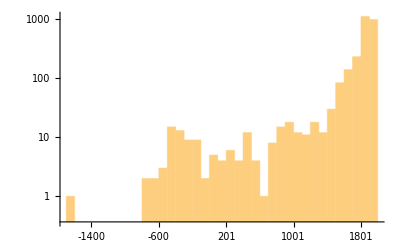

```mathematica
DateHistogram[completebirthDateObjects,"Century",ScalingFunctions->"Log"]
```

No mathematical knowledge between ancient Greeks

```mathematica
TimelinePlot@MapThread[Interval[{#1, #2}]&, {completebirthDateObjects ,completedeathDateObjects/._Missing ->DateObject["Today"]}]
```

-Graphics-

## MacTutor Social network graphs

```mathematica
bioReferences = StringCases[htmlBioList,"../Mathematicians/"~~Shortest[a__]~~".html"->a];
```

```mathematica
uniqueReference=Map[Union,bioReferences]
```

{{},{Ahmes},{Ahmes,Baudhayana},{Aristotle,Eudemus,Halley,Heath,Neugebauer,Plato,Proclus,Pythagoras,Russell,Van_der_Waerden},2768,{Fields,Fredholm,Hankel,Kirillov,Plancherel,Toeplitz,Wiles},{Bocher,Fields,Fourier,Gowers,Hedrick,Ostrowski,Polya,Ramanujan,Riemann,Salem,Schrodinger,Stein},{Fields,Kontsevich,McMullen,Riemann,Weil,Witten}}
 |  |  |  |

Association describing name of biography -> name of connected mathematician + how many times each person is mentioned

```mathematica
allNames = Flatten@StringCases[Import["http://www-groups.dcs.st-and.ac.uk/history/Indexes/Full_Chron.html",{"Hyperlinks"}],"/Biographies/"~~Shortest[a__]~~".html"->a]
```

```mathematica
Rule[1 , 2]
```

```mathematica
Rule["Euclid" , {"Newton","Pitagoras"}]
```

Euclid→{Newton,Pitagoras}

```mathematica
Thread [Rule["Euclid" , {"Newton","Pitagoras"}]]
```

```mathematica
Thread[Rule[{1,2},{{a,c},{b,c}}]]
```

{1→{a,c},2→{b,c}}

```mathematica
MapThread[#1 ->#2 &, {{1,2},{a,b}}]
```

{1→a,2→b}

```mathematica
MapThread[#1 ->#2 &, {{1,2},{{a,c},{b,c}}}]
```

{1→{a,c},2→{b,c}}

```mathematica
MapThread[Thread [Rule[#1 , #2]] &, {{1,2},{{a,c},{b,c}}}]
```

{{1→a,1→c},{2→b,2→c}}

```mathematica
vertexList =Flatten@ MapThread[ Thread[Rule[#1 , #2]]&,{allNames,uniqueReference}]
```

{Baudhayana→Ahmes,Manava→Ahmes,Manava→Baudhayana,Thales→Aristotle,Thales→Eudemus,Thales→Halley,Thales→Heath,Thales→Neugebauer,Thales→Plato,Thales→Proclus,24365,Tao→Riemann,Tao→Salem,Tao→Schrodinger,Tao→Stein,Mirzakhani→Fields,Mirzakhani→Kontsevich,Mirzakhani→McMullen,Mirzakhani→Riemann,Mirzakhani→Weil,Mirzakhani→Witten}
 |  |  |  |

```mathematica
Values["Tao"->"Riemann"]
```

Riemann

```mathematica
vertexList // Length
```

24385

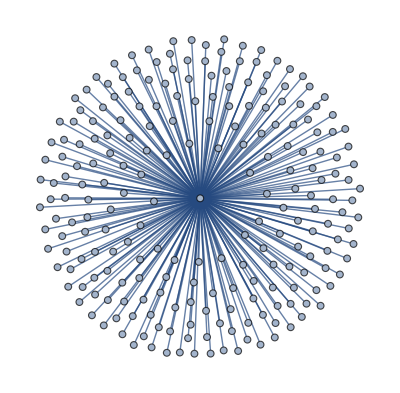

```mathematica
r =Select[vertexList,Values[#]=="Euclid" &];
Graph[r]
```

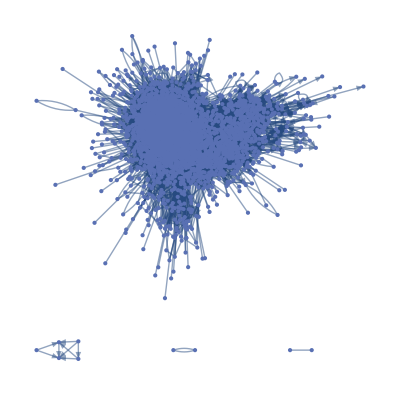

```mathematica
g =Graph[vertexList,VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
CommunityGraphPlot[g]
```

-Graphics-

```mathematica
FindGraphCommunities[g]
```

{{Russell,Frege,Cartan_Henri,Chevalley,Dieudonne,Grothendieck,Weil,Lebesgue,Stieltjes,Ramanujan,Wiles,Dehn,Hellinger,Stone,Vinogradov,Caratheodory,Truesdell,Hilbert,Bogolyubov,Parseval,Hardy,Kolmogorov,Zeeman,Bourbaki,Bocher,Cartan,Mises,Artin,Birkhoff_Garrett,Rota,Ulam,Von_Neumann,Householder,Rado,Tarski,Davenport,Kneser,Lefschetz,Korteweg,Steinitz,Choquet,Zermelo,Chauvenet,Grave,Hadamard,Hahn,Lyapunov,Vallee_Poussin,Borel,Brouwer,Andrews,Lehmer_Derrick,Sierpinski,Egorov,Butzer,Epstein,Noether_Emmy,Lowenheim,Levy_Paul,Rey_Pastor,Ledermann,Shafarevich,Robinson,Moriarty,Nash,Delone,Bieberbach,Hall,Tutte,Hirzebruch,Fischer,Helly,Schrodinger,Skolem,Wiener_Norbert,Courant,Toeplitz,Weyl,Fejer,Riesz,Hirsch,Cole,Malcev,Markov,Matiyasevich,Novikov,Frechet,Schur,Zhukovsky,Andreev,Steklov,Hausdorff,Lesniewski,Wittgenstein,Landau,Remak,Siegel,Lasker,Schmidt,Boas,Czuber,Dickstein,Kuratowski,Knopp,Feit,Thompson_John,Zelmanov,Kiselev,Arnold,Chaplygin,Ostrovskii,Perron,Moore_Robert,Loewy,Moore_Eliakim,Littlewood,Perelman,Zaremba,Fields,Haupt,Wirtinger,Baire,Bernstein_Sergi,Herglotz,Birkhoff,Bliss,Veblen,Dudeney,Sobolev,Pell_Alexander,Wheeler,Collingwood,Julia,Lehto,Polya,Hamel,Lichtenstein,Schreier,Loewner,Steinhaus,Shatunovsky,Chebotaryov,Kagan,Krein,Levin,Plancherel,Janiszewski,Osgood,Hasse,Hecke,Wedderburn,Ackermann,Blumenthal,Curry,Godel,Haar,Hedrick,Kaplansky,Kellogg,Kneser_Hellmuth,Takagi,Wielandt,Gorenstein,Krull,Zariski,Rogers_James,Selberg,Ahlfors,Akhiezer,Ostrowski,Daniell,Cramer_Harald,Zygmund,Thue,Morse,Post,Roth_Klaus,Burkill,Zorawski,Peter,Plessner,Friedmann,Smirnov,Tamarkin,Bohr_Harald,Schwartz,Kotelnikov,Beurling,Valiron,Furtwangler,Radon,Reidemeister,Taussky-Todd,Tauber,Jackson_Dunham,Luzin,Banach,Nikodym,Denjoy,Kolosov,Cartwright,<i>Kampf</i>,Chern,Hodge,Khinchin,Aleksandrov,Kurosh,Nekrasov,Stepanov,Eichler,Iwasawa,Bachelier,Doob,Feller,Ito,Doetsch,Walsh_Joseph,Reichenbach,Galerkin,Baer,Rademacher,Fraenkel,De_Rham,Blaschke,Finsler,Suss,Brauer,Neumann_Bernhard,Schmidt_F-K,Scholz_Arnold,Witt,Vidav,Whittaker_John,Cooper,Albert_Abraham,Tietze,Mordell,Montel,Szego,Mazurkiewicz,Todd_John,Turing,Wilkinson,Faltings,Brauer_Alfred,Eilenberg,Frucht,Green_Sandy,Grunsky,MacLane,Neumann_Hanna,Rado_Richard,Schiffer,Iyanaga,De_Bruijn,Halmos,Whyburn_William,Hopf,Hille,Behnke,Ingham,Riesz_Marcel,Rogosinski,Titchmarsh,Wright,Teichmuller,Birman,Privalov,Kerekjarto,Urysohn,Uryson,Evans,Geiringer,Maruhn,Mazur,Wintner,Bernays,Heyting,Quine,Lukasiewicz,Bilimovic,Frank,Hurewicz,Mandelbrot,Menger,Saks,Krylov_Nikolai,Levinson,Linnik,Erdos,Turan,Lukacs,Hazlett,Slutsky,Alexander,Whitehead_Henry,Kalmar,Richardson_Archibald,Littlewood_Dudley,Kothe,Schramm,Jones_Burton,Rudin,Vandiver,Lindenbaum,Schauder,Walfisz,Jacobson,Chatelet_Albert,Szasz,Bari,Keldysh_Lyudmila,Lavrentev,Menshov,Shnirelman,Suslin,Schouten,Mandelbrojt,Steenrod,Noether_Fritz,Gelfond,Scholz,Kreisel,Bloch,Miranda,Pontryagin,Caccioppoli,Godement,Mahler,Goodstein,Andreotti,Barsotti,Bombieri,Branges,Collatz,Fekete,Dvoretzky,Leray,Ford,Whyburn,Carleman,Hormander,Besicovitch,Lewy,Orlicz,Harary,Feigl,Vietoris,Kac,Kaczmarz,Antoine,Specker,Berwick,Friedrichs,Robbins,Kochina,Schmidt_Otto,Kober,Cassels,Calderon,Threlfall,Fox_Ralph,Seifert,Bott,Hall_Marshall,Gateaux,Hamburger,Razmadze,Rees_David,Zylinski,Stark,Faddeev,Kochin,Mohr_Ernst,Rohrbach,Nielsen_Jakob,Stein_Philip,Spencer,Rapcsak,Renyi,Cohen,Kostrikin,Prufer,Dantzig,Carlson,Krawtchouk,Pollaczek,Schoenberg,Jarnik,Ferrand,Cech,Tikhonov,Dixmier,Lanczos,Bergman,Bers,Mullikin,Wilder,Artzy,Magnus,Moufang,Newman,Lorch_Ray,Church,Frenkel,Gnedenko,Jordan_Pascual,Offord,Sargent,Szeg&#337;,Wrinch,Fefferman,Gelbart,Blackwell,Marcinkiewicz,Paley,Nevanlinna,Hayman,Reinhardt,Rothe_Erich,Herzberger,Rothe-Ille,Lax_Peter,Gentzen,Robinson_Raphael,Fedorchuk,Janovskaja,Kleene,Remez,Schneider,Wazewski,Borsuk,Fox,Bochner,Hilton,Wylie,Davis,Shtokalo,Petryshyn,Weinstein,Deligne,Tate,Bessel-Hagen,Leopoldt,Salem,Suetuna,Taylor_Mary,Bachiller,Zorn,Boruvka,Dorge,Keldysh_Mstislav,Malgrange,Possel,Atiyah,Samuel,Apostol,Cauer,Hopf_Eberhard,Mytropolsky,Puig_Adam,Redei,Vranceanu,Fine_Nathan,Gershgorin,Adian,Boone,Novikov_Sergi,Oka,Petrovsky,Rellich,Sperner,Zassenhaus,Vajda,Suzuki_Michio,Calugareanu,Cohn-Vossen,Aleksandrov_Aleksandr,Efimov,Pogorelov,Estermann,Heilbronn,Petersson,Schwerdtfeger,Shoda,Nakayama,Wall_Hubert,Wegner,Zarankiewicz,Birnbaum,Bosanquet,Rogers,Foster,Smullyan,Ehresmann,Kodaira,Whitney,Delsarte,Dubreil,Serrre,Gelfand,Coates,Cohn,Koksma,Morishima,Rocard,Bruhat,Choquet-Bruhat,Bradistilov,Federer,Serre,Chudakov,Davies,Clifford_Alfred,Dubreil-Jacotin,Fitting,Herbrand,Pisot,Linfoot,Higman,Varga,Kuperberg,Levitzki,Kato,Lehmer,Nirenberg,Mostowski,McShane,Ricci_Giovanni,Frohlich,Keller,Slupecki,Warschawski,Wolf_Frantisek,Beckenbach,Kuttner,Herstein,Carleson,Schutzenberger,Henriques,Kuroda,Lehmer_Emma,Ljunggren,Ribenboim,Kakutani,Dynkin,Tucker_Albert,Dantzig_George,Wallace_Alexander,Spanier,Zippin,Gleason,Montgomery,Straus,Borel_Armand,Cartier,Thom,Faddeeva,Fiedler,Forsythe,Golub,Kantorovich,Kublanovskaya,Specht,Baker_Alan,Bonsall,Goldie_Alfred,Gruenberg,Lopatynsky,Peschl,Laurent,Mirsky,Moser_Jurgen,Samarskii,Shimura,Yau,Alexander_Hugh,Carlitz,Chowla,Pillai,Ursell,Deuring,Livsic,Potapov,Kurepa,Marczewski,Vekua,Claytor,Johnson_Katherine,Lyapin,Preston,Dinghas,Elfving,Gohberg,Motzkin,Reichardt,Schmid,Schwartz_Laurent,Vagner,Van_Kampen,Black,Vladimirov,groups,Gyires,James_Ralph,Peirce,Segal,Yamabe,Naimark,Harish-Chandra,Stiefel,Goldstine,Rutishauser,Speiser,Theilheimer,Varga_Otto,Konig,Arf,Ikeda,Fogels,Hua,John,Koopmans,Lorentz_George,James,Askey,Samelson,Chow,Voevodsky,Langlands,Hahn_Wolfgang,Atkinson,Robinson_Julia,Santalo,Donaldson,Szekeres,Smithies,Chernikov,Dowker,Guinand,Smale,Sasaki,Sunyer,Corominas,Picard,Yano,Teitz,Tietz,Lichnerowicz,Cotlar,Sadosky,Sikorski,Chen,Lyndon,Mazur_Barry,Milnor,Stallings,Fomin,Mikusinski,Rios,Zaanen,Abellanas,Begle,Bing,Cherry_Colin,Cooper_William,Lovasz,De_Groot,Feldbau,Kaluznin,Hoehnke,Pitt,Polozii,Auslander_Louis,Apery,Doeblin,Dou,Kelly,Povzner,Marchenko,Edmonds,Good,Mackey,Hunt,Kolchin,Northcott,Alexiewicz,Eckmann,Gillman,Hibert,Krylov_Nikolai_S,Samoilenko,Rasiowa,Feldman,Fiorentini,Gilbarg,Serrin,Trudinger,Nagata,Szele,Kovacs,Szmielew,Wang,Kruskal_Joseph,Libermann,Rokhlin,Gromov,Schmetterer,Suvorov,Wu_Wen-Tsun,Mumford,Bellman,Ringrose,Britton,Cobbe,Lane,Almgren,Gaschutz,Ingarden,Urbanik,Kuiper,Tits,Los,Ramanathan,Reeb,Rennie,Singh,Gale,Garnir,Koszul,Rham,Kubilius,Lob,Luchins,Matsushima,Rudin_Walter,Trakhtenbrot,Gluskin,Kalicki,Ladyzhenskaya,Bernstein_Sergei,Lakatos,Lax_Anneli,Ree,Quillen,Sullivan,Dezin,Henrici_Peter,Griffiths_Brian,Kadets,Keller_Joseph,Sinai,Piatetski-Shapiro,Grauert,Aubert,Connes,Hoyland,Karlin,Krasovskii,Singer,Patodi,Steinfeld,Dahlquist,Divinsky,Lang,Sato,Auslander,Babuska,Kellogg_Bruce,Bremermann,Adamson,Dye,Eells,Hajek,Lusztig,Kennedy,Karp,Nijenhuis,Wilf,Nygaard,Pawlak,Stein,Shepherdson,Springer,Molien,Browder_Felix,Browder_William,Lyra,Postnikov,Hironaka,Mori,Sachs,Shields,Skopin,Taniyama,Bauer,Bishop,Union,Diaconis,Selten,Pask,Suzuki_Satoshi,Routledge,Gowers,Valdivia,Kalton,Walter,Witten,Kertesz,Manin,Prokhorov,Puri,Abhyankar,Bohr,Adams_Frank,Dijkstra,Foulis,Goldberg,Kalman,Kelly_Max,Morton,Schwartz_Jacob,Skorokhod,Blum,Freedman,Wang_Yuan,Knapowski,McDuff,Thurston,Olech,Tao,Thompson_Robert,Bass,Bollobas,Drinfeld,Honda,Nash-Williams,Solitar,Tarina,Vernon,Warner,Lesokhin,Artin_Michael,Wall,Meyer_Paul-Andre,Ornstein,Wiegold,Furstenberg,Szemeredi,Grigelionis,Hay,Kumano-Go,Bowen,Srinivasan,Allan_Graham,Anosov,Bolibrukh,Cofman,Kirillov,Okounkov,Praeger,Strassen,Valiant,Tichy,Book,Hayes_David,Johnson_Barry,Schoenflies,Black_Fischer,Griffiths,Gromoll,Kirby,Ramanujam,Ratner,Margulis,Uhlenbeck_Karen,Krylov,Subbotovskaya,Hartley,Senechal,Keen,Szafraniec,Varadhan,McMullen,Szasz_Domokos,Young_Lai-Sang,Aubin,Chang,Lafforgue,Rallis,Jones_Vaughan,Millington,Trahtman,Adleman,Shelah,Simon,Schoen,Iwanik,Pisier,Arino,Eisenbud,Carr,Flajolet,Kintala,Murphy_Gerard,Broomhead,Gorbunov,Floer,Thomason,Bourgain,Borcherds,Krejci,Perrin-Riou,Yoccoz,Seress,Thompson_Abigail,Heinonen,Smith_Karen,Werner_Wendelin,Motwani,Dubickas,Kontsevich,Jitomirskaya,Cariolaro,Mirzakhani},{Euclid,Cantor,Weierstrass,Zeuthen,Dedekind,Chasles,Delambre,Lalande,Laplace,Euler,Lagrange,Yativrsabha,Newcomb,Wilson_John,Ruffini,Gauss,Peirce_Charles,Duhem,Loria,Bolzano,De_Morgan,Montucla,Lhuilier,Monge,Struik,Cremona,Libri,Bessel,Glaisher,Mannheim,Jacobi,Poncelet,Petit,Simson,Cantor_Moritz,Condorcet,Saccheri,Betti,Brioschi,Cauchy,Riemann,DAlembert,Arago,Bellavitis,Poinsot,Graves_John,Todhunter,Beltrami,Bolyai,Halsted,Lobachevsky,Segre_Corrado,Legendre,Gergonne,Playfair,Servois,Stewart,Trail,Wallace,Waring,Maskelyne,Coulomb,Boole,Borda,Segner,Binet,Kummer,Lexell,Mayer_Tobias,Yushkevich,Lambert,Landen,Stewart_Dugald,Kaestner,Bartels,Lacroix,Spence,Herschel_William,Mechain,Fourier,Maxwell,Bezout,Hermite,Lindemann,Pringsheim,Sylvester,Bossut,Carnot,Banneker,Clebsch,Paoli,Steiner,Vilant,Harlay,Rayleigh,Dionis,Rocha,Teixeira,Ramsden,Troughton,Vandermonde,Kronecker,Bring,Abel,Crelle,Hamilton,Jerrard,Biot,De_Prony,Brisson,Galois,Jordan,Ivory,Leslie,West,Herschel,Herschel_Caroline,Adams,Le_Verrier,Hindenburg,Gudermann,Cunha,Wessel,Argand,Juel,Lie,Tetens,Hachette,Malus,Mathieu_Claude,Brinkley,Airy,Fresnel,Poincare,Poisson,Puissant,Somerville,Sturm,Dirichlet,Carnot_Sadi,Rankine,Canard,Bertrand,Cournot,Girard_Pierre,Arbogast,Francais_Francois,Bordoni,Kramp,Budan_de_Boislaurent,Sturm&#8217;s,Sturm's,Liouville,Young_Thomas,Babbage,Peacock,Osipovsky,Ostrogradski,Pfaff,Wussing,Wantzel,Lloyd_Bartholomew,Farey,Pick,Bouvard,Francais_Jacques,Carlyle,Clifford,Haldane,Frenet,Serret,Bobillier,Brianchon,Dupin,Lame,Plucker,Reynaud,Lloyd_Humphrey,MacCullagh,Bowditch,Lissajous,Peirce_Benjamin,Burckhardt,Francoeur,Woodhouse,Gregory_Olinthus,Savart,Talbot,Mobius,Adrain,Ampere,Faraday,Savary,Thomson,Weber,Bolyai_Farkas,Germain,Eisenstein,Kirchhoff,Cockle,Wronski,Grassmann,Hesse,Holmboe,Ohm,Ohm_Martin,Von_Staudt,Lovelace,Mathieu_Emile,Bidone,Menabrea,Plana,Chebyshev,Green,Fricke,Klein,Neumann_Franz,Navier,Stokes,Fizeau,Foucault,Catalan,Cayley,Rodrigues,Nicollet,Thomson_James,Walsh,De_Morgan',550,800); return false;">George Boole</m></font>
</article><hr>
<b><a href = "../References/Walsh,Lefebure,Dirksen,Gopel,Heine,Hamilton_William,Venn,Coolidge,Morin,Casorati,Duhamel,Freudenthal,Kovalevskaya,Belanger,Boussinesq,Coriolis,Saint-Venant,Listing,Mollweide.,Terrot,Kelland,Nightingale,Tait,Lebesgue_Victor,Mourey,Whewell,Dandelin,Graffe,Houel,Bachmann,Fuchs,Lipschitz,Cannell,Hopkins,Murphy,Kulik,Archibald,Petzval,Olivier,Quetelet,Taurinus,Ore,Clapeyron,Richard_Louis,MacMahon,Netto,Bienayme,Brashman,Bunyakovsky,Davidov,Somov,Clausius,Hirst,Neumann_Carl,Scherk,Clausen,Darboux,Feuerbach,Lueroth,Noether_Max,Reye,Thomae,Raabe,Jevons,Krylov_Aleksei,Plateau,Douglas,Schwarz,Verhulst,Minkowski,Brasseur,Folie,Le_Paige,Doppler,Nagel,Voronoy,Borchardt,Rosenhain,Schlafli,Seidel,Helmholtz,Sang,Booth,Graves_Charles,Salmon,Gregory_Duncan,Kirkman,Minding,Bonnet,Harnack,Korkin,Peterson,Picard_Emile,Weisbach,Stern,Dupre,Gibbs,Russell_Scott,De_Vries,Hankel,Peano,Wangerin,Castigliano,Pratt,Byrne,Christoffel,Du_Bois-Reymond,Gordan,Joachimsthal,Schonflies,Hart,Aronhold,Henrici,Mayer_Adolph,Meyer,Schroder,Von_Dyck,Weber_Heinrich,Delaunay,Waterston,Anstice,Fano,Laurent_Pierre,Puiseux,Colenso,Da_Silva,Smith,Mocnik,OBrien,Heaviside,Kempe,Bolza,Engel,Frobenius,Gegenbauer,Hensel,Holder,Hurwitz,Killing,Konigsberger,Lerch,Mertens,Mittag-Leffler,Schottky,Stolz,Wolf,Briot,Bouquet,Ferrel,Genocchi,Broch,Hendricks,Hill,Ladd-Franklin,Morley,Schroeter,Bour,Codazzi,Tannery_Jules,Scheffers,Larmor,Casey,Lemoine,Neuberg,Jonquieres,Schubert,Puiseux_Pierre,Tisserand,Routh,Blackburn,Ferrers,Lucas,Haughton,Lindelof,Pincherle,Appell,FitzGerald,Amsler,Arzela,Ascoli,Bertini,Bianchi,Dini,Enriques,Pieri,Ricci-Curbastro,Volterra,Battaglini,Tilly,Schlomilch,Maschke,Dase,Petersen,Runge,Bjerknes_Carl,Bjerknes_Vilhelm,Faa_di_Bruno,Goursat,Spottiswoode,Vashchenko,Bukreev,Walker_John,Capelli,DOvidio,Frattini,Crofton,Meissel,Brill,Wiener_Christian,Merrifield,Roberts,Bruno,Cosserat,Mainardi,Fredholm,Grossmann,Levi-Civita,Pasch,Rosanes,Sturm_Rudolf,Guccia,Veronese,White,Thiele,Beale,Sidler,Geiser,Graf,Rudio,Fiedler_Wilhelm,Fiedler_Ernst,Rouche,Laguerre,Sylow,Tucker_Robert,Brocard,Elliott,Greenhill,Lamb,Zehfuss,Delannoy,Mathews,Painleve,Schlesinger,Wilczynski,Amringe,McClintock,Cesaro,Meray,Laurent_Hermann,Purser,Orr,Stefan_Josef,Weingarten,Bleuler,Bugaev,Sonin,Study,Hertz_Heinrich,Landsberg,Zolotarev,MacColl,Baldwin,Brown,Gram,Barbier,Fiske,Mathematical,Roch,Siacci,Mansion,Johnson_Woolsey,Story,Basso,Rohn,Wilson_Edwin,Clerke,Eisenhart,Castelnuovo,Sokhotsky,Plemelj,Pierpont,Stuart,Tarry,Weber_Heinrich_F,Halphen,Backlund,Burali-Forti,Jourdain,Gubler,Burkhardt,Butzberger,Gysel,Jerabek,Albanese,Fubini,Scorza,Bruns,Poretsky,Vitali,Franklin_Fabian,Stringham,Craig_Thomas,Wilson_John_2,Severi,Suter,Drach,Weyr,Weyr_Eduard,Molin,Hopkinson,Appel,Heawood,Scott_Robert,Woodward,Bertillon,Haret,Jung,Koebe,Taylor_James,Weiler,Cosserat_Francois,Koenigs,Vessiot,Grobli,Herzog,Franel,Lacombe,Rebstein,Upton,Murnaghan,Amaldi,Levi_Beppo,Mellin,Tricomi,Ayrton,Beyel,Phragmen,Sleszynski,Couturat,Valyi,Wiltheiss,Stackel,Wiener_Hermann,Droz-Farny,Morera,Meyer_Adolph,Fine_Henry,Gerbaldi,Bagnera,Cipolla,De_Franchis,Vailati,Gentry,Koch,Del_Re,Berzolari,Montesano,Dumas,Hirsch_Arthur,Heun,Humbert_Georges,Humbert_Pierre,Jensen,Meshchersky,Vivanti,Chini,Nicoletti,Gutzmer,Padoa,Pascal_Ernesto,Bendixson,Boggio,Marcolongo,Berwald,Van_Vleck,Heegaard,Coble,Kasner,Bottasso,Richard_Jules,Gigli,Sokolov,Michell,Miller_Kelly,Snyder,Pade,Richmond,Segre_Beniamino,D&#8217;Ovidio,D'Ovidio,Alasia,Nalli,Ritt,Nielsen,Wiman,Sneddon,Noble,Sintsov,Bosworth,Gould,Leavitt,Newson,Carslaw,Jackson_Frank,Montessus,Norlund,Amberg,Ahrens,Cecioni,Sansone,Pfeiffer,Stephansen,Fuchs_Richard,Pompeiu,Iacob,Sergescu,Sundman,Edge,Hartogs,Stormer,Titeica,Levi_Eugenio,Fatou,Brusotti,Faber,Gronwall,Kahler,Schubert_Hans,Boutroux,Jacobsthal,Insolera,David_Lajos,Hudson,Angheluta,Abramescu,Popoviciu,Chazy,Franklin,Lewis,Angelescu,DOcagne,Nugel,Cherubino,Picone,Fichera,Rychlik,Comessatti,Morin_Ugo,Stoilow,Bompiani,Chisini,Fantappie,Brink,Haynes,Peres,Swain,Subbotin,Schmidt_Harry,Martinelli,Gordon,Oleinik,Eckert_Wallace,Golab,Popoviciu_Elena,Rejewski,Zygalski,Mikhlin,Mihoc,Pic,Ghizzetti,Mazya,Bachmann_Friedrich,Weise,Conforto,Klingenberg,Reiner,Schatten,Grosswald,Magiros,Castelnuovo_Emma,Isaacs,Silva,Hsiung,Fenyo,Luke,Rado_Ferenc,Khruslov,Gallarati,Spence_David,Stancu,Alling,Cheney,Kiss,Borok,Kluvanek,Hildebrant,Kuczma,Daubechies,Tapia,Lupas,Loday,Stromme},{Thales,Aristotle,Eudemus,Halley,Heath,Neugebauer,Plato,Proclus,Pythagoras,Van_der_Waerden,Anaximander,Porphyry,Panini,Backus,Newton,Anaxagoras,Vitruvius,Empedocles,Simplicius,Zeno_of_Elea,Oenopides,Eratosthenes,Tannery_Paul,Antiphon,Eudoxus,Hippocrates,Leucippus,Democritus,Xenocrates,Theodorus,Theaetetus,Archimedes,Chrysippus,Hippias,Geminus,Pappus,Sporus,Bryson,Archytas,Eutocius,Hipparchus,Dinostratus,Menaechmus,Nicomedes,Heraclides,Brahe,Callippus,Diocles,Theon_of_Smyrna,Aristaeus,Apollonius,Hypsicles,Ptolemy,Autolycus,Theodosius,Heron,Theon,Zeno_of_Sidon,Aristarchus,Copernicus,Cavalieri,Conon,Fermat,Kepler,Leibniz,Philon,Cleomedes,Marinus,Dionysodorus,Al-Haytham,Zenodorus,Diophantus,Perseus,Posidonius,Knorr,Nicomachus,Boethius,Menelaus,Thabit,Viviani,Zhang_Heng,Li_Chunfeng,Liu_Hui,Xu_Yue,Liu_Hong,Abul-Wafa,Bachet,Bombelli,Hypatia,Regiomontanus,Descartes,Guldin,Pandrosion,Serenus,Sun_Zi,Ruan_Yuan,Xiahou_Yang,Zhang_Qiujian,Domninus,Zu_Chongzhi,Zu_Geng,Anthemius,Aryabhata_I,Al-Biruni,Bhaskara_I,Nilakantha,Varahamihira,Brahmagupta,Wang_Xiaotong,Cardan,Fibonacci,Li_Zhi,Raphson,Stirling,Lalla,Al-Khwarizmi,Adelard,Banu_Musa,Al-Jawhari,Al-Kindi,Al-Tusi_Nasir,Hunayn,Banu_Musa_Ahmad,Banu_Musa_al-Hasan,Banu_Musa_Muhammad,Gherard,Govindasvami,Mahavira,Al-Mahani,al-Khazin,Khayyam,Yunus,Prthudakasvami,Ahmed,Bradwardine,Campanus,Jordanus,Pacioli,Ibrahim,Sinan,Sankara,Bhaskara_II,Abu_Kamil,Al-Karaji,Al-Battani,Galileo,Sridhara,Al-Nayrizi,Al-Khazin,Al-Khujandi,Al-Uqlidisi,Al-Kashi,Al-Samawal,Stevin,Aryabhata_II,Mansur,Al-Quhi,Al-Sijzi,Vijayanandi,Gerbert,Huygens,Riccati_Vincenzo,Kushyar,Al-Nasawi,Avicenna,Al-Baghdadi,Al-Jayyani,Barrow,Jia_Xian,Horner,Pascal,Yang_Hui,Hermann_of_Reichenau,Sripati,Ferrari,Ferro,Tartaglia,Brahmadeva,Abraham,Ezra,Bacon,Hemchandra,Jabir_ibn_Aflah,Levi,Pell,Al-Tusi_Sharaf,Reinher,Albertus,Cusa,Sacrobosco,Grosseteste,Maurolico,Scot,Viete,Barocius,Clavius,Qin_Jiushao,Al-Maghribi,Qadi_Zada,Guo_Shoujing,Llull,Tibbon,Zhu_Shijie,Al-Samarqandi,Al-Banna,Al-Qalasadi,Al-Farisi,al-Haytham,Li_Rui,Li_Shanlan,Ockham,Oresme,Albert,Leonardo,Al-Khalili,Narayana,Madhava,Gregory,Jyesthadeva,Maclaurin,Ulugh_Beg,Paramesvara,Brunelleschi,Van_Ceulen,Al-Umawi,Bruno_Giordano,Alberti,al-Banna,Francesca,Peurbach,Borgi,Smith_David,Gassendi,Chuquet,La_Roche,Widman,Ries,Rudolff,Werner,Apianus,Durer,Gemma_Frisius,Rheticus,Maior,Cajori,Bouvelles,Tunstall,Ortega,Lax,Stifel,Fine,Hellman,Picard_Jean,Nunes,Dee,Snell,Commandino,Monte,Mercator_Gerardus,Recorde,Ramus,Digges,Harriot,Benedetti,Mersenne,Porta,Lincei,Danti,Vernier,Allen,Roomen,Wittich,Burgi,Craig,Napier,Savile,Al-Amili,al-Kashi,Cataldi,Morgan,Briggs,Wren,Mastlin,Bramer,Ricci_Matteo,Valerio,La_Faille,Saint-Vincent,Tacquet,Torricelli,Delgado,Lavanha,Magini,Gellibrand,Oughtred,Vlacq,Fincke,Bartholin,Pitiscus,Lansberge,Boulliau,Morin_Jean-Baptiste,Xu_Guangqi,Biancani,Riccioli,Scheiner,Ghetaldi,Herigone,Mayr,Castelli,Delamain,Gunter,Jones,Wallis,Ward_Seth,Borelli,Faulhaber,Bernoulli_Jacob,De_Moivre,Beaugrand,Mydorge,Alcuin,Pascal_Etienne,Tschirnhaus,La_Hire,Turner,Jungius,Hobbes,Boyle,Roberval,Frenicle_de_Bessy,Le_Tenneur,Desargues,Petit_Pierre,Schickard,Cassini,Girard_Albert,Golius,Hutton,Arnauld,Hooke,Schooten,Angeli,Hardy_Claude,Grimaldi,Hevelius_Johannes,Carcavi,Auzout,De_Beaune,Billy,Brouncker,Ozanam,Greaves_John,Caramuel,Cunitz,Fabri,Cassini_Dominique,Dechales,Ricci,Stampioen,Flamsteed,Hevelius_Koopman,Molyneux_William,Collins,Rahn,Malebranche,More_Henry,Wilkins,De_Witt,Heuraet,Hudde,Kamalakara,Horrocks,Mouton,Mylon,Mercator_Nicolaus,Sluze,Neile,Mengoli,Richer,Fontenelle,Grandi,Gregory_David,Guarini,Apaczai,Debeaune,Cassini_Jacques,Moore_Jonas,Papin,Cocker,Mei_Wending,Mei_Juecheng,Taylor,Berkeley,De_LHopital,Privat_de_Molieres,Reyneau,Varignon,Lamy,Mohr,Mascheroni,Seidenberg,Seki,Whiston,Siguenza,Bernoulli_Johann,Bernoulli_Nicolaus(I),Clarke,Keill,Ceva_Giovanni,Ceva_Tommaso,Bernoulli_Johann(III),Le_Fevre,Rolle,Saurin,Sharp,Bernoulli_Daniel,Molyneux_Samuel,Clairaut,Montmort,Arbuthnot,Lagny,Carre,Stone_Edmund,Takebe,Romberg,SGravesande,Bernoulli_Johann(II),Bernoulli_Nicolaus(II),Buffon,Cotes,Magnitsky,Kirch,Agnesi,Manfredi,Manfredi_Gabriele,Maupertuis,Riccati,Hermann,Poleni,Bouguer,Cassini_de_Thury,La_Condamine,Doppelmayr,Hayes_Charles,Goldbach,Colson,Machin,Maseres,Simpson,Fagnano_Giulio,Fagnano_Giovanni,Hadley,Boscovich,Castel,Diderot,Paman,MacLaurin,Robins,Jagannatha,Cramer,Braikenridge,Camus,Chatelet,Konig_Samuel,Bliss_Nathaniel,Emerson,Bayes,Price,Castillon,Fontaine_des_Bertins,Kline,Franklin_Benjamin,Fuss,d&#8217;Alembert,d'Alembert,Malfatti,Bassi,Wilson_Alexander,Hatvani,Lepaute,Morgan_William,Aepinus,DArcy,Hutton_James,Frisi,Bougainville,Lorgna,Ajima,Karsten,Rittenhouse,Glenie,Klugel,Mollweide,Atwood,Aida,Tinseau,Hellins,Bonnycastle,Fergola,Flauti,Vega,Bernoulli_Jacob(II),Cheng_Dawei,Marescotti,Bortolotti,Giordano,Gompertz,Strong,Leger,Whish,Rajagopal,Gurbs,Shanks,Ramchundra,Allman,Sprague,Lehmer_Derrick_N,Fueter,Adler,Brun,De_Vries_Hendrik,Euwe,Duarte,Vacca,Schoy,Erlang,Karpinski,Bartel,Prieto,Speiser_Andreas,Ayyangar,Aryabhata,Bhaskara,Zeckendorf,Kramer,Evelyn,Boyer,Freitag,Righini,Lorenz_Edward,Hiebert,Christiansen,Aaboe,Whiteside,Fowler_David},{Einstein,Knuth,Thompson_DArcy,Turnbull,David,Ball,Saunderson,Tweedie,Hubble,Keynes,Richardson,Muir,Bell,MacRobert,Temple,Galton,Kendall,Mackay_J_S,Pearson,Born,Planck,Thomson_William,Whitehead,Baker,Schoute,Watson,Boole_Mary,Stott,Heisenberg,Boltzmann,Balmer,Bohr_Niels,Rydberg,Watson_Henry,Gibson,Wolstenholme,Forsyth,Knott,Dodgson,Hobson,Aitken,Rutherford,De_Forest,Jack_William,Darwin,Lexis,Fisher,Scott,Abbe,Kendall_Maurice,Ball_Robert,Whittaker,Loyd,Reynolds,Robertson,Niven,Burnside,Niven_Charles,Chrystal,Thom_George,Sommerfeld,Gosset,Macaulay,Wigner,Edgeworth,Bromwich,Coxeter,Gray_Andrew,Gray_James,Love,Barclay,Fraser,Zeno_of_Elia,Bryant,Scott_Lang,Lorentz,Macdonald_William,Synge,Kerr,Ehrenfest,Barnes,Brillouin,Broglie,Peirce_B_O,Bateman,Pauli,Boys,Du_Val,Steggall,Peddie,Fawcett,Buchan,Milne_Archibald,Allardice,Gardner,Hertz_Gustav,Dirac,Pearson_Egon,Weldon,Yule,Roth,Coulson,Johnson,Heilbron,Wien,Chree,Morgan_Alexander,Clark_John,Muirhead,Dougall,Taylor_Geoffrey,Alison,Ferguson,Broadbent,Horsburgh,Archibald_James,Campbell,Young_Alfred,Butters,Clark,Mackay,Milne,McCowan,Metzler,Prandtl,Morrison,Beattie,Brown_Alexander,Fowler,Sheppard,Lidstone,Ramsey,Bohl,Esclangon,Dixon,Dixon_Arthur,Graham,Macdonald,Crawford,Conway_Arthur,Sampson,Eddington,See,Ferrar,Dougall_Charles,Erdelyi,Gray,Bennett,Bortkiewicz,Comrie,Burgess,Craig_James,Macdonald_James,McBride,McQuistan,McIntosh,Bethe,Thomson_W_L,Mackay_J S,Martin_Emilie,Chapman,Lawson,Gwilt,Pinkerton,Schwarzschild,Miller_John,Mitchell_James,Turner_John,Neyman,Yates,MacMillan_Chrystal,Meiklejohn,Moulton,Russell_A_D,Sitter,Smoluchowski,Hardie_Patrick,Karman,Copson,Jeans,Robinson_G_de_B ,Abraham_Max,Fermi,Blades,Cantelli,De_Finetti,Cholesky,Fox_Leslie,De_Valera,Uhlenbeck,Gini,Bell_Robert,Gillespie,Mason,Ehrenfest-Afanassjewa,Freundlich,McKendrick,Barkla,Carse,Gentle,Weaver,Adams_Edwin,Milne-Thomson,Eastwood,Gibb,Mineur,Ramsay_Peter,Picken,Young_Andrew,Ramsay,Sommerville,Beatty,Cunningham,Semple,Milne_William,McArthur,Ramsey_Peter,Ross,Bevan-Baker,Snedecor,Cochran,Cox,Wilks,Banachiewicz,Slebarski,Ince,Durell,Dyson,Hotelling,Mercer,Walker_Arthur,Wood,Enskog,Klein_Oskar,Feynman,Rankin,Weatherburn,Brodetsky,Jeffreys,Coutts,Kaluza,Van_der_Pol,McWhan,Sperry,Brown_Walter,Lockhart,Batchelor,Anderson,Darwin_C_G,Escher,Conway,Brash,Butchart,Thompson,Darmois,Pitman,Datta,Goldie,Kennedy-Fraser,Mackie,Williams,Robinson_G_de_B,Dunbar,Forder,Chandrasekhar,Jefferys_Bertha,McCrea,Jeffery_Ralph,Jeffery,Levy_Hyman,Wren_Thomas,Wright_Sewall,Carver,Smeal,Jeffreys_Bertha,Shewhart,Bonferroni,Burchnall,Etherington,Brown_Thomas,Tukey,Madwar,Mahalanobis,Bose_Raj,Rao,Arthur,Bose,Shannon,Schwinger,Kramers,Krieger,Morawetz,Nelson,Lemaitre,Hoyle,Macintyre,Macintyre_Archibald,Scott_Agnes,Rees,Childs,Bolam,Paton,Schlapp,Cunningham_Leslie,Fuller,Wald,Verblunsky,Lumsden,Calderwood,Numbers,Geary,Tinbergen,Jack,Morton_Vernon,Pairman,Kemeny,Pars,Wilson_Bertram,Blanch,Goldstein,Todd,Greaves,Hartree,Mathisson,Wishart,Bondi,Cherry,Penrose,Fock,Infeld,Olds,Mosteller,Levy,Bath,Kloosterman,Payne-Gaposchkin,Youden,Deans,Robb,Williamson,Moore,Hawking,Clunie,Frewin,Gray_Marion,Wolfowitz,Greenstreet,Piaggio,Flugge-Lotz,Lighthill,Pedoe,Mackenzie,Oppenheim,Prager,Hamming,Timms,Eperson,McLeod,Flugge,McVittie,Graham_Tommy,Guthrie,Ruse,Stueckelberg,Cowling,Savage,Fasenmyer,Leech,Roy,Smith_John,Welchman,Box,Jahn,Fuchs_Klaus,Peierls,Bronowski,Landau_Lev,Scheffe,Alfven,Lifshitz,Bartlett,Hsu,Behrend,Feigenbaum,Champernowne,Ollerenshaw,Slater,Pompilj,Wales,Dilworth,Chung,Hoeffding,Spitzer,May,McConnell,Bates,Crank,Nicolson,Hammersley,Montroll,Kruskal_William,Clarke_Joan,Stewartson,Sims,Jack_Henry,Mendelsohn,Scott_Elizabeth,Herivel,Kneebone,Tinney,Kruskal_Martin,Seidel_Jaap,Van_Lint,Pack,Wenninger,Crighton,Amitsur,Mitchell,Moser_Leo,Moser_William,Woods,Chernoff,Kiefer,Cohen_Wim,Kingman,Flett,Tims,Hamill,Macbeath,Wilkins_Ernest,Le_Cam,Reizins,Gupta,Pople,Aitchison,Haselgrove,Moiseiwitsch,Bell_John,Benjamin,Munn,Spencer_Tony,Polkinghorne,Mercer_Alan,Murray,Pless,Lewis_John,ORaifeartaigh,Carmeli,Roach,Kerr_Roy,Parry,Burton,Howie,Third,Schelp,Flato,Mochizuki,Pastur,Cercignani,Pahlings,Waller,Brown_Gavin,Keast,Orszag,Davies_Paul,Grunewald,Rudolph,Cafaro,Hau,Michler},{Martin_Lajos,Eotvos,Hunyadi,Konig_Julius,Scholtz,Konig_Denes,Kurschak,Rethy,Farkas,Bernstein_Felix,Klug,Ratz,Geocze,Bauer_Mihaly,Egervary,Moisil,Berge,Maurer,Wexler-Kreindler,Hammer,Rothblum,Filep,Balogh},{Abbott,Tonelli,Chisholm_Young,Young,Maddison,Cimmino,Cafiero,De_Giorgi,Faedo,Prodi,Stampacchia,Young_Laurence,Lions_Jacques-Louis,Cesari,Warga,Baiada,Vinti,Magenes,Lions,Grattan-Guinness},{Dickson,Martin,Miller,Finkel,Heaton,Seitz,Huntington,Carmichael,Slaught,Blichfeldt,MacDuffee,Suschkevich,Griffiths_Lois,Olive},{Kutta,Hopper,Eckert_John,Aiken,Hollerith,Rhodes,Mauchly,Haack,Zuse,Eckert,Antonelli,Bartik},{Cox_Elbert,Browne,Granville,Lorch,Falconer,Malone-Mayes},{Baudhayana,Ahmes,Manava,Apastamba,Katyayana},{Tweedie_D_J,Tweedie_David},{Meders,Leimanis},{Drysdale,Johnstone},{Arins,Grinbergs}}

```mathematica
clique = FindClique[g]
```

{{Fermat,Huygens,Pascal,Mersenne,Roberval}}

- Pascal was an important mathematician, helping create two major new areas of research: he wrote a significant treatise on the subject of projective geometry at the age of 16, and later corresponded with Pierre de Fermat on probability theory, strongly influencing the development of modern economics and social science. 

- Constantin (Huygens’ Father) had many contacts in England and corresponded regularly with Mersenne and was a friend of Descartes.
 Mersenne challenged Huygens to solve a number of problems including the shape of the rope supported from its ends. Although he failed at this problem he did solve the related problem of how to hang weights on the rope so that it hung in a parabolic shape.
 
 - Between Roberval and René Descartes there existed a feeling of ill-will,[5][6] owing to the jealousy aroused in the mind of the former by the criticism that Descartes offered to some of the methods employed by him and by Pierre de Fermat; and this led him to criticize and oppose the analytical methods that Descartes introduced into geometry about this time.

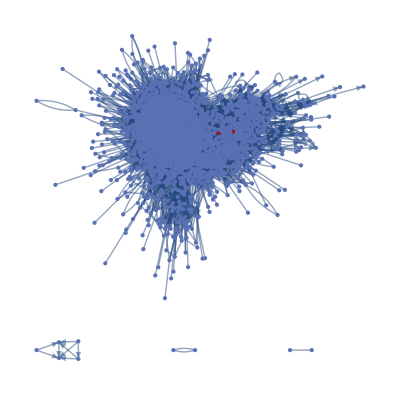

```mathematica
HighlightGraph[g,Subgraph[g,clique]]
```

```mathematica
agents=Part[VertexList[g],Ordering[BetweennessCentrality[g],-5]]
```

{Euler,Weil,Newton,Hilbert,Euclid}

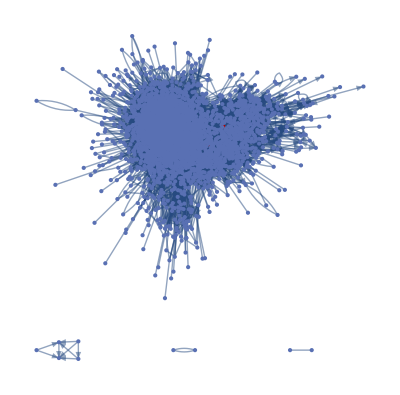

```mathematica
HighlightGraph[g,agents]
```

```mathematica
critical=BetweennessCentrality[g];
criticalNode=Pick[VertexList[g],critical,Max[critical]]
```

{Euclid}

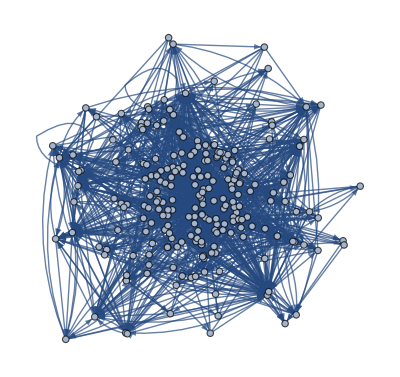

```mathematica
NeighborhoodGraph[g,criticalNode,1,GraphLayout->"SpringEmbedding",VertexLabels->Placed["Name",Tooltip]]
```

## Counting String Length in MacTutor

```mathematica
ClearAll[x];

getBodyBio [ htmlString_String ] := StringCases[ htmlString ,
                                                "<article>" ~~ Shortest[ x__ ] ~~ "</article>" -> x
                                                ];
                                                
deleteHtmlElements [ htmlString_String ] := StringDelete[
                                                          getBodyBio[ htmlString ],
                                                         "<"~~Shortest[__]~~">" 
                                                         ];
                                                         
numberSentences [ htmlString_ ] := Length@First@TextCases[  htmlString , "Sentence"];

numberWords [ htmlString_] := Length@First@TextCases[ htmlString , "Word"];
```

```mathematica
formattedBios =deleteHtmlElements[#]&/@htmlBioList[[;;]];
```

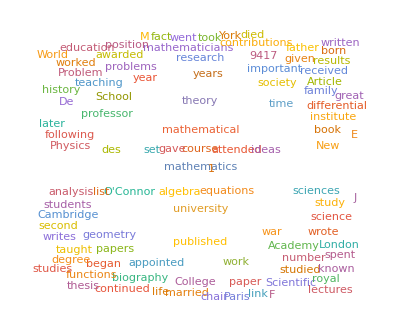

```mathematica
WordCloud[DeleteStopwords[StringJoin[formattedBios]]]
```

```mathematica
WordCloud[%133]
```

WordCloud::nomem: Not enough memory available to compute the word cloud.

WordCloud[WordCloud[{1}]]
 |  |  |  |

```mathematica
sentenceCounts=numberSentences /@ formattedBios
```

{7,22,14,82,57,23,130,58,54,52,34,86,44,36,45,28,73,36,19,47,84,57,96,24,15,29,25,35,150,43,23,29,31,42,126,61,106,45,24,22,35,79,67,34,35,12,18,107,29,26,40,45,45,23,47,54,50,89,49,48,29,71,122,19,16,23,97,81,34,15,92,19,24,42,40,61,20,49,26,60,56,23,34,17,91,44,31,38,10,38,68,67,27,44,22,20,138,33,64,9,14,53,52,6,38,8,23,8,31,84,33,46,61,30,34,32,67,29,46,23,1,32,69,20,49,108,64,79,117,48,23,142,45,93,46,32,41,87,20,114,77,14,27,49,33,28,23,108,25,71,57,59,17,85,42,101,22,59,102,83,99,32,69,52,71,17,43,90,12,39,55,85,43,130,67,68,84,28,35,14,27,46,51,43,76,78,51,39,105,76,53,124,69,43,99,41,17,95,37,31,51,42,52,55,37,139,153,42,21,28,107,83,74,129,45,99,31,82,118,74,74,77,98,111,63,63,39,89,113,119,60,99,74,43,73,61,107,111,82,142,38,58,64,78,92,91,48,65,96,58,33,75,80,68,68,145,91,94,123,43,112,64,165,66,91,130,55,120,127,101,121,30,37,107,55,81,24,94,17,37,35,105,46,131,127,61,38,27,115,78,33,78,143,83,27,47,105,50,123,95,70,31,61,96,21,68,134,72,59,71,48,144,95,114,66,43,87,56,73,47,62,103,100,20,98,77,87,71,32,22,76,94,47,84,32,84,79,101,111,41,80,40,27,43,40,90,38,45,124,39,74,112,110,96,34,123,82,67,131,44,135,60,103,78,35,69,22,152,27,40,182,68,53,106,29,45,113,23,75,57,54,84,115,84,69,93,83,46,27,1,54,27,75,57,107,83,107,67,75,62,68,122,47,100,54,53,78,60,48,27,51,80,124,65,47,50,52,66,35,31,89,57,81,98,33,70,37,74,47,54,91,18,118,12,38,139,107,37,99,40,37,11,95,105,55,31,95,73,25,32,143,15,80,195,61,87,14,25,51,47,134,45,84,65,37,18,1,40,81,30,29,36,49,63,61,34,112,73,91,147,103,60,52,45,40,111,35,64,36,126,113,55,95,28,84,86,47,58,79,89,124,19,64,83,34,150,77,41,30,22,38,15,41,110,43,64,131,35,36,79,122,37,122,71,144,41,73,48,34,114,81,75,29,85,42,48,73,111,47,34,37,43,48,15,46,58,57,72,58,43,56,44,44,100,128,54,69,43,42,104,31,19,28,64,27,56,65,120,44,25,62,23,33,102,75,72,72,27,85,106,83,68,58,109,78,32,24,25,50,75,99,23,39,64,62,42,44,103,73,104,53,103,83,34,54,77,33,42,109,119,28,73,41,89,98,46,91,35,119,45,116,79,94,67,45,88,120,112,85,43,139,77,68,39,110,102,85,60,113,43,68,32,91,26,97,101,80,53,9,60,26,83,79,68,73,74,87,101,40,20,28,25,98,26,57,60,96,25,91,71,82,94,82,105,89,24,131,59,107,43,134,99,72,38,109,74,48,57,42,125,72,104,121,100,127,18,120,36,109,51,77,117,24,124,97,80,31,80,44,114,90,47,70,83,30,101,70,115,89,61,129,84,46,30,98,25,29,26,78,188,70,96,92,85,34,63,105,45,79,82,26,101,59,31,44,66,36,42,78,47,129,106,86,100,63,25,34,39,61,80,62,73,101,29,54,40,83,129,42,47,143,133,102,37,109,87,30,70,136,86,90,47,93,33,131,54,23,104,26,85,61,34,40,25,55,64,118,26,35,119,62,42,27,64,61,38,136,48,40,56,34,25,33,18,37,106,72,25,63,52,42,91,100,52,123,96,66,89,105,46,125,169,111,21,118,118,31,98,68,100,60,89,76,54,53,120,34,33,45,46,76,49,41,83,41,139,26,14,86,82,69,29,94,40,33,46,74,68,23,62,28,52,65,51,56,87,92,44,33,10,42,27,59,87,68,40,26,40,27,64,30,98,48,28,63,51,93,108,44,76,94,28,81,87,111,75,52,1,130,23,49,125,60,47,30,40,59,115,57,61,15,55,63,17,61,59,50,49,50,81,71,52,72,66,42,78,68,137,133,28,54,52,22,21,26,24,45,85,104,92,42,66,54,88,74,20,39,31,55,42,100,84,120,20,44,43,54,24,69,119,99,26,51,42,41,44,94,37,100,50,32,119,104,55,37,24,22,88,104,64,55,61,54,64,18,43,64,113,27,46,35,130,90,42,66,51,34,62,37,114,16,58,72,47,36,44,44,101,71,46,92,127,100,50,30,42,57,117,62,106,116,25,24,88,49,69,141,18,143,75,60,31,72,46,63,98,29,66,120,50,58,42,38,60,25,36,24,27,61,27,14,62,92,101,60,17,34,64,80,47,150,17,78,63,105,83,25,64,28,59,27,39,30,83,98,107,118,105,45,48,76,47,33,105,29,98,24,23,51,57,95,35,35,69,113,54,63,10,96,21,102,87,1,137,60,48,57,105,70,24,45,98,111,35,96,13,39,37,63,26,36,15,106,62,102,14,26,81,38,47,1,67,159,37,22,97,33,85,37,53,28,49,100,127,27,26,50,19,73,73,73,30,87,15,127,50,92,46,20,56,47,62,87,46,136,12,118,103,64,14,58,52,83,13,44,87,62,35,66,121,62,24,82,38,86,87,125,20,16,39,29,104,36,42,27,100,104,104,37,22,44,31,87,83,92,75,20,108,79,46,70,35,35,80,83,68,23,108,32,30,45,40,69,104,44,36,70,51,69,63,27,50,19,56,82,98,79,102,145,28,42,17,69,89,13,18,50,166,121,100,76,22,34,85,99,64,43,25,39,10,68,36,34,47,35,50,6,16,6,54,92,66,112,75,39,24,109,14,16,109,49,90,48,66,28,31,14,61,20,25,50,69,58,66,22,102,63,58,35,33,86,38,68,53,21,94,37,30,81,49,71,48,72,78,79,23,45,1,86,61,43,50,67,38,76,71,56,36,40,53,63,77,26,52,106,52,148,86,83,80,17,65,76,54,76,114,28,35,114,32,30,26,70,96,44,50,82,18,69,20,27,43,55,40,125,96,37,68,64,102,24,70,45,47,146,9,82,127,110,60,59,92,78,44,124,54,31,88,102,100,52,52,32,26,19,39,33,149,23,32,92,29,37,51,140,99,29,56,51,122,42,49,41,89,42,106,30,68,37,46,63,27,69,17,55,93,48,49,133,112,71,57,107,97,48,92,105,34,21,76,157,99,50,87,143,49,107,37,25,62,115,56,85,94,7,29,97,30,107,116,61,76,72,76,47,111,36,96,46,123,90,63,113,69,20,78,86,42,132,23,102,7,45,52,80,120,96,77,40,80,51,36,106,19,78,94,59,47,112,56,77,89,108,31,43,109,18,100,52,77,43,50,40,24,77,59,57,45,62,87,39,42,51,126,36,47,40,55,160,61,129,119,71,32,85,57,40,44,145,141,55,25,72,20,65,102,106,101,117,20,96,67,31,63,21,64,96,101,74,73,71,86,66,109,39,85,45,96,107,128,140,24,45,43,27,23,97,104,131,58,59,110,46,37,102,104,89,45,83,83,51,65,83,18,93,88,9,135,129,25,43,18,39,55,95,86,139,56,31,113,76,25,30,126,77,56,60,97,49,39,52,42,108,72,93,94,24,62,51,33,60,97,39,88,33,94,64,64,23,73,121,49,105,36,16,43,55,19,128,51,70,92,56,103,85,33,84,92,114,74,11,56,93,72,126,46,59,50,82,18,52,29,34,80,95,20,63,117,70,89,65,103,96,141,59,55,86,24,126,16,78,97,41,62,59,67,48,78,58,120,25,35,79,7,90,47,42,14,29,126,49,56,14,107,90,56,79,57,31,24,126,91,71,66,136,50,89,56,59,149,107,38,81,73,36,22,69,22,50,109,81,79,76,56,93,93,40,35,96,77,73,55,49,31,74,75,133,40,53,76,104,54,108,84,110,35,42,103,99,157,108,97,68,110,85,43,46,111,71,65,116,104,58,20,69,53,110,111,44,14,116,96,95,38,26,123,17,118,156,22,138,31,101,98,30,71,137,57,50,110,29,127,20,67,60,77,44,155,69,143,50,57,53,53,63,96,101,108,56,43,110,34,110,78,120,86,79,71,28,96,127,73,101,37,45,113,36,78,78,16,54,18,68,73,137,130,125,90,25,83,19,127,135,144,65,76,25,71,111,25,66,106,54,88,94,74,52,52,118,61,112,108,48,69,45,120,57,81,51,14,42,110,143,60,120,49,62,56,60,71,143,62,19,132,35,52,65,21,107,40,86,101,63,65,38,88,43,64,72,124,92,39,75,18,57,37,125,89,120,40,70,72,84,52,58,77,76,45,88,74,58,148,36,115,47,99,91,72,56,74,34,72,52,89,56,64,78,84,87,44,41,56,115,71,52,2,99,45,70,157,105,108,100,27,83,162,98,36,44,79,68,97,88,55,61,51,133,125,49,56,39,74,36,106,76,135,108,54,64,78,60,111,76,59,99,39,124,15,77,100,40,85,64,27,141,74,100,52,63,88,66,66,48,51,58,67,42,64,47,120,58,54,52,100,66,23,113,96,69,79,41,84,135,56,74,85,69,26,121,125,115,92,127,34,49,88,103,89,62,46,63,78,92,45,121,88,51,95,91,54,46,55,144,67,49,48,139,110,60,108,36,48,47,33,44,59,145,65,108,112,42,100,57,107,91,88,74,108,36,98,92,87,111,152,53,104,126,88,49,60,36,118,23,37,17,56,127,98,44,86,59,134,52,70,66,59,108,128,81,128,23,103,119,154,96,103,94,89,63,97,126,91,98,115,98,29,91,75,97,31,78,109,81,57,88,55,105,98,97,74,125,127,93,128,92,102,84,63,101,85,11,32,119,43,44,60,64,130,116,52,111,124,125,66,68,52,159,131,109,97,133,139,91,43,55,67,85,58,130,70,143,66,97,12,78,39,51,81,107,158,71,51,64,48,118,89,117,52,58,85,108,42,54,54,103,110,54,59,127,53,79,28,35,73,61,55,83,13,45,100,96,154,75,62,48,91,128,31,70,44,93,111,25,53,62,116,121,85,70,72,102,106,130,98,54,36,56,103,72,47,130,69,59,93,70,92,128,74,76,107,85,49,100,94,43,72,48,93,68,56,44,86,122,81,91,76,89,1,66,77,97,108,21,53,100,90,75,88,60,96,18,59,48,33,65,53,62,86,50,74,99,36,110,31,105,47,83,45,65,94,132,49,32,135,129,62,32,108,63,59,94,60,169,89,61,88,78,65,97,81,122,96,118,42,61,127,69,66,116,102,19,61,24,71,64,84,145,97,97,27,94,101,62,36,156,55,120,112,52,53,83,104,142,100,45,131,61,79,144,53,88,37,95,144,86,74,68,103,45,99,59,45,84,107,34,33,56,106,117,40,104,34,84,90,30,80,85,97,91,113,86,118,59,71,42,57,53,123,42,72,94,66,28,64,121,26,86,72,111,158,74,72,35,48,63,53,57,127,37,118,61,71,48,85,65,56,104,45,71,77,120,76,84,148,81,113,77,57,96,85,87,74,132,49,101,81,113,83,103,29,170,67,57,91,113,111,96,183,56,111,88,140,79,89,149,140,59,27,111,118,102,93,50,137,39,44,69,75,56,81,141,66,42,69,103,89,106,60,88,79,64,90,107,64,85,111,70,61,37,60,60,48,104,52,85,147,132,58,72,111,102,124,114,65,101,34,36,118,125,111,146,120,112,24,117,73,94,23,66,68,52,71,80,56,78,103,86,38,69,54,53,105,91,100,101,119,79,92,56,78,56,117,2,82,112,99,82,119,40,53,36,92,106,71,45,51,110,97,52,113,71,79,45,73,68,80,51,35,44,100,75,67,88,63,71,78,62,94,51,82,76,45,45,69,128,81,104,60,64,52,85,109,58,74,82,65,149,94,89,112,63,125,80,43,108,123,64,50,53,140,132,53,147,117,62,47,113,22,105,45,71,104,73,37,46,63,93,131,59,95,46,68,114,81,61,87,42,98,56,51,81,154,64,126,100,70,19,102,38,64,57,116,73,101,54,59,53,89,45,115,25,107,119,106,47,71,67,106,114,81,119,159,67,155,63,61,99,85,34,76,85,69,37,73,53,35,41,61,62,101,64,40,66,65,34,57,70,56,42,71,47,29,87,80,79,70,58,77,72,120,94,68,71,53,107,98,85,126,96,117,68,95,57,99,117}

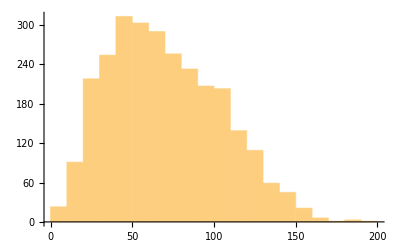

```mathematica
Histogram[Sort[sentenceCounts]]
```

```mathematica
wordsCounts=numberWords/@ formattedBios
```

{167,477,326,2266,1144,412,3284,1287,1316,1166,933,2321,1119,783,1351,735,1730,938,549,1536,2093,1463,2454,443,190,673,564,874,3582,1240,629,729,900,1161,3082,1763,3319,943,696,601,760,2059,1940,848,1193,291,527,2819,762,516,1117,1101,990,449,1071,1512,1260,2429,1298,1175,709,1547,3646,422,312,565,2429,1980,813,391,2457,492,634,1247,903,1462,461,1417,722,1466,1030,520,672,459,2178,1080,848,1033,227,885,1557,1594,861,938,550,616,3170,688,1301,194,298,1113,1291,80,814,175,566,271,706,1860,834,1154,1413,793,759,763,1354,835,1160,557,1,753,1323,446,878,2617,1481,1973,2733,1268,486,3265,993,2227,1052,742,899,2174,579,2503,2265,245,698,1036,710,595,573,2578,692,1719,1310,1635,344,2235,1185,2061,340,1509,2110,2111,2432,680,1706,1083,1681,386,1048,2161,211,999,1303,1923,931,3110,1508,1321,1997,802,910,297,558,1038,1117,886,1810,1991,1292,1033,2609,1859,1317,3215,1457,1205,2334,931,320,2111,720,678,1438,950,1320,1348,730,2778,3630,934,499,626,2698,2020,1698,3271,1046,2109,674,2122,2919,1795,1831,1858,2416,2544,1678,1306,1065,2194,2472,3050,1327,2752,1907,1020,1839,1784,2509,2511,1812,3227,1054,1773,1832,1899,1818,2134,1206,1720,2621,1543,664,1925,2134,1455,2049,3422,2349,1851,2838,947,2420,1548,4267,1699,2095,3712,1540,2946,3272,2577,3108,560,830,2384,1233,1884,441,2252,354,810,766,2603,1209,3145,3086,1342,840,691,2485,1790,821,2025,3391,1931,517,1183,2685,1187,2944,2304,2565,794,1598,2516,485,1318,3208,2164,1385,1666,1099,3440,2779,2932,1639,1081,1872,1208,1525,969,1634,2536,2333,430,2483,2028,2046,1680,627,533,1953,2146,1083,1913,739,2141,2100,2506,2811,1005,1818,1007,971,1012,893,2168,863,992,2757,845,1551,2392,2434,2730,753,3110,1910,1611,3395,1469,3252,1407,2402,1942,800,1735,483,3746,583,794,3815,1544,1285,2698,616,1172,2479,571,1951,1581,1234,1904,2735,2253,2252,2396,1966,1110,736,1,1418,854,2072,1314,2520,1966,2565,1395,1949,1418,1648,2701,1046,2361,1366,1180,2261,1475,1260,731,1816,2232,2481,1820,1224,1247,1341,1753,697,756,1951,1131,2139,2045,572,1940,808,1984,1126,1312,1855,461,3068,206,726,3419,2578,837,2369,980,1335,252,2629,2660,1654,674,2393,1843,680,731,3203,324,1820,4674,1604,2485,248,658,1160,1086,2861,952,2139,1641,821,309,1,1017,2160,782,630,679,1121,1746,1496,890,2547,1729,2146,3040,2450,1133,1183,997,933,2616,959,1247,825,2945,2746,1135,2199,663,2439,2302,914,1428,1976,2119,3163,387,1415,2079,840,2886,1888,888,567,614,773,290,1007,2490,1154,1776,3089,747,739,1879,3088,930,2908,2264,3873,990,1878,1120,838,3219,1994,2037,586,1897,1160,1315,1786,2530,1063,920,920,1248,1065,300,1277,1501,1256,1593,1527,1076,1494,1298,998,2303,3144,1262,1773,1007,997,2147,694,360,614,1593,601,1419,1473,3446,990,500,1197,519,724,3104,1697,1966,1870,688,1851,2578,2331,1727,1412,2404,1686,724,521,648,1053,1933,2295,532,922,1819,1263,1044,1152,2369,2270,2564,1051,2609,2568,727,1491,1715,712,1110,2441,2776,634,1943,977,2971,2146,1050,2093,868,2920,1059,2490,2007,2330,1362,959,2294,3075,2210,2154,1236,3395,2123,1590,872,2900,2400,2202,1273,2802,920,1564,673,2150,613,2239,2346,2115,1233,235,1573,570,1809,2401,1847,1883,1660,1949,2277,1031,402,592,689,2520,641,1100,1525,2435,548,2105,1834,2021,2594,2135,2477,1894,543,2864,1355,2351,1088,3050,2455,1813,780,2625,2103,1086,1339,851,2802,1912,2603,2795,2215,2932,386,3157,858,3011,1103,2077,2775,550,3045,2046,2185,662,1769,995,2772,1964,1040,1523,2347,622,2486,1430,2073,2099,1364,3222,1851,997,723,2522,561,755,650,2033,4269,1772,2380,2246,1915,792,1710,2473,1113,1932,2360,590,2707,1270,598,873,1432,791,1079,1961,930,2875,2258,2052,2360,1516,391,808,708,1378,1819,1489,2006,2748,837,1322,1140,1859,2794,1071,1136,3270,3304,2787,713,2298,2529,595,1439,2754,2102,1876,1256,2606,671,3116,1270,481,2610,462,2176,1448,887,986,716,1429,1539,2887,597,963,2746,1458,1049,588,1592,1414,840,2847,1259,1012,1290,724,451,568,327,961,2314,1756,478,1410,1263,835,1828,1888,1883,3088,2191,1735,2114,2682,1101,2900,3681,2339,524,2935,2655,656,2238,1710,2468,1493,2292,2008,1313,1320,2814,771,613,1082,1262,1581,1098,1008,1972,994,3430,648,314,2147,1804,1445,772,2114,814,697,1019,1783,1556,642,1621,766,1502,1584,1266,1057,2132,2306,1007,669,270,1161,629,1545,2115,1697,948,525,929,661,1544,734,2211,1108,665,1876,1301,1895,2778,855,1722,2477,707,2149,2258,2582,1775,917,1,2861,372,1347,3194,1177,1053,695,875,1497,2575,1489,1484,264,1114,1321,295,1483,1327,1035,1133,925,1899,2099,1186,1426,1710,1075,1754,1258,3206,3040,707,1089,1125,487,355,765,620,947,2096,2385,1919,1380,1529,1298,2250,1905,501,861,752,1078,1016,2394,1894,2784,469,922,737,1120,567,1665,2925,2153,568,1221,1113,776,865,2118,875,2278,1377,811,2528,2369,1215,1035,542,607,2439,2403,1610,1108,1285,1288,1171,269,1003,1781,2915,542,1038,719,3218,1968,1019,1725,1101,652,1388,813,2590,336,1629,1902,953,871,1181,990,2319,1812,911,2011,2713,2693,1221,654,916,1406,3063,1411,2435,2926,443,405,1797,1080,1623,3019,297,3295,2040,1109,656,1464,982,1594,2365,611,1946,2760,1092,1326,958,854,1441,478,875,435,538,1533,625,392,1333,2178,2135,1558,325,776,1598,1824,1135,3146,376,1785,1378,2807,1588,558,1239,739,1243,573,927,766,2056,2422,2769,2887,2418,1002,1120,2078,993,595,2749,691,2191,573,674,997,1456,2781,901,750,1660,2764,1197,1322,168,2407,384,3070,2281,1,3066,1367,1444,1266,2557,1487,389,1112,2113,2658,802,2054,209,854,750,1397,585,819,298,2356,1578,2385,449,465,1995,905,953,1,1840,3494,848,560,2612,947,2385,695,1325,585,1011,2458,2694,423,505,1295,514,1592,1807,1724,759,2381,431,3215,1224,2452,1023,452,1417,1124,1393,1695,1028,3389,296,2735,2732,1490,267,1212,1210,1615,219,887,1840,1605,821,1281,3174,1654,505,1908,744,2381,2197,2785,436,288,1066,720,2582,1042,739,549,2339,2184,2295,836,576,1243,744,2444,2352,2130,1808,567,2656,1898,1171,1562,894,701,1738,1732,1447,437,2476,784,644,974,784,1808,2248,1329,551,2002,968,1483,1319,587,1160,328,1269,2062,2204,1959,2361,3289,664,1012,323,2020,2333,218,406,1137,3739,2672,2638,1795,366,874,2149,2431,1640,1469,642,713,163,1481,783,897,1163,626,1104,95,287,94,916,2223,1612,2507,1888,761,532,2944,298,311,2454,1144,2587,1410,1659,688,738,305,1554,458,514,973,2045,1355,1520,397,2565,1524,1474,714,712,1925,944,1679,1440,363,2341,887,666,2004,1250,1728,1165,1528,1597,1918,619,1173,1,2113,1647,802,1140,1525,955,1940,1498,1270,835,1048,1292,1250,2124,552,1222,2631,1323,3145,1839,1762,2311,410,1507,1677,1228,1679,2830,723,910,2634,870,664,689,1421,2655,715,1440,1869,419,1803,389,617,1319,1214,1017,2695,2411,669,1632,1445,2620,508,1820,1026,1178,3124,199,1829,3083,2638,1654,1336,2538,2151,1021,2655,1377,643,1724,2362,2123,1062,1206,762,630,339,755,607,3477,580,741,2548,661,770,1496,2787,2229,654,1398,1054,2709,891,1075,874,2109,1134,2585,676,1325,785,1135,1702,716,1657,237,1073,2290,929,1123,2739,2631,1701,1520,2221,2291,1239,2264,1854,775,462,1859,3214,2066,1117,1976,2935,899,2436,921,546,1434,2437,1396,2221,2523,156,630,2296,606,2577,2652,1832,1647,1764,2070,1078,2755,697,2530,961,2758,2173,1591,2690,1435,379,1936,1999,807,2671,503,2415,229,837,1186,2064,3055,2161,1891,793,1897,1337,766,2478,327,1985,2753,1153,1363,2590,1273,1835,1857,2413,722,948,2733,383,2345,1178,2008,759,1287,788,423,2243,1369,1369,1051,1227,2291,782,849,1210,2526,830,1082,898,1256,3571,1422,2948,2717,1712,651,1830,1451,882,1135,3196,3193,1214,467,1414,472,1797,2088,2547,2239,2582,417,2292,1753,646,1415,482,1394,2500,2523,1768,1868,1480,1977,1389,2640,872,2450,918,2308,2584,3319,3069,602,988,1073,475,660,2419,2339,2877,1454,1427,2204,1279,909,2505,2583,2138,923,1968,1977,1517,1526,2242,286,1707,2029,173,2871,3137,568,1072,396,811,1286,2373,1888,3072,1330,658,2429,1745,516,738,2592,2052,1626,1498,2363,1236,727,1333,1044,2582,2005,2083,2171,487,1430,1181,741,1557,2217,922,1864,732,2500,1395,1577,427,1634,2794,1140,2470,850,290,924,1482,432,2816,944,1388,1907,1086,2366,1851,850,2147,2284,2525,1484,234,1134,1888,1658,2542,1042,1307,1236,2255,366,1182,608,775,2298,2143,349,1604,2585,1825,1950,1618,2447,2109,3105,1183,1379,2508,448,2994,327,1824,2306,746,1342,1222,1472,1102,1780,1365,2355,789,844,1815,144,2212,1220,1079,292,726,2889,1004,1192,236,2446,2008,1229,2201,1263,614,431,2731,1965,1475,1696,3558,1263,1988,1434,1241,2742,2132,908,1741,1615,931,413,1548,413,1122,2528,1904,1971,1421,1099,2252,2101,984,851,2142,1646,1654,1161,1094,585,1778,1721,2878,738,1526,1805,2348,1173,2567,2100,2921,806,806,2508,2502,3107,2499,2160,1433,2476,1898,1021,835,2408,1813,1895,2554,2456,1382,552,1537,1710,2301,2422,1130,319,2691,2202,2295,790,505,2776,368,2639,3362,361,3393,586,2255,2330,697,1399,3082,1393,1148,2739,671,2573,353,1578,1127,1823,1107,3605,1902,3077,1105,1209,1105,1287,1597,2620,2302,2686,1268,978,2762,672,2633,1627,3112,2285,2143,1848,485,2551,2989,1798,2454,994,921,2489,746,1789,2025,432,1277,292,1502,1820,3080,2752,2694,2108,575,1675,410,3065,2792,2817,1531,1969,594,1655,2219,723,1443,2534,1257,2366,1878,1559,1257,854,2764,1198,2541,2400,1116,1751,1135,2524,1234,2074,946,268,1081,2460,3381,1634,2635,1078,2131,1208,1394,1742,2707,1280,371,2961,744,1160,1409,427,2195,780,1809,2657,1688,1757,858,1937,1039,1341,1871,2371,2007,1018,1850,339,1391,864,2756,2029,2583,1066,1618,1426,2034,1251,1594,1986,1495,1693,1992,1802,1302,3562,876,2768,1305,2297,1837,1854,1183,1738,833,1713,1073,2665,1312,1232,1794,1846,1737,1153,868,1335,2656,1652,1270,40,2270,1203,1712,3315,2410,2722,2296,618,1614,3320,2397,886,768,1730,1494,2457,1784,1347,1421,962,2373,2656,1078,1377,731,1982,1046,2496,1758,2905,2627,1282,1504,1906,1705,2438,1891,976,2300,826,2925,407,1781,2252,932,2445,1353,513,3561,1856,2925,1212,1725,2013,1690,1787,1083,1163,1523,1605,961,1523,1094,2877,1325,1261,1173,2571,1452,471,2615,1963,1591,1556,993,1950,2953,1597,1530,2381,1734,524,2442,2603,2573,1645,2691,823,1246,1537,2610,1946,1492,1004,1450,1828,2532,979,2828,2326,1317,3465,2281,1122,1103,1358,2851,1481,1205,1245,3004,2659,1176,2418,714,1110,1145,822,1101,1309,3216,1365,2722,2523,997,2577,1133,2717,2089,2115,1841,2691,722,2472,2127,2042,2391,2667,1347,2239,3013,2010,1294,1285,801,2219,481,957,592,1304,3658,2467,940,2332,1336,3169,1130,1721,1528,1220,2842,3061,1877,2635,461,3316,2666,3484,1915,2219,2438,1905,1488,2282,2855,2071,2761,2725,2406,562,1780,1454,2524,953,1799,2301,1711,1120,2122,1459,2783,2493,2325,1724,2717,2561,2214,2857,1956,2264,1776,1357,2414,1876,241,675,2574,944,1020,1265,1666,2590,2375,1129,2666,2792,3157,1723,1653,1171,3413,2999,2607,2294,2889,3093,2238,1191,1176,1656,2455,1358,3088,1861,3003,1268,2528,296,1667,949,1149,2022,2417,3125,1531,1163,1673,1244,2627,2201,2712,1089,1310,2052,2894,997,1331,1386,2613,2756,1382,1383,2349,1135,1550,701,724,1822,1520,1221,2315,331,944,2426,2798,3142,1925,1488,1155,2102,2696,789,1720,1352,2297,2527,574,1320,1266,2535,2968,1767,1701,1563,2379,2148,2910,2242,1374,682,1374,2561,1773,1031,3253,1446,1502,2309,2004,2475,2732,1492,1708,2244,2081,1183,2670,2165,1113,1495,1137,2032,1682,1470,975,1813,2485,1960,1914,1980,2109,1,1663,1615,2334,2586,463,1485,2745,1956,1610,2380,1561,2071,321,1276,1325,777,1671,1297,1352,1771,1435,2122,2256,958,2657,691,2182,1241,2535,977,1226,2394,2806,1285,641,2637,3025,1472,648,2469,1379,1247,2362,1481,3951,2228,1578,1893,1931,1432,2137,1728,2629,2170,2343,975,1500,2869,1700,1826,2748,2506,576,1372,513,1889,1492,1862,3351,2393,2095,595,2395,2465,1429,802,3059,1362,2806,2715,1233,1395,2110,2580,2607,2404,1060,2716,1562,1988,2849,1215,1656,800,1975,3097,2154,1937,1382,2281,937,2051,1524,1048,1961,2266,778,960,1178,2667,2445,888,2446,764,1977,2379,725,1896,1919,2392,2108,2757,2173,2574,1254,1652,984,1306,1408,2969,989,1819,2246,1576,689,1134,2797,648,1900,1676,2901,3330,2076,2014,831,1270,1443,1271,1457,2542,723,2549,1623,1924,1353,1904,1403,1014,2413,1056,1529,1664,2529,1585,1860,2767,1692,1283,1733,1217,2651,2081,1691,1721,3243,1110,2459,2022,2485,1666,2301,715,3727,1463,1141,1818,2287,2309,2132,4028,1272,2207,1745,2665,2193,2154,2964,3238,1556,677,2571,2446,2432,2061,1313,3009,1043,1254,1837,1566,1204,1999,2870,1541,1064,1965,1986,2067,2498,1300,2162,1897,1526,2248,2377,1647,1981,2510,1839,1210,856,1281,1358,1064,2623,1116,1610,3398,2647,1096,1584,2353,2360,2597,2860,1632,2208,1024,837,2713,2670,2271,3382,2630,2256,573,2781,1559,2090,565,1521,1579,1172,1558,2069,1419,1924,2828,1847,907,1492,1317,1240,2488,2031,2060,2310,2768,2166,2366,1288,2137,1236,2762,44,1903,2578,2327,2172,2651,711,1296,601,2195,2244,1401,1292,1371,2506,2235,1250,2576,1795,1811,932,1564,1732,1785,1130,771,928,2287,1530,1434,2136,1397,1667,1693,1411,2220,1224,1754,1801,998,1188,1837,3014,1646,3465,1559,1764,1267,2163,2843,1660,1762,1631,1780,3193,1932,2357,2562,1398,2583,1783,1403,2644,2743,1569,1119,1204,2937,3248,1283,2951,2708,1286,1162,2851,398,2541,1062,1560,1925,1840,942,1191,1559,1978,2759,1219,2086,1040,1634,2624,2162,1552,2047,1153,2249,1199,1024,1869,3624,1522,2723,2259,1695,483,2604,969,1653,1334,2442,1616,2460,1553,1254,1405,1732,1124,2523,627,2579,2533,2246,1007,1580,1728,2841,2798,1853,2412,3208,1333,2913,1479,1323,2303,2287,796,1929,2120,1546,888,1384,1372,759,1062,1126,1515,2247,1500,1188,1828,1563,690,1685,1569,1373,953,1595,1121,765,2279,1841,1779,1439,1341,1782,1780,2422,2470,1830,1708,1257,2304,2185,2157,2868,2113,2977,1759,2285,1153,2534,2551}

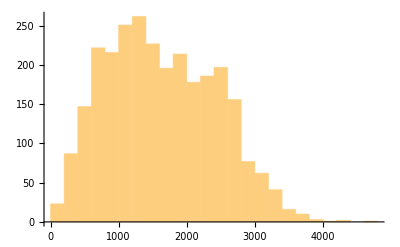

```mathematica
Histogram[Sort[wordsCounts]]
```

## Wikipedia Data

```mathematica
ClearAll[b]
```

```mathematica
enWikiGet[mgpid_String]:=With[{res=Import["https://query.wikidata.org/sparql?query="<>URLEncode["SELECT ?wikipedia_article
        WHERE
        {
          ?person wdt:P1563 \""<>mgpid<>"\" . 
          ?wikipedia_article schema:about ?person .
          ?wikipedia_article schema:isPartOf <https://en.wikipedia.org/> .
        }"]<>"&format=json","RawJSON"]},Replace[res["results","bindings"][[All,"wikipedia_article","value"]],{s_String}:>URLDecode@StringReplace[s,"https://en.wikipedia.org/wiki/"->""]]]
```

```mathematica
wikiNames=Map[enWikiGet,allNames];
```

```mathematica
wikiNames = Import["C:\\Users\\tanha\\Desktop\\Wolfram\\wikiNames.mx"];
```

```mathematica
allWikiHtmls =Import["C:\\Users\\tanha\\Desktop\\Wolfram\\allWikiHtmls.mx"];
```

## Trying to make WikiData WordCloud

```mathematica
formattedWikiBios =deleteHtmlElements[#]&/@allWikiHtmls;
```

```mathematica
StringDelete[
                                                          getBodyBio[ allWikiHtmls[[1]] ],
                                                         "<"~~Shortest[__]~~">" 
                                                         ]
```

{}

## Wiki Social Network

```mathematica
wikiHtmlsasoc=AssociationThread[wikiNames,allWikiHtmls];
```

```mathematica
allWikiHtmlsFiltered = Select[wikiHtmlsasoc,StringQ];
```

```mathematica
wikiNameAsoc =AssociationThread[Keys[allWikiHtmlsFiltered],Map[Intersection[#,wikiNames]&,StringCases[Values[allWikiHtmlsFiltered],"/wiki/"~~Shortest[n__]~~"\""->n]]];
```

```mathematica
vertexList2 =Flatten@ MapThread[ Thread[Rule[#1 , #2]]&,{Keys[wikiNameAsoc],Values[wikiNameAsoc]}];
```

```mathematica
vertexList2//Length
```

30541

```mathematica
w =Graph[vertexList2,VertexLabels->Placed["Name",Tooltip]]
```

-Graphics-

```mathematica
newW=Reverse@SortBy[ConnectedGraphComponents[w],VertexCount];
```

```mathematica
graphObject =Graph[newW[[1]],VertexLabels->Placed["Name",Tooltip]]
```

-Graphics-

```mathematica
agents=Part[VertexList[graphObject],Ordering[BetweennessCentrality[graphObject],-5]]
```

{Michael_Atiyah,G._H._Hardy,Albert_Einstein,David_Hilbert,Isaac_Newton}

```mathematica
criticalWiki=BetweennessCentrality[graphObject];
criticalNodeWiki=Pick[VertexList[graphObject],criticalWiki,Max[criticalWiki]]
```

{Isaac_Newton}

```mathematica
CommunityGraphPlot[graphObject]
```

-Graphics-

```mathematica
wikiClique = FindClique[graphObject]
```

{{Thales_of_Miletus,Anaxagoras,Anthemius_of_Tralles,Apollonius_of_Perga,Archimedes,Archytas,Aristaeus_the_Elder,Aristarchus_of_Samos,Autolycus_of_Pitane,Bryson_of_Heraclea,Callippus,Chrysippus,Cleomedes,Conon_of_Samos,Democritus,Dinostratus,Diocles_(mathematician),Dionysodorus,Diophantus,Domninus_of_Larissa,Eratosthenes,Euclid,Eudemus_of_Rhodes,Eudoxus_of_Cnidus,Eutocius_of_Ascalon,Geminus,Hero_of_Alexandria,Hipparchus,Hippias,Hippocrates_of_Chios,Hypatia,Hypsicles,Marinus_of_Neapolis,Menaechmus,Menelaus_of_Alexandria,Nicomachus,Nicomedes_(mathematician),Oenopides,Pappus_of_Alexandria,Perseus_(geometer),Porphyry_(philosopher),Posidonius,Proclus,Ptolemy,Pythagoras,Serenus_of_Antinouplis,Simplicius_of_Cilicia,Sporus_of_Nicaea,Theaetetus_(mathematician),Theodorus_of_Cyrene,Theodosius_of_Bithynia,Theon_of_Alexandria,Theon_of_Smyrna,Thymaridas,Xenocrates,Zenodorus_(mathematician),Zeno_of_Elea,Zeno_of_Sidon}}

```mathematica
HighlightGraph[graphObject,Subgraph[graphObject,wikiClique]]
```

-Graphics-

## Mental Health Disorders List

```mathematica
mentalDisorders = {"acute stress disorder","adolescent antisocial behavior","agoraphobia","alcohol dependence","alcoholic hallucinosis","amnestic disorder","anosognosia","anterograde amnesia","anxiety disorder","atelophobia","attention deficit hyperactivity disorder","autophagia","avoidant/restrictive food intake disorder","benzodiazepine dependence","benzodiazepine withdrawal","bibliomania","bipolar disorder","bipolar ii disorder","borderline intellectual functioning","brief psychotic disorder","caffeine-induced anxiety disorder","cannabis dependence","catatonic schizophrenia","claustrophobia","cocaine intoxication","communication disorder","cotard delusion","delirium tremens","derealization","desynchronosis","diogenes syndrome","dissociative identity disorder","dyslexia","ekbom's syndrome","encopresis","enuresis","erotomania","extreme delusion","fregoli delusion","ganser syndrome","generalized anxiety disorder","grandiose delusions","hallucinogen persisting perception disorder","huntington's disease","hypochondriasis","insomnia","kleptomania","lacunar amnesia","major depressive episode","malingering","mathematics disorder","minor depressive disorder","mixed episode","munchausen's syndrome","narcolepsy","neurodevelopmental disorder","night eating syndrome","obsessive-compulsive disorder","obsessive-compulsive personality disorder","ondine's curse","opioid dependence","oppositional defiant disorder","orthorexia","pain disorder","paranoid personality disorder","parkinson's disease","pathological gambling","personality disorder","phencyclidine","phobic disorder","psychosis","physical abuse","posttraumatic stress disorder","premature ejaculation","primary insomnia","psychogenic amnesia","pyromania","recurrent brief depression","residual schizophrenia","rumination syndrome","schizoid personality disorder","schizophreniform disorder","seasonal affective disorder","selective mutism","sexual fetishism","sexual sadism disorder","sleep disorder","sleep terror disorder","sleep paralysis","social phobia","somatoform disorder","stereotypic movement disorder","stuttering","tardive dyskinesia","transient global amnesia","trichotillomania","fatigue","dementia","depression","mental instability"};
```

Wiki Disorders

```mathematica
listOfDisorders=ToLowerCase[StringCases[Values[allWikiHtmlsFiltered],mentalDisorders,IgnoreCase->True]];
```

```mathematica
wikiAsocNames = Keys[allWikiHtmlsFiltered];
```

```mathematica
wikiMentalDiseases = Map[#->wikiAsocNames[[Flatten@Position[listOfDisorders,{___,ToLowerCase[#],___}]/.{{x_}}->x]]&,mentalDisorders];
```

```mathematica
BarChart[Counts[Flatten@Map[Union,listOfDisorders]],ChartLabels-> Placed[Automatic,{{0.5,0},{0.9,1}},Rotate[#,(2/7) Pi]&
]]
```

-Graphics-

MacTutor Disorders

```mathematica
listOfDisorders2=ToLowerCase[StringCases[htmlBioList,mentalDisorders,IgnoreCase->True]];
```

$Aborted

```mathematica
mcsMentalDiseases = Map[#->fullNames[[Flatten@Position[listOfDisorders2,{___,ToLowerCase[#],___}]/.{{x_}}->x]]&,mentalDisorders];
```

```mathematica
BarChart[Counts[Flatten@Map[Union,listOfDisorders2]],ChartLabels-> Placed[Automatic,{{0.5,0},{0.9,1}},Rotate[#,(2/7) Pi]&
]]
```

-Graphics-

# Drug Use

```mathematica
drugList = List["alcohol","amphetamine","caffeine","cannabis","club drugs","cocaine","date rape drugs","dextromethorphan","hallucinogens","heroin","inhalants","ketamine"," LSD ", "marijuana","methamphetamine","phencyclidine","prescription medicines","ritalin","rohypnol","steroids","stimulants"];
```

```mathematica
listOfWikiDrugs=ToLowerCase[StringCases[Values[allWikiHtmlsFiltered],drugList,IgnoreCase->True]];
```

```mathematica
wikiNamesforDrugs = Keys[allWikiHtmlsFiltered];
```

```mathematica
wikiDrugUsers = Map[#->wikiNamesforDrugs[[Flatten@Position[listOfWikiDrugs,{___,ToLowerCase[#],___}]/.{{x_}}->x]]&,drugList]
```

{alcohol→{Al-Kindi,Ulugh_Beg,Benjamin_Banneker,George_Green_(mathematician),Adolphe_Quetelet,Niels_Henrik_Abel,Robert_Murphy_(mathematician),Florence_Nightingale,Karl_Pearson,Torsten_Carleman,Prasanta_Chandra_Mahalanobis,Max_Euwe,Renato_Caccioppoli,Paul_Erdős,Richard_Feynman,Kristen_Nygaard,Rajeev_Motwani},amphetamine→{Paul_Erdős},caffeine→{},cannabis→{Avicenna,Richard_Feynman},club drugs→{},cocaine→{Avicenna},date rape drugs→{},dextromethorphan→{},hallucinogens→{},heroin→{Hypatia,Caroline_Herschel,Lewis_Carroll,Hertha_Ayrton,Pierre_Duhem,Katherine_Johnson,Bella_Subbotovskaya},inhalants→{},ketamine→{Richard_Feynman}, LSD →{},marijuana→{Richard_Feynman},methamphetamine→{},phencyclidine→{},prescription medicines→{},ritalin→{},rohypnol→{},steroids→{Giordano_Bruno,Pierre_Varignon,Thorvald_N._Thiele,Pierre_Puiseux,Ernest_William_Brown,Henrietta_Swan_Leavitt,Edwin_Hubble,Aleksei_Pogorelov},stimulants→{}}

```mathematica
BarChart[Counts[Flatten@Map[Union,listOfWikiDrugs]],ChartLabels-> Placed[Automatic,{{0.5,0},{0.9,1}},Rotate[#,(2/7) Pi]&
]]
```

-Graphics-

```mathematica
listOfDrugs=ToLowerCase[StringCases[htmlBioList,drugList,IgnoreCase->True]];
```

```mathematica
mcsDrugUsers = Map[#->fullNames[[Flatten@Position[listOfDrugs,{___,ToLowerCase[#],___}]/.{{x_}}->x]]&,drugList]
```

{alcohol→{{André Marie Ampère},{ Joseph Antoine Ferdinand Plateau},{Sir William Rowan Hamilton},{Robert Murphy},{ Samuel Loyd},{Adolphe-Louis Jacques Bertillon},{Ernst Fiedler},{ John Charles Fields},{Agner Krarup Erlang},{David Enskog},{Oskar Klein},{Dorothy Maud Wrinch},{Harold Hotelling},{Howard Hathaway Aiken},{Alexander Murray Macbeath},{Germund Dahlquist},{James Gourlay Clunie},{Kristen Nygaard},{Daniel Gray Quillen},{Patrick Keast},{Ruth Ingrid Michler}},amphetamine→{},caffeine→{},cannabis→{},club drugs→{},cocaine→{},date rape drugs→{},dextromethorphan→{},hallucinogens→{},heroin→{{Hypatia of Alexandria },{Phoebe Sarah Hertha Marks Ayrton},{Katherine Coleman Goble Johnson},{Marjorie Lee Wikler Senechal}},inhalants→{},ketamine→{}, LSD →{},marijuana→{},methamphetamine→{},phencyclidine→{},prescription medicines→{},ritalin→{},rohypnol→{},steroids→{{Enno Heeren Dirksen},{Benjamin Peirce},{Urbain Jean Joseph Le Verrier},{ Simon Newcomb},{Gustav Herglotz},{Tadeusz Boleslaw &#346;lebarski}},stimulants→{{Sir William Rowan Hamilton}}}

```mathematica
BarChart[Counts[Flatten@Map[Union,listOfDrugs]],ChartLabels-> Placed[Automatic,{{0.5,0},{0.9,1}},Rotate[#,(2/7) Pi]&
]]
```

-Graphics-

## Female Mathematicians

```mathematica
femaleDataset = Import["http://www-history.mcs.st-and.ac.uk/Indexes/Women.html",{"Hyperlinks"}]
```

{http://www-history.mcs.st-and.ac.uk/Biographies/Ayrton.html,http://www-history.mcs.st-and.ac.uk/Biographies/Bari.html,http://www-history.mcs.st-and.ac.uk/Biographies/Bartik.html,http://www-history.mcs.st-and.ac.uk/Biographies/Bassi.html,http://www-history.mcs.st-and.ac.uk/Biographies/Baxter.html,http://www-history.mcs.st-and.ac.uk/Biographies/Beale.html,http://www-history.mcs.st-and.ac.uk/Biographies/Birman.html,http://www-history.mcs.st-and.ac.uk/Biographies/Blanch.html,http://www-history.mcs.st-and.ac.uk/Biographies/Blum.html,http://www-history.mcs.st-and.ac.uk/Biographies/Boole_Mary.html,http://www-history.mcs.st-and.ac.uk/Biographies/Borok.html,http://www-history.mcs.st-and.ac.uk/Biographies/Bosworth.html,http://www-history.mcs.st-and.ac.uk/Biographies/Boyle_Margaret.html,http://www-history.mcs.st-and.ac.uk/Biographies/Browne.html,http://www-history.mcs.st-and.ac.uk/Biographies/Bryant.html,http://www-history.mcs.st-and.ac.uk/Biographies/Burton.html,http://www-history.mcs.st-and.ac.uk/Biographies/Calderwood.html,http://www-history.mcs.st-and.ac.uk/Biographies/Cannell.html,http://www-history.mcs.st-and.ac.uk/Biographies/Cartwright.html,http://www-history.mcs.st-and.ac.uk/Biographies/Castelnuovo_Emma.html,http://www-history.mcs.st-and.ac.uk/Biographies/Chang.html,http://www-history.mcs.st-and.ac.uk/Biographies/Chatelet.html,http://www-history.mcs.st-and.ac.uk/Biographies/Chisholm_Young.html,http://www-history.mcs.st-and.ac.uk/Biographies/Choquet-Bruhat.html,http://www-history.mcs.st-and.ac.uk/Biographies/Chung.html,http://www-history.mcs.st-and.ac.uk/Biographies/Clarke_Joan.html,http://www-history.mcs.st-and.ac.uk/Biographies/Clerke.html,http://www-history.mcs.st-and.ac.uk/Biographies/Cobbe.html,http://www-history.mcs.st-and.ac.uk/Biographies/Cofman.html,http://www-history.mcs.st-and.ac.uk/Biographies/Cox.html,http://www-history.mcs.st-and.ac.uk/Biographies/Daubechies.html,http://www-history.mcs.st-and.ac.uk/Biographies/David.html,http://www-history.mcs.st-and.ac.uk/Biographies/Deans.html,http://www-history.mcs.st-and.ac.uk/Biographies/Dubreil-Jacotin.html,http://www-history.mcs.st-and.ac.uk/Biographies/Edmonds.html,http://www-history.mcs.st-and.ac.uk/Biographies/Ehrenfest-Afanassjewa.html,http://www-history.mcs.st-and.ac.uk/Biographies/Faddeeva.html,http://www-history.mcs.st-and.ac.uk/Biographies/Falconer.html,http://www-history.mcs.st-and.ac.uk/Biographies/Fasenmyer.html,http://www-history.mcs.st-and.ac.uk/Biographies/Fawcett.html,http://www-history.mcs.st-and.ac.uk/Biographies/Fennema.html,http://www-history.mcs.st-and.ac.uk/Biographies/Ferrand.html,http://www-history.mcs.st-and.ac.uk/Biographies/Flugge-Lotz.html,http://www-history.mcs.st-and.ac.uk/Biographies/Freitag.html,http://www-history.mcs.st-and.ac.uk/Biographies/Geiringer.html,http://www-history.mcs.st-and.ac.uk/Biographies/Gentry.html,http://www-history.mcs.st-and.ac.uk/Biographies/Germain.html,http://www-history.mcs.st-and.ac.uk/Biographies/Gould.html,http://www-history.mcs.st-and.ac.uk/Biographies/Granville.html,http://www-history.mcs.st-and.ac.uk/Biographies/Gray.html,http://www-history.mcs.st-and.ac.uk/Biographies/Gray_Marion.html,http://www-history.mcs.st-and.ac.uk/Biographies/Griffiths_Lois.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hamill.html,http://www-history.mcs.st-and.ac.uk/Biographies/Haynes.html,http://www-history.mcs.st-and.ac.uk/Biographies/Harlay.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hau.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hay.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hayes.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hazlett.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hellman.html,http://www-history.mcs.st-and.ac.uk/Biographies/Henriques.html,http://www-history.mcs.st-and.ac.uk/Biographies/Herschel_Caroline.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hevelius_Koopman.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hewitt.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hopper.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hudson.html,http://www-history.mcs.st-and.ac.uk/Biographies/Hypatia.html,http://www-history.mcs.st-and.ac.uk/Biographies/Janovskaja.html,http://www-history.mcs.st-and.ac.uk/Biographies/Jitomirskaya.html,http://www-history.mcs.st-and.ac.uk/Biographies/Johnson_Katherine.html,http://www-history.mcs.st-and.ac.uk/Biographies/Karp.html,http://www-history.mcs.st-and.ac.uk/Biographies/Keen.html,http://www-history.mcs.st-and.ac.uk/Biographies/Keldysh_Lyudmila.html,http://www-history.mcs.st-and.ac.uk/Biographies/Kochina.html,http://www-history.mcs.st-and.ac.uk/Biographies/Kovalevskaya.html,http://www-history.mcs.st-and.ac.uk/Biographies/Kramer.html,http://www-history.mcs.st-and.ac.uk/Biographies/Krieger.html,http://www-history.mcs.st-and.ac.uk/Biographies/Kuperberg.html,http://www-history.mcs.st-and.ac.uk/Biographies/Ladd-Franklin.html,http://www-history.mcs.st-and.ac.uk/Biographies/Ladyzhenskaya.html,http://www-history.mcs.st-and.ac.uk/Biographies/Lax_Anneli.html,http://www-history.mcs.st-and.ac.uk/Biographies/Leavitt.html,http://www-history.mcs.st-and.ac.uk/Biographies/Lehmer_Emma.html,http://www-history.mcs.st-and.ac.uk/Biographies/Lepaute.html,http://www-history.mcs.st-and.ac.uk/Biographies/Libermann.html,http://www-history.mcs.st-and.ac.uk/Biographies/Lovelace.html,http://www-history.mcs.st-and.ac.uk/Biographies/Luchins.html,http://www-history.mcs.st-and.ac.uk/Biographies/Macintyre.html,http://www-history.mcs.st-and.ac.uk/Biographies/Mackenzie.html,http://www-history.mcs.st-and.ac.uk/Biographies/MacMillan_Chrystal.html,http://www-history.mcs.st-and.ac.uk/Biographies/Maddison.html,http://www-history.mcs.st-and.ac.uk/Biographies/Malone-Mayes.html,http://www-history.mcs.st-and.ac.uk/Biographies/Martin_Emilie.html,http://www-history.mcs.st-and.ac.uk/Biographies/McDuff.html,http://www-history.mcs.st-and.ac.uk/Biographies/Merrill.html,http://www-history.mcs.st-and.ac.uk/Biographies/Michler.html,http://www-history.mcs.st-and.ac.uk/Biographies/Millington.html,http://www-history.mcs.st-and.ac.uk/Biographies/Mirzakhani.html,http://www-history.mcs.st-and.ac.uk/Biographies/Morawetz.html,http://www-history.mcs.st-and.ac.uk/Biographies/Moufang.html,http://www-history.mcs.st-and.ac.uk/Biographies/Nalli.html,http://www-history.mcs.st-and.ac.uk/Biographies/Nelson.html,http://www-history.mcs.st-and.ac.uk/Biographies/Neumann_Hanna.html,http://www-history.mcs.st-and.ac.uk/Biographies/Newson.html,http://www-history.mcs.st-and.ac.uk/Biographies/Nicolson.html,http://www-history.mcs.st-and.ac.uk/Biographies/Nightingale.html,http://www-history.mcs.st-and.ac.uk/Biographies/Noether_Emmy.html,http://www-history.mcs.st-and.ac.uk/Biographies/Nugel.html,http://www-history.mcs.st-and.ac.uk/Biographies/Numbers.html,http://www-history.mcs.st-and.ac.uk/Biographies/Oleinik.html,http://www-history.mcs.st-and.ac.uk/Biographies/Olive.html,http://www-history.mcs.st-and.ac.uk/Biographies/Ollerenshaw.html,http://www-history.mcs.st-and.ac.uk/Biographies/Orshansky.html,http://www-history.mcs.st-and.ac.uk/Biographies/Pairman.html,http://www-history.mcs.st-and.ac.uk/Biographies/Pandrosion.html,http://www-history.mcs.st-and.ac.uk/Biographies/Payne-Gaposchkin.html,http://www-history.mcs.st-and.ac.uk/Biographies/Perrin-Riou.html,http://www-history.mcs.st-and.ac.uk/Biographies/Peter.html,http://www-history.mcs.st-and.ac.uk/Biographies/Philip_Flora.html,http://www-history.mcs.st-and.ac.uk/Biographies/Pless.html,http://www-history.mcs.st-and.ac.uk/Biographies/Praeger.html,http://www-history.mcs.st-and.ac.uk/Biographies/Rasiowa.html,http://www-history.mcs.st-and.ac.uk/Biographies/Ratner.html,http://www-history.mcs.st-and.ac.uk/Biographies/Rees.html,http://www-history.mcs.st-and.ac.uk/Biographies/Rhodes.html,http://www-history.mcs.st-and.ac.uk/Biographies/Robinson_Julia.html,http://www-history.mcs.st-and.ac.uk/Biographies/Rothe-Ille.html,http://www-history.mcs.st-and.ac.uk/Biographies/Rudin.html,http://www-history.mcs.st-and.ac.uk/Biographies/Sadosky.html,http://www-history.mcs.st-and.ac.uk/Biographies/Sargent.html,http://www-history.mcs.st-and.ac.uk/Biographies/Schafer.html,http://www-history.mcs.st-and.ac.uk/Biographies/Schattschneider.html,http://www-history.mcs.st-and.ac.uk/Biographies/Scott.html,http://www-history.mcs.st-and.ac.uk/Biographies/Scott_Agnes.html,http://www-history.mcs.st-and.ac.uk/Biographies/Scott_Elizabeth.html,http://www-history.mcs.st-and.ac.uk/Biographies/Senechal.html,http://www-history.mcs.st-and.ac.uk/Biographies/Simpson_Mary.html,http://www-history.mcs.st-and.ac.uk/Biographies/Smith_Karen.html,http://www-history.mcs.st-and.ac.uk/Biographies/Somerville.html,http://www-history.mcs.st-and.ac.uk/Biographies/Sperry.html,http://www-history.mcs.st-and.ac.uk/Biographies/Srinivasan.html,http://www-history.mcs.st-and.ac.uk/Biographies/Steele.html,http://www-history.mcs.st-and.ac.uk/Biographies/Stephansen.html,http://www-history.mcs.st-and.ac.uk/Biographies/Stott.html,http://www-history.mcs.st-and.ac.uk/Biographies/Swain.html,http://www-history.mcs.st-and.ac.uk/Biographies/Szmielew.html,http://www-history.mcs.st-and.ac.uk/Biographies/Taussky-Todd.html,http://www-history.mcs.st-and.ac.uk/Biographies/Taylor_Mary.html,http://www-history.mcs.st-and.ac.uk/Biographies/Thompson_Abigail.html,http://www-history.mcs.st-and.ac.uk/Biographies/Tinney.html,http://www-history.mcs.st-and.ac.uk/Biographies/Uhlenbeck_Karen.html,http://www-history.mcs.st-and.ac.uk/Biographies/Velez-Rodriguez.html,http://www-history.mcs.st-and.ac.uk/Biographies/Vernon.html,http://www-history.mcs.st-and.ac.uk/Biographies/Wales.html,http://www-history.mcs.st-and.ac.uk/Biographies/Walter.html,http://www-history.mcs.st-and.ac.uk/Biographies/Warner.html,http://www-history.mcs.st-and.ac.uk/Biographies/Wexler-Kreindler.html,http://www-history.mcs.st-and.ac.uk/Biographies/Wheeler.html,http://www-history.mcs.st-and.ac.uk/Biographies/Wood.html,http://www-history.mcs.st-and.ac.uk/Biographies/Wrinch.html,http://www-history.mcs.st-and.ac.uk/Biographies/Wu.html,http://www-history.mcs.st-and.ac.uk/Biographies/Young_Lai-Sang.html,http://www-history.mcs.st-and.ac.uk/Davis/index.html,http://www-history.mcs.st-and.ac.uk/Indexes/Women_pics.html,http://www-history.mcs.st-and.ac.uk/Indexes/A.html,http://www-history.mcs.st-and.ac.uk/Indexes/B.html,http://www-history.mcs.st-and.ac.uk/Indexes/C.html,http://www-history.mcs.st-and.ac.uk/Indexes/D.html,http://www-history.mcs.st-and.ac.uk/Indexes/E.html,http://www-history.mcs.st-and.ac.uk/Indexes/F.html,http://www-history.mcs.st-and.ac.uk/Indexes/G.html,http://www-history.mcs.st-and.ac.uk/Indexes/H.html,http://www-history.mcs.st-and.ac.uk/Indexes/IJ.html,http://www-history.mcs.st-and.ac.uk/Indexes/K.html,http://www-history.mcs.st-and.ac.uk/Indexes/L.html,http://www-history.mcs.st-and.ac.uk/Indexes/M.html,http://www-history.mcs.st-and.ac.uk/Indexes/N.html,http://www-history.mcs.st-and.ac.uk/Indexes/O.html,http://www-history.mcs.st-and.ac.uk/Indexes/PQ.html,http://www-history.mcs.st-and.ac.uk/Indexes/R.html,http://www-history.mcs.st-and.ac.uk/Indexes/S.html,http://www-history.mcs.st-and.ac.uk/Indexes/T.html,http://www-history.mcs.st-and.ac.uk/Indexes/UV.html,http://www-history.mcs.st-and.ac.uk/Indexes/W.html,http://www-history.mcs.st-and.ac.uk/Indexes/XYZ.html,http://www-history.mcs.st-and.ac.uk/index.html,http://www-history.mcs.st-and.ac.uk/BiogIndex.html,http://www-history.mcs.st-and.ac.uk/Indexes/Full_Chron.html,http://www-maths.mcs.st-andrews.ac.uk/,http://www.st-andrews.ac.uk/,http://www-maths.mcs.st-andrews.ac.uk/}

```mathematica
femaleDataset1 =Flatten[StringCases[femaleDataset,"http://www-history.mcs.st-and.ac.uk/Biographies/"~~__]];
```

```mathematica
femaleDataset2 = Import[#,"Text"]&/@femaleDataset1
```

{25839,23105,21446,12250,8948,152,27091,17744,12880,14815,17691}
 |  |  |  |

```mathematica
femHtmls= Map[htmlToText,femaleDataset2]
```

{25804,23084,21446,12236,8948,152,27045,17744,12880,14801,17677}
 |  |  |  |

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\tanha\OneDrive\Documents\GitHub\Summer2018\StudentDeliverables

```mathematica
Export["femaleBioList.mx",femHtmls,"MX"]
```

femaleBioList.mx

```mathematica
femBioList = Import["C:\\Users\\tanha\\OneDrive\\Documents\\GitHub\\Summer2018\\StudentDeliverables\\femaleBioList.mx"]
```

{25804,23084,21446,12236,8948,152,27045,17744,12880,14801,17677}
 |  |  |  |

```mathematica
femFullNames = StringCases[femBioList,"<h1>"~~x__~~"</h1>"->x]
```

{{Phoebe Sarah Hertha Marks Ayrton},{Nina Karlovna Bari},{Betty Jean Jennings Bartik},{Laura Maria Catarina Bassi},{Agnes Sime Baxter},{Dorothea Beale},{Joan Sylvia Lyttle Birman},{Gertrude Blanch},{Lenore Blum},{Mary Everest Boole},{Valentina Mikhailovna Borok},{Anne Lucy Bosworth Focke},{Margaret Edward Boyle},{Marjorie Lee Browne},{Sophie Willock Bryant},{Leone Minna Gold Burton},{Nora Isobel Calderwood},{Doris Mary Cannell},{Dame Mary Lucy Cartwright},{Emma Castelnuovo},{Sun-Yung Alice Chang},{ Gabrielle Émilie Le Tonnelier de  Breteuil Marquise du Châtelet},{Grace Chisholm Young},{Yvonne Suzanne Marie-Louise Choquet-Bruhat},{Fan Rong K Chung Graham},{Joan Elisabeth Lowther Clarke Murray},{Agnes Mary Clerke},{Anne Philippa Cobbe},{Judita Cofman},{Gertrude Mary Cox},{Ingrid Daubechies},{Florence Nightingale David},{Winifred Margaret Deans},{Marie-Louise Dubreil-Jacotin},{Sheila May Edmonds},{Tatiana Ehrenfest-Afanassjewa},{Vera Nikolaevna Faddeeva},{Etta Zuber Falconer},{Mary Celine Fasenmyer},{Philippa Garrett Fawcett},{Ann Elizabeth Hammer Fennema},{Jacqueline Ferrand},{Irmgard Flügge-Lotz},{Herta Taussig Freitag},{Hilda Geiringer von Mises},{Ruth Ellen Gentry},{Marie-Sophie Germain},{Alice Bache Gould},{Evelyn Boyd Granville},{Mary Lee Wheat Gray},{Marion Cameron Gray},{Lois Wilfred Griffiths},{Christine Mary Hamill},{Martha Euphemia Lofton Haynes},{Marie-Jeanne Amélie Harlay},{Lene Vestergaard Hau},{Louise Schmir Hay},{Ellen Amanda Hayes},{Olive Clio Hazlett},{Clarisse Doris Hellman},{Anna Adelaide Stafford Henriques},{Caroline Lucretia Herschel},{Catherina Elisabetha Koopman Hevelius},{Gloria Conyers Hewitt},{Grace Brewster Murray Hopper},{Hilda Phoebe Hudson},{Hypatia of Alexandria },{Sof'ja Aleksandrovna Janovskaja},{Svetlana Yakovlevna Jitomirskaya},{Katherine Coleman Goble Johnson},{Carol Ruth Karp},{Linda Goldway Keen},{Lyudmila Vsevolodovna Keldysh},{Pelageia Yakovlevna Polubarinova Kochina},{Sofia Vasilyevna Kovalevskaya},{Edna Ernestine Kramer Lassar},{Cypra Cecilia Krieger Dunaij},{Krystyna Maria Trybulec Kuperberg},{Christine Ladd-Franklin},{Olga Alexandrovna Ladyzhenskaya},{Anneli Cahn Lax},{Henrietta Swan Leavitt },{Emma Markovna Trotskaia Lehmer},{Nicole-Reine Etable de Labrière Lepaute},{Paulette Libermann},{ Augusta Ada King, countess of Lovelace},{Edith Hirsch Luchins},{Sheila Scott Macintyre},{Gladys Isabel Mackenzie},{Jessie Chrystal MacMillan},{Ada Isabel Maddison},{Vivienne Malone-Mayes},{Emilie Norton Martin},{Margaret Dusa Waddington McDuff},{Winifred Edgerton Merrill},{Ruth Ingrid Michler},{Margaret Hilary Ashworth Millington},{Maryam Mirzakhani},{Cathleen Synge Morawetz},{Ruth Moufang},{Pia Maria Nalli},{Evelyn Merle Roden Nelson},{Hanna Neumann},{Mary Frances Winston Newson},{Phyllis Nicolson},{Florence Nightingale},{Emmy Amalie Noether},{Frieda Nugel},{Annie Hutton Numbers},{Olga Arsen'evna Oleinik},{Gloria Olive},{Kathleen Timpson Ollerenshaw},{Mollie Orshansky},{Eleanor Pairman},{Pandrosion of Alexandria },{Cecilia Helena Payne-Gaposchkin},{Bernadette Perrin-Riou},{Rózsa Péter},{Flora Philip},{Vera Pless},{Cheryl Elisabeth Praeger},{Helena Rasiowa},{Marina Ratner},{Mina Spiegel Rees},{Ida Rhodes},{Julia Hall Bowman Robinson},{Hildegard Rothe-Ille},{Mary Ellen Rudin},{Cora Susana Sadosky},{Winifred Lydia Caunden Sargent},{Alice Turner Schafer},{Doris Jean Wood Schattschneider},{Charlotte Angas Scott},{Agnes Mary Scott},{Elizabeth Leonard Scott},{Marjorie Lee Wikler Senechal},{Mary Constance Simpson},{Karen Ellen Smith},{ Mary Fairfax Greig Somerville},{Pauline Sperry},{Bhama Srinivasan},{Catherine Cassels Steele},{Mary Ann Elizabeth Stephansen},{Alicia Boole Stott},{Lorna Mary Swain},{Wanda Montlak Szmielew},{Olga Taussky-Todd},{Mary Taylor Slow},{Abigail A Thompson},{Sheila Christina Power Tinney},{Karen Keskulla Uhlenbeck},{Argelia Velez-Rodriguez},{Siobhan O'Shea Vernon},{Muriel Kennett Wales},{Marion Ilse Walter},{Mary Wynne Warner},{Eléna Wexler-Kreindler},{Anna Johnson Pell Wheeler},{Frances Chick Wood},{Dorothy Maud Wrinch},{Sijue Wu},{Lai-Sang Young}}

```mathematica
fembioReferences = StringCases[femBioList,"../Mathematicians/"~~Shortest[a__]~~".html"->a];
```

```mathematica
femuniqueReference=Map[Union,fembioReferences]
```

{{Maxwell,Rayleigh,Scott,Thomson},{Aleksandrov,Chaplygin,Egorov,Fourier,Hadamard,Lavrentev,Lebesgue,Luzin,Menshov,Stepanov,Urysohn,Zhukovsky,Zygmund},{Eckert_John,Goldstine,Mauchly,Von_Neumann},{Descartes,Newton},{},{Euclid},{Artin,Chauvenet,Fox_Ralph,Magnus,Morawetz,Nirenberg,Noether_Emmy},{Baker,Goldstein,Ince,Karman,Mathieu_Emile,Planck,Snyder,Todd},{Euler,Gauss,Godel,Mandelbrot,Newton,Penrose,Smale,Turing},{Babbage,Boole,Herschel,Stott},{Cauchy,Lindelof,Phragmen},{Bolza,Halsted,Hilbert,Klein,Moore_Eliakim,Schonflies,Schur},{},{Granville},{Ladd-Franklin,Pappus,Scott},{Levy,Levy_Hyman,Russell,Whitehead},{Aitken,Numbers},{Green},{Ahlfors,De_Morgan,Hardy,Littlewood,Morton_Vernon,Sylvester,Titchmarsh,Watson,Whittaker},{Castelnuovo,Choquet,Clairaut,Dieudonne,Enriques,Euclid,Freudenthal,Klein,Lichnerowicz},{Aubin,Hedrick,Osgood,Schoen},{Clairaut,Euler,Fontenelle,Kline,Konig_Samuel,Leibniz,Maupertuis,Newton},{Cantor,Cartwright,Klein,Maddison,Young},{Apery,Bruhat,Cartan,Chern,Einstein,Heisenberg,Lichnerowicz,Lie,Schrodinger,Schwinger,Stiefel,Weyl,Wiener_Norbert,Yau},{Erdos,Graham,Ramsey,Schelp},{Fawcett,Turing},{Airy,Ball_Robert,Bessel,Cotes,De_Moivre,Galileo,Glaisher,Herschel,Herschel_Caroline,Huygens,Kepler,Lagrange,Landen,Laplace,Machin,Somerville,Wilson_Alexander},{Lane,Whitehead_Henry},{Hirzebruch},{Cochran,Quetelet,Yates},{Fourier},{Birnbaum,Fisher,Kendall_Maurice,Neyman,Nightingale,Pearson,Pearson_Egon,Wilks,Wolfowitz},{Born},{Artin,Bjerknes_Vilhelm,Cartan,Chevalley,Dubreil,Hadamard,Hilbert,Julia,Lebesgue,Leray,Levi-Civita,Noether_Emmy,Prufer,Rutherford,Schutzenberger,Vessiot,Weyl},{Al-Karaji,Hardy,Parseval},{Boltzmann,De_Bruijn,Ehrenfest,Euclid,Gibbs,Hilbert,Klein,Tutte,Zermelo},{Faddeev,Fiedler,Forsythe,Galerkin,Golub,Householder,Kantorovich,Kublanovskaya,Mikhlin,Peter,Smirnov,Steklov,Stieltjes,Taussky-Todd,Varga,Wilkinson},{Granville,Lorch,Moufang},{Bateman,Jacobi,Knuth,Legendre},{Ball,Hobson},{},{Apery,Denjoy,Dieudonne,Dubreil-Jacotin,Hayman,Julia,Lichnerowicz,Lindelof,Montel,Poincare,Valiron},{Karman},{Fibonacci,Gauss},{Lichtenstein,Mises,Neyman,Poisson,Pollaczek,Schur,Wheeler,Wirtinger},{Bouquet,Briot,Cayley,Fuchs,Klein,Schlesinger,Scott},{Archimedes,De_Prony,Euler,Gauss,Kummer,Lagrange,Laplace,Legendre,Newton,Poisson},{Bessel,Brocard,Gauss,Moore_Eliakim,Newcomb,Peirce_Benjamin},{Browne,Hille,John},{Scott},{Wheeler,Whittaker},{Birkhoff_Garrett,Brown,Carmichael,Dickson,MacDuffee,MacLane},{Todd},{Morley},{Herschel_Caroline,Lalande,Newton},{Bohr_Niels,Bose,Einstein,Heisenberg},{Artin,Lukasiewicz,Neumann_Hanna,Turing},{},{Albert_Abraham,Dickson,Galois,Halmos,Moore_Eliakim,Scott,Van_der_Waerden},{Boyer,Hopper},{Alexander,Apostol,Einstein,Nielsen_Jakob,Veblen,Wilder},{Flamsteed,Gauss,Herschel,Herschel_William,Maclaurin,Maskelyne,Somerville},{Arago,Bernoulli_Johann(III),Halley,Hevelius_Johannes},{},{Aiken,Eckert,Eckert_John,Mauchly,Ore},{Cayley,Cremona,Landau,Schottky,Schwarz,Scott,Semple},{Apollonius,Diophantus,Euclid,Heath,Ptolemy,Theon},{Ackermann,Aristotle,Church,Descartes,Euclid,Frege,Godel,Goodstein,Hilbert,Kleene,Lobachevsky,Polya,Rolle,Shatunovsky,Tarski,Turing,Wittgenstein,Zeno_of_Elea},{Arnold,Borok,Bourgain,Cantor,Green,Schrodinger,Sinai},{Claytor},{Godel},{Ahlfors,Bers,Courant,Fricke,Noether_Emmy,Riemann,Thurston},{Adian,Aleksandrov,Baire,Borel,Keldysh_Mstislav,Khinchin,Kolmogorov,Luzin,Menshov,Novikov,Peano,Steklov,Suslin},{Chaplygin,Friedmann,Keldysh_Mstislav,Kochin,Kovalevskaya,Krylov_Aleksei,Mittag-Leffler,Smirnov,Sobolev,Steklov,Vinogradov,Weierstrass},{Agnesi,Bruns,Chebyshev,Crelle,Kirchhoff,Konigsberger,Lame,Mittag-Leffler,Ostrogradski,Volterra,Weierstrass},{Dodgson,Einstein,Fermat,Kasner,Khayyam,Newton},{Fields,Morawetz,Nelson,Sierpinski,Synge},{Borsuk,Hurewicz,Kuratowski,Mostowski,Poincare,Seifert,Ulam},{Franklin_Fabian,Helmholtz,Peirce_Charles,Story,Sylvester},{Bernstein_Sergei,Cauchy,Chebyshev,Courant,Delone,Gelfand,Hilbert,Hopf,Kurosh,Leray,Maxwell,Navier,Petrovsky,Schrodinger,Smirnov,Sobolev,Steklov,Stepanov,Stokes,Tikhonov,Von_Neumann},{Courant,Hilbert,Lax_Peter,Poincare,Robbins},{Mittag-Leffler},{Crelle,Davenport,Erdos,Hardy,Hasse,Lehmer_Derrick,Lehmer_Derrick_N,Littlewood,Mahler,Mordell,Pontryagin,Vandiver},{Clairaut,Halley,Lalande},{Cartan,Ehresmann,Ferrand,Leray,Lichnerowicz,Lie,Poisson,Whitehead_Henry},{Babbage,De_Morgan,Menabrea,Ohm,Somerville},{Banach,Bonsall,Courant,Friedrichs,Germain,Hausdorff,Hypatia,Kovalevskaya,Noether_Emmy,Noether_Max,Weierstrass},{Abel,Cartwright,Gregory,Laplace,Macintyre_Archibald,Newton,Ramanujan,Whittaker,Wright},{Barkla},{Chrystal,Knott,Tait},{Burkhardt,Cayley,Chisholm_Young,Hilbert,Klein,Scott,Whitehead,Young},{Falconer,Granville,Hausdorff,Lorch,Moore_Robert},{Cayley,Hilbert,Klein,Scott},{Adams_Frank,Gelfand,Gromov,Milnor,Witten},{},{Atiyah,Baer,Ball,De_Rham,Hodge,Kahler,Loday,Macaulay,Manin,Penrose},{Fourier,Petersson,Ramanujan},{Fields,Kontsevich,McMullen,Riemann,Weil,Witten},{Birkhoff,Courant,Friedrichs,Karman,Krieger,Nelson,Synge},{Bieberbach,Dehn,Desargues,Descartes,Epstein,Euclid,Hellinger,Hilbert,Magnus,Pappus,Prager,Schonflies,Siegel,Szasz},{Bagnera,Bianchi,Borel,Castelnuovo,Denjoy,Dirichlet,Du_Bois-Reymond,Enriques,Fichera,Fredholm,Guccia,Hadamard,Hilbert,Lebesgue,Levi-Civita,Peano,Picone,Poincare,Ricci-Curbastro,Riemann,Segre_Corrado,Vallee_Poussin,Vitali,Volterra},{Krieger},{Bieberbach,Courant,Feigl,Hall,Hasse,Higman,Hirsch,Kurosh,Lehmer_Derrick,Neumann_Bernhard,Rado_Richard,Schmidt,Schur,Taussky-Todd,Whitehead_Henry,Wielandt},{Bolza,Chisholm_Young,Franklin_Fabian,Hermite,Hilbert,Klein,Kovalevskaya,Ladd-Franklin,Lame,Maschke,Moore_Eliakim,Scott,Smith_David,Weber_Heinrich},{Crank,Hartree,Richardson},{Aristotle,Cayley,Euclid,Quetelet,Sylvester},{Albert_Abraham,Artin,Blumenthal,Brauer,Einstein,Fischer,Gordan,Hasse,Hilbert,Klein,Lasker,Mertens,Minkowski,Noether_Max,Schwarzschild,Van_der_Waerden,Vandiver,Veblen,Weyl,Wheeler},{Cantor,Frobenius,Fuchs,Gauss,Gutzmer,Hilbert,Kronecker,Kummer,Lindemann,Noether_Emmy,Schottky,Schur,Schwarz,Wangerin,Weierstrass},{},{Dirichlet,Navier,Noether_Emmy,Petrovsky,Stokes},{Douglas,MacDuffee,MacLane,Rota},{Bondi,Einstein,Euler,Ferrar,Frenicle_de_Bessy,Mahler,Turing,Turnbull},{},{Birkhoff,Ford,Kemeny,Knott,Pearson},{Hypatia,Pappus},{Bohr_Niels,Eddington,Einstein,Euclid,Fowler,Newton},{Bloch,Coates,Euler,Galois,Godement,Hasse,Iwasawa,Kato,Tate},{Ackermann,Bernays,Bolyai,Carmichael,Dickson,Eotvos,Fejer,Godel,Goodstein,Herbrand,Hilbert,Kalmar,Kemeny,Kleene,Kurschak,Peano},{},{Conway,Hamming,Kaplansky,Noether_Emmy},{Neumann_Bernhard,Neumann_Hanna},{Borsuk,Heyting,Lukasiewicz,Mazurkiewicz,Mostowski,Post,Sierpinski,Stone,Tarski},{Bowen,Daubechies,Kolmogorov,Lie,Margulis,Noether_Emmy,Oppenheim,Ostrowski,Sinai,Uhlenbeck_Karen},{Dickson,MacLane,Noether_Emmy},{Blanch,Eckert_John,Hopper,Mauchly},{Bell,Church,Davis,Godel,Herbrand,Hilbert,Kleene,Neyman,Noether_Emmy,Post,Robinson_Raphael,Tarski,Turing,Wheeler},{Brauer_Alfred,Einstein,Erdos,Hopf,Rado_Richard,Ramsey,Rothe_Erich,Schmidt,Schottky,Schur,Turan,Van_der_Waerden},{Chisholm_Young,Hausdorff,Jones_Burton,Moore_Robert,Noether_Emmy,Rudin_Walter,Wilder},{Calderon,Cotlar,Darmois,Frechet,Noether_Emmy,Picone,Poincare,Riemann,Zygmund},{Bosanquet,Burkill,Cesaro,Denjoy,Fourier,Lebesgue,Perron,Riemann,Young},{},{},{Cayley,Gentry,Macaulay,Maddison,Whitehead},{Ford,Gibb},{David,Neyman,Sperry},{Apostol,Delone,Lorch,Menger,Wrinch},{},{Fefferman,Heinonen,Noether_Emmy},{Adams,Airy,Arago,Babbage,Biot,Euclid,Herschel,Herschel_Caroline,Herschel_William,Laplace,Leslie,Lovelace,Mathieu_Emile,Maxwell,Newton,Peacock,Playfair,Poinsot,Poisson,Wallace},{Wilczynski},{Blum,Brauer,Green_Sandy,Hall,Lie,Littlewood,Lusztig,Neumann_Bernhard,Newman,Noether_Emmy,Ramanujan,Ree,Van_der_Waerden},{},{DAlembert,Euler,Frobenius,Hilbert,Hurwitz,Klein,Lagrange,Zermelo},{Baker,Boole,Boole_Mary,Coxeter,Euclid,Schoute,Taylor_Geoffrey},{Lamb},{Borsuk,Coxeter,Hilbert,Kuratowski,Lindenbaum,Lukasiewicz,Malcev,Moore_Eliakim,Mostowski,Rasiowa,Robinson,Sierpinski,Tarski,Veblen},{Apostol,Artin,Courant,Crelle,Furtwangler,Godel,Hahn,Hardy,Helly,Hilbert,Magnus,Menger,Neumann_Hanna,Noether_Emmy,Schur,Sylow,Todd_John,Von_Neumann,Wirtinger},{Courant},{Birman,Dehn,Heegaard,Kirby,Thurston},{Born,Conway_Arthur,De_Valera,Dirac,Dyson,Eddington,Einstein,Feynman,Harish-Chandra,Schrodinger,Tait,Uhlenbeck,Weyl},{Courant,Donaldson,Einstein,Witten,Yau},{},{Kennedy},{Beatty},{Albert_Abraham,Bers,Blanch,Courant,Forsythe,Friedrichs,Hall_Marshall,Hunt,Kac,Kaplansky,Lanczos,Lehmer_Derrick,Motzkin,Polya,Schoenberg,Taussky-Todd,Walsh_Joseph,Wolfowitz},{Borsuk,Kuratowski,Whitehead_Henry,Zeeman},{Moisil,Ore},{Bocher,Fourier,Herglotz,Hilbert,Klein,Lichtenstein,Minkowski,Moore_Eliakim,Noether_Emmy,Osgood,Pell_Alexander,Schwarzschild,Scott},{Galton,Pearson,Yule},{Johnson,Russell,Von_Neumann,Wiener_Norbert},{},{Birman,Kovalevskaya,Lyapunov,McDuff,Noether_Emmy,Poincare}}

```mathematica
ClearAll[a]
```

```mathematica
allfemNames = Flatten@StringCases[Import["http://www-history.mcs.st-and.ac.uk/Indexes/Women.html",{"Hyperlinks"}],"/Biographies/"~~Shortest[a__]~~".html"->a];
```

```mathematica
Length[allfemNames] / Length[fullNames]
```

54/925

```mathematica
54/925.
```

0.0583784

```mathematica
femvertexList = Flatten@ MapThread[ Thread[Rule[#1 , #2]]&,{allfemNames,femuniqueReference}]
```

{Ayrton→Maxwell,Ayrton→Rayleigh,Ayrton→Scott,Ayrton→Thomson,Bari→Aleksandrov,Bari→Chaplygin,Bari→Egorov,Bari→Fourier,Bari→Hadamard,Bari→Lavrentev,Bari→Lebesgue,Bari→Luzin,Bari→Menshov,Bari→Stepanov,Bari→Urysohn,Bari→Zhukovsky,Bari→Zygmund,Bartik→Eckert_John,Bartik→Goldstine,Bartik→Mauchly,Bartik→Von_Neumann,Bassi→Descartes,Bassi→Newton,Beale→Euclid,Birman→Artin,Birman→Chauvenet,Birman→Fox_Ralph,Birman→Magnus,Birman→Morawetz,Birman→Nirenberg,Birman→Noether_Emmy,Blanch→Baker,Blanch→Goldstein,Blanch→Ince,Blanch→Karman,Blanch→Mathieu_Emile,Blanch→Planck,Blanch→Snyder,Blanch→Todd,Blum→Euler,Blum→Gauss,Blum→Godel,Blum→Mandelbrot,Blum→Newton,Blum→Penrose,Blum→Smale,Blum→Turing,Boole_Mary→Babbage,Boole_Mary→Boole,Boole_Mary→Herschel,Boole_Mary→Stott,Borok→Cauchy,Borok→Lindelof,Borok→Phragmen,Bosworth→Bolza,Bosworth→Halsted,Bosworth→Hilbert,Bosworth→Klein,Bosworth→Moore_Eliakim,Bosworth→Schonflies,Bosworth→Schur,Browne→Granville,Bryant→Ladd-Franklin,Bryant→Pappus,Bryant→Scott,Burton→Levy,Burton→Levy_Hyman,Burton→Russell,Burton→Whitehead,Calderwood→Aitken,Calderwood→Numbers,Cannell→Green,Cartwright→Ahlfors,Cartwright→De_Morgan,Cartwright→Hardy,Cartwright→Littlewood,Cartwright→Morton_Vernon,Cartwright→Sylvester,Cartwright→Titchmarsh,Cartwright→Watson,Cartwright→Whittaker,Castelnuovo_Emma→Castelnuovo,Castelnuovo_Emma→Choquet,Castelnuovo_Emma→Clairaut,Castelnuovo_Emma→Dieudonne,Castelnuovo_Emma→Enriques,Castelnuovo_Emma→Euclid,Castelnuovo_Emma→Freudenthal,Castelnuovo_Emma→Klein,Castelnuovo_Emma→Lichnerowicz,Chang→Aubin,Chang→Hedrick,Chang→Osgood,Chang→Schoen,Chatelet→Clairaut,Chatelet→Euler,Chatelet→Fontenelle,Chatelet→Kline,Chatelet→Konig_Samuel,Chatelet→Leibniz,Chatelet→Maupertuis,Chatelet→Newton,Chisholm_Young→Cantor,Chisholm_Young→Cartwright,Chisholm_Young→Klein,Chisholm_Young→Maddison,Chisholm_Young→Young,Choquet-Bruhat→Apery,Choquet-Bruhat→Bruhat,Choquet-Bruhat→Cartan,Choquet-Bruhat→Chern,Choquet-Bruhat→Einstein,Choquet-Bruhat→Heisenberg,Choquet-Bruhat→Lichnerowicz,Choquet-Bruhat→Lie,Choquet-Bruhat→Schrodinger,Choquet-Bruhat→Schwinger,Choquet-Bruhat→Stiefel,Choquet-Bruhat→Weyl,Choquet-Bruhat→Wiener_Norbert,Choquet-Bruhat→Yau,Chung→Erdos,Chung→Graham,Chung→Ramsey,Chung→Schelp,Clarke_Joan→Fawcett,Clarke_Joan→Turing,Clerke→Airy,Clerke→Ball_Robert,Clerke→Bessel,Clerke→Cotes,Clerke→De_Moivre,Clerke→Galileo,Clerke→Glaisher,Clerke→Herschel,Clerke→Herschel_Caroline,Clerke→Huygens,Clerke→Kepler,Clerke→Lagrange,Clerke→Landen,Clerke→Laplace,Clerke→Machin,Clerke→Somerville,Clerke→Wilson_Alexander,Cobbe→Lane,Cobbe→Whitehead_Henry,Cofman→Hirzebruch,Cox→Cochran,Cox→Quetelet,Cox→Yates,Daubechies→Fourier,David→Birnbaum,David→Fisher,David→Kendall_Maurice,David→Neyman,David→Nightingale,David→Pearson,David→Pearson_Egon,David→Wilks,David→Wolfowitz,Deans→Born,Dubreil-Jacotin→Artin,Dubreil-Jacotin→Bjerknes_Vilhelm,Dubreil-Jacotin→Cartan,Dubreil-Jacotin→Chevalley,Dubreil-Jacotin→Dubreil,Dubreil-Jacotin→Hadamard,Dubreil-Jacotin→Hilbert,Dubreil-Jacotin→Julia,Dubreil-Jacotin→Lebesgue,Dubreil-Jacotin→Leray,Dubreil-Jacotin→Levi-Civita,Dubreil-Jacotin→Noether_Emmy,Dubreil-Jacotin→Prufer,Dubreil-Jacotin→Rutherford,Dubreil-Jacotin→Schutzenberger,Dubreil-Jacotin→Vessiot,Dubreil-Jacotin→Weyl,Edmonds→Al-Karaji,Edmonds→Hardy,Edmonds→Parseval,Ehrenfest-Afanassjewa→Boltzmann,Ehrenfest-Afanassjewa→De_Bruijn,Ehrenfest-Afanassjewa→Ehrenfest,Ehrenfest-Afanassjewa→Euclid,Ehrenfest-Afanassjewa→Gibbs,Ehrenfest-Afanassjewa→Hilbert,Ehrenfest-Afanassjewa→Klein,Ehrenfest-Afanassjewa→Tutte,Ehrenfest-Afanassjewa→Zermelo,Faddeeva→Faddeev,Faddeeva→Fiedler,Faddeeva→Forsythe,Faddeeva→Galerkin,Faddeeva→Golub,Faddeeva→Householder,Faddeeva→Kantorovich,Faddeeva→Kublanovskaya,Faddeeva→Mikhlin,Faddeeva→Peter,Faddeeva→Smirnov,Faddeeva→Steklov,Faddeeva→Stieltjes,Faddeeva→Taussky-Todd,Faddeeva→Varga,Faddeeva→Wilkinson,Falconer→Granville,Falconer→Lorch,Falconer→Moufang,Fasenmyer→Bateman,Fasenmyer→Jacobi,Fasenmyer→Knuth,Fasenmyer→Legendre,Fawcett→Ball,Fawcett→Hobson,Ferrand→Apery,Ferrand→Denjoy,Ferrand→Dieudonne,Ferrand→Dubreil-Jacotin,Ferrand→Hayman,Ferrand→Julia,Ferrand→Lichnerowicz,Ferrand→Lindelof,Ferrand→Montel,Ferrand→Poincare,Ferrand→Valiron,Flugge-Lotz→Karman,Freitag→Fibonacci,Freitag→Gauss,Geiringer→Lichtenstein,Geiringer→Mises,Geiringer→Neyman,Geiringer→Poisson,Geiringer→Pollaczek,Geiringer→Schur,Geiringer→Wheeler,Geiringer→Wirtinger,Gentry→Bouquet,Gentry→Briot,Gentry→Cayley,Gentry→Fuchs,Gentry→Klein,Gentry→Schlesinger,Gentry→Scott,Germain→Archimedes,Germain→De_Prony,Germain→Euler,Germain→Gauss,Germain→Kummer,Germain→Lagrange,Germain→Laplace,Germain→Legendre,Germain→Newton,Germain→Poisson,Gould→Bessel,Gould→Brocard,Gould→Gauss,Gould→Moore_Eliakim,Gould→Newcomb,Gould→Peirce_Benjamin,Granville→Browne,Granville→Hille,Granville→John,Gray→Scott,Gray_Marion→Wheeler,Gray_Marion→Whittaker,Griffiths_Lois→Birkhoff_Garrett,Griffiths_Lois→Brown,Griffiths_Lois→Carmichael,Griffiths_Lois→Dickson,Griffiths_Lois→MacDuffee,Griffiths_Lois→MacLane,Hamill→Todd,Haynes→Morley,Harlay→Herschel_Caroline,Harlay→Lalande,Harlay→Newton,Hau→Bohr_Niels,Hau→Bose,Hau→Einstein,Hau→Heisenberg,Hay→Artin,Hay→Lukasiewicz,Hay→Neumann_Hanna,Hay→Turing,Hazlett→Albert_Abraham,Hazlett→Dickson,Hazlett→Galois,Hazlett→Halmos,Hazlett→Moore_Eliakim,Hazlett→Scott,Hazlett→Van_der_Waerden,Hellman→Boyer,Hellman→Hopper,Henriques→Alexander,Henriques→Apostol,Henriques→Einstein,Henriques→Nielsen_Jakob,Henriques→Veblen,Henriques→Wilder,Herschel_Caroline→Flamsteed,Herschel_Caroline→Gauss,Herschel_Caroline→Herschel,Herschel_Caroline→Herschel_William,Herschel_Caroline→Maclaurin,Herschel_Caroline→Maskelyne,Herschel_Caroline→Somerville,Hevelius_Koopman→Arago,Hevelius_Koopman→Bernoulli_Johann(III),Hevelius_Koopman→Halley,Hevelius_Koopman→Hevelius_Johannes,Hopper→Aiken,Hopper→Eckert,Hopper→Eckert_John,Hopper→Mauchly,Hopper→Ore,Hudson→Cayley,Hudson→Cremona,Hudson→Landau,Hudson→Schottky,Hudson→Schwarz,Hudson→Scott,Hudson→Semple,Hypatia→Apollonius,Hypatia→Diophantus,Hypatia→Euclid,Hypatia→Heath,Hypatia→Ptolemy,Hypatia→Theon,Janovskaja→Ackermann,Janovskaja→Aristotle,Janovskaja→Church,Janovskaja→Descartes,Janovskaja→Euclid,Janovskaja→Frege,Janovskaja→Godel,Janovskaja→Goodstein,Janovskaja→Hilbert,Janovskaja→Kleene,Janovskaja→Lobachevsky,Janovskaja→Polya,Janovskaja→Rolle,Janovskaja→Shatunovsky,Janovskaja→Tarski,Janovskaja→Turing,Janovskaja→Wittgenstein,Janovskaja→Zeno_of_Elea,Jitomirskaya→Arnold,Jitomirskaya→Borok,Jitomirskaya→Bourgain,Jitomirskaya→Cantor,Jitomirskaya→Green,Jitomirskaya→Schrodinger,Jitomirskaya→Sinai,Johnson_Katherine→Claytor,Karp→Godel,Keen→Ahlfors,Keen→Bers,Keen→Courant,Keen→Fricke,Keen→Noether_Emmy,Keen→Riemann,Keen→Thurston,Keldysh_Lyudmila→Adian,Keldysh_Lyudmila→Aleksandrov,Keldysh_Lyudmila→Baire,Keldysh_Lyudmila→Borel,Keldysh_Lyudmila→Keldysh_Mstislav,Keldysh_Lyudmila→Khinchin,Keldysh_Lyudmila→Kolmogorov,Keldysh_Lyudmila→Luzin,Keldysh_Lyudmila→Menshov,Keldysh_Lyudmila→Novikov,Keldysh_Lyudmila→Peano,Keldysh_Lyudmila→Steklov,Keldysh_Lyudmila→Suslin,Kochina→Chaplygin,Kochina→Friedmann,Kochina→Keldysh_Mstislav,Kochina→Kochin,Kochina→Kovalevskaya,Kochina→Krylov_Aleksei,Kochina→Mittag-Leffler,Kochina→Smirnov,Kochina→Sobolev,Kochina→Steklov,Kochina→Vinogradov,Kochina→Weierstrass,Kovalevskaya→Agnesi,Kovalevskaya→Bruns,Kovalevskaya→Chebyshev,Kovalevskaya→Crelle,Kovalevskaya→Kirchhoff,Kovalevskaya→Konigsberger,Kovalevskaya→Lame,Kovalevskaya→Mittag-Leffler,Kovalevskaya→Ostrogradski,Kovalevskaya→Volterra,Kovalevskaya→Weierstrass,Kramer→Dodgson,Kramer→Einstein,Kramer→Fermat,Kramer→Kasner,Kramer→Khayyam,Kramer→Newton,Krieger→Fields,Krieger→Morawetz,Krieger→Nelson,Krieger→Sierpinski,Krieger→Synge,Kuperberg→Borsuk,Kuperberg→Hurewicz,Kuperberg→Kuratowski,Kuperberg→Mostowski,Kuperberg→Poincare,Kuperberg→Seifert,Kuperberg→Ulam,Ladd-Franklin→Franklin_Fabian,Ladd-Franklin→Helmholtz,Ladd-Franklin→Peirce_Charles,Ladd-Franklin→Story,Ladd-Franklin→Sylvester,Ladyzhenskaya→Bernstein_Sergei,Ladyzhenskaya→Cauchy,Ladyzhenskaya→Chebyshev,Ladyzhenskaya→Courant,Ladyzhenskaya→Delone,Ladyzhenskaya→Gelfand,Ladyzhenskaya→Hilbert,Ladyzhenskaya→Hopf,Ladyzhenskaya→Kurosh,Ladyzhenskaya→Leray,Ladyzhenskaya→Maxwell,Ladyzhenskaya→Navier,Ladyzhenskaya→Petrovsky,Ladyzhenskaya→Schrodinger,Ladyzhenskaya→Smirnov,Ladyzhenskaya→Sobolev,Ladyzhenskaya→Steklov,Ladyzhenskaya→Stepanov,Ladyzhenskaya→Stokes,Ladyzhenskaya→Tikhonov,Ladyzhenskaya→Von_Neumann,Lax_Anneli→Courant,Lax_Anneli→Hilbert,Lax_Anneli→Lax_Peter,Lax_Anneli→Poincare,Lax_Anneli→Robbins,Leavitt→Mittag-Leffler,Lehmer_Emma→Crelle,Lehmer_Emma→Davenport,Lehmer_Emma→Erdos,Lehmer_Emma→Hardy,Lehmer_Emma→Hasse,Lehmer_Emma→Lehmer_Derrick,Lehmer_Emma→Lehmer_Derrick_N,Lehmer_Emma→Littlewood,Lehmer_Emma→Mahler,Lehmer_Emma→Mordell,Lehmer_Emma→Pontryagin,Lehmer_Emma→Vandiver,Lepaute→Clairaut,Lepaute→Halley,Lepaute→Lalande,Libermann→Cartan,Libermann→Ehresmann,Libermann→Ferrand,Libermann→Leray,Libermann→Lichnerowicz,Libermann→Lie,Libermann→Poisson,Libermann→Whitehead_Henry,Lovelace→Babbage,Lovelace→De_Morgan,Lovelace→Menabrea,Lovelace→Ohm,Lovelace→Somerville,Luchins→Banach,Luchins→Bonsall,Luchins→Courant,Luchins→Friedrichs,Luchins→Germain,Luchins→Hausdorff,Luchins→Hypatia,Luchins→Kovalevskaya,Luchins→Noether_Emmy,Luchins→Noether_Max,Luchins→Weierstrass,Macintyre→Abel,Macintyre→Cartwright,Macintyre→Gregory,Macintyre→Laplace,Macintyre→Macintyre_Archibald,Macintyre→Newton,Macintyre→Ramanujan,Macintyre→Whittaker,Macintyre→Wright,Mackenzie→Barkla,MacMillan_Chrystal→Chrystal,MacMillan_Chrystal→Knott,MacMillan_Chrystal→Tait,Maddison→Burkhardt,Maddison→Cayley,Maddison→Chisholm_Young,Maddison→Hilbert,Maddison→Klein,Maddison→Scott,Maddison→Whitehead,Maddison→Young,Malone-Mayes→Falconer,Malone-Mayes→Granville,Malone-Mayes→Hausdorff,Malone-Mayes→Lorch,Malone-Mayes→Moore_Robert,Martin_Emilie→Cayley,Martin_Emilie→Hilbert,Martin_Emilie→Klein,Martin_Emilie→Scott,McDuff→Adams_Frank,McDuff→Gelfand,McDuff→Gromov,McDuff→Milnor,McDuff→Witten,Michler→Atiyah,Michler→Baer,Michler→Ball,Michler→De_Rham,Michler→Hodge,Michler→Kahler,Michler→Loday,Michler→Macaulay,Michler→Manin,Michler→Penrose,Millington→Fourier,Millington→Petersson,Millington→Ramanujan,Mirzakhani→Fields,Mirzakhani→Kontsevich,Mirzakhani→McMullen,Mirzakhani→Riemann,Mirzakhani→Weil,Mirzakhani→Witten,Morawetz→Birkhoff,Morawetz→Courant,Morawetz→Friedrichs,Morawetz→Karman,Morawetz→Krieger,Morawetz→Nelson,Morawetz→Synge,Moufang→Bieberbach,Moufang→Dehn,Moufang→Desargues,Moufang→Descartes,Moufang→Epstein,Moufang→Euclid,Moufang→Hellinger,Moufang→Hilbert,Moufang→Magnus,Moufang→Pappus,Moufang→Prager,Moufang→Schonflies,Moufang→Siegel,Moufang→Szasz,Nalli→Bagnera,Nalli→Bianchi,Nalli→Borel,Nalli→Castelnuovo,Nalli→Denjoy,Nalli→Dirichlet,Nalli→Du_Bois-Reymond,Nalli→Enriques,Nalli→Fichera,Nalli→Fredholm,Nalli→Guccia,Nalli→Hadamard,Nalli→Hilbert,Nalli→Lebesgue,Nalli→Levi-Civita,Nalli→Peano,Nalli→Picone,Nalli→Poincare,Nalli→Ricci-Curbastro,Nalli→Riemann,Nalli→Segre_Corrado,Nalli→Vallee_Poussin,Nalli→Vitali,Nalli→Volterra,Nelson→Krieger,Neumann_Hanna→Bieberbach,Neumann_Hanna→Courant,Neumann_Hanna→Feigl,Neumann_Hanna→Hall,Neumann_Hanna→Hasse,Neumann_Hanna→Higman,Neumann_Hanna→Hirsch,Neumann_Hanna→Kurosh,Neumann_Hanna→Lehmer_Derrick,Neumann_Hanna→Neumann_Bernhard,Neumann_Hanna→Rado_Richard,Neumann_Hanna→Schmidt,Neumann_Hanna→Schur,Neumann_Hanna→Taussky-Todd,Neumann_Hanna→Whitehead_Henry,Neumann_Hanna→Wielandt,Newson→Bolza,Newson→Chisholm_Young,Newson→Franklin_Fabian,Newson→Hermite,Newson→Hilbert,Newson→Klein,Newson→Kovalevskaya,Newson→Ladd-Franklin,Newson→Lame,Newson→Maschke,Newson→Moore_Eliakim,Newson→Scott,Newson→Smith_David,Newson→Weber_Heinrich,Nicolson→Crank,Nicolson→Hartree,Nicolson→Richardson,Nightingale→Aristotle,Nightingale→Cayley,Nightingale→Euclid,Nightingale→Quetelet,Nightingale→Sylvester,Noether_Emmy→Albert_Abraham,Noether_Emmy→Artin,Noether_Emmy→Blumenthal,Noether_Emmy→Brauer,Noether_Emmy→Einstein,Noether_Emmy→Fischer,Noether_Emmy→Gordan,Noether_Emmy→Hasse,Noether_Emmy→Hilbert,Noether_Emmy→Klein,Noether_Emmy→Lasker,Noether_Emmy→Mertens,Noether_Emmy→Minkowski,Noether_Emmy→Noether_Max,Noether_Emmy→Schwarzschild,Noether_Emmy→Van_der_Waerden,Noether_Emmy→Vandiver,Noether_Emmy→Veblen,Noether_Emmy→Weyl,Noether_Emmy→Wheeler,Nugel→Cantor,Nugel→Frobenius,Nugel→Fuchs,Nugel→Gauss,Nugel→Gutzmer,Nugel→Hilbert,Nugel→Kronecker,Nugel→Kummer,Nugel→Lindemann,Nugel→Noether_Emmy,Nugel→Schottky,Nugel→Schur,Nugel→Schwarz,Nugel→Wangerin,Nugel→Weierstrass,Oleinik→Dirichlet,Oleinik→Navier,Oleinik→Noether_Emmy,Oleinik→Petrovsky,Oleinik→Stokes,Olive→Douglas,Olive→MacDuffee,Olive→MacLane,Olive→Rota,Ollerenshaw→Bondi,Ollerenshaw→Einstein,Ollerenshaw→Euler,Ollerenshaw→Ferrar,Ollerenshaw→Frenicle_de_Bessy,Ollerenshaw→Mahler,Ollerenshaw→Turing,Ollerenshaw→Turnbull,Pairman→Birkhoff,Pairman→Ford,Pairman→Kemeny,Pairman→Knott,Pairman→Pearson,Pandrosion→Hypatia,Pandrosion→Pappus,Payne-Gaposchkin→Bohr_Niels,Payne-Gaposchkin→Eddington,Payne-Gaposchkin→Einstein,Payne-Gaposchkin→Euclid,Payne-Gaposchkin→Fowler,Payne-Gaposchkin→Newton,Perrin-Riou→Bloch,Perrin-Riou→Coates,Perrin-Riou→Euler,Perrin-Riou→Galois,Perrin-Riou→Godement,Perrin-Riou→Hasse,Perrin-Riou→Iwasawa,Perrin-Riou→Kato,Perrin-Riou→Tate,Peter→Ackermann,Peter→Bernays,Peter→Bolyai,Peter→Carmichael,Peter→Dickson,Peter→Eotvos,Peter→Fejer,Peter→Godel,Peter→Goodstein,Peter→Herbrand,Peter→Hilbert,Peter→Kalmar,Peter→Kemeny,Peter→Kleene,Peter→Kurschak,Peter→Peano,Pless→Conway,Pless→Hamming,Pless→Kaplansky,Pless→Noether_Emmy,Praeger→Neumann_Bernhard,Praeger→Neumann_Hanna,Rasiowa→Borsuk,Rasiowa→Heyting,Rasiowa→Lukasiewicz,Rasiowa→Mazurkiewicz,Rasiowa→Mostowski,Rasiowa→Post,Rasiowa→Sierpinski,Rasiowa→Stone,Rasiowa→Tarski,Ratner→Bowen,Ratner→Daubechies,Ratner→Kolmogorov,Ratner→Lie,Ratner→Margulis,Ratner→Noether_Emmy,Ratner→Oppenheim,Ratner→Ostrowski,Ratner→Sinai,Ratner→Uhlenbeck_Karen,Rees→Dickson,Rees→MacLane,Rees→Noether_Emmy,Rhodes→Blanch,Rhodes→Eckert_John,Rhodes→Hopper,Rhodes→Mauchly,Robinson_Julia→Bell,Robinson_Julia→Church,Robinson_Julia→Davis,Robinson_Julia→Godel,Robinson_Julia→Herbrand,Robinson_Julia→Hilbert,Robinson_Julia→Kleene,Robinson_Julia→Neyman,Robinson_Julia→Noether_Emmy,Robinson_Julia→Post,Robinson_Julia→Robinson_Raphael,Robinson_Julia→Tarski,Robinson_Julia→Turing,Robinson_Julia→Wheeler,Rothe-Ille→Brauer_Alfred,Rothe-Ille→Einstein,Rothe-Ille→Erdos,Rothe-Ille→Hopf,Rothe-Ille→Rado_Richard,Rothe-Ille→Ramsey,Rothe-Ille→Rothe_Erich,Rothe-Ille→Schmidt,Rothe-Ille→Schottky,Rothe-Ille→Schur,Rothe-Ille→Turan,Rothe-Ille→Van_der_Waerden,Rudin→Chisholm_Young,Rudin→Hausdorff,Rudin→Jones_Burton,Rudin→Moore_Robert,Rudin→Noether_Emmy,Rudin→Rudin_Walter,Rudin→Wilder,Sadosky→Calderon,Sadosky→Cotlar,Sadosky→Darmois,Sadosky→Frechet,Sadosky→Noether_Emmy,Sadosky→Picone,Sadosky→Poincare,Sadosky→Riemann,Sadosky→Zygmund,Sargent→Bosanquet,Sargent→Burkill,Sargent→Cesaro,Sargent→Denjoy,Sargent→Fourier,Sargent→Lebesgue,Sargent→Perron,Sargent→Riemann,Sargent→Young,Scott→Cayley,Scott→Gentry,Scott→Macaulay,Scott→Maddison,Scott→Whitehead,Scott_Agnes→Ford,Scott_Agnes→Gibb,Scott_Elizabeth→David,Scott_Elizabeth→Neyman,Scott_Elizabeth→Sperry,Senechal→Apostol,Senechal→Delone,Senechal→Lorch,Senechal→Menger,Senechal→Wrinch,Smith_Karen→Fefferman,Smith_Karen→Heinonen,Smith_Karen→Noether_Emmy,Somerville→Adams,Somerville→Airy,Somerville→Arago,Somerville→Babbage,Somerville→Biot,Somerville→Euclid,Somerville→Herschel,Somerville→Herschel_Caroline,Somerville→Herschel_William,Somerville→Laplace,Somerville→Leslie,Somerville→Lovelace,Somerville→Mathieu_Emile,Somerville→Maxwell,Somerville→Newton,Somerville→Peacock,Somerville→Playfair,Somerville→Poinsot,Somerville→Poisson,Somerville→Wallace,Sperry→Wilczynski,Srinivasan→Blum,Srinivasan→Brauer,Srinivasan→Green_Sandy,Srinivasan→Hall,Srinivasan→Lie,Srinivasan→Littlewood,Srinivasan→Lusztig,Srinivasan→Neumann_Bernhard,Srinivasan→Newman,Srinivasan→Noether_Emmy,Srinivasan→Ramanujan,Srinivasan→Ree,Srinivasan→Van_der_Waerden,Stephansen→DAlembert,Stephansen→Euler,Stephansen→Frobenius,Stephansen→Hilbert,Stephansen→Hurwitz,Stephansen→Klein,Stephansen→Lagrange,Stephansen→Zermelo,Stott→Baker,Stott→Boole,Stott→Boole_Mary,Stott→Coxeter,Stott→Euclid,Stott→Schoute,Stott→Taylor_Geoffrey,Swain→Lamb,Szmielew→Borsuk,Szmielew→Coxeter,Szmielew→Hilbert,Szmielew→Kuratowski,Szmielew→Lindenbaum,Szmielew→Lukasiewicz,Szmielew→Malcev,Szmielew→Moore_Eliakim,Szmielew→Mostowski,Szmielew→Rasiowa,Szmielew→Robinson,Szmielew→Sierpinski,Szmielew→Tarski,Szmielew→Veblen,Taussky-Todd→Apostol,Taussky-Todd→Artin,Taussky-Todd→Courant,Taussky-Todd→Crelle,Taussky-Todd→Furtwangler,Taussky-Todd→Godel,Taussky-Todd→Hahn,Taussky-Todd→Hardy,Taussky-Todd→Helly,Taussky-Todd→Hilbert,Taussky-Todd→Magnus,Taussky-Todd→Menger,Taussky-Todd→Neumann_Hanna,Taussky-Todd→Noether_Emmy,Taussky-Todd→Schur,Taussky-Todd→Sylow,Taussky-Todd→Todd_John,Taussky-Todd→Von_Neumann,Taussky-Todd→Wirtinger,Taylor_Mary→Courant,Thompson_Abigail→Birman,Thompson_Abigail→Dehn,Thompson_Abigail→Heegaard,Thompson_Abigail→Kirby,Thompson_Abigail→Thurston,Tinney→Born,Tinney→Conway_Arthur,Tinney→De_Valera,Tinney→Dirac,Tinney→Dyson,Tinney→Eddington,Tinney→Einstein,Tinney→Feynman,Tinney→Harish-Chandra,Tinney→Schrodinger,Tinney→Tait,Tinney→Uhlenbeck,Tinney→Weyl,Uhlenbeck_Karen→Courant,Uhlenbeck_Karen→Donaldson,Uhlenbeck_Karen→Einstein,Uhlenbeck_Karen→Witten,Uhlenbeck_Karen→Yau,Vernon→Kennedy,Wales→Beatty,Walter→Albert_Abraham,Walter→Bers,Walter→Blanch,Walter→Courant,Walter→Forsythe,Walter→Friedrichs,Walter→Hall_Marshall,Walter→Hunt,Walter→Kac,Walter→Kaplansky,Walter→Lanczos,Walter→Lehmer_Derrick,Walter→Motzkin,Walter→Polya,Walter→Schoenberg,Walter→Taussky-Todd,Walter→Walsh_Joseph,Walter→Wolfowitz,Warner→Borsuk,Warner→Kuratowski,Warner→Whitehead_Henry,Warner→Zeeman,Wexler-Kreindler→Moisil,Wexler-Kreindler→Ore,Wheeler→Bocher,Wheeler→Fourier,Wheeler→Herglotz,Wheeler→Hilbert,Wheeler→Klein,Wheeler→Lichtenstein,Wheeler→Minkowski,Wheeler→Moore_Eliakim,Wheeler→Noether_Emmy,Wheeler→Osgood,Wheeler→Pell_Alexander,Wheeler→Schwarzschild,Wheeler→Scott,Wood→Galton,Wood→Pearson,Wood→Yule,Wrinch→Johnson,Wrinch→Russell,Wrinch→Von_Neumann,Wrinch→Wiener_Norbert,Young_Lai-Sang→Birman,Young_Lai-Sang→Kovalevskaya,Young_Lai-Sang→Lyapunov,Young_Lai-Sang→McDuff,Young_Lai-Sang→Noether_Emmy,Young_Lai-Sang→Poincare}

```mathematica
f =Graph[femvertexList,VertexLabels->Placed["Name",Tooltip]]
```

-Graphics-

Female nodes highlighted

```mathematica
HighlightGraph[f,Subgraph[f,allfemNames ]]
```

-Graphics-

```mathematica
femAgents=Part[VertexList[f],Ordering[BetweennessCentrality[f],-5]]
```

{Chisholm_Young,Maddison,Scott,Wheeler,Noether_Emmy}

```mathematica
criticalfem=BetweennessCentrality[f];
criticalfemNode=Pick[VertexList[f],criticalfem,Max[criticalfem]]
```

{Noether_Emmy}

```mathematica
criticalfemGraph= NeighborhoodGraph[f,criticalfemNode,1,GraphLayout->"SpringEmbedding",VertexLabels->Placed["Name",Tooltip]]
```

-Graphics-

```mathematica
HighlightGraph[criticalfemGraph,Subgraph[criticalfemGraph,allfemNames ]]
```

-Graphics-

```mathematica
FindClique[f]
```

{{Boole_Mary,Stott}}

Timeline of Only Female mathematician

Positions of Female Mathematicians in Original List

```mathematica
femPositions =Flatten[Position[fullNames,#]&/@ femFullNames]
```

{1031,1790,2394,460,1268,825,2458,1715,2673,833,2544,1239,1913,2164,990,2607,1698,2141,1770,2142,2715,451,1240,2366,2721,2231,906,2302,2608,1773,2743,2048,1794,1914,2216,1354,1950,2580,1951,1245,2489,2256,1848,2018,1641,1142,589,1246,2398,2651,1825,1754,2373,1600,562,2757,2597,1006,1601,2076,1919,527,373,2598,1958,1430,75,1701,2766,2262,2443,2659,1892,1756,993,1829,1666,2689,962,2351,2353,1249,1962,473,2283,740,2335,2084,1855,1298,1263,2566,1264,2696,1149,2770,2690,2775,2383,1929,1525,2685,2179,1265,2248,767,1451,1484,1723,2420,2384,2132,2204,1706,72,1780,2747,1930,1203,2554,2720,2249,2645,1832,1784,2285,1762,2410,2661,1935,2208,2655,1087,1671,2251,2656,1810,2765,598,1510,2603,1869,1308,1112,1619,2273,1977,1746,2755,2274,2682,2618,2574,2156,2505,2575,2557,1470,1471,1676,2764,2739}

```mathematica
femTimelineList = MapThread[Interval[{#1, #2}]&, {completebirthDateObjects[[femPositions]] ,completedeathDateObjects[[femPositions]]/._Missing ->DateObject["Today"]}]
```

{Interval[{Day: Fri 28 Apr 1854,Day: Thu 23 Aug 1923}],Interval[{Day: Tue 19 Nov 1901,Day: Sat 15 Jul 1961}],Interval[{Day: Sat 27 Dec 1924,Day: Wed 23 Mar 2011}],Interval[{Day: Sat 31 Oct 1711,Day: Fri 20 Feb 1778}],Interval[{Day: Fri 18 Mar 1870,Day: Fri 9 Mar 1917}],Interval[{Day: Mon 21 Mar 1831,Day: Fri 9 Nov 1906}],Interval[{Day: Mon 30 May 1927,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 2 Feb 1897,Day: Mon 1 Jan 1996}],Interval[{Day: Fri 18 Dec 1942,Day: Mon 9 Jul 2018}],Interval[{Day: Sun 11 Mar 1832,Day: Wed 17 May 1916}],Interval[{Day: Thu 9 Jul 1931,Day: Wed 4 Feb 2004}],Interval[{Day: Tue 29 Sep 1868,Day: Wed 15 May 1907}],Interval[{Day: Fri 5 May 1905,Day: Mon 11 Sep 1995}],Interval[{Day: Wed 9 Sep 1914,Day: Fri 19 Oct 1979}],Interval[{Day: Fri 15 Feb 1850,Day: Mon 14 Aug 1922}],Interval[{Day: Mon 14 Sep 1936,Day: Sat 1 Dec 2007}],Interval[{Day: Sat 14 Mar 1896,Month: Apr 1985}],Interval[{Day: Sat 19 Jul 1913,Day: Tue 18 Apr 2000}],Interval[{Day: Mon 17 Dec 1900,Day: Fri 3 Apr 1998}],Interval[{Day: Fri 12 Dec 1913,Day: Sun 13 Apr 2014}],Interval[{Day: Wed 24 Mar 1948,Day: Mon 9 Jul 2018}],Interval[{Day: Fri 17 Dec 1706,Day: Wed 10 Sep 1749}],Interval[{Day: Sun 15 Mar 1868,Day: Wed 29 Mar 1944}],Interval[{Day: Sat 29 Dec 1923,Day: Mon 9 Jul 2018}],Interval[{Day: Sun 9 Oct 1949,Day: Mon 9 Jul 2018}],Interval[{Day: Sun 24 Jun 1917,Day: Wed 4 Sep 1996}],Interval[{Day: Thu 10 Feb 1842,Day: Sun 20 Jan 1907}],Interval[{Day: Sat 7 Aug 1920,Day: Wed 15 Dec 1971}],Interval[{Day: Thu 4 Jun 1936,Day: Wed 19 Dec 2001}],Interval[{Day: Sat 13 Jan 1900,Day: Tue 17 Oct 1978}],Interval[{Day: Tue 17 Aug 1954,Day: Mon 9 Jul 2018}],Interval[{Day: Mon 23 Aug 1909,Day: Fri 23 Jul 1993}],Interval[{Day: Wed 9 Oct 1901,Day: Thu 7 Jun 1990}],Interval[{Day: Fri 7 Jul 1905,Day: Thu 19 Oct 1972}],Interval[{Day: Sat 1 Apr 1916,Day: Mon 2 Sep 2002}],Interval[{Day: Sun 19 Nov 1876,Day: Tue 14 Apr 1964}],Interval[{Day: Thu 20 Sep 1906,Day: Fri 15 Apr 1983}],Interval[{Day: Tue 21 Nov 1933,Day: Thu 19 Sep 2002}],Interval[{Day: Thu 4 Oct 1906,Day: Fri 27 Dec 1996}],Interval[{Day: Sat 4 Apr 1868,Day: Thu 10 Jun 1948}],Interval[{Day: Sun 8 Apr 1928,Day: Mon 9 Jul 2018}],Interval[{Day: Sun 17 Feb 1918,Day: Sat 26 Apr 2014}],Interval[{Day: Thu 16 Jul 1903,Day: Wed 22 May 1974}],Interval[{Day: Sun 6 Dec 1908,Day: Tue 25 Jan 2000}],Interval[{Day: Thu 28 Sep 1893,Day: Thu 22 Mar 1973}],Interval[{Day: Sat 22 Feb 1862,Day: Thu 18 Oct 1917}],Interval[{Day: Mon 1 Apr 1776,Day: Mon 27 Jun 1831}],Interval[{Day: Sun 5 Jan 1868,Day: Sat 25 Jul 1953}],Interval[{Day: Thu 1 May 1924,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 4 Apr 1939,Day: Mon 9 Jul 2018}],Interval[{Day: Wed 26 Mar 1902,Day: Sun 16 Sep 1979}],Interval[{Day: Tue 27 Jun 1899,Day: Mon 9 Nov 1981}],Interval[{Day: Tue 24 Jul 1923,Day: Sat 24 Mar 1956}],Interval[{Day: Thu 11 Sep 1890,Day: Fri 25 Jul 1980}],Interval[{Year: 1768,Year: 1832}],Interval[{Day: Fri 13 Nov 1959,Day: Mon 9 Jul 2018}],Interval[{Day: Fri 14 Jun 1935,Day: Sat 28 Oct 1989}],Interval[{Day: Tue 23 Sep 1851,Day: Mon 27 Oct 1930}],Interval[{Day: Mon 27 Oct 1890,Day: Fri 8 Mar 1974}],Interval[{Day: Sun 28 Aug 1910,Day: Wed 28 Mar 1973}],Interval[{Day: Sun 20 Aug 1905,Day: Sun 28 Nov 2004}],Interval[{Day: Mon 16 Mar 1750,Day: Sun 9 Jan 1848}],Interval[{Day: Thu 17 Jan 1647,Day: Tue 22 Dec 1693}],Interval[{Day: Sat 26 Oct 1935,Day: Mon 9 Jul 2018}],Interval[{Day: Sun 9 Dec 1906,Day: Wed 1 Jan 1992}],Interval[{Day: Sat 11 Jun 1881,Day: Fri 26 Nov 1965}],Interval[{Year: 370,Month: Mar 415}],Interval[{Day: Fri 31 Jan 1896,Day: Mon 24 Oct 1966}],Interval[{Day: Sat 4 Jun 1966,Day: Mon 9 Jul 2018}],Interval[{Day: Mon 26 Aug 1918,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 10 Aug 1926,Day: Sun 20 Aug 1972}],Interval[{Day: Fri 9 Aug 1940,Day: Mon 9 Jul 2018}],Interval[{Day: Sat 12 Mar 1904,Day: Mon 16 Feb 1976}],Interval[{Day: Sat 13 May 1899,Day: Sat 3 Jul 1999}],Interval[{Day: Tue 15 Jan 1850,Day: Tue 10 Feb 1891}],Interval[{Day: Sun 11 May 1902,Day: Mon 9 Jul 1984}],Interval[{Day: Mon 9 Apr 1894,Day: Sat 17 Aug 1974}],Interval[{Day: Mon 17 Jul 1944,Day: Mon 9 Jul 2018}],Interval[{Day: Wed 1 Dec 1847,Day: Wed 5 Mar 1930}],Interval[{Day: Tue 7 Mar 1922,Day: Mon 12 Jan 2004}],Interval[{Day: Thu 23 Feb 1922,Day: Fri 24 Sep 1999}],Interval[{Day: Sat 4 Jul 1868,Day: Mon 12 Dec 1921}],Interval[{Day: Tue 6 Nov 1906,Day: Mon 7 May 2007}],Interval[{Day: Tue 5 Jan 1723,Day: Sat 6 Dec 1788}],Interval[{Day: Fri 14 Nov 1919,Day: Tue 10 Jul 2007}],Interval[{Day: Sun 10 Dec 1815,Day: Sat 27 Nov 1852}],Interval[{Day: Wed 21 Dec 1921,Day: Mon 18 Nov 2002}],Interval[{Day: Sun 3 Apr 1910,Day: Mon 21 Mar 1960}],Interval[{Day: Sat 2 May 1903,Year: 1972}],Interval[{Day: Thu 13 Jun 1872,Day: Tue 21 Sep 1937}],Interval[{Day: Tue 13 Apr 1869,Day: Sun 22 Oct 1950}],Interval[{Day: Wed 10 Feb 1932,Day: Fri 9 Jun 1995}],Interval[{Day: Thu 30 Dec 1869,Day: Sat 8 Feb 1936}],Interval[{Day: Thu 18 Oct 1945,Day: Mon 9 Jul 2018}],Interval[{Day: Wed 24 Sep 1862,Day: Thu 6 Sep 1951}],Interval[{Day: Wed 8 Mar 1967,Day: Wed 1 Nov 2000}],Interval[{Day: Wed 22 Mar 1944,Month: Mar 1973}],Interval[{Day: Tue 3 May 1977,Day: Fri 14 Jul 2017}],Interval[{Day: Sat 5 May 1923,Day: Tue 8 Aug 2017}],Interval[{Day: Tue 10 Jan 1905,Day: Sat 26 Nov 1977}],Interval[{Day: Wed 10 Feb 1886,Day: Sun 27 Sep 1964}],Interval[{Day: Thu 25 Nov 1943,Day: Sat 1 Aug 1987}],Interval[{Day: Thu 12 Feb 1914,Day: Sun 14 Nov 1971}],Interval[{Day: Sat 7 Aug 1869,Day: Sat 5 Dec 1959}],Interval[{Day: Fri 21 Sep 1917,Day: Sun 6 Oct 1968}],Interval[{Day: Fri 12 May 1820,Day: Sat 13 Aug 1910}],Interval[{Day: Thu 23 Mar 1882,Day: Sun 14 Apr 1935}],Interval[{Day: Wed 18 Jun 1884,Day: Sun 6 Nov 1966}],Interval[{Day: Sat 6 Mar 1897,Day: Sun 10 Apr 1988}],Interval[{Day: Thu 2 Jul 1925,Day: Sat 13 Oct 2001}],Interval[{Day: Fri 8 Jun 1923,Day: Mon 17 Apr 2006}],Interval[{Day: Tue 1 Oct 1912,Day: Sun 10 Aug 2014}],Interval[{Day: Sat 9 Jan 1915,Day: Mon 18 Dec 2006}],Interval[{Day: Mon 8 Jun 1896,Day: Fri 14 Sep 1973}],Interval[{Year: 300,Year: 360}],Interval[{Day: Thu 10 May 1900,Day: Fri 7 Dec 1979}],Interval[{Day: Mon 1 Aug 1955,Day: Mon 9 Jul 2018}],Interval[{Day: Fri 17 Feb 1905,Day: Wed 16 Feb 1977}],Interval[{Day: Fri 19 May 1865,Day: Sat 14 Aug 1943}],Interval[{Day: Thu 5 Mar 1931,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 7 Sep 1948,Day: Mon 9 Jul 2018}],Interval[{Day: Wed 20 Jun 1917,Day: Tue 9 Aug 1994}],Interval[{Day: Sun 30 Oct 1938,Day: Fri 7 Jul 2017}],Interval[{Day: Sat 2 Aug 1902,Day: Sat 25 Oct 1997}],Interval[{Day: Tue 15 May 1900,Day: Sat 1 Feb 1986}],Interval[{Day: Mon 8 Dec 1919,Day: Tue 30 Jul 1985}],Interval[{Day: Mon 4 Sep 1899,Month: Dec 1942}],Interval[{Day: Sun 7 Dec 1924,Day: Mon 18 Mar 2013}],Interval[{Day: Thu 23 May 1940,Day: Fri 3 Dec 2010}],Interval[{Day: Mon 8 May 1905,Month: Oct 1979}],Interval[{Day: Fri 18 Jun 1915,Day: Sun 27 Sep 2009}],Interval[{Day: Thu 19 Oct 1939,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 8 Jun 1858,Day: Tue 10 Nov 1931}],Interval[{Day: Wed 28 Feb 1894,Year: 1950}],Interval[{Day: Fri 23 Nov 1917,Day: Tue 20 Dec 1988}],Interval[{Day: Tue 18 Jul 1939,Day: Mon 9 Jul 2018}],Interval[{Year: 1901,Year: 1980}],Interval[{Day: Sun 9 May 1965,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 26 Dec 1780,Day: Fri 29 Nov 1872}],Interval[{Day: Thu 5 Mar 1885,Year: 1967}],Interval[{Day: Mon 22 Apr 1935,Day: Mon 9 Jul 2018}],Interval[{Day: Thu 17 Sep 1903,Day: Sun 3 Dec 1995}],Interval[{Day: Sun 10 Mar 1872,Day: Thu 23 Feb 1961}],Interval[{Day: Fri 8 Jun 1860,Day: Tue 17 Dec 1940}],Interval[{Day: Sun 22 Mar 1891,Day: Fri 8 May 1936}],Interval[{Day: Fri 5 Apr 1918,Day: Fri 27 Aug 1976}],Interval[{Day: Thu 30 Aug 1906,Day: Sat 7 Oct 1995}],Interval[{Day: Fri 15 Jul 1898,Day: Sat 26 May 1984}],Interval[{Day: Mon 30 Jun 1958,Day: Mon 9 Jul 2018}],Interval[{Day: Tue 15 Jan 1918,Day: Sat 27 Mar 2010}],Interval[{Day: Mon 24 Aug 1942,Day: Mon 9 Jul 2018}],Interval[{Year: 1936,Day: Mon 9 Jul 2018}],Interval[{Day: Wed 24 Feb 1932,Day: Wed 18 Sep 2002}],Interval[{Day: Mon 9 Jun 1913,Day: Sat 8 Aug 2009}],Interval[{Day: Mon 30 Jul 1928,Day: Mon 9 Jul 2018}],Interval[{Day: Wed 22 Jun 1932,Day: Wed 1 Apr 1998}],Interval[{Day: Thu 15 Oct 1931,Month: Aug 1992}],Interval[{Day: Sat 5 May 1883,Day: Sat 26 Mar 1966}],Interval[{Day: Tue 25 Dec 1883,Day: Sun 12 Oct 1919}],Interval[{Day: Wed 12 Sep 1894,Day: Wed 11 Feb 1976}],Interval[{Day: Fri 15 May 1964,Day: Mon 9 Jul 2018}],Interval[{Year: 1952,Day: Mon 9 Jul 2018}]}

```mathematica
TimelinePlot[femTimelineList,
```

```mathematica
femFullNames[[{55,67}]]
```

{{Marie-Jeanne Amélie Harlay},{Hypatia of Alexandria }}

```mathematica
DateHistogram[completebirthDateObjects[[femPositions]],"Century",ScalingFunctions->"Log"]
```

-Graphics-

```mathematica
femFormattedBios =deleteHtmlElements[#]&/@femBioList[[;;]]
```

{{17496},{12052},158,{8215},{9693}}
 |  |  |  |

```mathematica
WordCloud[DeleteStopwords[StringJoin[femFormattedBios]]]
```

-Graphics-

StringCases[{38846,124768,54336,324997,242724,494492,246652,190336,232684,68168,2436,44441,50349,65449,69598,194501,83236,62666,61777,160125,184766},{alcohol,amphetamine caffeine,cannabis,club drugs,15,ritalin,rohypnol,steroids,stimulants},IgnoreCase→True]
 |  |  |  |